```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints"]
<<MaTeX`
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints

#### Various input params

```mathematica
mu=2.2/1000;
md=4.7/1000;
ms=20*md;
mc=1.275;
mb=4.18;
mt = 172.4;

mPi=135/1000;
mEta=0.548;
mEtap=0.958;

mK=497/1000;
Mz=91.1876;
Mz=91.18;
GammaZ=2.495;
Mw=80.379;

GF=1.166 10^(-5);
ThetawatMz = ArcSin[Sqrt[0.231]];
v=Sqrt[1/(Sqrt[2]GF)];

g2atMz=2 Mz Cos[ThetawatMz]/v;
gpatMz = g2atMz Tan[ThetawatMz];
g1atMz=Sqrt[5/3]gpatMz;
alpha1atMz = g1atMz^2/4/Pi;
alpha2atMz = g2atMz^2/4/Pi;

b1=41/10;
b2=-19/6;

alpha1[μ_]:=1/(1/alpha1atMz-b1/(2Pi)Log[μ/Mz]);
alpha2[μ_]:=1/(1/alpha2atMz-b2/(2Pi)Log[μ/Mz]);
alphaEM[mu_]:=3/5alpha1[mu]alpha2[mu]/(alpha2[mu]+3/5alpha1[mu]);

LambdaQCD=0.48;
Nf[μ_]:=4(*using 4 quark flavors*)
beta0[μ_]=11-2/3Nf[μ];
beta1[μ_] = 102-38/3Nf[μ];
z[mu_]:=-beta0[mu]^2/E/beta1[mu](LambdaQCD^2/mu^2)^(beta0[mu]^2/beta1[mu]);

alphas[μ_]:=-4Pi beta0[μ]/beta1[μ]/ProductLog[-1,z[μ]];(* using the expression in 1604.08082v3 eq. 3.21 *)
nflav=3;
EA=(97/4-7/6nflav);
KggNNLO[ma_,c3_,fa_]:=1+alphas[ma]/Pi EA+(alphas[ma]/Pi)^2EA(3/4 EA+(51/8-19/24nflav)/(11/4-nflav/6));
KggNLO[ma_]:=1+alphas[ma]/Pi EA;
GammaaglugluNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNLO[ma];
GammaaglugluNNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNNLO[ma,c3,fa];
(*This is in GeV*)
LifetimeinmmNLO[ma_,c3_,fa_]:=1/GammaaglugluNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
LifetimeinmmNNLO[ma_,c3_,fa_]:=1/GammaaglugluNNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
```

#### Details of meson mixing

```mathematica
c2=1;c1=1;
(*c2=0;c1=0;*)
c3=1;
cgamma[ma_,c1_,c2_,c3_]:=(c2+5/3 c1)+c3(-1.92+1/3 ma^2/(ma^2-mPi^2)+8/9 (ma^2-4/9 mPi^2)/(ma^2-mEta^2)+7/9(ma^2-16/9 mPi^2)/(ma^2-mEtap^2));
GammaPhoton[ma_,fa_,c1_,c2_,c3_]:=alphaEM[ma]^2/(256 Pi^3)cgamma[ma,c1,c2,c3]^2 ma^3/fa^2;
LifetimePhoton[ma_,fa_,c1_,c2_,c3_]:=1/GammaPhoton[ma,fa,c1,c2,c3]*0.198*10^(-15); (*in meter*)

fpi=0.093; 

mixingAPi[ma_,fa_]:=(1/6)ma^2/(ma^2-mPi^2)fpi/fa;
mixingAEta[ma_,fa_]:=(ma^2/Sqrt[6]-Sqrt[2/3](2 mPi^2)/9)1/(ma^2-mEta^2)fpi/fa;
mixingAEtap[ma_,fa_]:=(ma^2/(2Sqrt[3])-4Sqrt[1/3](2 mPi^2)/9)1/(ma^2-mEtap^2)fpi/fa; 


NPOT=1.47*10^22;
Naxions[ma_,fa_,seleff_]:=NPOT*(2.89*Abs[mixingAPi[ma,fa]]^2+0.33*Abs[mixingAEta[ma,fa]]^2+0.03*Abs[mixingAEtap[ma,fa]]^2)*seleff;
```

```mathematica
LifetimePhoton[0.1,1/(4 Pi^2),1,1,1]//ScientificForm
```

1.41679×10^-7

```mathematica
LifetimePhoton[0.01,1/(4 Pi^2),0,0,1]//ScientificForm
```

5.19873×10^-6

#### Width data from 1811.03474

```mathematica
SetDirectory[NotebookDirectory[]];
widthdata=Import["./decay\ width.csv","Data"]; 

width=widthdata;
width[[All,2]]=widthdata[[All,2]]/(32 Pi^2)^2/10^9; (* width is now in units of GeV for Subscript[f, a]=TeV *)
```

#### a > 3pi width

```mathematica
a3piwidthdata=Import["./a3pi.csv","Data"]; 

a3piwidth=a3piwidthdata;
a3piwidth[[All,2]]=a3piwidthdata[[All,2]]/(32 Pi^2)^2/10^9;(* width is now in units of GeV for Subscript[f, a]=TeV *)
a3piWidthFunc=Interpolation[a3piwidth,InterpolationOrder->1];
```

#### a > 2pi gamma width

```mathematica
a2pigwidthdata=Import["./a2pig.csv","Data"]; 

a2pigwidth=a2pigwidthdata;
a2pigwidth[[All,2]]=a2pigwidthdata[[All,2]]/(32 Pi^2)^2/10^9;(* width is now in units of GeV for Subscript[f, a]=TeV *)
a2pigWidthFunc=Interpolation[a2pigwidth,InterpolationOrder->1];
```

#### Numerical width function and comparison with a > γγ

InterpolatingFunction::dmval: Input value {0.015061} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

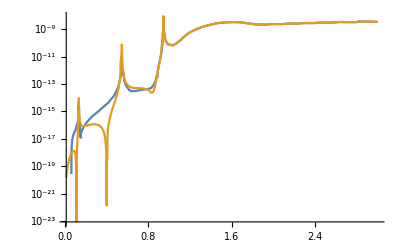

```mathematica
WidthFunc=Interpolation[width,InterpolationOrder->1];
CombinedWidthFunc[ma_,c1_,c2_,c3_]:=Piecewise[{{GammaPhoton[ma,1000,c1,c2,c3],ma<3mPi},{GammaPhoton[ma,1000,c1,c2,c3]+a2pigWidthFunc[ma]+a3piWidthFunc[ma],0.94≥ ma≥ 3mPi},{WidthFunc[ma],ma>0.94}}];
LogPlot[{WidthFunc[ma],CombinedWidthFunc[ma,1,1,1]},{ma,0.015,3}]
```

InterpolatingFunction::dmval: Input value {0.015061} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

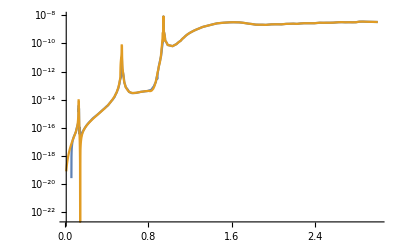

```mathematica
LogPlot[{WidthFunc[ma],CombinedWidthFunc[ma,0,0,1]},{ma,0.015,3}]
```

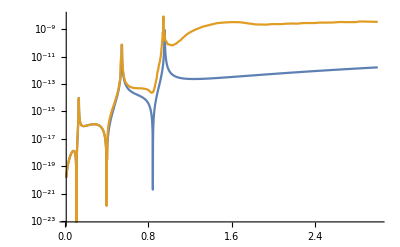

```mathematica
LogPlot[{GammaPhoton[ma,1000,1,1,1],CombinedWidthFunc[ma,1,1,1]},{ma,0.015,3}]
```

#### Width function for f_a=1 TeV

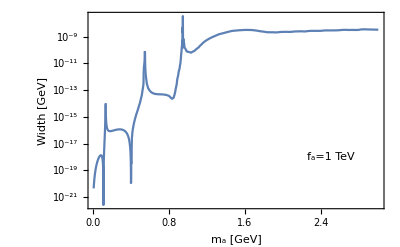

```mathematica
WidthFinal[ma_,c1_,c2_,c3_]:=CombinedWidthFunc[ma,c1,c2,c3];

LifetimeFinal[ma_,c1_,c2_,c3_]:=1/WidthFinal[ma,c1,c2,c3]*0.198*10^(-15); (*in meter*);

LogPlot[WidthFinal[ma,1,1,1],{ma,10^-2,3},Frame->True,FrameLabel->{"m_a [GeV]","Width [GeV]"},Epilog->Inset[Framed["f_a=1 TeV"],{2.5,Log[10^-18]}]]
```

#### Lifetime calculation

```mathematica
LifetimeFinal[0.4,1,1,1] 1/((1000*4 Pi^2)^2)
```

3.1576×10^-7

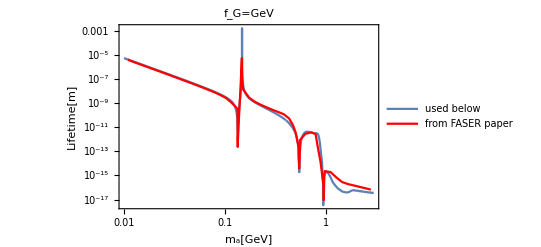

```mathematica
lifetimeFASER=Import["./lifetime-faser.csv","Data"]; 
lifetimeFASER[[All,2]]=lifetimeFASER[[All,2]]/10^9; 
Show[LogLogPlot[LifetimeFinal[ma,0,0,1] 1/((1000*4 Pi^2)^2),{ma,0.01,3},FrameLabel-> {"m_a[GeV]","Lifetime[m]"},PlotLegends->{"used below"},PlotLabel->"f_G=GeV",Frame->True],ListLogLogPlot[lifetimeFASER,Joined-> True,PlotStyle->Red,PlotLegends->{"from FASER paper"}]]
```

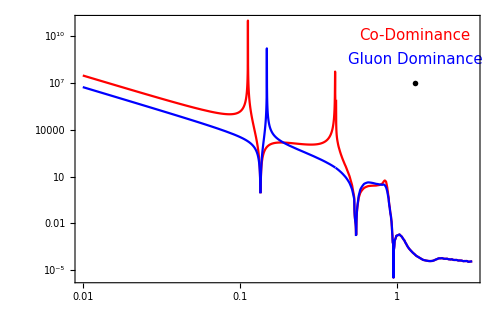

```mathematica
LogLogPlot[{LifetimeFinal[ma,1,1,1] 10^6/((4 Pi^2)^2),LifetimeFinal[ma,0,0,1] 10^6/((4 Pi^2)^2)},{ma,0.01,3},PlotStyle->{Red,Blue},Frame->True,FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],LabelStyle->{FontFamily->"CMU Serif",FontSize->12},FrameLabel->{{Style[MaTeX["\\text{Lifetime [m]}",Magnification->1.5],FontSize->15,Black],None},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},Epilog->{Style[Text[Style["Co-Dominance",{15,Red},FontFamily->"CMU Serif"],{Log[1.3],Log[10^10]}],20],Style[Text[Style["Gluon Dominance",{15,Blue},FontFamily->"CMU Serif"],{Log[1.3],Log[10^8.5]}],20],Style[Text[Style[MaTeX["f_G= 1\\text{ PeV}",Magnification->1.4],{15,Black},FontFamily->"CMU Serif"],{Log[1.3],Log[10^7]}],20]},ImageSize->500,FrameTicks->{{LogTicks[10,10^-6,10^12,TickLabelStep->3,ShowMinorTicks->False],LogTicks[10,10^-6,10^12,TickLabelStep->3,ShowMinorTicks->False]},{LogTicks[10,10^-2,3],LogTicks[10,10^-2,3,ShowTickLabels-> False]}}]
```

#### The low mass scaling (away from resonances) can be obtained just by looking at c_i:

```mathematica
LifetimeFinal[0.01,1,1,1]/LifetimeFinal[0.01,0,0,1]
```

5.52504

```mathematica
(1.92/(8/3-1.92))^2(*the ratio of effective cγ's *)
```

6.61224

#### Explaining the large lifetime peaks

```mathematica
NSolve[cgamma[ma,1,1,1]==0,ma](*codominance*)
```

{{ma→0.845108},{ma→-0.845108},{ma→-0.402472},{ma→0.402472},{ma→-0.11232},{ma→0.11232}}

Hence at m_a=0.11 and 0.40 we will have very large lifetime. The one at m_a=0.84 is not important since hadronic modes dominate there. Note in reality, there will be smoothing out due to a non-zero width.

```mathematica
NSolve[cgamma[ma,0,0,1]==0,ma] (*Gluon dominance*)
```

{{ma→0.-3.34561 ⅈ},{ma→0.+3.34561 ⅈ},{ma→0.690706},{ma→-0.690706},{ma→0.148225},{ma→-0.148225}}

Hence at m_a=0.15 we will have very large lifetime. The one at m_a=0.69 is not important since hadronic modes dominate there. Note in reality, there will be smoothing out due to a non-zero width.

#### Importing Pythia data

```mathematica
(*pi0=Import["/Users/soubhik/Documents/pythia8244/examples/mesons-pn-1M.txt","Data"];*)
pi0=Import["./mesons-pn-100K.txt","Data"];
(* I am not copying the simulation files, but here is the order of various quantities in pi0:
part.id(); part.px(); part.py(); part.pz(); part.e(); part.eta(); part.pT(); part.m()
*)
```

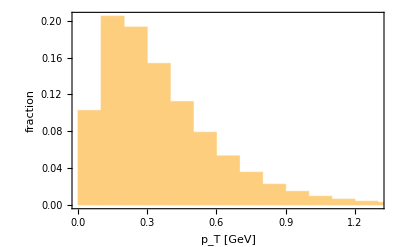

```mathematica
Histogram[pi0[[All,7]],{0.1},"Probability",Frame->True,FrameLabel->{"p_T [GeV]","fraction"}]
```

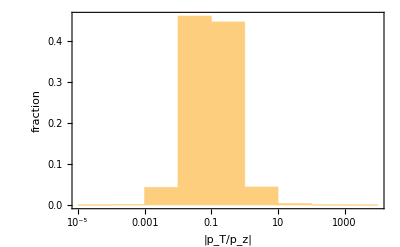

```mathematica
Histogram[Abs[pi0[[All,7]]/pi0[[All,4]]],(*{0.01},"Probability",*){"Log",10},"Probability",Frame-> True,FrameLabel->{"|p_T/p_z|","fraction"}]
```

#### Boost of axions, m_a=input

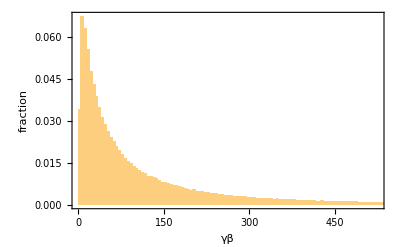

```mathematica
ma=0.05;
Histogram[Sqrt[pi0[[All,7]]^2+pi0[[All,4]]^2]/ma,{5.0},"Probability",FrameLabel->{"γβ","fraction"},Frame->True]
```

#### Energy distribution of axions at ND, m_a= input

```mathematica
ma=0.05;
enlist={};
dist=579; (* distance in m to HPTPC *)
length=10; (* decay length in m of HPTPC *)
radius=2.5; (* radius in m of HPTPC *)
For[i=1,i<Length[pi0]+1,i++,
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[enlist,pi0[[i]][[5]]],Continue]];
```

```mathematica
Length[enlist]/Length[pi0]//N
```

0.0102782

```mathematica
Naxions[0.05,1/(4 Pi^2),Length[enlist]/Length[pi0]]
```

4.17756×10^18

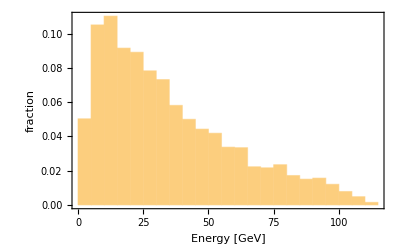

```mathematica
Histogram[enlist,{5.0},"Probability",FrameLabel->{"Energy [GeV]","fraction"},Frame->True]
```

```mathematica
Histogram[enlist,{1.0},NPOT*2.49*mixingAPi[0.05,1/(4 Pi^2)]^2/Length[pi0]#2&,Frame->True,FrameLabel->{"Energy [GeV]","N_a"}]
```

-Graphics-

## Main code

```mathematica
dist=574; (* distance in m to LArTPC and MPD *)
length=10; (* decay length in m of LArTPC and MPD *)
radius=2.5; (* radius in m of MPD *)
lifetime=Table[10^x,{x,-3,6,1/3}];
masslist=(*Table[0.001*y,{y,1,10,1}];*)Flatten[{Table[0.001+y*0.001,{y,0,8,1}],Table[0.01+y*0.01,{y,0,11,1}],Table[0.12+y*0.001,{y,1,50,1}],Table[0.17+y*0.03,{y,1,7,1}],Table[0.40+y*0.01,{y,1,30,1}],Table[0.70+y*0.05,{y,1,2,1}]}];
axions={};
For[nn=1,nn<Length[masslist]+1,nn++,ma=masslist[[nn]];
For[j=1,j<Length[lifetime]+1,j++,
(*fa=(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetime[[j]]/(0.198*10^(-15))];*)
fa=Sqrt[lifetime[[j]]/LifetimeFinal[ma,1,1,1]]*1000; (* in GeV, codominance*)
decayprob={};
list={};
For[i=1,i<Length[pi0]+1,i++,gabeta=Sqrt[(pi0[[i]][[7]])^2+(pi0[[i]][[4]])^2]/ma;
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[decayprob,Exp[-dist/(gabeta*lifetime[[j]])]-Exp[-(dist+length)/(gabeta*lifetime[[j]])]],Continue]];

AppendTo[axions,{ma,fa,Sum[decayprob[[i]],{i,Length[decayprob]}]*Naxions[ma,fa,Length[decayprob]/Length[pi0]]/Length[decayprob],lifetime[[j]]}]]]
```

General::munfl: Exp[-1015.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1032.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.41} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetime/(0.198*10^(-15))]
```

{226.843,332.96,488.718,717.34,1052.91,1545.46,2268.43,3329.6,4887.18,7173.4,10529.1,15454.6,22684.3,33296.,48871.8,71734.,105291.,154546.,226843.,332960.,488718.,717340.,1.05291×10^6,1.54546×10^6,2.26843×10^6,3.3296×10^6,4.88718×10^6,7.1734×10^6}

```mathematica
Sqrt[lifetime/LifetimeFinal[ma]]*1000
```

{468.485,687.643,1009.32,1481.48,2174.52,3191.75,4684.85,6876.43,10093.2,14814.8,21745.2,31917.5,46848.5,68764.3,100932.,148148.,217452.,319175.,468485.,687643.,1.00932×10^6,1.48148×10^6,2.17452×10^6,3.19175×10^6,4.68485×10^6,6.87643×10^6,1.00932×10^7,1.48148×10^7}

## Results of Meson - mixing Simulation

```mathematica
axionfinallistco={{0.001,0.0046923746023240865,5.298123480532826*^13,1/1000},{0.001,0.006887464004699696,5.068319311584064*^14,1/(100 10^(2/3))},{0.001,0.010109414621871577,1.0411047364179978*^15,1/(100 10^(1/3))},{0.001,0.014838591378070944,9.689837533449012*^14,1/100},{0.001,0.021780073557275684,5.66111334582036*^14,1/(10 10^(2/3))},{0.001,0.03196877601612406,2.420884575479634*^14,1/(10 10^(1/3))},{0.001,0.04692374602324087,8.254258448380055*^13,1/10},{0.001,0.06887464004699695,2.3951540212254207*^13,1/10^(2/3)},{0.001,0.10109414621871578,6.200885611795485*^12,1/10^(1/3)},{0.001,0.14838591378070945,1.4887639679268916*^12,1},{0.001,0.21780073557275687,3.4112835397787274*^11,10^(1/3)},{0.001,0.3196877601612405,7.595931806047607*^10,10^(2/3)},{0.001,0.4692374602324087,1.663931446183876*^10,10},{0.001,0.6887464004699695,3.613805421575316*^9,10 10^(1/3)},{0.001,1.0109414621871577,7.815457062263811*^8,10 10^(2/3)},{0.001,1.4838591378070944,1.6868015660298103*^8,100},{0.001,2.1780073557275683,3.63713390523268*^7,100 10^(1/3)},{0.001,3.196877601612405,7.839005846443557*^6,100 10^(2/3)},{0.001,4.6923746023240875,1.6891668384308978*^6,1000},{0.001,6.887464004699695,363950.4039020039,1000 10^(1/3)},{0.001,10.109414621871577,78413.78244706873,1000 10^(2/3)},{0.001,14.838591378070943,16894.041835194945,10000},{0.001,21.78007355727569,3639.7414330298616,10000 10^(1/3)},{0.001,31.96877601612405,784.1615662233485,10000 10^(2/3)},{0.001,46.92374602324087,168.94279262669681,100000},{0.001,68.87464004699694,36.39765176232648,100000 10^(1/3)},{0.001,101.09414621871578,7.841639403195522,100000 10^(2/3)},{0.001,148.38591378070942,1.6894303037821499,1000000},{0.002,0.0133106286438957,2.867621860291231*^10,1/1000},{0.002,0.01953733097509945,4.543682657839255*^12,1/(100 10^(2/3))},{0.002,0.028676880096540947,3.5488798546833375*^13,1/(100 10^(1/3))},{0.002,0.04209190360338871,6.599207266979677*^13,1/100},{0.002,0.061782465281872694,5.809961722839657*^13,1/(10 10^(2/3))},{0.002,0.09068425729261867,3.277053796031582*^13,1/(10 10^(1/3))},{0.002,0.13310628643895703,1.3663960212458545*^13,1/10},{0.002,0.1953733097509945,4.574978847973489*^12,1/10^(2/3)},{0.002,0.28676880096540946,1.3105076507853132*^12,1/10^(1/3)},{0.002,0.42091903603388703,3.3627436390652423*^11,1},{0.002,0.6178246528187269,8.028722966375943*^10,10^(1/3)},{0.002,0.9068425729261866,1.8333336828431232*^10,10^(2/3)},{0.002,1.33106286438957,4.073952152499587*^9,10},{0.002,1.953733097509945,8.914347224464641*^8,10 10^(1/3)},{0.002,2.8676880096540946,1.934982646051052*^8,10 10^(2/3)},{0.002,4.20919036033887,4.183598049797842*^7,100},{0.002,6.17824652818727,9.028266249548523*^6,100 10^(1/3)},{0.002,9.068425729261868,1.9465869260138045*^6,100 10^(2/3)},{0.002,13.3106286438957,419530.41532450065,1000},{0.002,19.53733097509945,90400.20338451199,1000 10^(1/3)},{0.002,28.676880096540945,19477.645780183342,1000 10^(2/3)},{0.002,42.09190360338871,4196.482849839565,10000},{0.002,61.782465281872696,904.1199520781056,10000 10^(1/3)},{0.002,90.68425729261867,194.78825187784426,10000 10^(2/3)},{0.002,133.106286438957,41.96600801490793,100000},{0.002,195.3733097509945,9.04131747725876,100000 10^(1/3)},{0.002,286.76880096540947,1.9478943149997512,100000 10^(2/3)},{0.002,420.9190360338871,0.4196612593957391,1000000},{0.003,0.024492660659295933,4.0822937270557046*^7,1/1000},{0.003,0.03595030937783045,1.0476998415214558*^11,1/(100 10^(2/3))},{0.003,0.052767837775566345,3.026950145609407*^12,1/(100 10^(1/3))},{0.003,0.07745259364097645,1.058283282823563*^13,1/100},{0.003,0.11368486022165501,1.31065508183092*^13,1/(10 10^(2/3))},{0.003,0.16686655457306257,9.119640981072611*^12,1/(10 10^(1/3))},{0.003,0.2449266065929593,4.406594635384736*^12,1/10},{0.003,0.3595030937783044,1.6417287111935344*^12,1/10^(2/3)},{0.003,0.5276783777556634,5.072961810462735*^11,1/10^(1/3)},{0.003,0.7745259364097645,1.3726241851384329*^11,1},{0.003,1.13684860221655,3.389937241252744*^10,10^(1/3)},{0.003,1.6686655457306254,7.904223068531307*^9,10^(2/3)},{0.003,2.449266065929593,1.7787261794118721*^9,10},{0.003,3.5950309377830445,3.919295593047261*^8,10 10^(1/3)},{0.003,5.276783777556634,8.537658010836446*^7,10 10^(2/3)},{0.003,7.745259364097645,1.8491079444921795*^7,100},{0.003,11.368486022165499,3.993677319853665*^6,100 10^(1/3)},{0.003,16.68665545730626,861409.2822077284,100 10^(2/3)},{0.003,24.492660659295932,185685.14242491254,1000},{0.003,35.95030937783045,40014.682797873946,1000 10^(1/3)},{0.003,52.76783777556634,8621.906055156416,1000 10^(2/3)},{0.003,77.45259364097646,1857.633786505334,10000},{0.003,113.684860221655,400.22511253556985,10000 10^(1/3)},{0.003,166.86655457306253,86.22689125321035,10000 10^(2/3)},{0.003,244.9266065929593,18.57712103963421,100000},{0.003,359.5030937783044,4.002329447097474,100000 10^(1/3)},{0.003,527.6783777556634,0.8622767449429322,100000 10^(2/3)},{0.003,774.5259364097645,0.18577199370790237,1000000},{0.004,0.037748569487776676,87275.2935707991,1/1000},{0.004,0.05540732264793942,3.573204083257237*^9,1/(100 10^(2/3))},{0.004,0.08132682760354518,3.7919054150873334*^11,1/(100 10^(1/3))},{0.004,0.11937145799450992,2.452551083165498*^12,1/100},{0.004,0.17521333861932029,4.1535906633942534*^12,1/(10 10^(2/3))},{0.004,0.257178010103056,3.468433114040747*^12,1/(10 10^(1/3))},{0.004,0.3774856948777668,1.8911185808675815*^12,1/10},{0.004,0.5540732264793942,7.694106496369412*^11,1/10^(2/3)},{0.004,0.8132682760354518,2.531277626623282*^11,1/10^(1/3)},{0.004,1.1937145799450992,7.160890210083118*^10,1},{0.004,1.752133386193203,1.82185206674917*^10,10^(1/3)},{0.004,2.57178010103056,4.326709800841051*^9,10^(2/3)},{0.004,3.774856948777668,9.847474147995138*^8,10},{0.004,5.540732264793942,2.1840289049827865*^8,10 10^(1/3)},{0.004,8.132682760354518,4.7739850080431305*^7,10 10^(2/3)},{0.004,11.937145799450992,1.0357213707731193*^7,100},{0.004,17.52133386193203,2.2387581228701137*^6,100 10^(1/3)},{0.004,25.7178010103056,483070.22602583835,100 10^(2/3)},{0.004,37.748569487776685,104149.14369988265,1000},{0.004,55.40732264793941,22445.752307101782,1000 10^(1/3)},{0.004,81.32682760354518,4836.541513052212,1000 10^(2/3)},{0.004,119.37145799450991,1042.07639693456,10000},{0.004,175.2133386193203,224.5160672367192,10000 10^(1/3)},{0.004,257.17801010305595,48.371271787155166,10000 10^(2/3)},{0.004,377.4856948777668,10.42134973934522,100000},{0.004,554.0732264793942,2.2452192540755327,100000 10^(1/3)},{0.004,813.2682760354517,0.4837185763038066,100000 10^(2/3)},{0.004,1193.7145799450993,0.10421408320856385,1000000},{0.005,0.05279309556680506,234.15617652002538,1/1000},{0.005,0.0774896670084584,1.5149640664842868*^8,1/(100 10^(2/3))},{0.005,0.11373927648329328,5.876995574410209*^10,1/(100 10^(1/3))},{0.005,0.16694642672204194,6.99170689953816*^11,1/100},{0.005,0.2450438428747347,1.597030147938381*^12,1/(10 10^(2/3))},{0.005,0.35967517310683306,1.5759043949987944*^12,1/(10 10^(1/3))},{0.005,0.5279309556680506,9.549593876957535*^11,1/10},{0.005,0.7748966700845841,4.191496305504561*^11,1/10^(2/3)},{0.005,1.1373927648329327,1.4562416252937457*^11,1/10^(1/3)},{0.005,1.6694642672204194,4.282334817424895*^10,1},{0.005,2.4504384287473466,1.118991755133741*^10,10^(1/3)},{0.005,3.59675173106833,2.7023118473186164*^9,10^(2/3)},{0.005,5.279309556680506,6.21435415988505*^8,10},{0.005,7.74896670084584,1.3867490543008417*^8,10 10^(1/3)},{0.005,11.373927648329328,3.041336093310794*^7,10 10^(2/3)},{0.005,16.694642672204193,6.609259238497194*^6,100},{0.005,24.50438428747347,1.4297754008804508*^6,100 10^(1/3)},{0.005,35.967517310683306,308629.07047876203,100 10^(2/3)},{0.005,52.79309556680506,66551.82301748793,1000},{0.005,77.4896670084584,14344.143761361884,1000 10^(1/3)},{0.005,113.73927648329327,3090.9517264127458,1000 10^(2/3)},{0.005,166.94642672204196,665.9853640752309,10000},{0.005,245.04384287473468,143.48819907478793,10000 10^(1/3)},{0.005,359.67517310683303,30.914195645462982,10000 10^(2/3)},{0.005,527.9309556680506,6.660321582597477,100000},{0.005,774.896670084584,1.434928789797752,100000 10^(1/3)},{0.005,1137.3927648329327,0.3091466366182714,100000 10^(2/3)},{0.005,1669.4642672204195,0.06660368385283497,1000000},{0.006,0.06943205306052297,0.7266778634137041,1/1000},{0.006,0.1019123166317323,7.390733059976804*^6,1/(100 10^(2/3))},{0.006,0.14958682371372511,1.0437186234184706*^10,1/(100 10^(1/3))},{0.006,0.21956343029291733,2.277818902562604*^11,1/100},{0.006,0.3222750421805334,6.966711169237014*^11,1/(10 10^(2/3))},{0.006,0.4730350708854585,8.042791449205435*^11,1/(10 10^(1/3))},{0.006,0.6943205306052297,5.365192499924158*^11,1/10},{0.006,1.0191231663173228,2.5186384520431024*^11,1/10^(2/3)},{0.006,1.4958682371372511,9.187946798906996*^10,1/10^(1/3)},{0.006,2.1956343029291734,2.7969959997193024*^10,1},{0.006,3.2227504218053338,7.488461272054715*^9,10^(1/3)},{0.006,4.730350708854584,1.8367460752460403*^9,10^(2/3)},{0.006,6.943205306052296,4.2645825021375614*^8,10},{0.006,10.191231663173228,9.571974472684251*^7,10 10^(1/3)},{0.006,14.95868237137251,2.1060412443316724*^7,10 10^(2/3)},{0.006,21.95634302929173,4.58426998618501*^6,100},{0.006,32.22750421805333,992506.4164149133,100 10^(1/3)},{0.006,47.30350708854584,214322.43972489488,100 10^(2/3)},{0.006,69.43205306052297,46224.08576731838,1000},{0.006,101.91231663173228,9963.666551286464,1000 10^(1/3)},{0.006,149.5868237137251,2147.106622039315,1000 10^(2/3)},{0.006,219.56343029291733,462.630110750783,10000},{0.006,322.2750421805334,99.67563887620895,10000 10^(1/3)},{0.006,473.0350708854584,21.474965791973283,10000 10^(2/3)},{0.006,694.3205306052297,4.626691168506691,100000},{0.006,1019.1231663173228,0.9967953996866855,100000 10^(1/3)},{0.006,1495.8682371372508,0.21475355923421863,100000 10^(2/3)},{0.006,2195.6343029291734,0.046267301815117116,1000000},{0.007,0.08752138008164681,0.002496700997547776,1/1000},{0.007,0.12846381758511397,398119.9448791617,1/(100 10^(2/3))},{0.007,0.18855909736736542,2.0393884090004778*^9,1/(100 10^(1/3))},{0.007,0.27676690501929746,8.151590932864482*^10,1/100},{0.007,0.40623826048935174,3.324863852446899*^11,1/(10 10^(2/3))},{0.007,0.596276221226334,4.4599770421466187*^11,1/(10 10^(1/3))},{0.007,0.875213800816468,3.253760975916354*^11,1/10},{0.007,1.2846381758511398,1.623316622342117*^11,1/10^(2/3)},{0.007,1.8855909736736542,6.190745294256404*^10,1/10^(1/3)},{0.007,2.767669050192975,1.9449246068784065*^10,1},{0.007,4.062382604893517,5.324755731717436*^9,10^(1/3)},{0.007,5.962762212263339,1.325245339959201*^9,10^(2/3)},{0.007,8.752138008164682,3.104803177903647*^8,10},{0.007,12.846381758511399,7.007371322747232*^7,10 10^(1/3)},{0.007,18.85590973673654,1.5465964578243019*^7,10 10^(2/3)},{0.007,27.676690501929748,3.3719728735232735*^6,100},{0.007,40.62382604893517,730621.8443778572,100 10^(1/3)},{0.007,59.6276221226334,157830.77405176676,100 10^(2/3)},{0.007,87.52138008164681,34046.29054658108,1000},{0.007,128.463817585114,7339.336642882695,1000 10^(1/3)},{0.007,188.5590973673654,1581.641538220752,1000 10^(2/3)},{0.007,276.76690501929744,340.7973171272788,10000},{0.007,406.23826048935166,73.42685574757758,10000 10^(1/3)},{0.007,596.276221226334,15.819766554837438,10000 10^(2/3)},{0.007,875.213800816468,3.4083083926833004,100000},{0.007,1284.6381758511397,0.73430208445753,100000 10^(1/3)},{0.007,1885.5909736736542,0.15820101845892065,100000 10^(2/3)},{0.007,2767.6690501929747,0.03408341924132672,1000000},{0.008,0.10694808515959464,9.253166595108932*^-6,1/1000},{0.008,0.15697832107083576,23107.65956554125,1/(100 10^(2/3))},{0.008,0.23041266470031477,4.281092858575371*^8,1/(100 10^(1/3))},{0.008,0.33819954049797146,3.1301977671176376*^10,1/100},{0.008,0.496409037853043,1.698579980843267*^11,1/(10 10^(2/3))},{0.008,0.7286288222016728,2.6346137827672855*^11,1/(10 10^(1/3))},{0.008,1.0694808515959464,2.09191946927302*^11,1/10},{0.008,1.5697832107083574,1.103863219882233*^11,1/10^(2/3)},{0.008,2.3041266470031476,4.385517347576445*^10,1/10^(1/3)},{0.008,3.3819954049797154,1.4184807259022089*^10,1},{0.008,4.96409037853043,3.964648409676791*^9,10^(1/3)},{0.008,7.2862882220167275,1.0004565609065298*^9,10^(2/3)},{0.008,10.694808515959462,2.3639629653724787*^8,10},{0.008,15.697832107083572,5.363475210876682*^7,10 10^(1/3)},{0.008,23.041266470031477,1.1873672090705274*^7,10 10^(2/3)},{0.008,33.819954049797154,2.5928953639816763*^6,100},{0.008,49.6409037853043,562258.9739320625,100 10^(1/3)},{0.008,72.86288222016728,121506.50997091876,100 10^(2/3)},{0.008,106.94808515959464,26215.307649273134,1000},{0.008,156.97832107083573,5651.686852748493,1000 10^(1/3)},{0.008,230.41266470031476,1217.9968502622794,1000 10^(2/3)},{0.008,338.1995404979715,262.44728800798396,10000},{0.008,496.409037853043,56.54633808193903,10000 10^(1/3)},{0.008,728.6288222016727,12.182917711287374,10000 10^(2/3)},{0.008,1069.4808515959464,2.6247679056702515,100000},{0.008,1569.7832107083573,0.5654928882230776,100000 10^(1/3)},{0.008,2304.126647003148,0.1218321280760705,100000 10^(2/3)},{0.008,3381.9954049797147,0.026247974168524358,1000000},{0.009000000000000001,0.12761998511473155,3.6389687172109875*^-8,1/1000},{0.009000000000000001,0.18732052068534238,1422.8331952151686,1/(100 10^(2/3))},{0.009000000000000001,0.27494892307253027,9.511479693594521*^7,1/(100 10^(1/3))},{0.009000000000000001,0.40356982791933665,1.2707937759614408*^10,1/100},{0.009000000000000001,0.592359497854367,9.160507118292802*^10,1/(10 10^(2/3))},{0.009000000000000001,0.8694648371196169,1.6372124322320538*^11,1/(10 10^(1/3))},{0.009000000000000001,1.2761998511473154,1.4095533453041904*^11,1/10},{0.009000000000000001,1.8732052068534237,7.83780683918045*^10,1/10^(2/3)},{0.009000000000000001,2.7494892307253025,3.234530188988549*^10,1/10^(1/3)},{0.009000000000000001,4.035698279193366,1.0750144625012371*^10,1},{0.009000000000000001,5.92359497854367,3.063262587425778*^9,10^(1/3)},{0.009000000000000001,8.694648371196166,7.832041009815029*^8,10^(2/3)},{0.009000000000000001,12.761998511473154,1.8657487692650196*^8,10},{0.009000000000000001,18.732052068534237,4.2544677577780224*^7,10 10^(1/3)},{0.009000000000000001,27.494892307253025,9.446342814916275*^6,10 10^(2/3)},{0.009000000000000001,40.35698279193367,2.066074492079233*^6,100},{0.009000000000000001,59.235949785436695,448371.10828031704,100 10^(1/3)},{0.009000000000000001,86.94648371196166,96931.35807176506,100 10^(2/3)},{0.009000000000000001,127.61998511473152,20916.8786010939,1000},{0.009000000000000001,187.32052068534236,4509.787758724048,1000 10^(1/3)},{0.009000000000000001,274.9489230725302,971.9434398496333,1000 10^(2/3)},{0.009000000000000001,403.56982791933666,209.4328172447037,10000},{0.009000000000000001,592.3594978543671,45.12432956440878,10000 10^(1/3)},{0.009000000000000001,869.4648371196166,9.722081871095096,10000 10^(2/3)},{0.009000000000000001,1276.1998511473155,2.094593025468043,100000},{0.009000000000000001,1873.2052068534238,0.4512697858510406,100000 10^(1/3)},{0.009000000000000001,2749.4892307253026,0.09722346796141194,100000 10^(2/3)},{0.009000000000000001,4035.698279193366,0.020946195188835077,1000000},{0.01,0.14945961366696478,1.5021605053260154*^-10,1/1000},{0.01,0.21937671147944837,91.98147223747449,1/(100 10^(2/3))},{0.01,0.3220009764428724,2.2146202564226795*^7,1/(100 10^(1/3))},{0.01,0.4726327973964393,5.401370983599189*^9,1/100},{0.01,0.6937300738726637,5.167088491952702*^10,1/(10 10^(2/3))},{0.01,1.0182564943577,1.0613933281921762*^11,1/(10 10^(1/3))},{0.01,1.4945961366696479,9.878668830817467*^10,1/10},{0.01,2.1937671147944835,5.771434635929822*^10,1/10^(2/3)},{0.01,3.2200097644287236,2.4680617106575035*^10,1/10^(1/3)},{0.01,4.726327973964393,8.41511381114973*^9,1},{0.01,6.937300738726636,2.441829730664724*^9,10^(1/3)},{0.01,10.182564943576997,6.321725746716917*^8,10^(2/3)},{0.01,14.945961366696478,1.5177763461601314*^8,10},{0.01,21.937671147944837,3.477761134917397*^7,10 10^(1/3)},{0.01,32.20009764428723,7.743957988396596*^6,10 10^(2/3)},{0.01,47.26327973964393,1.6963574112870574*^6,100},{0.01,69.37300738726636,368422.9674184053,100 10^(1/3)},{0.01,101.82564943576996,79677.61256374411,100 10^(2/3)},{0.01,149.45961366696477,17196.732139823132,1000},{0.01,219.37671147944837,3708.012773083359,1000 10^(1/3)},{0.01,322.00097644287234,799.176894891592,1000 10^(2/3)},{0.01,472.63279739643934,172.208457977296,10000},{0.01,693.7300738726636,37.10429094996832,10000 10^(1/3)},{0.01,1018.2564943576997,7.994187579434473,10000 10^(2/3)},{0.01,1494.5961366696479,1.722326550138384,100000},{0.01,2193.7671147944834,0.37106711152368393,100000 10^(1/3)},{0.01,3220.0097644287234,0.07994429623649549,100000 10^(2/3)},{0.01,4726.327973964393,0.01722350755574092,1000000},{0.02,0.42041538397874684,1.1588315467522148*^-33,1/1000},{0.02,0.6170853927010558,6.493373408003945*^-10,1/(100 10^(2/3))},{0.02,0.9057574874668869,55.33157440621635,1/(100 10^(1/3))},{0.02,1.3294701767471024,5.317753565845259*^6,1/100},{0.02,1.9513953517547804,8.425861509278654*^8,1/(10 10^(2/3))},{0.02,2.8642566681467776,6.581086845279555*^9,1/(10 10^(1/3))},{0.02,4.204153839787469,1.2237651854198494*^10,1/10},{0.02,6.170853927010558,1.0774065122351002*^10,1/10^(2/3)},{0.02,9.05757487466887,6.077009228665826*^9,1/10^(1/3)},{0.02,13.294701767471024,2.533861739217937*^9,1},{0.02,19.5139535175478,8.483897552659491*^8,10^(1/3)},{0.02,28.64256668146777,2.4302216514430305*^8,10^(2/3)},{0.02,42.04153839787469,6.235913537026306*^7,10},{0.02,61.708539270105575,1.4888563507914318*^7,10 10^(1/3)},{0.02,90.57574874668867,3.3997567337323595*^6,10 10^(2/3)},{0.02,132.94701767471022,755478.7430668209,100},{0.02,195.139535175478,165308.76122999482,100 10^(1/3)},{0.02,286.4256668146777,35882.5583260189,100 10^(2/3)},{0.02,420.41538397874683,7758.116143359445,1000},{0.02,617.0853927010558,1674.2128976887311,1000 10^(1/3)},{0.02,905.7574874668868,360.9774953377749,1000 10^(2/3)},{0.02,1329.4701767471022,77.79824086868389,10000},{0.02,1951.3953517547802,16.76392590522041,10000 10^(1/3)},{0.02,2864.2566681467765,3.61195880586995,10000 10^(2/3)},{0.02,4204.153839787468,0.7782009876461345,100000},{0.02,6170.8539270105575,0.16766112595566937,100000 10^(1/3)},{0.02,9057.574874668868,0.03612177516679179,100000 10^(2/3)},{0.02,13294.701767471024,0.007782228607467193,1000000},{0.03,0.762256329982796,4.227518677304427*^-56,1/1000},{0.03,1.1188392828890343,2.2446562955687213*^-20,1/(100 10^(2/3))},{0.03,1.6422314800113262,0.0006757989875477151,1/(100 10^(1/3))},{0.03,2.410466163626532,24606.234572997382,1/100},{0.03,3.5380804695988037,6.3150644677306294*^7,1/(10 10^(2/3))},{0.03,5.193191922065072,1.8245097071286058*^9,1/(10 10^(1/3))},{0.03,7.62256329982796,6.3788567023616705*^9,1/10},{0.03,11.188392828890343,7.900040649716478*^9,1/10^(2/3)},{0.03,16.42231480011326,5.496910320650491*^9,1/10^(1/3)},{0.03,24.10466163626532,2.656097491166855*^9,1},{0.03,35.38080469598803,9.895603911379561*^8,10^(1/3)},{0.03,51.931919220650705,3.057753719699454*^8,10^(2/3)},{0.03,76.2256329982796,8.273562594538106*^7,10},{0.03,111.88392828890345,2.0433020385861672*^7,10 10^(1/3)},{0.03,164.2231480011326,4.764310947361774*^6,10 10^(2/3)},{0.03,241.04661636265317,1.0721363169353982*^6,100},{0.03,353.80804695988036,236237.54969976333,100 10^(1/3)},{0.03,519.3191922065072,51461.171038809094,100 10^(2/3)},{0.03,762.2563299827959,11145.59286398622,1000},{0.03,1118.8392828890346,2407.209463882785,1000 10^(1/3)},{0.03,1642.2314800113263,519.2188577926786,1000 10^(2/3)},{0.03,2410.466163626532,111.92267084914421,10000},{0.03,3538.080469598803,24.119055048954163,10000 10^(1/3)},{0.03,5193.191922065071,5.196898044191451,10000 10^(2/3)},{0.03,7622.56329982796,1.119698281349361,100000},{0.03,11188.392828890344,0.24123773690721761,100000 10^(1/3)},{0.03,16422.31480011326,0.051973700437451996,100000 10^(2/3)},{0.03,24104.66163626532,0.011197454875984383,1000000},{0.04,1.1487912499704993,2.264690072799498*^-78,1/1000},{0.04,1.6861949553573408,1.1494644660206325*^-30,1/(100 10^(2/3))},{0.04,2.474995720541533,1.2381182898704856*^-8,1/(100 10^(1/3))},{0.04,3.6327969059786183,169.1388352010749,1/100},{0.04,5.332216638015137,6.924841519869325*^6,1/(10 10^(2/3))},{0.04,7.826623676080832,7.348682987588462*^8,1/(10 10^(1/3))},{0.04,11.487912499704994,4.753024785201517*^9,1/10},{0.04,16.861949553573407,8.049626165263565*^9,1/10^(2/3)},{0.04,24.749957205415328,6.7217962023329315*^9,1/10^(1/3)},{0.04,36.32796905978618,3.66497299416788*^9,1},{0.04,53.32216638015136,1.491111811217515*^9,10^(1/3)},{0.04,78.2662367608083,4.905596209656881*^8,10^(2/3)},{0.04,114.87912499704991,1.387774912671827*^8,10},{0.04,168.61949553573405,3.530735032459705*^7,10 10^(1/3)},{0.04,247.49957205415328,8.385129697371583*^6,10 10^(2/3)},{0.04,363.2796905978618,1.9084327750939545*^6,100},{0.04,533.2216638015136,423263.09075614996,100 10^(1/3)},{0.04,782.662367608083,92519.455448498,100 10^(2/3)},{0.04,1148.7912499704994,20072.19902426528,1000},{0.04,1686.1949553573406,4338.69570306308,1000 10^(1/3)},{0.04,2474.9957205415326,936.1863135304052,1000 10^(2/3)},{0.04,3632.7969059786183,201.84022455676327,10000},{0.04,5332.216638015136,43.499692124842845,10000 10^(1/3)},{0.04,7826.62367608083,9.373179561472151,10000 10^(2/3)},{0.04,11487.912499704991,2.019535893340344,100000},{0.04,16861.949553573406,0.4351103793829062,100000 10^(1/3)},{0.04,24749.95720541533,0.09374314576939359,100000 10^(2/3)},{0.04,36327.969059786185,0.0201964941510736,1000000},{0.05,1.555714098964519,1.327725441641813*^-100,1/1000},{0.05,2.283476015089449,6.451197152579032*^-41,1/(100 10^(2/3))},{0.05,3.351684422580855,2.5075197517071944*^-13,1/(100 10^(1/3))},{0.05,4.919599940764478,1.2851847503214404,1/100},{0.05,7.220985190047677,831500.0460233645,1/(10 10^(2/3))},{0.05,10.598956773461792,3.225635642924261*^8,1/(10 10^(1/3))},{0.05,15.557140989645191,3.837453796669411*^9,1/10},{0.05,22.83476015089449,8.765426658555258*^9,1/10^(2/3)},{0.05,33.51684422580855,8.64947628765102*^9,1/10^(1/3)},{0.05,49.19599940764478,5.241370355814298*^9,1},{0.05,72.20985190047678,2.300535998204786*^9,10^(1/3)},{0.05,105.9895677346179,7.992697683337752*^8,10^(2/3)},{0.05,155.5714098964519,2.3503934360895833*^8,10},{0.05,228.3476015089449,6.1416750171025984*^7,10 10^(1/3)},{0.05,335.16844225808546,1.4831852947042935*^7,10 10^(2/3)},{0.05,491.95999407644774,3.41079757881076*^6,100},{0.05,722.0985190047677,761128.2194632618,100 10^(1/3)},{0.05,1059.8956773461791,166926.14415793295,100 10^(2/3)},{0.05,1555.714098964519,36275.44363969085,1000},{0.05,2283.476015089449,7847.435711093119,1000 10^(1/3)},{0.05,3351.684422580855,1693.9351367110578,1000 10^(2/3)},{0.05,4919.599940764478,365.27496015401067,10000},{0.05,7220.985190047678,78.72897094791828,10000 10^(1/3)},{0.05,10598.956773461792,16.964933754056492,10000 10^(2/3)},{0.05,15557.140989645191,3.6553135030096473,100000},{0.05,22834.76015089449,0.7875463634683727,100000 10^(1/3)},{0.05,33516.84422580855,0.16967501520765862,100000 10^(2/3)},{0.05,49195.99940764478,0.03655570336603525,1000000},{0.060000000000000005,1.954334913966918,8.21376475159173*^-123,1/1000},{0.060000000000000005,2.868571355408883,3.822653062352091*^-51,1/(100 10^(2/3))},{0.060000000000000005,4.210486934590806,5.387133395599398*^-18,1/(100 10^(1/3))},{0.060000000000000005,6.180149638924677,0.01038542355636482,1/100},{0.060000000000000005,9.07121911380844,105625.74847032284,1/(10 10^(2/3))},{0.060000000000000005,13.314728771687346,1.4916458204666507*^8,1/(10 10^(1/3))},{0.060000000000000005,19.543349139669182,3.255378384127157*^9,1/10},{0.060000000000000005,28.685713554088828,9.956577725857239*^9,1/10^(2/3)},{0.060000000000000005,42.10486934590806,1.1494473683720125*^10,1/10^(1/3)},{0.060000000000000005,61.80149638924677,7.667743766321748*^9,1},{0.060000000000000005,90.71219113808439,3.599549184963022*^9,10^(1/3)},{0.060000000000000005,133.14728771687342,1.3131089293368473*^9,10^(2/3)},{0.060000000000000005,195.4334913966918,3.997367967985809*^8,10},{0.060000000000000005,286.85713554088824,1.0702244558597115*^8,10 10^(1/3)},{0.060000000000000005,421.04869345908054,2.625012666177935*^7,10 10^(2/3)},{0.060000000000000005,618.0149638924677,6.094790801484251*^6,100},{0.060000000000000005,907.1219113808438,1.3679928091182788*^6,100 10^(1/3)},{0.060000000000000005,1331.4728771687344,300987.98175590276,100 10^(2/3)},{0.060000000000000005,1954.334913966918,65516.76870905021,1000},{0.060000000000000005,2868.571355408883,14184.551416575145,1000 10^(1/3)},{0.060000000000000005,4210.4869345908055,3063.0206673976045,1000 10^(2/3)},{0.060000000000000005,6180.149638924677,660.6183198483328,10000},{0.060000000000000005,9071.21911380844,142.39720585871834,10000 10^(1/3)},{0.060000000000000005,13314.728771687342,30.685690060520347,10000 10^(2/3)},{0.060000000000000005,19543.349139669182,6.6117462660886845,100000},{0.060000000000000005,28685.713554088827,1.424529052141431,100000 10^(1/3)},{0.060000000000000005,42104.86934590805,0.3069126319059449,100000 10^(2/3)},{0.060000000000000005,61801.496389246764,0.06612303727501774,1000000},{0.06999999999999999,2.304986782074559,5.442542658745602*^-145,1/1000},{0.06999999999999999,3.3832579106075884,2.428662468589944*^-61,1/(100 10^(2/3))},{0.06999999999999999,4.965943483366392,1.243815880510333*^-22,1/(100 10^(1/3))},{0.06999999999999999,7.289008207937778,0.00009045486693782209,1/100},{0.06999999999999999,10.698800909302324,14423.788300925115,1/(10 10^(2/3))},{0.06999999999999999,15.703692139108286,7.388654362371032*^7,1/(10 10^(1/3))},{0.06999999999999999,23.049867820745586,2.953301472174799*^9,1/10},{0.06999999999999999,33.83257910607588,1.2045900476462788*^10,1/10^(2/3)},{0.06999999999999999,49.65943483366391,1.615838782014161*^10,1/10^(1/3)},{0.06999999999999999,72.89008207937778,1.1788296492574286*^10,1},{0.06999999999999999,106.98800909302324,5.881236448262414*^9,10^(1/3)},{0.06999999999999999,157.03692139108284,2.242891889689309*^9,10^(2/3)},{0.06999999999999999,230.49867820745587,7.046414316014463*^8,10},{0.06999999999999999,338.32579106075883,1.9291459876932624*^8,10 10^(1/3)},{0.06999999999999999,496.5943483366391,4.801331477165977*^7,10 10^(2/3)},{0.06999999999999999,728.9008207937777,1.1248626030960185*^7,100},{0.06999999999999999,1069.8800909302324,2.538753503946089*^6,100 10^(1/3)},{0.06999999999999999,1570.369213910828,560328.1167284714,100 10^(2/3)},{0.06999999999999999,2304.986782074559,122165.75308459868,1000},{0.06999999999999999,3383.257910607588,26470.250855018894,1000 10^(1/3)},{0.06999999999999999,4965.943483366391,5718.170369446827,1000 10^(2/3)},{0.06999999999999999,7289.008207937778,1233.488785458176,10000},{0.06999999999999999,10698.800909302325,265.90237280951885,10000 10^(1/3)},{0.06999999999999999,15703.692139108281,57.30248637045802,10000 10^(2/3)},{0.06999999999999999,23049.86782074559,12.34700350734524,100000},{0.06999999999999999,33832.579106075886,2.660237037928563,100000 10^(1/3)},{0.06999999999999999,49659.43483366391,0.5731462758699227,100000 10^(2/3)},{0.06999999999999999,72890.08207937778,0.12348218006322587,1000000},{0.08,2.5452573334157877,4.022283405765037*^-167,1/1000},{0.08,3.735926849897395,1.723604253588646*^-71,1/(100 10^(2/3))},{0.08,5.483590694169021,3.2112419934491694*^-27,1/(100 10^(1/3))},{0.08,8.048810404840486,8.832652961672122*^-7,1/100},{0.08,11.81403801745376,2205.752329227206,1/(10 10^(2/3))},{0.08,17.340636349677915,4.086536984698472*^7,1/(10 10^(1/3))},{0.08,25.45257333415788,2.9879447532010593*^9,1/10},{0.08,37.359268498973954,1.6213873752540619*^10,1/10^(2/3)},{0.08,54.83590694169022,2.514882769269722*^10,1/10^(1/3)},{0.08,80.48810404840485,1.9968514028074085*^10,1},{0.08,118.14038017453758,1.0536977410011652*^10,10^(1/3)},{0.08,173.40636349677914,4.186215863552118*^9,10^(2/3)},{0.08,254.52573334157873,1.3540173362206147*^9,10},{0.08,373.59268498973944,3.784473472706136*^8,10 10^(1/3)},{0.08,548.3590694169021,9.5499043650487*^7,10 10^(2/3)},{0.08,804.8810404840485,2.25653177998733*^7,100},{0.08,1181.4038017453759,5.119730064218865*^6,100 10^(1/3)},{0.08,1734.0636349677911,1.1334068600183558*^6,100 10^(2/3)},{0.08,2545.257333415788,247506.02597044245,1000},{0.08,3735.926849897395,53670.690355373394,1000 10^(1/3)},{0.08,5483.590694169021,11598.46009607526,1000 10^(2/3)},{0.08,8048.810404840486,2502.394314092344,10000},{0.08,11814.038017453757,539.4843819710206,10000 10^(1/3)},{0.08,17340.636349677912,116.26445256549943,10000 10^(2/3)},{0.08,25452.573334157874,25.05202723716059,100000},{0.08,37359.26849897395,5.397656849657874,100000 10^(1/3)},{0.08,54835.90694169021,1.1629260437317708,100000 10^(2/3)},{0.08,80488.10404840486,0.2505484341757638,1000000},{0.09,2.563561129510602,3.619069766194673*^-189,1/1000},{0.09,3.762793148400067,1.491800104888303*^-81,1/(100 10^(2/3))},{0.09,5.52302502743496,1.0115227963542933*^-31,1/(100 10^(1/3))},{0.09,8.106692090327396,1.0545425142666025*^-8,1/100},{0.09,11.898996713020175,412.3250875907955,1/(10 10^(2/3))},{0.09,17.465338660808424,2.756346781174409*^7,1/(10 10^(1/3))},{0.09,25.63561129510602,3.6826534322169714*^9,1/10},{0.09,37.627931484000676,2.6546378820990204*^10,1/10^(2/3)},{0.09,55.2302502743496,4.7445038659133415*^10,1/10^(1/3)},{0.09,81.06692090327394,4.084766988294485*^10,1},{0.09,118.98996713020173,2.2713304710297348*^10,10^(1/3)},{0.09,174.65338660808425,9.373396319222704*^9,10^(2/3)},{0.09,256.3561129510602,3.1153014555944633*^9,10},{0.09,376.2793148400067,8.877077221149106*^8,10 10^(1/3)},{0.09,552.302502743496,2.2696595821960127*^8,10 10^(2/3)},{0.09,810.6692090327394,5.406782940520854*^7,100},{0.09,1189.8996713020174,1.232908957126737*^7,100 10^(1/3)},{0.09,1746.5338660808422,2.7374706618255414*^6,100 10^(2/3)},{0.09,2563.5611295106023,598731.0028895183,1000},{0.09,3762.7931484000674,129934.17437586974,1000 10^(1/3)},{0.09,5523.02502743496,28089.89194351144,1000 10^(2/3)},{0.09,8106.692090327394,6061.535414218186,10000},{0.09,11898.996713020173,1306.8985450192602,10000 10^(1/3)},{0.09,17465.338660808426,281.66103048270077,10000 10^(2/3)},{0.09,25635.61129510602,60.69186817204552,100000},{0.09,37627.93148400068,13.076651010596542,100000 10^(1/3)},{0.09,55230.25027434959,2.8173775201090603,100000 10^(2/3)},{0.09,81066.92090327396,0.6069954338973458,1000000},{0.09999999999999999,2.1280749176333478,5.080995953348865*^-211,1/1000},{0.09999999999999999,3.123586805547124,2.0181529714082236*^-91,1/(100 10^(2/3))},{0.09999999999999999,4.584798425536029,4.981055644724083*^-36,1/(100 10^(1/3))},{0.09999999999999999,6.7295637711966,1.9715324776129527*^-10,1/100},{0.09999999999999999,9.877648774778383,120.72242560756021,1/(10 10^(2/3))},{0.09999999999999999,14.498405637447743,2.9066106755144846*^7,1/(10 10^(1/3))},{0.09999999999999999,21.28074917633348,7.08910817455612*^9,1/10},{0.09999999999999999,31.235868055471244,6.781620699296681*^10,1/10^(2/3)},{0.09999999999999999,45.84798425536028,1.393041163466364*^11,1/10^(1/3)},{0.09999999999999999,67.29563771196601,1.2965403075427328*^11,1},{0.09999999999999999,98.77648774778382,7.57480361573372*^10,10^(1/3)},{0.09999999999999999,144.9840563744774,3.2392436108271885*^10,10^(2/3)},{0.09999999999999999,212.8074917633348,1.1044538930871632*^10,10},{0.09999999999999999,312.35868055471246,3.2048150658584666*^9,10 10^(1/3)},{0.09999999999999999,458.47984255360285,8.297041214986151*^8,10 10^(2/3)},{0.09999999999999999,672.9563771196599,1.9920277158118895*^8,100},{0.09999999999999999,987.7648774778381,4.564438355661362*^7,100 10^(1/3)},{0.09999999999999999,1449.840563744774,1.016367067651043*^7,100 10^(2/3)},{0.09999999999999999,2128.0749176333484,2.2264090409340207*^6,1000},{0.09999999999999999,3123.586805547124,483542.1003205519,1000 10^(1/3)},{0.09999999999999999,4584.798425536028,104574.04541733081,1000 10^(2/3)},{0.09999999999999999,6729.5637711966,22570.102064501993,10000},{0.09999999999999999,9877.648774778383,4866.635478444413,10000 10^(1/3)},{0.09999999999999999,14498.40563744774,1048.891378817556,10000 10^(2/3)},{0.09999999999999999,21280.74917633348,226.0175038673372,100000},{0.09999999999999999,31235.86805547124,48.69806815403288,100000 10^(1/3)},{0.09999999999999999,45847.98425536028,10.492088155096665,100000 10^(2/3)},{0.09999999999999999,67295.637711966,2.260492616210766,1000000},{0.11,0.6456567056386869,6.11569547288453*^-232,1/1000},{0.11,0.9476944396717428,2.3443179228216117*^-100,1/(100 10^(2/3))},{0.11,1.3910252044796918,2.106341810283525*^-39,1/(100 10^(1/3))},{0.11,2.041745776379131,3.1692161930990095*^-11,1/100},{0.11,2.996872955239742,304.05393148211374,1/(10 10^(2/3))},{0.11,4.398807928857281,2.633008216914375*^8,1/(10 10^(1/3))},{0.11,6.456567056386869,1.171186982887362*^11,1/10},{0.11,9.476944396717426,1.4858065730721182*^12,1/10^(2/3)},{0.11,13.910252044796918,3.5011849764121494*^12,1/10^(1/3)},{0.11,20.417457763791308,3.514114738103241*^12,1},{0.11,29.968729552397424,2.1520383260848113*^12,10^(1/3)},{0.11,43.988079288572806,9.516521535530293*^11,10^(2/3)},{0.11,64.5656705638687,3.324208708263573*^11,10},{0.11,94.76944396717428,9.81295069894947*^10,10 10^(1/3)},{0.11,139.10252044796914,2.5710335986157543*^10,10 10^(2/3)},{0.11,204.17457763791307,6.2194489229050455*^9,100},{0.11,299.6872955239742,1.431749713371888*^9,100 10^(1/3)},{0.11,439.880792885728,3.196997715116988*^8,100 10^(2/3)},{0.11,645.656705638687,7.013888604971981*^7,1000},{0.11,947.6944396717429,1.5244857815841649*^7,1000 10^(1/3)},{0.11,1391.0252044796916,3.2981875652280063*^6,1000 10^(2/3)},{0.11,2041.7457763791308,711970.2875671329,10000},{0.11,2996.872955239742,153529.98353140955,10000 10^(1/3)},{0.11,4398.807928857281,33091.13806956218,10000 10^(2/3)},{0.11,6456.567056386869,7130.682134465286,100000},{0.11,9476.944396717428,1536.400242751123,100000 10^(1/3)},{0.11,13910.252044796916,331.02153707127667,100000 10^(2/3)},{0.11,20417.45776379131,71.31784235935743,1000000},{0.12,4.0429756555084,2.3804169198963914*^-255,1/1000},{0.12,5.934276706169086,8.817862237560253*^-112,1/(100 10^(2/3))},{0.12,8.71032700318169,2.8845057515656404*^-45,1/(100 10^(1/3))},{0.12,12.78501159601882,1.6513421621190022*^-14,1/100},{0.12,18.765830657176096,2.4837518106324152,1/(10 10^(2/3))},{0.12,27.544472494922854,7.727919820684793*^6,1/(10 10^(1/3))},{0.12,40.429756555084005,6.263553992396135*^9,1/10},{0.12,59.342767061690864,1.0532372319757878*^11,1/10^(2/3)},{0.12,87.10327003181692,2.84304226682768*^11,1/10^(1/3)},{0.12,127.85011596018822,3.0709785276706805*^11,1},{0.12,187.65830657176093,1.96751567399405*^11,10^(1/3)},{0.12,275.4447249492285,8.981079909569925*^10,10^(2/3)},{0.12,404.29756555084003,3.2101799186058266*^10,10},{0.12,593.4276706169086,9.63221621546404*^9,10 10^(1/3)},{0.12,871.0327003181692,2.552716455003215*^9,10 10^(2/3)},{0.12,1278.5011596018824,6.220306956163768*^8,100},{0.12,1876.5830657176095,1.4384079891351682*^8,100 10^(1/3)},{0.12,2754.4472494922848,3.2206125934123993*^7,100 10^(2/3)},{0.12,4042.9756555083995,7.076321406546577*^6,1000},{0.12,5934.2767061690865,1.539234413912025*^6,1000 10^(1/3)},{0.12,8710.32700318169,333133.65689305257,1000 10^(2/3)},{0.12,12785.011596018823,71925.3208390909,10000},{0.12,18765.83065717609,15511.334080735529,10000 10^(1/3)},{0.12,27544.47249492285,3343.370053914265,10000 10^(2/3)},{0.12,40429.756555084,720.4629228455613,100000},{0.12,59342.76706169086,155.23461044810406,100000 10^(1/3)},{0.12,87103.27003181691,33.445841403197015,100000 10^(2/3)},{0.12,127850.11596018824,7.205843961416152,1000000},{0.121,4.954895513926079,1.0797131952778067*^-257,1/1000},{0.121,7.272792006484576,6.317715223538686*^-113,1/(100 10^(2/3))},{0.121,10.674998780685703,7.436889774646211*^-46,1/(100 10^(1/3))},{0.121,15.668755392156958,7.712742091067164*^-15,1/100},{0.121,22.99858768915734,1.5276443093341454,1/(10 10^(2/3))},{0.121,33.75731016648709,5.401347160571378*^6,1/(10 10^(1/3))},{0.121,49.54895513926079,4.648346623399814*^9,1/10},{0.121,72.72792006484576,8.039527193390387*^10,1/10^(2/3)},{0.121,106.74998780685702,2.1996832106503647*^11,1/10^(1/3)},{0.121,156.6875539215696,2.393315067611141*^11,1},{0.121,229.98587689157338,1.5401440462979117*^11,10^(1/3)},{0.121,337.5731016648708,7.051986839826814*^10,10^(2/3)},{0.121,495.48955139260784,2.526303661045615*^10,10},{0.121,727.2792006484576,7.592284928678539*^9,10 10^(1/3)},{0.121,1067.49987806857,2.0143473355743027*^9,10 10^(2/3)},{0.121,1566.8755392156959,4.9119584791748124*^8,100},{0.121,2299.858768915734,1.1363627950361823*^8,100 10^(1/3)},{0.121,3375.731016648708,2.545012400560577*^7,100 10^(2/3)},{0.121,4954.895513926078,5.592728019179596*^6,1000},{0.121,7272.792006484576,1.2166174715958117*^6,1000 10^(1/3)},{0.121,10674.9987806857,263320.05815958657,1000 10^(2/3)},{0.121,15668.755392156958,56853.19925793922,10000},{0.121,22998.58768915734,12260.998852494162,10000 10^(1/3)},{0.121,33757.31016648708,2642.791051278525,10000 10^(2/3)},{0.121,49548.95513926078,569.4961550724589,100000},{0.121,72727.92006484576,122.70664441432167,100000 10^(1/3)},{0.121,106749.98780685703,26.437587272520737,100000 10^(2/3)},{0.121,156687.55392156958,5.695929746150212,1000000},{0.122,6.021936947350405,5.0300171949065315*^-260,1/1000},{0.122,8.838994640987206,4.649079847661405*^-114,1/(100 10^(2/3))},{0.122,12.973869860556418,1.9693470896913042*^-46,1/(100 10^(1/3))},{0.122,19.04303667954875,3.699936867744327*^-15,1/100},{0.122,27.951355291541866,0.9650567248735265,1/(10 10^(2/3))},{0.122,41.0269788259694,3.877528124450441*^6,1/(10 10^(1/3))},{0.122,60.219369473504045,3.5431210779303055*^9,1/10},{0.122,88.38994640987205,6.302936192717174*^10,1/10^(2/3)},{0.122,129.73869860556417,1.747996308986304*^11,1/10^(1/3)},{0.122,190.4303667954875,1.91566352218372*^11,1},{0.122,279.51355291541864,1.238208665884893*^11,10^(1/3)},{0.122,410.269788259694,5.686920864045474*^10,10^(2/3)},{0.122,602.1936947350405,2.041832068362549*^10,10},{0.122,883.8994640987205,6.146018839129399*^9,10 10^(1/3)},{0.122,1297.3869860556417,1.6324476715037258*^9,10 10^(2/3)},{0.122,1904.303667954875,3.98354514762995*^8,100},{0.122,2795.1355291541863,9.21984269204483*^7,100 10^(1/3)},{0.122,4102.697882596941,2.065440156080645*^7,100 10^(2/3)},{0.122,6021.936947350405,4.539531699243062*^6,1000},{0.122,8838.994640987205,987585.06396852,1000 10^(1/3)},{0.122,12973.869860556417,213757.098874915,1000 10^(2/3)},{0.122,19043.036679548753,46152.919860563896,10000},{0.122,27951.355291541866,9953.451952527972,10000 10^(1/3)},{0.122,41026.9788259694,2145.4202691843325,10000 10^(2/3)},{0.122,60219.36947350405,462.3183477776932,100000},{0.122,88389.94640987205,99.61363219907987,100000 10^(1/3)},{0.122,129738.69860556416,21.462123178069664,100000 10^(2/3)},{0.122,190430.36679548753,4.6239759550943775,1000000},{0.123,7.282929896654941,2.3941431197967565*^-262,1/1000},{0.123,10.689879168452997,3.4954088185134153*^-115,1/(100 10^(2/3))},{0.123,15.690596814423728,5.328168966265233*^-47,1/(100 10^(1/3))},{0.123,23.030646512764324,1.8134571858749787*^-15,1/100},{0.123,33.804366084298245,0.6228933696797531,1/(10 10^(2/3))},{0.123,49.618023780961295,2.8440356230798806*^6,1/(10 10^(1/3))},{0.123,72.82929896654942,2.7592887203725047*^9,1/10},{0.123,106.89879168452998,5.0486736700283134*^10,1/10^(2/3)},{0.123,156.90596814423728,1.4191831283557166*^11,1/10^(1/3)},{0.123,230.30646512764324,1.566567007449806*^11,1},{0.123,338.04366084298243,1.0170210461632028*^11,10^(1/3)},{0.123,496.1802378096129,4.685327714023993*^10,10^(2/3)},{0.123,728.2929896654941,1.6859596283176292*^10,10},{0.123,1068.9879168452999,5.082821064694164*^9,10 10^(1/3)},{0.123,1569.0596814423725,1.3515488843421984*^9,10 10^(2/3)},{0.123,2303.0646512764324,3.3004369854170126*^8,100},{0.123,3380.4366084298244,7.642158959855033*^7,100 10^(1/3)},{0.123,4961.802378096128,1.712462597624373*^7,100 10^(2/3)},{0.123,7282.92989665494,3.764298706901286*^6,1000},{0.123,10689.879168452997,818993.8203431519,1000 10^(1/3)},{0.123,15690.596814423727,177273.08092041724,1000 10^(2/3)},{0.123,23030.64651276432,38276.224727069275,10000},{0.123,33804.36608429824,8254.812956693908,10000 10^(1/3)},{0.123,49618.02378096128,1779.293414414573,10000 10^(2/3)},{0.123,72829.2989665494,383.4220656953234,100000},{0.123,106898.79168452996,82.61427810731652,100000 10^(1/3)},{0.123,156905.96814423724,17.799556769451613,100000 10^(2/3)},{0.123,230306.46512764323,3.83488328087889,1000000},{0.124,8.790822105383524,1.1597908539172757*^-264,1/1000},{0.124,12.90316224807784,2.6747439221019617*^-116,1/(100 10^(2/3))},{0.124,18.939252097737388,1.4671948279331902*^-47,1/(100 10^(1/3))},{0.124,27.79902035836868,9.04642466184928*^-16,1/100},{0.124,40.80338172262455,0.40919849846688194,1/(10 10^(2/3))},{0.124,59.891173808972056,2.1231056319633313*^6,1/(10 10^(1/3))},{0.124,87.90822105383525,2.187062898028427*^9,1/10},{0.124,129.03162248077837,4.115883012815223*^10,1/10^(2/3)},{0.124,189.39252097737386,1.172690439288067*^11,1/10^(1/3)},{0.124,277.9902035836868,1.303823168791886*^11,1},{0.124,408.0338172262455,8.501573918438861*^10,10^(1/3)},{0.124,598.9117380897204,3.928526050821493*^10,10^(2/3)},{0.124,879.0822105383525,1.4167617886107616*^10,10},{0.124,1290.3162248077838,4.2779447655001574*^9,10 10^(1/3)},{0.124,1893.9252097737385,1.1387849467218568*^9,10 10^(2/3)},{0.124,2779.902035836868,2.782849320240327*^8,100},{0.124,4080.3381722624545,6.4465087973223366*^7,100 10^(1/3)},{0.124,5989.117380897204,1.4449248031219427*^7,100 10^(2/3)},{0.124,8790.822105383524,3.1766742608308075*^6,1000},{0.124,12903.162248077837,691197.7128464956,1000 10^(1/3)},{0.124,18939.252097737382,149616.87817146414,1000 10^(2/3)},{0.124,27799.020358368678,32305.358024354824,10000},{0.124,40803.38172262455,6967.168251227156,10000 10^(1/3)},{0.124,59891.173808972046,1501.752320765105,10000 10^(2/3)},{0.124,87908.22105383525,323.6149856804003,100000},{0.124,129031.62248077837,69.7279660395302,100000 10^(1/3)},{0.124,189392.52097737385,15.023158226284375,100000 10^(2/3)},{0.124,277990.2035836868,3.2367136687265936,1000000},{0.125,10.619738012675525,5.701645003406598*^-267,1/1000},{0.125,15.587643677343387,2.0771199877907744*^-117,1/(100 10^(2/3))},{0.125,22.879531973558407,4.100091729064111*^-48,1/(100 10^(1/3))},{0.125,33.58256027432475,4.579785408141911*^-16,1/100},{0.125,49.29245737552787,0.2728070787225551,1/(10 10^(2/3))},{0.125,72.3514328350919,1.6084463864855666*^6,1/(10 10^(1/3))},{0.125,106.19738012675522,1.7592206914883068*^9,1/10},{0.125,155.87643677343385,3.4051955443243736*^10,1/10^(2/3)},{0.125,228.79531973558403,9.833710924337988*^10,1/10^(1/3)},{0.125,335.8256027432475,1.1012111336022644*^11,1},{0.125,492.9245737552787,7.211811072706543*^10,10^(1/3)},{0.125,723.5143283509188,3.342632129518245*^10,10^(2/3)},{0.125,1061.9738012675523,1.2081238798536137*^10,10},{0.125,1558.7643677343385,3.6536541750532937*^9,10 10^(1/3)},{0.125,2287.95319735584,9.73669710249231*^8,10 10^(2/3)},{0.125,3358.2560274324746,2.3810417203347918*^8,100},{0.125,4929.245737552787,5.518125556649234*^7,100 10^(1/3)},{0.125,7235.143283509188,1.2371649305137858*^7,100 10^(2/3)},{0.125,10619.738012675523,2.720316279648367*^6,1000},{0.125,15587.643677343385,591945.9403477861,1000 10^(1/3)},{0.125,22879.5319735584,128137.56464135462,1000 10^(2/3)},{0.125,33582.56027432475,27668.021255442585,10000},{0.125,49292.45737552787,5967.1016893037295,10000 10^(1/3)},{0.125,72351.43283509188,1286.1959309375388,10000 10^(2/3)},{0.125,106197.38012675523,277.1648964876317,100000},{0.125,155876.43677343384,59.719609721818436,100000 10^(1/3)},{0.125,228795.319735584,12.866824393796337,100000 10^(2/3)},{0.125,335825.60274324747,2.772135743149479,1000000},{0.126,12.876743574335617,2.8381845019371986*^-269,1/1000},{0.126,18.90047478776701,1.6332965011396617*^-118,1/(100 10^(2/3))},{0.126,27.742103051193805,1.1601771296999081*^-48,1/(100 10^(1/3))},{0.126,40.719838540838246,2.347689460649723*^-16,1/100},{0.126,59.7685491879313,0.18416512277370686,1/(10 10^(2/3))},{0.126,87.7282327248792,1.2338687236912537*^6,1/(10 10^(1/3))},{0.126,128.76743574335617,1.4328584510496182*^9,1/10},{0.126,189.00474787767007,2.852616720317229*^10,1/10^(2/3)},{0.126,277.42103051193806,8.3496779871918*^10,1/10^(1/3)},{0.126,407.1983854083824,9.417462903963908*^10,1},{0.126,597.685491879313,6.194329543735758*^10,10^(1/3)},{0.126,877.282327248792,2.8796933664571827*^10,10^(2/3)},{0.126,1287.6743574335617,1.043087058187513*^10,10},{0.126,1890.0474787767007,3.1594474850835176*^9,10 10^(1/3)},{0.126,2774.21030511938,8.428904359199798*^8,10 10^(2/3)},{0.126,4071.9838540838246,2.0626851200016*^8,100},{0.126,5976.85491879313,4.782407935602991*^7,100 10^(1/3)},{0.126,8772.82327248792,1.0725010271067575*^7,100 10^(2/3)},{0.126,12876.743574335616,2.3585972411808283*^6,1000},{0.126,18900.474787767005,513274.2126762666,1000 10^(1/3)},{0.126,27742.1030511938,111111.74846446801,1000 10^(2/3)},{0.126,40719.838540838246,23992.15623093728,10000},{0.126,59768.5491879313,5174.378779798067,10000 10^(1/3)},{0.126,87728.23272487918,1115.3305251606707,10000 10^(2/3)},{0.126,128767.43574335617,240.3452057401791,100000},{0.126,189004.74787767007,51.78626177228508,100000 10^(1/3)},{0.126,277421.030511938,11.157557760396067,100000 10^(2/3)},{0.126,407198.38540838246,2.403877546038705,1000000},{0.127,15.72243469917781,1.4280254092713467*^-271,1/1000},{0.127,23.077378136689006,1.2981573862893592*^-119,1/(100 10^(2/3))},{0.127,33.87295872766968,3.318293483690777*^-49,1/(100 10^(1/3))},{0.127,49.71870401266615,1.2164612443915566*^-16,1/100},{0.127,72.97707733690982,0.12566780431657,1/(10 10^(2/3))},{0.127,107.11570066831536,956739.1259114789,1/(10 10^(1/3))},{0.127,157.2243469917781,1.1796278809397433*^9,1/10},{0.127,230.77378136689003,2.415472027473771*^10,1/10^(2/3)},{0.127,338.7295872766968,7.165974306154129*^10,1/10^(1/3)},{0.127,497.18704012666143,8.140363063359631*^10,1},{0.127,729.7707733690983,5.377549801426042*^10,10^(1/3)},{0.127,1071.1570066831534,2.5074825520659386*^10,10^(2/3)},{0.127,1572.2434699177809,9.102473919051088*^9,10},{0.127,2307.7378136689003,2.761351311377121*^9,10 10^(1/3)},{0.127,3387.2958727669675,7.374889453160331*^8,10 10^(2/3)},{0.127,4971.870401266615,1.8060213927940494*^8,100},{0.127,7297.7077336909815,4.189142309599648*^7,100 10^(1/3)},{0.127,10711.570066831537,9.397038567567702*^6,100 10^(2/3)},{0.127,15722.434699177811,2.0668609328764372*^6,1000},{0.127,23077.378136689003,449821.1845179769,1000 10^(1/3)},{0.127,33872.95872766968,97379.27850191595,1000 10^(2/3)},{0.127,49718.704012666145,21027.300160336596,10000},{0.127,72977.07733690982,4534.9870201126805,10000 10^(1/3)},{0.127,107115.70066831536,977.5142530981531,10000 10^(2/3)},{0.127,157224.34699177812,210.6472311093214,100000},{0.127,230773.78136689003,45.387390761505735,100000 10^(1/3)},{0.127,338729.58727669675,9.778899138145407,100000 10^(2/3)},{0.127,497187.0401266614,2.1068481834695554,1000000},{0.128,19.40917291592058,7.252245823158483*^-274,1/1000},{0.128,28.48876979113833,1.041441410634354*^-120,1/(100 10^(2/3))},{0.128,41.81579543488659,9.579688524381077*^-50,1/(100 10^(1/3))},{0.128,61.3771939143608,6.362155241370639*^-17,1/100},{0.128,90.08940027619654,0.08655492901638784,1/(10 10^(2/3))},{0.128,132.23315574591274,748801.4311576455,1/(10 10^(1/3))},{0.128,194.09172915920578,9.802388447608768*^8,1/10},{0.128,284.8876979113833,2.064449281827429*^10,1/10^(2/3)},{0.128,418.1579543488658,6.2075538069893166*^10,1/10^(1/3)},{0.128,613.771939143608,7.102099802667316*^10,1},{0.128,900.8940027619655,4.711958439778227*^10,10^(1/3)},{0.128,1322.3315574591272,2.2036894600181126*^10,10^(2/3)},{0.128,1940.9172915920578,8.017056882100285*^9,10},{0.128,2848.8769791138334,2.435823853538682*^9,10 10^(1/3)},{0.128,4181.579543488659,6.512559709545121*^8,10 10^(2/3)},{0.128,6137.7193914360805,1.5959664947623417*^8,100},{0.128,9008.940027619654,3.703513837937505*^7,100 10^(1/3)},{0.128,13223.315574591274,8.309873001579344*^6,100 10^(2/3)},{0.128,19409.17291592058,1.8280106423461116*^6,1000},{0.128,28488.769791138333,397869.2114207768,1000 10^(1/3)},{0.128,41815.79543488658,86135.67995149155,1000 10^(2/3)},{0.128,61377.19391436081,18599.775809818562,10000},{0.128,90089.40027619654,4011.4727019119064,10000 10^(1/3)},{0.128,132233.15574591275,864.6743382240765,10000 10^(2/3)},{0.128,194091.72915920577,186.33138311671317,100000},{0.128,284887.69791138335,40.148177222822824,100000 10^(1/3)},{0.128,418157.9543488658,8.65009249186554,100000 10^(2/3)},{0.128,613771.9391436081,1.8636489323494414,1000000},{0.129,24.35755670627916,3.7132206792664786*^-276,1/1000},{0.129,35.75200389453958,8.423407311799628*^-122,1/(100 10^(2/3))},{0.129,52.47676513242657,2.788267253643545*^-50,1/(100 10^(1/3))},{0.129,77.02535742855108,3.354739803045021*^-17,1/100},{0.129,113.0577632219554,0.060105048378468987,1/(10 10^(2/3))},{0.129,165.9461020561755,590865.5490617339,1/(10 10^(1/3))},{0.129,243.5755670627916,8.212289995976415*^8,1/10},{0.129,357.5200389453958,1.7788954060549717*^10,1/10^(2/3)},{0.129,524.7676513242657,5.421331167838681*^10,1/10^(1/3)},{0.129,770.2535742855108,6.24688465636139*^10,1},{0.129,1130.577632219554,4.162421109106328*^10,10^(1/3)},{0.129,1659.4610205617548,1.9524702741755028*^10,10^(2/3)},{0.129,2435.7556706279156,7.11849082256568*^9,10},{0.129,3575.2003894539575,2.1661305790197635*^9,10 10^(1/3)},{0.129,5247.676513242656,5.797764844387561*^8,10 10^(2/3)},{0.129,7702.535742855107,1.4217932314528796*^8,100},{0.129,11305.776322195541,3.300760900000498*^7,100 10^(1/3)},{0.129,16594.610205617548,7.408132222342416*^6,100 10^(2/3)},{0.129,24357.55670627916,1.6298853382744729*^6,1000},{0.129,35752.00389453958,354773.85508333787,1000 10^(1/3)},{0.129,52476.76513242656,76808.70806936569,1000 10^(2/3)},{0.129,77025.35742855107,16586.04134294514,10000},{0.129,113057.7632219554,3577.193825180443,10000 10^(1/3)},{0.129,165946.10205617547,771.0683556648614,10000 10^(2/3)},{0.129,243575.5670627916,166.16023545083883,100000},{0.129,357520.0389453958,35.80199988324586,100000 10^(1/3)},{0.129,524767.6513242656,7.713693423450365,100000 10^(2/3)},{0.129,770253.5742855108,1.661903513455511,1000000},{0.13,31.324658436933632,1.9149544897197667*^-278,1/1000},{0.13,45.97831071224266,6.862366585953506*^-123,1/(100 10^(2/3))},{0.13,67.48693078992973,8.174318176423512*^-51,1/(100 10^(1/3))},{0.13,99.05726758752016,1.781761844163762*^-17,1/100},{0.13,145.39618481760547,0.04204061876240674,1/(10 10^(2/3))},{0.13,213.41241359032438,469620.73377826513,1/(10 10^(1/3))},{0.13,313.2465843693363,6.929946471510414*^8,1/10},{0.13,459.78310712242666,1.5439327206214436*^10,1/10^(2/3)},{0.13,674.8693078992974,4.768913532010978*^10,1/10^(1/3)},{0.13,990.5726758752016,5.5342898038720314*^10,1},{0.13,1453.9618481760547,3.703447580438666*^10,10^(1/3)},{0.13,2134.1241359032438,1.7423210239201065*^10,10^(2/3)},{0.13,3132.465843693363,6.36599849600675*^9,10},{0.13,4597.831071224266,1.940109117131471*^9,10 10^(1/3)},{0.13,6748.693078992973,5.198408421213472*^8,10 10^(2/3)},{0.13,9905.726758752015,1.2757017876119079*^8,100},{0.13,14539.618481760546,2.9628772461329658*^7,100 10^(1/3)},{0.13,21341.241359032436,6.651541241097422*^6,100 10^(2/3)},{0.13,31324.658436933627,1.4636408418473934*^6,1000},{0.13,45978.31071224266,318611.89851449477,1000 10^(1/3)},{0.13,67486.93078992973,68982.1836094725,1000 10^(2/3)},{0.13,99057.26758752015,14896.247512671442,10000},{0.13,145396.18481760548,3212.774214877394,10000 10^(1/3)},{0.13,213412.41359032434,692.5199549463921,10000 10^(2/3)},{0.13,313246.5843693363,149.23383238833713,100000},{0.13,459783.1071224267,32.154950318495736,100000 10^(1/3)},{0.13,674869.3078992972,6.927923744542123,100000 10^(2/3)},{0.13,990572.6758752016,1.492610900534727,1000000},{0.131,41.824616688408405,9.939202479617789*^-281,1/1000},{0.131,61.39014174381965,5.626638474688554*^-124,1/(100 10^(2/3))},{0.131,90.10840509079351,2.4118964858417175*^-51,1/(100 10^(1/3))},{0.131,132.26105099885947,9.524287214384238*^-18,1/100},{0.131,194.13267379105116,0.0295952508465101,1/(10 10^(2/3))},{0.131,284.947796412019,375662.90048431035,1/(10 10^(1/3))},{0.131,418.24616688408406,5.885516818815491*^8,1/10},{0.131,613.9014174381965,1.3486336836622961*^10,1/10^(2/3)},{0.131,901.0840509079351,4.221988329998256*^10,1/10^(1/3)},{0.131,1322.6105099885947,4.934442696592758*^10,1},{0.131,1941.3267379105114,3.3161808863039303*^10,10^(1/3)},{0.131,2849.47796412019,1.5647246133973602*^10,10^(2/3)},{0.131,4182.4616688408405,5.729372994657795*^9,10},{0.131,6139.014174381964,1.748746302549354*^9,10 10^(1/3)},{0.131,9010.840509079351,4.6906982702954984*^8,10 10^(2/3)},{0.131,13226.105099885946,1.151909391866011*^8,100},{0.131,19413.267379105113,2.676511661912795*^7,100 10^(1/3)},{0.131,28494.779641201894,6.010235199263891*^6,100 10^(2/3)},{0.131,41824.6166884084,1.3227187562672542*^6,1000},{0.131,61390.141743819644,287957.1557478689,1000 10^(1/3)},{0.131,90108.40509079352,62347.48091458338,1000 10^(2/3)},{0.131,132261.0509988595,13463.764624348021,10000},{0.131,194132.67379105114,2903.845012733833,10000 10^(1/3)},{0.131,284947.796412019,625.9320623958945,10000 10^(2/3)},{0.131,418246.16688408406,134.8847897274589,100000},{0.131,613901.4174381965,29.063230960701556,100000 10^(1/3)},{0.131,901084.0509079351,6.261801807596796,100000 10^(2/3)},{0.131,1.3226105099885948*^6,1.349096159864683,1000000},{0.132,59.39041324032688,5.188476400906157*^-283,1/1000},{0.132,87.17320505792385,4.64005187747666*^-125,1/(100 10^(2/3))},{0.132,127.95276654028912,7.157569051802712*^-52,1/(100 10^(1/3))},{0.132,187.80897701805398,5.120554885626947*^-18,1/100},{0.132,275.66587891994976,0.02095460205018617,1/(10 10^(2/3))},{0.132,404.62217518709645,302239.7442456719,1/(10 10^(1/3))},{0.132,593.9041324032688,5.027339916747359*^8,1/10},{0.132,871.7320505792385,1.1848329636434198*^10,1/10^(2/3)},{0.132,1279.527665402891,3.7593138962433266*^10,1/10^(1/3)},{0.132,1878.0897701805402,4.4248865325152626*^10,1},{0.132,2756.6587891994977,2.986428687670432*^10,10^(1/3)},{0.132,4046.221751870964,1.4132657146783493*^10,10^(2/3)},{0.132,5939.041324032687,5.1858487996638775*^9,10},{0.132,8717.320505792384,1.5852466778662944*^9,10 10^(1/3)},{0.132,12795.27665402891,4.2566914758799624*^8,10 10^(2/3)},{0.132,18780.8977018054,1.0460542105239116*^8,100},{0.132,27566.58789199498,2.4315925254653696*^7,100 10^(1/3)},{0.132,40462.217518709636,5.461683822054167*^6,100 10^(2/3)},{0.132,59390.41324032688,1.2021712059335236*^6,1000},{0.132,87173.20505792386,261733.645054552,1000 10^(1/3)},{0.132,127952.76654028911,56671.75628978902,1000 10^(2/3)},{0.132,187808.97701805402,12238.3234702965,10000},{0.132,275665.87891994976,2639.5655192857666,10000 10^(1/3)},{0.132,404622.17518709635,568.9680640625437,10000 10^(2/3)},{0.132,593904.1324032687,122.60959349128086,100000},{0.132,871732.0505792385,26.41835242850102,100000 10^(1/3)},{0.132,1.2795276654028909*^6,5.691953225523138,100000 10^(2/3)},{0.132,1.87808977018054*^6,1.2263233264887776,1000000},{0.133,94.62098101035585,2.722553575076211*^-285,1/1000},{0.133,138.88460662868206,3.846345957369652*^-126,1/(100 10^(2/3))},{0.133,203.85472389355877,2.1351341398039203*^-52,1/(100 10^(1/3))},{0.133,299.21781443226473,2.7672996771892686*^-18,1/100},{0.133,439.19168888315454,0.014914001373730279,1/(10 10^(2/3))},{0.133,644.645239288394,244433.11509134682,1/(10 10^(1/3))},{0.133,946.2098101035584,4.3166200777038074*^8,1/10},{0.133,1388.8460662868208,1.046335068725241*^10,1/10^(2/3)},{0.133,2038.5472389355878,3.3647070041359303*^10,1/10^(1/3)},{0.133,2992.1781443226473,3.9884780216349625*^10,1},{0.133,4391.916888831544,2.7033440479035027*^10,10^(1/3)},{0.133,6446.45239288394,1.2830373197570122*^10,10^(2/3)},{0.133,9462.098101035584,4.718003078001407*^9,10},{0.133,13888.460662868207,1.444407535991059*^9,10 10^(1/3)},{0.133,20385.472389355877,3.8826469599981576*^8,10 10^(2/3)},{0.133,29921.78144322647,9.547952884358907*^7,100},{0.133,43919.16888831545,2.2204046528266866*^7,100 10^(1/3)},{0.133,64464.5239288394,4.988627116961359*^6,100 10^(2/3)},{0.133,94620.98101035584,1.0982075916802255*^6,1000},{0.133,138884.60662868206,239117.03549455563,1000 10^(1/3)},{0.133,203854.72389355875,51776.62204469896,1000 10^(2/3)},{0.133,299217.8144322647,11181.411330437499,10000},{0.133,439191.6888831545,2411.6303397793886,10000 10^(1/3)},{0.133,644645.239288394,519.8378062352488,10000 10^(2/3)},{0.133,946209.8101035585,112.02248556816733,100000},{0.133,1.3888460662868207*^6,24.137197531852898,100000 10^(1/3)},{0.133,2.0385472389355872*^6,5.20047012964999,100000 10^(2/3)},{0.133,2.9921781443226472*^6,1.1204341858488007,1000000},{0.134,200.51095962266888,1.4353221975828767*^-287,1/1000},{0.134,294.30983968435174,3.2034174313744847*^-127,1/(100 10^(2/3))},{0.134,431.98776714266023,6.3991979358325515*^-53,1/(100 10^(1/3))},{0.134,634.0713282336899,1.5025811660173674*^-18,1/100},{0.134,930.6894312015628,0.010664837827997087,1/(10 10^(2/3))},{0.134,1366.0652655012543,198614.86082446494,1/(10 10^(1/3))},{0.134,2005.1095962266888,3.723826047849981*^8,1/10},{0.134,2943.0983968435175,9.283741404049866*^9,1/10^(2/3)},{0.134,4319.877671426602,3.0256673099783165*^10,1/10^(1/3)},{0.134,6340.7132823368975,3.611948592441631*^10,1},{0.134,9306.894312015627,2.458521838100505*^10,10^(1/3)},{0.134,13660.652655012542,1.1702340451415155*^10,10^(2/3)},{0.134,20051.09596226689,4.312316874345351*^9,10},{0.134,29430.983968435175,1.3221903536026*^9,10 10^(1/3)},{0.134,43198.776714266016,3.557895552740455*^8,10 10^(2/3)},{0.134,63407.13282336898,8.755381243636557*^7,100},{0.134,93068.94312015628,2.0369560050529763*^7,100 10^(1/3)},{0.134,136606.52655012542,4.577659181883263*^6,100 10^(2/3)},{0.134,200510.9596226689,1.0078836396651878*^6,1000},{0.134,294309.83968435175,219467.03295155297,1000 10^(1/3)},{0.134,431987.76714266016,47523.51543720637,1000 10^(2/3)},{0.134,634071.3282336898,10263.113306983321,10000},{0.134,930689.4312015626,2213.588215967601,10000 10^(1/3)},{0.134,1.366065265501254*^6,477.15077655817333,10000 10^(2/3)},{0.134,2.005109596226689*^6,102.82382596919074,100000},{0.134,2.9430983968435177*^6,22.155204469370613,100000 10^(1/3)},{0.134,4.319877671426602*^6,4.773442469230665,100000 10^(2/3)},{0.134,6.340713282336897*^6,1.0284318450860879,1000000},{0.135,ComplexInfinity,Indeterminate,1/1000},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/100},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/10},{0.135,ComplexInfinity,Indeterminate,1/10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1/10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1},{0.135,ComplexInfinity,Indeterminate,10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10},{0.135,ComplexInfinity,Indeterminate,10 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100},{0.135,ComplexInfinity,Indeterminate,100 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000},{0.135,ComplexInfinity,Indeterminate,1000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10000},{0.135,ComplexInfinity,Indeterminate,10000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100000},{0.135,ComplexInfinity,Indeterminate,100000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000000},{0.136,223.64495903232543,4.039201081469571*^-292,1/1000},{0.136,328.2659070750151,2.2498501133824894*^-129,1/(100 10^(2/3))},{0.136,481.8284579900014,5.820218703498656*^-54,1/(100 10^(1/3))},{0.136,707.2274577571952,4.485590714913374*^-19,1/100},{0.136,1038.0679445382293,0.005522055597370445,1/(10 10^(2/3))},{0.136,1523.67536873516,132780.87904148403,1/(10 10^(1/3))},{0.136,2236.449590323254,2.806023365200106*^8,1/10},{0.136,3282.6590707501505,7.4000431709074*^9,1/10^(2/3)},{0.136,4818.284579900014,2.477228265292249*^10,1/10^(1/3)},{0.136,7072.274577571951,2.999091895471633*^10,1},{0.136,10380.679445382291,2.058648761059601*^10,10^(1/3)},{0.136,15236.753687351598,9.855661494727558*^9,10^(2/3)},{0.136,22364.495903232546,3.6471212353911514*^9,10},{0.136,32826.590707501506,1.1215768578194504*^9,10 10^(1/3)},{0.136,48182.84579900013,3.024440679604381*^8,10 10^(2/3)},{0.136,70722.74577571952,7.452868221637447*^7,100},{0.136,103806.79445382292,1.7353933143879928*^7,100 10^(1/3)},{0.136,152367.536873516,3.9019770867593433*^6,100 10^(2/3)},{0.136,223644.95903232542,859366.5992375365,1000},{0.136,328265.907075015,187155.64711821618,1000 10^(1/3)},{0.136,481828.45799000136,40529.787618283735,1000 10^(2/3)},{0.136,707227.4577571951,8753.06585726367,10000},{0.136,1.038067944538229*^6,1887.9265643071985,10000 10^(1/3)},{0.136,1.5236753687351597*^6,406.9558115969392,10000 10^(2/3)},{0.136,2.2364495903232545*^6,87.697445183375,100000},{0.136,3.2826590707501504*^6,18.895990878055517,100000 10^(1/3)},{0.136,4.818284579900013*^6,4.071232811672842,100000 10^(2/3)},{0.136,7.072274577571952*^6,0.877142022450085,1000000},{0.137,117.75524340256985,2.1546143060845712*^-294,1/1000},{0.137,172.84106002495056,1.8959602084888323*^-130,1/(100 10^(2/3))},{0.137,253.6959813196446,1.7650357434136077*^-54,1/(100 10^(1/3))},{0.137,372.37477557963655,2.464451597534553*^-19,1/100},{0.137,546.5714228767231,0.003995654120039559,1/(10 10^(2/3))},{0.137,802.2571342016066,109171.29369654086,1/(10 10^(1/3))},{0.137,1177.5524340256984,2.4493367195974225*^8,1/10},{0.137,1728.4106002495057,6.643456991885761*^9,1/10^(2/3)},{0.137,2536.9598131964462,2.25391755395221*^10,1/10^(1/3)},{0.137,3723.7477557963653,2.7479250478498886*^10,1},{0.137,5465.71422876723,1.8941706653530914*^10,10^(1/3)},{0.137,8022.571342016065,9.09425125724271*^9,10^(2/3)},{0.137,11775.524340256985,3.372398824710479*^9,10},{0.137,17284.106002495053,1.0386316691433369*^9,10 10^(1/3)},{0.137,25369.598131964456,2.803711935569608*^8,10 10^(2/3)},{0.137,37237.477557963655,6.913672087775165*^7,100},{0.137,54657.1422876723,1.6105211418397922*^7,100 10^(1/3)},{0.137,80225.71342016065,3.622140774334575*^6,100 10^(2/3)},{0.137,117755.24340256985,797852.0291432611,1000},{0.137,172841.06002495057,173771.90743961063,1000 10^(1/3)},{0.137,253695.98131964458,37632.841786672085,1000 10^(2/3)},{0.137,372374.77557963657,8127.5665178721765,10000},{0.137,546571.422876723,1753.028709803933,10000 10^(1/3)},{0.137,802257.1342016065,377.8790932508158,10000 10^(2/3)},{0.137,1.1775524340256983*^6,81.43166831335716,100000},{0.137,1.7284106002495054*^6,17.545931293334398,100000 10^(1/3)},{0.137,2.536959813196446*^6,3.780357398748272,100000 10^(2/3)},{0.137,3.723747755796366*^6,0.8144734249734601,1000000},{0.138,82.52511384595905,1.1531208253497157*^-296,1/1000},{0.138,121.13030166352661,1.6030201828067214*^-131,1/(100 10^(2/3))},{0.138,177.7949680685647,5.370355286715671*^-55,1/(100 10^(1/3))},{0.138,260.9673239179285,1.358494318416872*^-19,1/100},{0.138,383.0476469200269,0.0029007785131186085,1/(10 10^(2/3))},{0.138,562.2370556135725,90057.34710997932,1/(10 10^(1/3))},{0.138,825.2511384595905,2.145064450681136*^8,1/10},{0.138,1211.303016635266,5.983941469589303*^9,1/10^(2/3)},{0.138,1777.9496806856469,2.05750231342104*^10,1/10^(1/3)},{0.138,2609.6732391792852,2.526066088410669*^10,1},{0.138,3830.4764692002686,1.74853883502413*^10,10^(1/3)},{0.138,5622.370556135726,8.419031384926007*^9,10^(2/3)},{0.138,8252.511384595906,3.128512770146682*^9,10},{0.138,12113.03016635266,9.649432016283746*^8,10 10^(1/3)},{0.138,17779.496806856467,2.6075200599613592*^8,10 10^(2/3)},{0.138,26096.732391792848,6.4342694626595765*^7,100},{0.138,38304.76469200268,1.4994761657272251*^7,100 10^(1/3)},{0.138,56223.705561357245,3.373263764255901*^6,100 10^(2/3)},{0.138,82525.11384595904,743139.7883295328,1000},{0.138,121130.30166352661,161867.79606697365,1000 10^(1/3)},{0.138,177794.9680685647,35056.12820023114,1000 10^(2/3)},{0.138,260967.32391792853,7571.2069080839865,10000},{0.138,383047.64692002686,1633.0414405514664,10000 10^(1/3)},{0.138,562237.0556135725,352.01625618492295,10000 10^(2/3)},{0.138,825251.1384595905,75.85845070852379,100000},{0.138,1.2113030166352661*^6,16.345094043090743,100000 10^(1/3)},{0.138,1.7779496806856468*^6,3.5216324601324107,100000 10^(2/3)},{0.138,2.609673239179285*^6,0.7587315869143387,1000000},{0.13899999999999998,64.9599306020487,6.190168725143415*^-299,1/1000},{0.13899999999999998,95.34813856246755,1.359483668782291*^-132,1/(100 10^(2/3))},{0.13899999999999998,139.95192795111745,1.639000026193934*^-55,1/(100 10^(1/3))},{0.13899999999999998,205.42133734894685,7.51144172629567*^-20,1/100},{0.13899999999999998,301.5172885147303,0.0021123791276892526,1/(10 10^(2/3))},{0.13899999999999998,442.56685525731336,74517.57781773164,1/(10 10^(1/3))},{0.13899999999999998,649.599306020487,1.8843344145646134*^8,1/10},{0.13899999999999998,953.4813856246755,5.406360952875116*^9,1/10^(2/3)},{0.13899999999999998,1399.5192795111745,1.8839274558936314*^10,1/10^(1/3)},{0.13899999999999998,2054.2133734894687,2.3291666886081245*^10,1},{0.13899999999999998,3015.1728851473026,1.618982590689265*^10,10^(1/3)},{0.13899999999999998,4425.668552573133,7.817408066367196*^9,10^(2/3)},{0.13899999999999998,6495.99306020487,2.910976582673152*^9,10},{0.13899999999999998,9534.813856246756,8.991686229407316*^8,10 10^(1/3)},{0.13899999999999998,13995.192795111747,2.4323127848311907*^8,10 10^(2/3)},{0.13899999999999998,20542.133734894684,6.006014829226063*^7,100},{0.13899999999999998,30151.728851473028,1.4002606690834409*^7,100 10^(1/3)},{0.13899999999999998,44256.68552573134,3.1508752196819703*^6,100 10^(2/3)},{0.13899999999999998,64959.9306020487,694247.8025801799,1000},{0.13899999999999998,95348.13856246755,151229.72203029098,1000 10^(1/3)},{0.13899999999999998,139951.92795111745,32753.42281497446,1000 10^(2/3)},{0.13899999999999998,205421.33734894684,7074.0073259658275,10000},{0.13899999999999998,301517.2885147303,1525.8125770250706,10000 10^(1/3)},{0.13899999999999998,442566.8552573133,328.9034149001762,10000 10^(2/3)},{0.13899999999999998,649599.306020487,70.87782998896111,100000},{0.13899999999999998,953481.3856246754,15.271940756011976,100000 10^(1/3)},{0.13899999999999998,1.3995192795111747*^6,3.2904174813220814,100000 10^(2/3)},{0.13899999999999998,2.0542133734894684*^6,0.7089167184324395,1000000},{0.13999999999999999,54.46076056238638,3.332389657028498*^-301,1/1000},{0.13999999999999999,79.93746446761163,1.1562117209290645*^-133,1/(100 10^(2/3))},{0.13999999999999999,117.33215180112556,5.01631140874436*^-56,1/(100 10^(1/3))},{0.13999999999999999,172.2200464822136,4.165046197741509*^-20,1/100},{0.13999999999999999,252.78445809643185,0.0015426338894941809,1/(10 10^(2/3))},{0.13999999999999999,371.0368424601844,61834.42863429318,1/(10 10^(1/3))},{0.13999999999999999,544.607605623864,1.6599865872653338*^8,1/10},{0.13999999999999999,799.3746446761163,4.898356941527681*^9,1/10^(2/3)},{0.13999999999999999,1173.3215180112554,1.729867442630485*^10,1/10^(1/3)},{0.13999999999999999,1722.200464822136,2.1536534677229847*^10,1},{0.13999999999999999,2527.844580964319,1.503222358838327*^10,10^(1/3)},{0.13999999999999999,3710.368424601844,7.27901158228541*^9,10^(2/3)},{0.13999999999999999,5446.076056238639,2.7160940602128234*^9,10},{0.13999999999999999,7993.746446761163,8.402012166003996*^8,10 10^(1/3)},{0.13999999999999999,11733.215180112555,2.27516168523824*^8,10 10^(2/3)},{0.13999999999999999,17222.00464822136,5.621779808657444*^7,100},{0.13999999999999999,25278.445809643188,1.3112273334468361*^7,100 10^(1/3)},{0.13999999999999999,37103.68424601844,2.9512882630320233*^6,100 10^(2/3)},{0.13999999999999999,54460.76056238639,650366.1770290486,1000},{0.13999999999999999,79937.46446761163,141681.53860885437,1000 10^(1/3)},{0.13999999999999999,117332.15180112555,30686.604728457336,1000 10^(2/3)},{0.13999999999999999,172220.04648221357,6627.737493712966,10000},{0.13999999999999999,252784.45809643186,1429.5672097302245,10000 10^(1/3)},{0.13999999999999999,371036.8424601844,308.15800118379923,10000 10^(2/3)},{0.13999999999999999,544607.6056238639,66.4073667496688,100000},{0.13999999999999999,799374.6446761162,14.30870864129776,100000 10^(1/3)},{0.13999999999999999,1.1733215180112554*^6,3.0828854090802684,100000 10^(2/3)},{0.13999999999999999,1.7222004648221356*^6,0.6642042883063399,1000000},{0.141,47.494621702040476,1.7986565580510302*^-303,1/1000},{0.141,69.71257095024227,9.859220445552722*^-135,1/(100 10^(2/3))},{0.141,102.32406058481715,1.5393348254311575*^-56,1/(100 10^(1/3))},{0.141,150.1911811865109,2.3155855141973348*^-20,1/100},{0.141,220.45050574885425,0.0011295383794508737,1/(10 10^(2/3))},{0.141,323.57709088508307,51445.51303678344,1/(10 10^(1/3))},{0.141,474.94621702040473,1.46620149009076*^8,1/10},{0.141,697.1257095024226,4.44976462799847*^9,1/10^(2/3)},{0.141,1023.2406058481715,1.5925749448155079*^10,1/10^(1/3)},{0.141,1501.9118118651088,1.9965682296342945*^10,1},{0.141,2204.505057488542,1.3993687901402103*^10,10^(1/3)},{0.141,3235.7709088508304,6.795240557541597*^9,10^(2/3)},{0.141,4749.462170204048,2.5407976266334305*^9,10},{0.141,6971.257095024225,7.871221403150784*^8,10 10^(1/3)},{0.141,10232.406058481714,2.1336348257547992*^8,10 10^(2/3)},{0.141,15019.118118651088,5.27564360885453*^7,100},{0.141,22045.050574885423,1.231007767826187*^7,100 10^(1/3)},{0.141,32357.7090885083,2.771440102219923*^6,100 10^(2/3)},{0.141,47494.62170204047,610822.0871545731,1000},{0.141,69712.57095024227,133076.908506365,1000 10^(1/3)},{0.141,102324.06058481714,28824.004005064948,1000 10^(2/3)},{0.141,150191.18118651086,6225.559866579931,10000},{0.141,220450.50574885422,1342.8307778593046,10000 10^(1/3)},{0.141,323577.0908850831,289.4621844234029,10000 10^(2/3)},{0.141,474946.21702040476,62.37857182734901,100000},{0.141,697125.7095024225,13.440640691592192,100000 10^(1/3)},{0.141,1.0232406058481714*^6,2.895856796052539,100000 10^(2/3)},{0.141,1.5019118118651088*^6,0.6239092907203002,1000000},{0.142,42.54737514064461,9.731998674538829*^-306,1/1000},{0.142,62.45100607067961,8.427757049493123*^-136,1/(100 10^(2/3))},{0.142,91.66554097280495,4.7352965489995*^-57,1/(100 10^(1/3))},{0.142,134.5466139060639,1.2905316456696012*^-20,1/100},{0.142,197.48742135234997,0.0008291031718655583,1/(10 10^(2/3))},{0.142,289.87189242555036,42907.43777045053,1/(10 10^(1/3))},{0.142,425.4737514064461,1.2982180437887268*^8,1/10},{0.142,624.5100607067961,4.0521667864404397*^9,1/10^(2/3)},{0.142,916.6554097280494,1.4697648163451754*^10,1/10^(1/3)},{0.142,1345.466139060639,1.8554453140925972*^10,1},{0.142,1974.8742135234995,1.3058452533001911*^10,10^(1/3)},{0.142,2898.718924255503,6.35891163018598*^9,10^(2/3)},{0.142,4254.737514064462,2.3825240173072*^9,10},{0.142,6245.100607067961,7.391633193145249*^8,10 10^(1/3)},{0.142,9166.554097280494,2.005698784653451*^8,10 10^(2/3)},{0.142,13454.66139060639,4.9626548526260026*^7,100},{0.142,19748.742135235,1.1584575143803038*^7,100 10^(1/3)},{0.142,28987.18924255503,2.608769008528891*^6,100 10^(2/3)},{0.142,42547.37514064461,575052.7619377585,1000},{0.142,62451.00607067961,125293.42868364346,1000 10^(1/3)},{0.142,91665.54097280494,27139.13028367001,1000 10^(2/3)},{0.142,134546.6139060639,5861.755148867091,10000},{0.142,197487.42135234998,1264.3698760302677,10000 10^(1/3)},{0.142,289871.8924255503,272.55011304197785,10000 10^(2/3)},{0.142,425473.75140644604,58.73415697337485,100000},{0.142,624510.060706796,12.65539330081815,100000 10^(1/3)},{0.142,916655.4097280494,2.7266721701986985,100000 10^(2/3)},{0.142,1.345466139060639*^6,0.5874587474814496,1000000},{0.143,38.86194815713248,5.277249098305517*^-308,1/1000},{0.143,57.04153904340588,7.220641372983847*^-137,1/(100 10^(2/3))},{0.143,83.72552923194684,1.4600135564690554*^-57,1/(100 10^(1/3))},{0.143,122.89227048792176,7.20897323592255*^-21,1/100},{0.143,180.38118461858485,0.0006099801362984955,1/(10 10^(2/3))},{0.143,264.7633706759601,35868.70694388304,1/(10 10^(1/3))},{0.143,388.6194815713248,1.1521172864200145*^8,1/10},{0.143,570.4153904340588,3.6985493901210356*^9,1/10^(2/3)},{0.143,837.2552923194685,1.3595242803850164*^10,1/10^(1/3)},{0.143,1228.9227048792175,1.7282165310668476*^10,1},{0.143,1803.8118461858483,1.2213277129252453*^10,10^(1/3)},{0.143,2647.633706759601,5.963987553113193*^9,10^(2/3)},{0.143,3886.194815713248,2.239117760315815*^9,10},{0.143,5704.153904340588,6.95678628917377*^8,10 10^(1/3)},{0.143,8372.552923194684,1.889642551150794*^8,10 10^(2/3)},{0.143,12289.227048792176,4.6786465566549845*^7,100},{0.143,18038.11846185848,1.0926133237353336*^7,100 10^(1/3)},{0.143,26476.33706759601,2.4611187376249633*^6,100 10^(2/3)},{0.143,38861.94815713248,542584.493314037,1000},{0.143,57041.53904340589,118228.06563468916,1000 10^(1/3)},{0.143,83725.52923194684,25609.684960978335,1000 10^(2/3)},{0.143,122892.27048792175,5531.509031201429,10000},{0.143,180381.1846185848,1193.1462635113248,10000 10^(1/3)},{0.143,264763.3706759601,257.1980015979273,10000 10^(2/3)},{0.143,388619.48157132475,55.42589873465461,100000},{0.143,570415.3904340588,11.942576006048023,100000 10^(1/3)},{0.143,837255.2923194683,2.573092870595247,100000 10^(2/3)},{0.143,1.2289227048792175*^6,0.5543703434064947,1000000},{0.144,36.017741860844005,2.95179258698174*^-310,1/1000},{0.144,52.86681512474759,6.199700911557117*^-138,1/(100 10^(2/3))},{0.144,77.59787252161587,4.5112728134960495*^-58,1/(100 10^(1/3))},{0.144,113.89810045625848,4.0356353394876834*^-21,1/100},{0.144,167.1795484332411,0.00044973755235973577,1/(10 10^(2/3))},{0.144,245.3860187516996,30049.26079542804,1/(10 10^(1/3))},{0.144,360.1774186084401,1.0246551137547198*^8,1/10},{0.144,528.6681512474759,3.383033380048767*^9,1/10^(2/3)},{0.144,775.9787252161586,1.2602427837109707*^10,1/10^(1/3)},{0.144,1138.9810045625848,1.6131368137061686*^10,1},{0.144,1671.795484332411,1.144697673822406*^10,10^(1/3)},{0.144,2453.8601875169957,5.605364275262429*^9,10^(2/3)},{0.144,3601.774186084401,2.1087555660905232*^9,10},{0.144,5286.681512474759,6.561213138269129*^8,10 10^(1/3)},{0.144,7759.787252161586,1.7840178822674358*^8,10 10^(2/3)},{0.144,11389.810045625849,4.4200911106990345*^7,100},{0.144,16717.95484332411,1.0326596647493588*^7,100 10^(1/3)},{0.144,24538.601875169956,2.326663605739507*^6,100 10^(2/3)},{0.144,36017.74186084401,513016.1814258001,1000},{0.144,52866.8151247476,111793.57700195034,1000 10^(1/3)},{0.144,77597.87252161586,24216.78681652988,1000 10^(2/3)},{0.144,113898.10045625847,5230.745007915685,10000},{0.144,167179.5484332411,1128.2808107222747,10000 10^(1/3)},{0.144,245386.01875169956,243.21635977570415,10000 10^(2/3)},{0.144,360177.4186084401,52.41296388773932,100000},{0.144,528668.1512474759,11.29339067823643,100000 10^(1/3)},{0.144,775978.7252161585,2.4332233099938443,100000 10^(2/3)},{0.144,1.1389810045625847*^6,0.5242356778061815,1000000},{0.145,33.76239425954203,0.,1/1000},{0.145,49.556417567323344,5.333835981583403*^-139,1/(100 10^(2/3))},{0.145,72.73887341129068,1.3967432145609341*^-58,1/(100 10^(1/3))},{0.145,106.76606512074686,2.2637418519691643*^-21,1/100},{0.145,156.71115219112244,0.0003322627607546311,1/(10 10^(2/3))},{0.145,230.0205144143402,25224.906841224405,1/(10 10^(1/3))},{0.145,337.62394259542026,9.13131866712338*^7,1/10},{0.145,495.56417567323354,3.1006640043810344*^9,1/10^(2/3)},{0.145,727.3887341129067,1.1705567541808962*^10,1/10^(1/3)},{0.145,1067.6606512074686,1.5087255885246489*^10,1},{0.145,1567.1115219112244,1.0750050441464685*^10,10^(1/3)},{0.145,2300.205144143402,5.278702815092653*^9,10^(2/3)},{0.145,3376.239425954202,1.989886601166594*^9,10},{0.145,4955.641756732334,6.200261465269126*^8,10 10^(1/3)},{0.145,7273.887341129067,1.6875921687934446*^8,10 10^(2/3)},{0.145,10676.606512074688,4.183985659455086*^7,100},{0.145,15671.115219112246,9.779022534542061*^6,100 10^(1/3)},{0.145,23002.05144143402,2.203849266578726*^6,100 10^(2/3)},{0.145,33762.39425954203,486006.3277667958,1000},{0.145,49556.41756732335,105915.68296573835,1000 10^(1/3)},{0.145,72738.87341129067,22944.359888019215,1000 10^(2/3)},{0.145,106766.06512074688,4955.99222288863,10000},{0.145,156711.15219112244,1069.024999703808,10000 10^(1/3)},{0.145,230020.51441434017,230.44384955914413,10000 10^(2/3)},{0.145,337623.9425954203,49.66058572894517,100000},{0.145,495564.17567323346,10.700346309250097,100000 10^(1/3)},{0.145,727388.7341129066,2.3054495246980578,100000 10^(2/3)},{0.145,1.0676606512074687*^6,0.49670702524201277,1000000},{0.146,31.935308926302177,0.,1/1000},{0.146,46.87462305331088,4.597592548353716*^-140,1/(100 10^(2/3))},{0.146,68.80253738771027,4.332686781426149*^-59,1/(100 10^(1/3))},{0.146,100.9883139882212,1.2722319193193862*^-21,1/100},{0.146,148.23057331029867,0.00024594112217648915,1/(10 10^(2/3))},{0.146,217.5727269440559,21215.389900026566,1/(10 10^(1/3))},{0.146,319.35308926302173,8.152898685025053*^7,1/10},{0.146,468.7462305331087,2.8472440845353723*^9,1/10^(2/3)},{0.146,688.0253738771028,1.0893057556183346*^10,1/10^(1/3)},{0.146,1009.8831398822119,1.4137201792717985*^10,1},{0.146,1482.3057331029868,1.0114385978437227*^10,10^(1/3)},{0.146,2175.7272694405583,4.980295467115016*^9,10^(2/3)},{0.146,3193.5308926302173,1.8811849409457102*^9,10},{0.146,4687.462305331088,5.86995220156332*^8,10 10^(1/3)},{0.146,6880.253738771027,1.599310896140083*^8,10 10^(2/3)},{0.146,10098.831398822122,3.967760806525847*^7,100},{0.146,14823.05733102987,9.277469667819452*^6,100 10^(1/3)},{0.146,21757.27269440559,2.0913455335331147*^6,100 10^(2/3)},{0.146,31935.308926302172,461262.6735361767,1000},{0.146,46874.62305331087,100530.81286315618,1000 10^(1/3)},{0.146,68802.53738771027,21778.645826238895,1000 10^(2/3)},{0.146,100988.3139882212,4704.280189535464,10000},{0.146,148230.57331029867,1014.7382200707038,10000 10^(1/3)},{0.146,217572.72694405584,218.74239157110978,10000 10^(2/3)},{0.146,319353.0892630217,47.13900954273699,100000},{0.146,468746.2305331087,10.157031798031095,100000 10^(1/3)},{0.146,688025.3738771026,2.1883902206822823,100000 10^(2/3)},{0.146,1.0098831398822119*^6,0.4714867885150744,1000000},{0.147,30.429419332598666,0.,1/1000},{0.147,44.66427941055318,3.9700478575468045*^-141,1/(100 10^(2/3))},{0.147,65.55819660767742,1.3463991054459947*^-59,1/(100 10^(1/3))},{0.147,96.22627296737255,7.162796049282331*^-22,1/100},{0.147,141.2408529875108,0.00018237280759483918,1/(10 10^(2/3))},{0.147,207.31322057338474,17875.190447051962,1/(10 10^(1/3))},{0.147,304.29419332598667,7.292323442198257*^7,1/10},{0.147,446.6427941055317,2.619201087417947*^9,1/10^(2/3)},{0.147,655.5819660767742,1.0154974345573149*^10,1/10^(1/3)},{0.147,962.2627296737256,1.3270385040687576*^10,1},{0.147,1412.408529875108,9.533023097221476*^9,10^(1/3)},{0.147,2073.132205733847,4.706958552562576*^9,10^(2/3)},{0.147,3042.941933259867,1.7815114415141883*^9,10},{0.147,4466.427941055316,5.566865528621744*^8,10 10^(1/3)},{0.147,6555.819660767742,1.5182675285359883*^8,10 10^(2/3)},{0.147,9622.627296737257,3.769207363922399*^7,100},{0.147,14124.08529875108,8.816829230320148*^6,100 10^(1/3)},{0.147,20731.32205733847,1.9880085228626283*^6,100 10^(2/3)},{0.147,30429.419332598667,438533.88496728864,1000},{0.147,44664.279410553165,95584.29694852365,1000 10^(1/3)},{0.147,65558.19660767741,20707.812579096204,1000 10^(2/3)},{0.147,96226.27296737257,4473.054307509246,10000},{0.147,141240.8529875108,964.8695498288945,10000 10^(1/3)},{0.147,207313.22057338472,207.9932380830612,10000 10^(2/3)},{0.147,304294.1933259867,44.82264638019623,100000},{0.147,446642.79410553165,9.657933619671688,100000 10^(1/3)},{0.147,655581.9660767742,2.080857489647397,100000 10^(2/3)},{0.147,962262.7296737257,0.44831903502092163,1000000},{0.148,29.170600411939297,0.,1/1000},{0.148,42.81658592074054,3.43393473572827*^-142,1/(100 10^(2/3))},{0.148,62.84615345654038,4.1910490464906724*^-60,1/(100 10^(1/3))},{0.148,92.24553801637417,4.0395441881490646*^-22,1/100},{0.148,135.3979331418378,0.0001354643512792364,1/(10 10^(2/3))},{0.148,198.7369871031314,15086.383929435195,1/(10 10^(1/3))},{0.148,291.70600411939296,6.533588299180723*^7,1/10},{0.148,428.1658592074054,2.4134804256992426*^9,1/10^(2/3)},{0.148,628.4615345654038,9.482793039786552*^9,1/10^(1/3)},{0.148,922.4553801637417,1.247749007715129*^10,1},{0.148,1353.9793314183776,8.999962656386189*^9,10^(1/3)},{0.148,1987.369871031314,4.455945858866071*^9,10^(2/3)},{0.148,2917.06004119393,1.6898829551334934*^9,10},{0.148,4281.658592074054,5.288048846421307*^8,10 10^(1/3)},{0.148,6284.615345654038,1.4436791831018588*^8,10 10^(2/3)},{0.148,9224.553801637416,3.586417177650852*^7,100},{0.148,13539.793314183777,8.392688127209984*^6,100 10^(1/3)},{0.148,19873.69871031314,1.89285006823076*^6,100 10^(2/3)},{0.148,29170.600411939293,417602.8355451093,1000},{0.148,42816.58592074054,91028.90542156444,1000 10^(1/3)},{0.148,62846.15345654037,19721.63822510286,1000 10^(2/3)},{0.148,92245.53801637415,4260.107603644768,10000},{0.148,135397.93314183777,918.9430350092298,10000 10^(1/3)},{0.148,198736.9871031314,198.09380016355277,10000 10^(2/3)},{0.148,291706.00411939295,42.689389342696316,100000},{0.148,428165.8592074054,9.198288508542577,100000 10^(1/3)},{0.148,628461.5345654037,1.9818250692534622,100000 10^(2/3)},{0.148,922455.3801637415,0.42698265843892785,1000000},{0.149,28.105903738773222,0.,1/1000},{0.149,41.25382492362772,2.974949318989421*^-143,1/(100 10^(2/3))},{0.149,60.55233400950984,1.3066651395700278*^-60,1/(100 10^(1/3))},{0.149,88.87867151196548,2.281790687838076*^-22,1/100},{0.149,130.45604895248545,0.00010078273196014327,1/(10 10^(2/3))},{0.149,191.48329310932698,12753.067808209667,1/(10 10^(1/3))},{0.149,281.0590373877322,5.863133934867514*^7,1/10},{0.149,412.5382492362772,2.2274592615001736*^9,1/10^(2/3)},{0.149,605.5233400950984,8.86915884328483*^9,1/10^(1/3)},{0.149,888.7867151196548,1.1750462697757143*^10,1},{0.149,1304.5604895248543,8.510011641251016*^9,10^(1/3)},{0.149,1914.8329310932695,4.2248783270775347*^9,10^(2/3)},{0.149,2810.590373877322,1.6054473149265504*^9,10},{0.149,4125.382492362772,5.030941969928353*^8,10 10^(1/3)},{0.149,6055.233400950984,1.3748668541726324*^8,10 10^(2/3)},{0.149,8887.86715119655,3.417735016721826*^7,100},{0.149,13045.604895248543,8.001217842977624*^6,100 10^(1/3)},{0.149,19148.329310932695,1.8050128508681126*^6,100 10^(2/3)},{0.149,28105.903738773217,398281.14347976627,1000},{0.149,41253.82492362772,86823.66043291146,1000 10^(1/3)},{0.149,60552.33400950983,18811.25388000445,1000 10^(2/3)},{0.149,88878.67151196548,4063.5252264057676,10000},{0.149,130456.04895248542,876.5457196278765,10000 10^(1/3)},{0.149,191483.29310932694,188.95506763466233,10000 10^(2/3)},{0.149,281059.0373877322,40.7200576119947,100000},{0.149,412538.2492362772,8.773963666578815,100000 10^(1/3)},{0.149,605523.3400950985,1.8904025335576808,100000 10^(2/3)},{0.149,888786.7151196548,0.4072858181559699,1000000},{0.15,27.196498635541946,0.,1/1000},{0.15,39.91900077913308,2.581200714742*^-144,1/(100 10^(2/3))},{0.15,58.593080107816355,4.0800167488569146*^-61,1/(100 10^(1/3))},{0.15,86.0028800699741,1.290851586957635*^-22,1/100},{0.15,126.23496438009668,0.00007509426791032191,1/(10 10^(2/3))},{0.15,185.2875882654039,10796.988930990778,1/(10 10^(1/3))},{0.15,271.96498635541946,5.269428802283018*^7,1/10},{0.15,399.1900077913308,2.0588764529353423*^9,1/10^(2/3)},{0.15,585.9308010781635,8.307700724295523*^9,1/10^(1/3)},{0.15,860.0288006997409,1.1082310970572227*^10,1},{0.15,1262.3496438009668,8.058656574761206*^9,10^(1/3)},{0.15,1852.875882654039,4.011686591055484*^9,10^(2/3)},{0.15,2719.6498635541943,1.5274628843255818*^9,10},{0.15,3991.900077913308,4.793315959968493*^8,10 10^(1/3)},{0.15,5859.308010781636,1.3112392392656188*^8,10 10^(2/3)},{0.15,8600.288006997409,3.2617192200106304*^7,100},{0.15,12623.496438009666,7.639083524205293*^6,100 10^(1/3)},{0.15,18528.75882654039,1.723750054682141*^6,100 10^(2/3)},{0.15,27196.498635541942,380404.7029596776,1000},{0.15,39919.00077913308,82932.86420649479,1000 10^(1/3)},{0.15,58593.08010781636,17968.933371995114,1000 10^(2/3)},{0.15,86002.8800699741,3881.6390373862855,10000},{0.15,126234.96438009667,837.3178531183859,10000 10^(1/3)},{0.15,185287.5882654039,180.4994983639288,10000 10^(2/3)},{0.15,271964.98635541945,38.89794161409893,100000},{0.15,399190.0077913308,8.38135876220504,100000 10^(1/3)},{0.15,585930.8010781636,1.8058141783082742,100000 10^(2/3)},{0.15,860028.800699741,0.3890613901247374,1000000},{0.151,26.413260364308503,0.,1/1000},{0.151,38.769364218243055,2.2427711907887313*^-145,1/(100 10^(2/3))},{0.151,56.905644405710426,1.2757982412469577*^-61,1/(100 10^(1/3))},{0.151,83.52606318226368,7.313077663240234*^-23,1/100},{0.151,122.59949436628136,0.000056034213271445,1/(10 10^(2/3))},{0.151,179.95144804166384,9154.09556433713,1/(10 10^(1/3))},{0.151,264.1326036430851,4.742630545133734*^7,1/10},{0.151,387.69364218243055,1.905775295954154*^9,1/10^(2/3)},{0.151,569.0564440571043,7.792878695089668*^9,1/10^(1/3)},{0.151,835.2606318226369,1.046694183091853*^10,1},{0.151,1225.9949436628135,7.641959529289896*^9,10^(1/3)},{0.151,1799.5144804166378,3.814563750746765*^9,10^(2/3)},{0.151,2641.3260364308503,1.4552817426835845*^9,10},{0.151,3876.936421824306,4.573222817284049*^8,10 10^(1/3)},{0.151,5690.564440571043,1.2522794350970638*^8,10 10^(2/3)},{0.151,8352.60631822637,3.1171093226696193*^7,100},{0.151,12259.949436628136,7.303369182064544*^6,100 10^(1/3)},{0.151,17995.14480416638,1.6484086278557717*^6,100 10^(2/3)},{0.151,26413.260364308502,363830.0074862579,1000},{0.151,38769.364218243056,79325.29941728701,1000 10^(1/3)},{0.151,56905.64440571042,17187.920193895512,1000 10^(2/3)},{0.151,83526.06318226368,3712.990250700024,10000},{0.151,122599.49436628135,800.9448333179881,10000 10^(1/3)},{0.151,179951.44804166377,172.65928163859044,10000 10^(2/3)},{0.151,264132.603643085,37.208428795733155,100000},{0.151,387693.6421824306,8.017325298266039,100000 10^(1/3)},{0.151,569056.4440571043,1.7273816485432765,100000 10^(2/3)},{0.151,835260.6318226368,0.3721632240171218,1000000},{0.152,25.73391542696035,0.,1/1000},{0.152,37.77222221674068,1.9513629523871659*^-146,1/(100 10^(2/3))},{0.152,55.44204010619004,3.994784786577037*^-62,1/(100 10^(1/3))},{0.152,81.37778586333914,4.148740839834143*^-23,1/100},{0.152,119.44625449091481,0.000041869181002152,1/(10 10^(2/3))},{0.152,175.32312486196412,7771.805815015233,1/(10 10^(1/3))},{0.152,257.3391542696035,4.27430999878212*^7,1/10},{0.152,377.72222216740687,1.76645647258392*^9,1/10^(2/3)},{0.152,554.4204010619004,7.319857950920502*^9,1/10^(1/3)},{0.152,813.7778586333915,9.899026230007202*^9,1},{0.152,1194.462544909148,7.256472242504141*^9,10^(1/3)},{0.152,1753.2312486196408,3.631926347013756*^9,10^(2/3)},{0.152,2573.3915426960352,1.3883357858140852*^9,10},{0.152,3777.2222216740684,4.368953886986914*^8,10 10^(1/3)},{0.152,5544.204010619003,1.197533935232001*^8,10 10^(2/3)},{0.152,8137.778586333916,2.9827992803266987*^7,100},{0.152,11944.62544909148,6.9915158240209585*^6,100 10^(1/3)},{0.152,17532.312486196406,1.5784154372194973*^6,100 10^(2/3)},{0.152,25733.91542696035,348431.1085514575,1000},{0.152,37772.22221674068,75973.56773953803,1000 10^(1/3)},{0.152,55442.040106190034,16462.2843563005,1000 10^(2/3)},{0.152,81377.78586333914,3556.2985278310416,10000},{0.152,119446.25449091481,767.1505416010505,10000 10^(1/3)},{0.152,175323.12486196405,165.37490160736795,10000 10^(2/3)},{0.152,257339.15426960352,35.638694061726945,100000},{0.152,377722.2221674068,7.679099912135539,100000 10^(1/3)},{0.152,554420.4010619004,1.6545095678526602,100000 10^(2/3)},{0.152,813777.8586333914,0.3564630470827386,1000000},{0.153,25.14113843176038,0.,1/1000},{0.153,36.90214457732295,1.7000131369830067*^-147,1/(100 10^(2/3))},{0.153,54.16494078427835,1.252470097390994*^-62,1/(100 10^(1/3))},{0.153,79.50326041395653,2.3566543822614338*^-23,1/100},{0.153,116.69482740917208,0.000031325755107118213,1/(10 10^(2/3))},{0.153,171.28458220646655,6606.834072724326,1/(10 10^(1/3))},{0.153,251.4113843176038,3.857225089452818*^7,1/10},{0.153,369.02144577322946,1.6394391894227393*^9,1/10^(2/3)},{0.153,541.6494078427835,6.884404613847289*^9,1/10^(1/3)},{0.153,795.0326041395653,9.373887278563528*^9,1},{0.153,1166.9482740917206,6.899164822563506*^9,10^(1/3)},{0.153,1712.8458220646653,3.4623819487429714*^9,10^(2/3)},{0.153,2514.1138431760373,1.3261251773627453*^9,10},{0.153,3690.2144577322947,4.17900528932421*^8,10 10^(1/3)},{0.153,5416.494078427834,1.1466034846489717*^8,10 10^(2/3)},{0.153,7950.326041395652,2.8578152099060588*^7,100},{0.153,11669.482740917207,6.701270018199611*^6,100 10^(1/3)},{0.153,17128.458220646655,1.5132657569030498*^6,100 10^(2/3)},{0.153,25141.138431760373,334097.08700545505,1000},{0.153,36902.14457732294,72853.53989289611,1000 10^(1/3)},{0.153,54164.94078427833,15786.803369661402,1000 10^(2/3)},{0.153,79503.26041395652,3410.4362818212508,10000},{0.153,116694.82740917207,735.6918014293285,10000 10^(1/3)},{0.153,171284.58220646653,158.59394286329479,10000 10^(2/3)},{0.153,251411.38431760375,34.177442390069665,100000},{0.153,369021.44577322947,7.364248918398664,100000 10^(1/3)},{0.153,541649.4078427835,1.5866735899302633,100000 10^(2/3)},{0.153,795032.6041395651,0.3418478898600009,1000000},{0.154,24.621249949168387,0.,1/1000},{0.154,36.13905264332928,1.4828628405042042*^-148,1/(100 10^(2/3))},{0.154,53.044875002434125,3.9316721535351485*^-63,1/(100 10^(1/3))},{0.154,77.85922867967705,1.340331666694558*^-23,1/100},{0.154,114.2817188336492,0.0000234664737078856,1/(10 10^(2/3))},{0.154,167.74262320662157,5623.454320090327,1/(10 10^(1/3))},{0.154,246.21249949168387,3.485134739838716*^7,1/10},{0.154,361.3905264332928,1.5234289258926573*^9,1/10^(2/3)},{0.154,530.4487500243412,6.482798954479998*^9,1/10^(1/3)},{0.154,778.5922867967703,8.887407014494661*^9,1},{0.154,1142.8171883364919,6.567366277368676*^9,10^(1/3)},{0.154,1677.4262320662153,3.3047021013543267*^9,10^(2/3)},{0.154,2462.1249949168387,1.2682087068965409*^9,10},{0.154,3613.9052643329273,4.002049050617513*^8,10 10^(1/3)},{0.154,5304.487500243412,1.0991354409762827*^8,10 10^(2/3)},{0.154,7785.9228679677035,2.7412967955161497*^7,100},{0.154,11428.171883364917,6.430640923954131*^6,100 10^(1/3)},{0.154,16774.262320662154,1.452513651344075*^6,100 10^(2/3)},{0.154,24621.24994916839,320729.9405002052,1000},{0.154,36139.05264332927,69943.89617589029,1000 10^(1/3)},{0.154,53044.87500243412,15156.862808601942,1000 10^(2/3)},{0.154,77859.22867967703,3274.4072091765042,10000},{0.154,114281.7188336492,706.3537486239846,10000 10^(1/3)},{0.154,167742.62320662153,152.27009254077748,10000 10^(2/3)},{0.154,246212.49949168388,32.81469379479058,100000},{0.154,361390.5264332927,7.070621976005721,100000 10^(1/3)},{0.154,530448.7500243413,1.5234104160237483,100000 10^(2/3)},{0.154,778592.2867967703,0.32821793548414196,1000000},{0.155,24.163305010686333,0.,1/1000},{0.155,35.46688139801409,1.294969154786748*^-149,1/(100 10^(2/3))},{0.155,52.058262540843884,1.2356584602497004*^-63,1/(100 10^(1/3))},{0.155,76.41107963112806,7.632040913589813*^-24,1/100},{0.155,112.1561267207814,0.000017599832487636022,1/(10 10^(2/3))},{0.155,164.62268066009096,4792.107093241784,1/(10 10^(1/3))},{0.155,241.63305010686338,3.152645020358678*^7,1/10},{0.155,354.6688139801409,1.4172905455316234*^9,1/10^(2/3)},{0.155,520.5826254084388,6.111762829495216*^9,1/10^(1/3)},{0.155,764.1107963112805,8.435948336126133*^9,1},{0.155,1121.5612672078141,6.258714678578057*^9,10^(1/3)},{0.155,1646.2268066009096,3.157799645993253*^9,10^(2/3)},{0.155,2416.3305010686336,1.2141957028664973*^9,10},{0.155,3546.6881398014084,3.836908883552659*^8,10 10^(1/3)},{0.155,5205.826254084387,1.054817364832559*^8,10 10^(2/3)},{0.155,7641.107963112805,2.6324816844912153*^7,100},{0.155,11215.612672078141,6.177864230013019*^6,100 10^(1/3)},{0.155,16462.268066009095,1.3957639039576475*^6,100 10^(2/3)},{0.155,24163.305010686337,308242.81042774656,1000},{0.155,35466.88139801409,67225.74083292775,1000 10^(1/3)},{0.155,52058.262540843876,14568.372854501371,1000 10^(2/3)},{0.155,76411.07963112806,3147.328271415388,10000},{0.155,112156.1267207814,678.9459455769409,10000 10^(1/3)},{0.155,164622.68066009096,146.3623027636623,10000 10^(2/3)},{0.155,241633.05010686335,31.54160284244151,100000},{0.155,354668.81398014084,6.79631320026241,100000 10^(1/3)},{0.155,520582.62540843873,1.4643094163374368,100000 10^(2/3)},{0.155,764110.7963112807,0.31548471449299104,1000000},{0.156,23.758442036383858,0.,1/1000},{0.156,34.87262382084562,1.1321516065518736*^-150,1/(100 10^(2/3))},{0.156,51.18601170429714,3.8878349059090485*^-64,1/(100 10^(1/3))},{0.156,75.130790492062,4.350689549242117*^-24,1/100},{0.156,110.27691926011578,0.000013214800032612962,1/(10 10^(2/3))},{0.156,161.86438132561602,4088.2779837115595,1/(10 10^(1/3))},{0.156,237.58442036383857,2.8550814215388257*^7,1/10},{0.156,348.7262382084562,1.3200257810462625*^9,1/10^(2/3)},{0.156,511.8601170429713,5.768398741028244*^9,1/10^(1/3)},{0.156,751.3079049206202,8.0162893482387705*^9,1},{0.156,1102.7691926011578,5.971115216818843*^9,10^(1/3)},{0.156,1618.64381325616,3.020709620071455*^9,10^(2/3)},{0.156,2375.844203638386,1.1637392200410602*^9,10},{0.156,3487.262382084562,3.6825397792025024*^8,10 10^(1/3)},{0.156,5118.6011704297125,1.01337161799104*^8,10 10^(2/3)},{0.156,7513.0790492062015,2.530692335490932*^7,100},{0.156,11027.691926011576,5.9413717574754525*^6,100 10^(1/3)},{0.156,16186.438132561601,1.3426652134341178*^6,100 10^(2/3)},{0.156,23758.442036383858,296558.487290666,1000},{0.156,34872.62382084562,64682.27697537019,1000 10^(1/3)},{0.156,51186.01170429713,14017.697942590816,1000 10^(2/3)},{0.156,75130.790492062,3028.414505855846,10000},{0.156,110276.91926011577,653.2991055942493,10000 10^(1/3)},{0.156,161864.381325616,140.83408460154996,10000 10^(2/3)},{0.156,237584.42036383858,30.350306506877725,100000},{0.156,348726.23820845614,6.539628380962408,100000 10^(1/3)},{0.156,511860.1170429713,1.4090055670740222,100000 10^(2/3)},{0.156,751307.9049206201,0.30356958317534505,1000000},{0.157,23.399409327431076,0.,1/1000},{0.157,34.34563587359236,9.908662357951743*^-152,1/(100 10^(2/3))},{0.157,50.41249918127314,1.2245709986259606*^-64,1/(100 10^(1/3))},{0.157,73.9954293772709,2.482807402546801*^-24,1/100},{0.157,108.61043704733879,9.933048045845976*^-6,1/(10 10^(2/3))},{0.157,159.4183199541968,3491.5916155352456,1/(10 10^(1/3))},{0.157,233.99409327431076,2.5883823873034876*^7,1/10},{0.157,343.4563587359236,1.230754303701865*^9,1/10^(2/3)},{0.157,504.1249918127314,5.450138443750851*^9,1/10^(1/3)},{0.157,739.954293772709,7.625567917455462*^9,1},{0.157,1086.104370473388,5.702704751635201*^9,10^(1/3)},{0.157,1594.1831995419675,2.8925731067158976*^9,10^(2/3)},{0.157,2339.9409327431076,1.1165302766794994*^9,10},{0.157,3434.5635873592355,3.538010739338261*^8,10 10^(1/3)},{0.157,5041.249918127314,9.745507919629987*^7,10 10^(2/3)},{0.157,7399.542937727089,2.4353248872199744*^7,100},{0.157,10861.043704733878,5.719765731201265*^6,100 10^(1/3)},{0.157,15941.831995419674,1.2929044347246327*^6,100 10^(2/3)},{0.157,23399.409327431076,285608.14554060687,1000},{0.157,34345.63587359236,62298.531408373485,1000 10^(1/3)},{0.157,50412.49918127313,13501.597209245587,1000 10^(2/3)},{0.157,73995.42937727089,2916.9661681253565,10000},{0.157,108610.4370473388,629.2623200903538,10000 10^(1/3)},{0.157,159418.31995419675,135.65291041145133,10000 10^(2/3)},{0.157,233994.09327431076,29.233795380011003,100000},{0.157,343456.3587359236,6.299057232871042,100000 10^(1/3)},{0.157,504124.9918127314,1.3571734717039086,100000 10^(2/3)},{0.157,739954.293772709,0.29240243544216515,1000000},{0.158,23.080215082112527,0.,1/1000},{0.158,33.877122794084606,8.681019755175057*^-153,1/(100 10^(2/3))},{0.158,49.7248160263003,3.861063257516691*^-65,1/(100 10^(1/3))},{0.158,72.98604854604574,1.4183240747793178*^-24,1/100},{0.158,107.12886860251474,7.474020912520992*^-6,1/(10 10^(2/3))},{0.158,157.24367487595205,2985.0772947366704,1/(10 10^(1/3))},{0.158,230.80215082112522,2.3490102318496782*^7,1/10},{0.158,338.7712279408461,1.148697743725553*^9,1/10^(2/3)},{0.158,497.24816026300306,5.154699432106381*^9,1/10^(1/3)},{0.158,729.8604854604573,7.261234663743464*^9,1},{0.158,1071.2886860251474,5.451821731713944*^9,10^(1/3)},{0.158,1572.4367487595205,2.772623523667662*^9,10^(2/3)},{0.158,2308.0215082112522,1.0722929603647633*^9,10},{0.158,3387.7122794084603,3.4024901078969073*^8,10 10^(1/3)},{0.158,4972.48160263003,9.381338240063941*^7,10 10^(2/3)},{0.158,7298.604854604573,2.345839699986081*^7,100},{0.158,10712.886860251474,5.511796916313944*^6,100 10^(1/3)},{0.158,15724.367487595206,1.2462016849868677*^6,100 10^(2/3)},{0.158,23080.215082112525,275330.26841083105,1000},{0.158,33877.122794084615,60061.12077894715,1000 10^(1/3)},{0.158,49724.8160263003,13017.173881697532,1000 10^(2/3)},{0.158,72986.04854604573,2812.357805321862,10000},{0.158,107128.86860251475,606.7007021394699,10000 10^(1/3)},{0.158,157243.674875952,130.789705922368,10000 10^(2/3)},{0.158,230802.15082112522,28.185804221569057,100000},{0.158,338771.22794084606,6.07324981289203,100000 10^(1/3)},{0.158,497248.160263003,1.3085222800568568,100000 10^(2/3)},{0.158,729860.4854604573,0.28192060812398684,1000000},{0.159,22.795864907638222,0.,1/1000},{0.159,33.45975381624302,7.612950986099644*^-154,1/(100 10^(2/3))},{0.159,49.112202146296255,1.2185910092950456*^-65,1/(100 10^(1/3))},{0.159,72.08685434164066,8.110296069666762*^-25,1/100},{0.159,105.809032007839,5.6293360746651485*^-6,1/(10 10^(2/3))},{0.159,155.30641968890617,2554.57195296883,1/(10 10^(1/3))},{0.159,227.95864907638224,2.133876331303882*^7,1/10},{0.159,334.5975381624302,1.0731661510346422*^9,1/10^(2/3)},{0.159,491.1220214629625,4.880047960239877*^9,1/10^(1/3)},{0.159,720.8685434164067,6.92101295370275*^9,1},{0.159,1058.0903200783898,5.216980575305343*^9,10^(1/3)},{0.159,1553.0641968890616,2.6601749391386175*^9,10^(2/3)},{0.159,2279.5864907638224,1.0307802558395797*^9,10},{0.159,3345.9753816243024,3.2752330632594156*^8,10 10^(1/3)},{0.159,4911.220214629625,9.039226847122137*^7,10 10^(2/3)},{0.159,7208.685434164067,2.2617532883142676*^7,100},{0.159,10580.9032007839,5.316345968941486*^6,100 10^(1/3)},{0.159,15530.641968890617,1.2023061688590623*^6,100 10^(2/3)},{0.159,22795.86490763822,265669.73075701506,1000},{0.159,33459.75381624302,57958.052088999066,1000 10^(1/3)},{0.159,49112.20214629625,12561.832104790443,1000 10^(2/3)},{0.159,72086.85434164068,2714.0289348240735,10000},{0.159,105809.03200783899,585.4933762905881,10000 10^(1/3)},{0.159,155306.41968890617,126.2184169537001,10000 10^(2/3)},{0.159,227958.64907638225,27.200718591227425,100000},{0.159,334597.5381624302,5.860996402739175,100000 10^(1/3)},{0.159,491122.0214629625,1.2627913538057303,100000 10^(2/3)},{0.159,720868.5434164067,0.2720679471679681,1000000},{0.16,22.54216232892649,0.,1/1000},{0.16,33.08736935701611,6.682583579430994*^-155,1/(100 10^(2/3))},{0.16,48.56561650976915,3.849635763483311*^-66,1/(100 10^(1/3))},{0.16,71.28457634465344,4.642043623921044*^-25,1/100},{0.16,104.63144895143185,4.243982696630233*^-6,1/(10 10^(2/3))},{0.16,153.57796414114762,2188.2332870430605,1/(10 10^(1/3))},{0.16,225.42162328926494,1.9402780855877277*^7,1/10},{0.16,330.8736935701611,1.0035464824845026*^9,1/10^(2/3)},{0.16,485.65616509769154,4.624367500476234*^9,1/10^(1/3)},{0.16,712.8457634465345,6.602864729777561*^9,1},{0.16,1046.3144895143184,4.996849770666754*^9,10^(1/3)},{0.16,1535.779641411476,2.554612079011021*^9,10^(2/3)},{0.16,2254.2162328926493,9.917704754894199*^8,10},{0.16,3308.7369357016114,3.1555709145237267*^8,10 10^(1/3)},{0.16,4856.561650976915,8.717395428548364*^7,10 10^(2/3)},{0.16,7128.457634465345,2.182631415194974*^7,100},{0.16,10463.144895143185,5.13240747123609*^6,100 10^(1/3)},{0.16,15357.796414114759,1.160992604481266*^6,100 10^(2/3)},{0.16,22542.16232892649,256577.0138610632,1000},{0.16,33087.36935701611,55978.551909186775,1000 10^(1/3)},{0.16,48565.61650976915,12133.239979006892,1000 10^(2/3)},{0.16,71284.57634465344,2621.476064100313,10000},{0.16,104631.44895143184,565.5317575791635,10000 10^(1/3)},{0.16,153577.9641411476,121.9156384683645,10000 10^(2/3)},{0.16,225421.6232892649,26.273494913330936,100000},{0.16,330873.6935701611,5.661210285534926,100000 10^(1/3)},{0.16,485656.16509769147,1.2197465557634868,100000 10^(2/3)},{0.16,712845.7634465345,0.2627940081316194,1000000},{0.161,22.31555533363329,0.,1/1000},{0.161,32.75475577528671,5.871221194922782*^-156,1/(100 10^(2/3))},{0.161,48.07740653810559,1.2172381088374933*^-66,1/(100 10^(1/3))},{0.161,70.56798210579989,2.6593566536289938*^-25,1/100},{0.161,103.57963245246037,3.2024853698639584*^-6,1/(10 10^(2/3))},{0.161,152.0341086542845,1876.141646715618,1/(10 10^(1/3))},{0.161,223.1555533363329,1.76584562346846*^7,1/10},{0.161,327.54755775286714,9.392927787735704*^8,1/10^(2/3)},{0.161,480.7740653810559,4.386031747751281*^9,1/10^(1/3)},{0.161,705.6798210579988,6.304961223322834*^9,1},{0.161,1035.7963245246037,4.790233091735127*^9,10^(1/3)},{0.161,1520.3410865428446,2.455381751042099*^9,10^(2/3)},{0.161,2231.5555333633292,9.550641948809665*^8,10},{0.161,3275.4755775286712,3.042901909965378*^8,10 10^(1/3)},{0.161,4807.740653810559,8.414243303662786*^7,10 10^(2/3)},{0.161,7056.798210579987,2.108083160301805*^7,100},{0.161,10357.963245246037,4.959076217152863*^6,100 10^(1/3)},{0.161,15203.410865428446,1.1220581532588138*^6,100 10^(2/3)},{0.161,22315.555333633292,248007.5308915122,1000},{0.161,32754.75577528671,54112.91965977198,1000 10^(1/3)},{0.161,48077.406538105584,11729.297806969598,1000 10^(2/3)},{0.161,70567.98210579988,2534.245835032534,10000},{0.161,103579.63245246037,546.7180730463505,10000 10^(1/3)},{0.161,152034.10865428447,117.86029589672447,10000 10^(2/3)},{0.161,223155.5533363329,25.399591805389594,100000},{0.161,327547.5577528671,5.4729129496204925,100000 10^(1/3)},{0.161,480774.0653810558,1.179177061933842,100000 10^(2/3)},{0.161,705679.8210579988,0.25405336935391665,1000000},{0.162,22.113017018102948,0.,1/1000},{0.162,32.45747018408587,5.162853186069822*^-157,1/(100 10^(2/3))},{0.162,47.6410509650664,3.852212994310192*^-67,1/(100 10^(1/3))},{0.162,69.92749971527016,1.524836953898093*^-25,1/100},{0.162,102.639532868716,2.4187022054070087*^-6,1/(10 10^(2/3))},{0.162,150.6542311737727,1609.97362926628,1/(10 10^(1/3))},{0.162,221.13017018102948,1.6084966030933522*^7,1/10},{0.162,324.57470184085867,8.79917755560374*^8,1/10^(2/3)},{0.162,476.410509650664,4.1635814385782757*^9,1/10^(1/3)},{0.162,699.2749971527014,6.025657770582032*^9,1},{0.162,1026.3953286871601,4.596053432649184*^9,10^(1/3)},{0.162,1506.5423117377265,2.361985460824188*^9,10^(2/3)},{0.162,2211.301701810295,9.204816132049444*^8,10},{0.162,3245.747018408587,2.9366833179820657*^8,10 10^(1/3)},{0.162,4764.105096506639,8.128326440587963*^7,10 10^(2/3)},{0.162,6992.749971527014,2.0377558079901293*^7,100},{0.162,10263.9532868716,4.795535392778689*^6,100 10^(1/3)},{0.162,15065.423117377266,1.0853197736592242*^6,100 10^(2/3)},{0.162,22113.01701810295,239921.04551272528,1000},{0.162,32457.470184085872,52352.40115090614,1000 10^(1/3)},{0.162,47641.050965066395,11348.110724416803,1000 10^(2/3)},{0.162,69927.49971527014,2451.9291148388033,10000},{0.162,102639.532868716,528.9640873994365,10000 10^(1/3)},{0.162,150654.23117377268,114.03337046009928,10000 10^(2/3)},{0.162,221130.1701810295,24.574910888371267,100000},{0.162,324574.70184085873,5.295221335204401,100000 10^(1/3)},{0.162,476410.50965066394,1.1408926137612063,100000 10^(2/3)},{0.162,699274.9971527015,0.24580503996339817,1000000},{0.163,21.931951809007533,0.,1/1000},{0.163,32.19170280278378,4.543744887954637*^-158,1/(100 10^(2/3))},{0.163,47.25095779743335,1.2201393814855696*^-67,1/(100 10^(1/3))},{0.163,69.35492124951399,8.750547188287708*^-26,1/100},{0.163,101.79910261602296,1.8282890043097232*^-6,1/(10 10^(2/3))},{0.163,149.4206482643824,1382.7337902140744,1/(10 10^(1/3))},{0.163,219.31951809007532,1.4663977630516306*^7,1/10},{0.163,321.9170280278378,8.249855826096653*^8,1/10^(2/3)},{0.163,472.5095779743335,3.9557043826530395*^9,1/10^(1/3)},{0.163,693.54921249514,5.763472088266499*^9,1},{0.163,1017.9910261602296,4.413338851986004*^9,10^(1/3)},{0.163,1494.2064826438236,2.273973033767415*^9,10^(2/3)},{0.163,2193.1951809007533,8.878602725152099*^8,10},{0.163,3219.170280278378,2.836424582777155*^8,10 10^(1/3)},{0.163,4725.095779743336,7.858339318074854*^7,10 10^(2/3)},{0.163,6935.492124951399,1.9713304278494496*^7,100},{0.163,10179.910261602296,4.641046357275851*^6,100 10^(1/3)},{0.163,14942.064826438238,1.0506119332673198*^6,100 10^(2/3)},{0.163,21931.951809007533,232281.16919534054,1000},{0.163,32191.70280278378,50689.07924021772,1000 10^(1/3)},{0.163,47250.95779743335,10987.965035659652,1000 10^(2/3)},{0.163,69354.921249514,2374.1558867994263,10000},{0.163,101799.10261602295,512.1900011528389,10000 10^(1/3)},{0.163,149420.64826438238,110.41766167311049,10000 10^(2/3)},{0.163,219319.51809007532,23.79574560795414,100000},{0.163,321917.0280278378,5.1273368070996534,100000 10^(1/3)},{0.163,472509.57797433354,1.1047211422859082,100000 10^(2/3)},{0.163,693549.2124951399,0.23801194800832606,1000000},{0.16399999999999998,21.77012108723106,0.,1/1000},{0.16399999999999998,31.954167787881524,4.002094453379679*^-159,1/(100 10^(2/3))},{0.16399999999999998,46.902304076525226,3.867759011624085*^-68,1/(100 10^(1/3))},{0.16399999999999998,68.84316757331133,5.0257210198733737*^-26,1/100},{0.16399999999999998,101.04795094488979,1.3831231693047337*^-6,1/(10 10^(2/3))},{0.16399999999999998,148.31810839162006,1188.5335933710032,1/(10 10^(1/3))},{0.16399999999999998,217.7012108723106,1.3379321217404347*^7,1/10},{0.16399999999999998,319.5416778788153,7.741056644804906*^8,1/10^(2/3)},{0.16399999999999998,469.0230407652523,3.7612182097622623*^9,1/10^(1/3)},{0.16399999999999998,688.4316757331134,5.517065476640203*^9,1},{0.16399999999999998,1010.4795094488978,4.2412104881069818*^9,10^(1/3)},{0.16399999999999998,1483.1810839162004,2.1909370893298893*^9,10^(2/3)},{0.16399999999999998,2177.012108723106,8.570530810157121*^8,10},{0.16399999999999998,3195.4167787881524,2.741681390985774*^8,10 10^(1/3)},{0.16399999999999998,4690.230407652523,7.603099198752803*^7,10 10^(2/3)},{0.16399999999999998,6884.316757331134,1.90851804240255*^7,100},{0.16399999999999998,10104.79509448898,4.494939780904436*^6,100 10^(1/3)},{0.16399999999999998,14831.810839162003,1.017784624599234*^6,100 10^(2/3)},{0.16399999999999998,21770.121087231062,225054.92525686527,1000},{0.16399999999999998,31954.167787881528,49115.779004160344,1000 10^(1/3)},{0.16399999999999998,46902.30407652522,10647.30769008963,1000 10^(2/3)},{0.16399999999999998,68843.16757331134,2300.5908191380063,10000},{0.16399999999999998,101047.95094488979,496.32349501905946,10000 10^(1/3)},{0.16399999999999998,148318.10839162002,106.9975813684664,10000 10^(2/3)},{0.16399999999999998,217701.21087231062,23.05873684922969,100000},{0.16399999999999998,319541.6778788152,4.968535591276109,100000 10^(1/3)},{0.16399999999999998,469023.04076525226,1.0705067076558012,100000 10^(2/3)},{0.16399999999999998,688431.6757331133,0.23064049651116042,1000000},{0.16499999999999998,21.625583686805747,0.,1/1000},{0.16499999999999998,31.742015897393255,3.5277447154507726*^-160,1/(100 10^(2/3))},{0.16499999999999998,46.59090768704191,1.2270079492417063*^-68,1/(100 10^(1/3))},{0.16499999999999998,68.38610018088757,2.888684302279614*^-26,1/100},{0.16499999999999998,100.37706776103623,1.0471709403668082*^-6,1/(10 10^(2/3))},{0.16499999999999998,147.33338654569982,1022.4088661828183,1/(10 10^(1/3))},{0.16499999999999998,216.2558368680575,1.2216709182813752*^7,1/10},{0.16499999999999998,317.42015897393253,7.26927268398041*^8,1/10^(2/3)},{0.16499999999999998,465.909076870419,3.5790554194492335*^9,1/10^(1/3)},{0.16499999999999998,683.8610018088756,5.285226508276334*^9,1},{0.16499999999999998,1003.7706776103623,4.0788720642852015*^9,10^(1/3)},{0.16499999999999998,1473.3338654569982,2.1125082396818295*^9,10^(2/3)},{0.16499999999999998,2162.5583686805753,8.279265948772649*^8,10},{0.16499999999999998,3174.2015897393253,2.6520505130363005*^8,10 10^(1/3)},{0.16499999999999998,4659.09076870419,7.361532453543945*^7,10 10^(2/3)},{0.16499999999999998,6838.610018088755,1.8490562942799985*^7,100},{0.16499999999999998,10037.706776103623,4.356607937552016*^6,100 10^(1/3)},{0.16499999999999998,14733.338654569981,986701.6393420786,100 10^(2/3)},{0.16499999999999998,21625.583686805752,218212.36967475814,1000},{0.16499999999999998,31742.015897393252,47625.9852574448,1000 10^(1/3)},{0.16499999999999998,46590.90768704191,10324.728431053398,1000 10^(2/3)},{0.16499999999999998,68386.10018088756,2230.9294108634554,10000},{0.16499999999999998,100377.06776103623,481.2988987260851,10000 10^(1/3)},{0.16499999999999998,147333.38654569982,103.75897453988078,10000 10^(2/3)},{0.16499999999999998,216255.8368680575,22.360834330009265,100000},{0.16499999999999998,317420.15897393256,4.818160456438292,100000 10^(1/3)},{0.16499999999999998,465909.076870419,1.0381077068832039,100000 10^(2/3)},{0.16499999999999998,683861.0018088756,0.22366017736060884,1000000},{0.16599999999999998,21.49664791001556,0.,1/1000},{0.16599999999999998,31.552764058650332,3.111940680484791*^-161,1/(100 10^(2/3))},{0.16599999999999998,46.313123976738915,3.8954827369663205*^-69,1/(100 10^(1/3))},{0.16599999999999998,67.97836945434749,1.6616066898315202*^-26,1/100},{0.16599999999999998,99.77860089923371,7.934195726453211*^-7,1/(10 10^(2/3))},{0.16599999999999998,146.45495732425002,880.1687245261081,1/(10 10^(1/3))},{0.16599999999999998,214.96647910015562,1.1163495463068245*^7,1/10},{0.16599999999999998,315.52764058650337,6.831348710668852*^8,1/10^(2/3)},{0.16599999999999998,463.13123976738916,3.4082503899409494*^9,1/10^(1/3)},{0.16599999999999998,679.7836945434749,5.066856834228246*^9,1},{0.16599999999999998,997.7860089923372,3.9256007489944243*^9,10^(1/3)},{0.16599999999999998,1464.5495732425,2.0383509061686757*^9,10^(2/3)},{0.16599999999999998,2149.6647910015563,8.003595205980886*^8,10},{0.16599999999999998,3155.276405865033,2.567165305557143*^8,10 10^(1/3)},{0.16599999999999998,4631.312397673892,7.132662636498554*^7,10 10^(2/3)},{0.16599999999999998,6797.836945434749,1.792706539675775*^7,100},{0.16599999999999998,9977.860089923372,4.225497982644285*^6,100 10^(1/3)},{0.16599999999999998,14645.495732425,957239.0631694667,100 10^(2/3)},{0.16599999999999998,21496.64791001556,211726.26035772436,1000},{0.16599999999999998,31552.764058650333,46213.77061232481,1000 10^(1/3)},{0.16599999999999998,46313.12397673891,10018.944225762618,1000 10^(2/3)},{0.16599999999999998,67978.36945434748,2164.894630104081,10000},{0.16599999999999998,99778.60089923372,467.0564660434077,10000 10^(1/3)},{0.16599999999999998,146454.95732425,100.6889630793018,10000 10^(2/3)},{0.16599999999999998,214966.4791001556,21.699262927785988,100000},{0.16599999999999998,315527.6405865033,4.675613458686546,100000 10^(1/3)},{0.16599999999999998,463131.23976738914,1.0073953106702618,100000 10^(2/3)},{0.16599999999999998,679783.6945434749,0.2170432345040583,1000000},{0.16699999999999998,21.38183253950343,0.,1/1000},{0.16699999999999998,31.384238141900873,2.7471249635479837*^-162,1/(100 10^(2/3))},{0.16699999999999998,46.065761759558725,1.2376268939025105*^-69,1/(100 10^(1/3))},{0.16699999999999998,67.61529137313303,9.56470138286942*^-27,1/100},{0.16699999999999998,99.2456751575375,6.015966447831253*^-7,1/(10 10^(2/3))},{0.16699999999999998,145.67272931089136,758.2702818942151,1/(10 10^(1/3))},{0.16699999999999998,213.81832539503432,1.0208468602781147*^7,1/10},{0.16699999999999998,313.84238141900875,6.424441174975429*^8,1/10^(2/3)},{0.16699999999999998,460.6576175955872,3.2479280593021193*^9,1/10^(1/3)},{0.16699999999999998,676.1529137313303,4.860958799570471*^9,1},{0.16699999999999998,992.4567515753749,3.7807391749888434*^9,10^(1/3)},{0.16699999999999998,1456.7272931089135,1.9681596642872987*^9,10^(2/3)},{0.16699999999999998,2138.183253950343,7.742414060933921*^8,10},{0.16699999999999998,3138.4238141900873,2.4866917795907447*^8,10 10^(1/3)},{0.16699999999999998,4606.576175955872,6.915600058085822*^7,10 10^(2/3)},{0.16699999999999998,6761.529137313302,1.7392513067568026*^7,100},{0.16699999999999998,9924.567515753748,4.101106074720623*^6,100 10^(1/3)},{0.16699999999999998,14567.272931089134,929283.9594163419,100 10^(2/3)},{0.16699999999999998,21381.83253950343,205571.76790825458,1000},{0.16699999999999998,31384.238141900874,44873.73256245014,1000 10^(1/3)},{0.16699999999999998,46065.76175955872,9728.785648317753,1000 10^(2/3)},{0.16699999999999998,67615.29137313302,2102.233974107089,10000},{0.16699999999999998,99245.6751575375,453.54174074233424,10000 10^(1/3)},{0.16699999999999998,145672.72931089136,97.77580911323813,10000 10^(2/3)},{0.16699999999999998,213818.32539503434,21.07149322991921,100000},{0.16699999999999998,313842.3814190088,4.540349596152037,100000 10^(1/3)},{0.16699999999999998,460657.61759558716,0.9782520962764817,100000 10^(2/3)},{0.16699999999999998,676152.9137313303,0.21076436941101212,1000000},{0.16799999999999998,21.2798349389246,0.,1/1000},{0.16799999999999998,31.234526138472056,2.4267648570323565*^-163,1/(100 10^(2/3))},{0.16799999999999998,45.84601459057166,3.9347937719807234*^-70,1/(100 10^(1/3))},{0.16799999999999998,67.29274663943181,5.509584498496518*^-27,1/100},{0.16799999999999998,98.7722442336355,4.5647212653969413*^-7,1/(10 10^(2/3))},{0.16799999999999998,144.97782774751838,653.7145359969976,1/(10 10^(1/3))},{0.16799999999999998,212.79834938924603,9.34167338607463*^6,1/10},{0.16799999999999998,312.3452613847206,6.045983023825245*^8,1/10^(2/3)},{0.16799999999999998,458.46014590571673,3.0972940381315384*^9,1/10^(1/3)},{0.16799999999999998,672.9274663943181,4.666624609743227*^9,1},{0.16799999999999998,987.722442336355,3.643688452246398*^9,10^(1/3)},{0.16799999999999998,1449.7782774751836,1.9016560421567283*^9,10^(2/3)},{0.16799999999999998,2127.98349389246,7.494714937756947*^8,10},{0.16799999999999998,3123.452613847206,2.410325154558015*^8,10 10^(1/3)},{0.16799999999999998,4584.601459057167,6.709532645111814*^7,10 10^(2/3)},{0.16799999999999998,6729.274663943181,1.6884920674635977*^7,100},{0.16799999999999998,9877.224423363548,3.982972221518774*^6,100 10^(1/3)},{0.16799999999999998,14497.782774751835,902733.2149450377,100 10^(2/3)},{0.16799999999999998,21279.8349389246,199726.22201825335,1000},{0.16799999999999998,31234.526138472054,43600.93831716785,1000 10^(1/3)},{0.16799999999999998,45846.01459057166,9453.184940108362,1000 10^(2/3)},{0.16799999999999998,67292.74663943182,2042.716891401399,10000},{0.16799999999999998,98772.2442336355,440.70500066128415,10000 10^(1/3)},{0.16799999999999998,144977.82774751834,95.00879517396817,10000 10^(2/3)},{0.16799999999999998,212798.349389246,20.475215712043905,100000},{0.16799999999999998,312345.26138472056,4.411871245201558,100000 10^(1/3)},{0.16799999999999998,458460.1459057167,0.9505708487752197,100000 10^(2/3)},{0.16799999999999998,672927.4663943182,0.2048004828117559,1000000},{0.16899999999999998,21.189504782737647,0.,1/1000},{0.16899999999999998,31.101939601376657,2.1452058382216724*^-164,1/(100 10^(2/3))},{0.16899999999999998,45.6514041685265,1.2518370952653775*^-70,1/(100 10^(1/3))},{0.16899999999999998,67.00709760448228,3.1758525495457393*^-27,1/100},{0.16899999999999998,98.35296878933963,3.465925818496731*^-7,1/(10 10^(2/3))},{0.16899999999999998,144.36241555744897,563.959689090325,1/(10 10^(1/3))},{0.16899999999999998,211.89504782737646,8.554256734355934*^6,1/10},{0.16899999999999998,311.01939601376654,5.693652989213456*^8,1/10^(2/3)},{0.16899999999999998,456.514041685265,2.95562595130991*^9,1/10^(1/3)},{0.16899999999999998,670.0709760448228,4.48302682994024*^9,1},{0.16899999999999998,983.5296878933963,3.5139020357948794*^9,10^(1/3)},{0.16899999999999998,1443.6241555744896,1.8385857092418525*^9,10^(2/3)},{0.16899999999999998,2118.9504782737645,7.259577130790651*^8,10},{0.16899999999999998,3110.1939601376657,2.3377868304532877*^8,10 10^(1/3)},{0.16899999999999998,4565.14041685265,6.513717908583928*^7,10 10^(2/3)},{0.16899999999999998,6700.709760448229,1.6402472792048246*^7,100},{0.16899999999999998,9835.296878933963,3.8706757500445982*^6,100 10^(1/3)},{0.16899999999999998,14436.241555744897,877492.5257034503,100 10^(2/3)},{0.16899999999999998,21189.504782737647,194168.88855531227,1000},{0.16899999999999998,31101.939601376656,42390.876311356566,1000 10^(1/3)},{0.16899999999999998,45651.4041685265,9191.165514946017,1000 10^(2/3)},{0.16899999999999998,67007.09760448229,1986.1325158769594,10000},{0.16899999999999998,98352.96878933963,428.50076903736124,10000 10^(1/3)},{0.16899999999999998,144362.41555744896,92.37811887052398,10000 10^(2/3)},{0.16899999999999998,211895.04782737646,19.908318040329704,100000},{0.16899999999999998,311019.3960137665,4.289723270055801,100000 10^(1/3)},{0.16899999999999998,456514.04168526497,0.9242535073977379,100000 10^(2/3)},{0.16899999999999998,670070.9760448228,0.19913044768137625,1000000},{0.16999999999999998,21.109822289303338,0.,1/1000},{0.16999999999999998,30.984981695871483,1.8975472278250439*^-165,1/(100 10^(2/3))},{0.16999999999999998,45.47973344048339,3.985268868169214*^-71,1/(100 10^(1/3))},{0.16999999999999998,66.75511943558847,1.8318343902370064*^-27,1/100},{0.16999999999999998,97.98311541758054,2.6333629948912934*^-7,1/(10 10^(2/3))},{0.16999999999999998,143.81954504925343,486.8488518083835,1/(10 10^(1/3))},{0.16999999999999998,211.0982228930334,7.838334271800328*^6,1/10},{0.16999999999999998,309.8498169587148,5.365348718500316*^8,1/10^(2/3)},{0.16999999999999998,454.7973344048339,2.822265837894464*^9,1/10^(1/3)},{0.16999999999999998,667.5511943558846,4.309410033557353*^9,1},{0.16999999999999998,979.8311541758053,3.390880330929739*^9,10^(1/3)},{0.16999999999999998,1438.195450492534,1.778716001846146*^9,10^(2/3)},{0.16999999999999998,2110.982228930334,7.03615793353956*^8,10},{0.16999999999999998,3098.498169587148,2.2688217211408585*^8,10 10^(1/3)},{0.16999999999999998,4547.973344048338,6.327475868321021*^7,10 10^(2/3)},{0.16999999999999998,6675.511943558847,1.5943506596347606*^7,100},{0.16999999999999998,9798.311541758052,3.763831315552383*^6,100 10^(1/3)},{0.16999999999999998,14381.95450492534,853475.5029338951,100 10^(2/3)},{0.16999999999999998,21109.82228930334,188880.77315668346,1000},{0.16999999999999998,30984.981695871484,41239.41348099974,1000 10^(1/3)},{0.16999999999999998,45479.73344048339,8941.83271205326,1000 10^(2/3)},{0.16999999999999998,66755.11943558847,1932.287670277957,10000},{0.16999999999999998,97983.11541758054,416.8873839398765,10000 10^(1/3)},{0.16999999999999998,143819.54504925341,89.87480008232711,10000 10^(2/3)},{0.16999999999999998,211098.22289303338,19.368865072764013,100000},{0.16999999999999998,309849.8169587148,4.17348871356575,100000 10^(1/3)},{0.16999999999999998,454797.33440483385,0.8992102371193152,100000 10^(2/3)},{0.16999999999999998,667551.1943558846,0.19373490921392553,1000000},{0.2,21.158669960984845,0.,1/1000},{0.2,31.05668027259064,6.001846609542122*^-197,1/(100 10^(2/3))},{0.2,45.58497255888132,6.122034487059826*^-86,1/(100 10^(1/3))},{0.2,66.90958933649813,1.5593217587929532*^-34,1/100},{0.2,98.2098462250054,8.73747221625569*^-11,1/(10 10^(2/3))},{0.2,144.152340362339,7.445407243330137,1/(10 10^(1/3))},{0.2,211.58669960984847,715556.0155711162,1/10},{0.2,310.5668027259064,1.1337824919261986*^8,1/10^(2/3)},{0.2,455.84972558881316,8.855499268302794*^8,1/10^(1/3)},{0.2,669.0958933649813,1.6466963525687315*^9,1},{0.2,982.0984622500539,1.4497563708046293*^9,10^(1/3)},{0.2,1441.5234036233899,8.177213284538196*^8,10^(2/3)},{0.2,2115.866996098485,3.409560047626407*^8,10},{0.2,3105.668027259064,1.1415918120548768*^8,10 10^(1/3)},{0.2,4558.497255888131,3.270102121749645*^7,10 10^(2/3)},{0.2,6690.958933649814,8.39103465166173*^6,100},{0.2,9820.984622500539,2.0034025739226385*^6,100 10^(1/3)},{0.2,14415.2340362339,457470.68798475113,100 10^(2/3)},{0.2,21158.669960984844,101657.09120287976,1000},{0.2,31056.68027259064,22243.918801440293,1000 10^(1/3)},{0.2,45584.97255888131,4828.350946756022,1000 10^(2/3)},{0.2,66909.58933649813,1043.9307890338068,10000},{0.2,98209.8462250054,225.28180282410142,10000 10^(1/3)},{0.2,144152.340362339,48.573070390801256,10000 10^(2/3)},{0.2,211586.69960984847,10.468518062210872,100000},{0.2,310566.8027259064,2.255751019211105,100000 10^(1/3)},{0.2,455849.72558881313,0.4860245627280192,100000 10^(2/3)},{0.2,669095.8933649813,0.10471459256970371,1000000},{0.23,22.591801726801787,0.,1/1000},{0.23,33.16023002886267,2.5277592103490524*^-228,1/(100 10^(2/3))},{0.23,48.67256135054399,1.2563082732590605*^-100,1/(100 10^(1/3))},{0.23,71.44154990361871,1.773660392672167*^-41,1/100},{0.23,104.86185462631707,3.885532703458916*^-14,1/(10 10^(2/3))},{0.23,153.91615342200012,0.1526950166715077,1/(10 10^(1/3))},{0.23,225.91801726801788,87312.77498058735,1/10},{0.23,331.6023002886267,3.196324858405636*^7,1/10^(2/3)},{0.23,486.72561350543987,3.7004261838375175*^8,1/10^(1/3)},{0.23,714.415499036187,8.341469052673782*^8,1},{0.23,1048.6185462631709,8.17178071531644*^8,10^(1/3)},{0.23,1539.1615342200012,4.92967459296707*^8,10^(2/3)},{0.23,2259.1801726801787,2.1568288004530898*^8,10},{0.23,3316.0230028862666,7.47615024722777*^7,10 10^(1/3)},{0.23,4867.256135054398,2.1948974743277222*^7,10 10^(2/3)},{0.23,7144.15499036187,5.728814809550625*^6,100},{0.23,10486.185462631707,1.3824837238000766*^6,100 10^(1/3)},{0.23,15391.61534220001,317780.21490772616,100 10^(2/3)},{0.23,22591.801726801787,70894.48347209101,1000},{0.23,33160.23002886267,15545.87890788013,1000 10^(1/3)},{0.23,48672.561350543976,3378.0910746328423,1000 10^(2/3)},{0.23,71441.54990361871,730.7532076024936,10000},{0.23,104861.85462631707,157.73654367417123,10000 10^(1/3)},{0.23,153916.15342200012,34.01355049687966,10000 10^(2/3)},{0.23,225918.01726801787,7.331030380347052,100000},{0.23,331602.3002886267,1.5797263351479403,100000 10^(1/3)},{0.23,486725.61350543983,0.34037211273531337,100000 10^(2/3)},{0.23,714415.4990361871,0.07333398871104302,1000000},{0.26,23.82805995804564,0.,1/1000},{0.26,34.97480895527415,1.2873772807592167*^-259,1/(100 10^(2/3))},{0.26,51.33599896977319,3.126032173701175*^-115,1/(100 10^(1/3))},{0.26,75.35094169048041,2.446772424315607*^-48,1/100},{0.26,110.60005702792043,2.0997719108547537*^-17,1/(10 10^(2/3))},{0.26,162.3386827045407,0.003809678086784686,1/(10 10^(1/3))},{0.26,238.2805995804564,12932.219120145253,1/10},{0.26,349.7480895527415,1.09187201878129*^7,1/10^(2/3)},{0.26,513.359989697732,1.8715757946772784*^8,1/10^(1/3)},{0.26,753.5094169048041,5.098777211785312*^8,1},{0.26,1106.000570279204,5.534824848377373*^8,10^(1/3)},{0.26,1623.386827045407,3.55675706849332*^8,10^(2/3)},{0.26,2382.805995804564,1.6269645757054165*^8,10},{0.26,3497.4808955274148,5.824283135118277*^7,10 10^(1/3)},{0.26,5133.599896977319,1.7494834781433042*^7,10 10^(2/3)},{0.26,7535.094169048041,4.639991618628349*^6,100},{0.26,11060.005702792041,1.1311976292132481*^6,100 10^(1/3)},{0.26,16233.868270454072,261661.40367397884,100 10^(2/3)},{0.26,23828.05995804564,58597.01166299263,1000},{0.26,34974.80895527415,12876.227624146602,1000 10^(1/3)},{0.26,51335.998969773194,2800.9698735277993,1000 10^(2/3)},{0.26,75350.94169048041,606.2240842526584,10000},{0.26,110600.05702792041,130.88856546986025,10000 10^(1/3)},{0.26,162338.6827045407,28.227440728532507,10000 10^(2/3)},{0.26,238280.59958045636,6.084262524596187,100000},{0.26,349748.0895527415,1.3110995384852018,100000 10^(1/3)},{0.26,513359.98969773186,0.28249634447597993,100000 10^(2/3)},{0.26,753509.4169048041,0.06086484454763094,1000000},{0.29000000000000004,24.15286132130563,0.,1/1000},{0.29000000000000004,35.451552158389816,7.781824042804078*^-291,1/(100 10^(2/3))},{0.29000000000000004,52.03576229415017,9.250927930021109*^-130,1/(100 10^(1/3))},{0.29000000000000004,76.37805378550972,4.015671049240804*^-55,1/100},{0.29000000000000004,112.10765140877021,1.3517250265153986*^-20,1/(10 10^(2/3))},{0.29000000000000004,164.5515286326232,0.00011336515124557536,1/(10 10^(1/3))},{0.29000000000000004,241.5286132130563,2281.2255208306087,1/10},{0.29000000000000004,354.51552158389813,4.43505039486194*^6,1/10^(2/3)},{0.29000000000000004,520.3576229415016,1.1246819643143573*^8,1/10^(1/3)},{0.29000000000000004,763.7805378550972,3.6953421114839596*^8,1},{0.29000000000000004,1121.0765140877022,4.430237750771645*^8,10^(1/3)},{0.29000000000000004,1645.5152863262317,3.023228708063808*^8,10^(2/3)},{0.29000000000000004,2415.286132130563,1.4415544125994152*^8,10},{0.29000000000000004,3545.155215838982,5.3189276777753085*^7,10 10^(1/3)},{0.29000000000000004,5203.576229415016,1.6323042979222642*^7,10 10^(2/3)},{0.29000000000000004,7637.805378550972,4.395202678110194*^6,100},{0.29000000000000004,11210.76514087702,1.082036442804505*^6,100 10^(1/3)},{0.29000000000000004,16455.152863262316,251802.58179212996,100 10^(2/3)},{0.29000000000000004,24152.86132130563,56596.5914719459,1000},{0.29000000000000004,35451.552158389815,12462.227770984577,1000 10^(1/3)},{0.29000000000000004,52035.76229415017,2713.7788988113684,1000 10^(2/3)},{0.29000000000000004,76378.05378550972,587.6563937028391,10000},{0.29000000000000004,112107.65140877021,126.91082529508556,10000 10^(1/3)},{0.29000000000000004,164551.52863262317,27.372758009799433,10000 10^(2/3)},{0.29000000000000004,241528.6132130563,5.900358178432424,100000},{0.29000000000000004,354515.52158389817,1.271501784460839,100000 10^(1/3)},{0.29000000000000004,520357.6229415016,0.2739675947999897,100000 10^(2/3)},{0.29000000000000004,763780.5378550972,0.05902761410811099,1000000},{0.32,22.84241767875276,0.,1/1000},{0.32,33.52808393959071,0.,1/(100 10^(2/3))},{0.32,49.21249705130252,3.3688128626794744*^-144,1/(100 10^(1/3))},{0.32,72.23406712975509,8.114050572322284*^-62,1/100},{0.32,106.02511083041793,1.072157767687235*^-23,1/(10 10^(2/3))},{0.32,155.6235800264362,4.161493353075909*^-6,1/(10 10^(1/3))},{0.32,228.42417678752759,495.96893498705896,1/10},{0.32,335.28083939590715,2.2171548470558045*^6,1/10^(2/3)},{0.32,492.1249705130252,8.313005408504988*^7,1/10^(1/3)},{0.32,722.340671297551,3.2894190498972243*^8,1},{0.32,1060.2511083041793,4.3440367502053785*^8,10^(1/3)},{0.32,1556.2358002643618,3.1400945916789895*^8,10^(2/3)},{0.32,2284.241767875276,1.5569385463081545*^8,10},{0.32,3352.808393959071,5.9108216400105804*^7,10 10^(1/3)},{0.32,4921.249705130252,1.851028608483053*^7,10 10^(2/3)},{0.32,7223.406712975509,5.056151292113671*^6,100},{0.32,10602.511083041794,1.2565013339165305*^6,100 10^(1/3)},{0.32,15562.358002643618,294101.6596845573,100 10^(2/3)},{0.32,22842.41767875276,66339.24682421534,1000},{0.32,33528.08393959072,14636.957162349001,1000 10^(1/3)},{0.32,49212.49705130252,3190.6849213315063,1000 10^(2/3)},{0.32,72234.06712975509,691.2833137159283,10000},{0.32,106025.11083041795,149.32678257518657,10000 10^(1/3)},{0.32,155623.5800264362,32.21125426149043,10000 10^(2/3)},{0.32,228424.17678752757,6.943697928580063,100000},{0.32,335280.83939590707,1.496374480451697,100000 10^(1/3)},{0.32,492124.9705130251,0.32242415519551487,100000 10^(2/3)},{0.32,722340.6712975509,0.06946818473654678,1000000},{0.35,18.88707849517757,0.,1/1000},{0.35,27.72243998274217,0.,1/(100 10^(2/3))},{0.35,40.69097710336574,1.7158308524946179*^-158,1/(100 10^(1/3))},{0.35,59.726186391146626,2.2945272639868267*^-68,1/100},{0.35,87.66605264278424,1.1907065990358151*^-26,1/(10 10^(2/3))},{0.35,128.67616786439652,2.1412994725776538*^-7,1/(10 10^(1/3))},{0.35,188.87078495177568,151.07086647781557,1/10},{0.35,277.22439982742173,1.550915278486183*^6,1/10^(2/3)},{0.35,406.90977103365736,8.593223388080585*^7,1/10^(1/3)},{0.35,597.2618639114663,4.0907428484103775*^8,1},{0.35,876.6605264278425,5.938431818441148*^8,10^(1/3)},{0.35,1286.761678643965,4.537624200016801*^8,10^(2/3)},{0.35,1888.7078495177568,2.3347163226368952*^8,10},{0.35,2772.243998274217,9.106397954091038*^7,10 10^(1/3)},{0.35,4069.0977103365735,2.907068243163689*^7,10 10^(2/3)},{0.35,5972.618639114663,8.049867508983502*^6,100},{0.35,8766.605264278423,2.0186745951034115*^6,100 10^(1/3)},{0.35,12867.61678643965,475148.62142337195,100 10^(2/3)},{0.35,18887.078495177568,107547.00570354621,1000},{0.35,27722.439982742173,23775.889609041133,1000 10^(1/3)},{0.35,40690.97710336574,5188.235505271472,1000 10^(2/3)},{0.35,59726.186391146635,1124.6409394559066,10000},{0.35,87666.05264278424,242.99744378412083,10000 10^(1/3)},{0.35,128676.16786439648,52.42296936377121,10000 10^(2/3)},{0.35,188870.78495177568,11.301293497438099,100000},{0.35,277224.39982742176,2.4355020550623006,100000 10^(1/3)},{0.35,406909.77103365737,0.5247842978059378,100000 10^(2/3)},{0.35,597261.8639114663,0.11306848140389146,1000000},{0.38,10.65503518725027,0.,1/1000},{0.38,15.63945284433333,0.,1/(100 10^(2/3))},{0.38,22.955577430922354,2.0374121854831363*^-172,1/(100 10^(1/3))},{0.38,33.694179740949544,1.5137672869334201*^-74,1/100},{0.38,49.45629234689211,3.0858447257456555*^-29,1/(10 10^(2/3))},{0.38,72.59190968607119,2.573696463491821*^-8,1/(10 10^(1/3))},{0.38,106.55035187250273,107.46248927620623,1/10},{0.38,156.3945284433333,2.5307963678741707*^6,1/10^(2/3)},{0.38,229.55577430922355,2.071228744714573*^8,1/10^(1/3)},{0.38,336.9417974094954,1.1852993823067377*^9,1},{0.38,494.56292346892104,1.8882591412592983*^9,10^(1/3)},{0.38,725.919096860712,1.5225425787225785*^9,10^(2/3)},{0.38,1065.5035187250273,8.11521137811565*^8,10},{0.38,1563.945284433333,3.24772416832855*^8,10 10^(1/3)},{0.38,2295.5577430922353,1.0559558016917096*^8,10 10^(2/3)},{0.38,3369.417974094954,2.9623515955664545*^7,100},{0.38,4945.6292346892105,7.494046473793665*^6,100 10^(1/3)},{0.38,7259.190968607119,1.7735007749240492*^6,100 10^(2/3)},{0.38,10655.035187250272,402765.8294092808,1000},{0.38,15639.452844333331,89214.05088995233,1000 10^(1/3)},{0.38,22955.577430922353,19487.7404426919,1000 10^(2/3)},{0.38,33694.179740949534,4226.459004334071,10000},{0.38,49456.29234689211,913.4197797400261,10000 10^(1/3)},{0.38,72591.90968607119,197.07895572365084,10000 10^(2/3)},{0.38,106550.35187250271,42.488375925126384,100000},{0.38,156394.5284433333,9.156749806098073,100000 10^(1/3)},{0.38,229555.77430922352,1.9730529162065742,100000 10^(2/3)},{0.38,336941.7974094954,0.4251104761876614,1000000},{0.41000000000000003,7.557481715943004,0.,1/1000},{0.41000000000000003,11.092866127728323,0.,1/(100 10^(2/3))},{0.41000000000000003,16.282100778109292,1.715494826301264*^-186,1/(100 10^(1/3))},{0.41000000000000003,23.898855597457548,7.086767085496547*^-81,1/100},{0.41000000000000003,35.07872274295379,5.675810799169504*^-32,1/(10 10^(2/3))},{0.41000000000000003,51.488523551225214,2.1973171081055812*^-9,1/(10 10^(1/3))},{0.41000000000000003,75.57481715943004,54.29586720980521,1/10},{0.41000000000000003,110.92866127728323,2.9305874798803064*^6,1/10^(2/3)},{0.41000000000000003,162.82100778109293,3.541097386742959*^8,1/10^(1/3)},{0.41000000000000003,238.9885559745755,2.43468760965848*^9,1},{0.41000000000000003,350.7872274295379,4.2505659101969604*^9,10^(1/3)},{0.41000000000000003,514.8852355122519,3.6112522267550426*^9,10^(2/3)},{0.41000000000000003,755.7481715943003,1.9910084483103616*^9,10},{0.41000000000000003,1109.2866127728323,8.166077982165675*^8,10 10^(1/3)},{0.41000000000000003,1628.210077810929,2.702091243065108*^8,10 10^(2/3)},{0.41000000000000003,2389.8855597457546,7.67551918604983*^7,100},{0.41000000000000003,3507.8722742953787,1.958247007637166*^7,100 10^(1/3)},{0.41000000000000003,5148.85235512252,4.65871711529422*^6,100 10^(2/3)},{0.41000000000000003,7557.481715943004,1.061451067366206*^6,1000},{0.41000000000000003,11092.866127728323,235563.20513039833,1000 10^(1/3)},{0.41000000000000003,16282.100778109292,51508.229553288234,1000 10^(2/3)},{0.41000000000000003,23898.85559745755,11176.650918995341,10000},{0.41000000000000003,35078.72274295379,2416.0789745438174,10000 10^(1/3)},{0.41000000000000003,51488.523551225204,521.3517559935059,10000 10^(2/3)},{0.41000000000000003,75574.81715943002,112.40459077049651,100000},{0.41000000000000003,110928.66127728323,24.225130968422278,100000 10^(1/3)},{0.41000000000000003,162821.00778109292,5.219976785172464,100000 10^(2/3)},{0.41000000000000003,238988.5559745755,1.1246930032908005,1000000},{0.42000000000000004,22.76304148317404,0.,1/1000},{0.42000000000000004,33.41157561785364,0.,1/(100 10^(2/3))},{0.42000000000000004,49.04148622198498,3.1643819828041948*^-192,1/(100 10^(1/3))},{0.42000000000000004,71.98305755972737,4.990118548190913*^-84,1/100},{0.42000000000000004,105.6566791673651,6.306482177067711*^-34,1/(10 10^(2/3))},{0.42000000000000004,155.08279630123843,8.775770334656991*^-11,1/(10 10^(1/3))},{0.42000000000000004,227.6304148317404,3.9224359127163635,1/10},{0.42000000000000004,334.11575617853646,279078.8984667803,1/10^(2/3)},{0.42000000000000004,490.41486221984974,3.8394892864012465*^7,1/10^(1/3)},{0.42000000000000004,719.8305755972735,2.8060962513686067*^8,1},{0.42000000000000004,1056.5667916736509,5.0495212301227254*^8,10^(1/3)},{0.42000000000000004,1550.8279630123845,4.3641573552093464*^8,10^(2/3)},{0.42000000000000004,2276.304148317404,2.4326779904457128*^8,10},{0.42000000000000004,3341.1575617853646,1.005717082495053*^8,10 10^(1/3)},{0.42000000000000004,4904.148622198497,3.346832087482563*^7,10 10^(2/3)},{0.42000000000000004,7198.305755972736,9.54549066660846*^6,100},{0.42000000000000004,10565.667916736511,2.4420747885740157*^6,100 10^(1/3)},{0.42000000000000004,15508.279630123845,581976.2994297846,100 10^(2/3)},{0.42000000000000004,22763.041483174038,132739.87270969307,1000},{0.42000000000000004,33411.57561785364,29476.85739390134,1000 10^(1/3)},{0.42000000000000004,49041.486221984975,6447.5745059629935,1000 10^(2/3)},{0.42000000000000004,71983.05755972736,1399.2795683057807,10000},{0.42000000000000004,105656.67916736509,302.50956196646626,10000 10^(1/3)},{0.42000000000000004,155082.79630123844,65.27929176326633,10000 10^(2/3)},{0.42000000000000004,227630.4148317404,14.07461150410797,100000},{0.42000000000000004,334115.75617853645,3.033347199699954,100000 10^(1/3)},{0.42000000000000004,490414.8622198497,0.6536213731111125,100000 10^(2/3)},{0.42000000000000004,719830.5755972735,0.14082911470396467,1000000},{0.43000000000000005,36.205417444777275,0.,1/1000},{0.43000000000000005,53.14228520939539,0.,1/(100 10^(2/3))},{0.43000000000000005,78.00220731011369,2.1369132031270622*^-197,1/(100 10^(1/3))},{0.43000000000000005,114.49158276268972,1.2864906965102325*^-86,1/100},{0.43000000000000005,168.05066132796753,2.5655618518500196*^-35,1/(10 10^(2/3))},{0.43000000000000005,246.6646376205952,1.2833551856737494*^-11,1/(10 10^(1/3))},{0.43000000000000005,362.05417444777277,1.0375744714323247,1/10},{0.43000000000000005,531.4228520939539,97305.53916942589,1/10^(2/3)},{0.43000000000000005,780.0220731011369,1.5241486547227573*^7,1/10^(1/3)},{0.43000000000000005,1144.9158276268972,1.1840246644854368*^8,1},{0.43000000000000005,1680.506613279675,2.195847633213529*^8,10^(1/3)},{0.43000000000000005,2466.6463762059516,1.9303318210769722*^8,10^(2/3)},{0.43000000000000005,3620.5417444777277,1.0877451233983463*^8,10},{0.43000000000000005,5314.228520939539,4.5323211897521086*^7,10 10^(1/3)},{0.43000000000000005,7800.220731011368,1.5167650678822964*^7,10 10^(2/3)},{0.43000000000000005,11449.158276268969,4.343262999709829*^6,100},{0.43000000000000005,16805.06613279675,1.1142059856614515*^6,100 10^(1/3)},{0.43000000000000005,24666.463762059513,265982.3311876428,100 10^(2/3)},{0.43000000000000005,36205.417444777275,60730.570140036856,1000},{0.43000000000000005,53142.28520939539,13494.532181454802,1000 10^(1/3)},{0.43000000000000005,78002.20731011368,2952.6948691155085,1000 10^(2/3)},{0.43000000000000005,114491.58276268971,640.9138160597536,10000},{0.43000000000000005,168050.66132796754,138.57005684582364,10000 10^(1/3)},{0.43000000000000005,246664.63762059517,29.903521095774643,10000 10^(2/3)},{0.43000000000000005,362054.1744477728,6.4474960315816485,100000},{0.43000000000000005,531422.8520939538,1.3895699447940664,100000 10^(1/3)},{0.43000000000000005,780022.0731011368,0.29942373147253515,100000 10^(2/3)},{0.43000000000000005,1.144915827626897*^6,0.06451388635894953,1000000},{0.44,52.091280378460574,0.,1/1000},{0.44,76.45954318900031,0.,1/(100 10^(2/3))},{0.44,112.22726149553266,1.8054440858290322*^-202,1/(100 10^(1/3))},{0.44,164.72709223037333,4.149881113291861*^-89,1/100},{0.44,241.78630533325506,1.3059108797312351*^-36,1/(10 10^(2/3))},{0.44,354.89376188919783,2.3484179312774945*^-12,1/(10 10^(1/3))},{0.44,520.9128037846057,0.34344415511155296,1/10},{0.44,764.5954318900032,42450.95710169129,1/10^(2/3)},{0.44,1122.2726149553266,7.570086075429909*^6,1/10^(1/3)},{0.44,1647.2709223037332,6.2505846443434715*^7,1},{0.44,2417.8630533325504,1.1945622125696419*^8,10^(1/3)},{0.44,3548.9376188919787,1.0679750820895196*^8,10^(2/3)},{0.44,5209.128037846058,6.0829180115898624*^7,10},{0.44,7645.9543189000315,2.5542361938021112*^7,10 10^(1/3)},{0.44,11222.726149553266,8.59542410636063*^6,10 10^(2/3)},{0.44,16472.70922303733,2.471020131139814*^6,100},{0.44,24178.630533325508,635626.8528427157,100 10^(1/3)},{0.44,35489.376188919785,151993.21805129177,100 10^(2/3)},{0.44,52091.28037846057,34740.28430844423,1000},{0.44,76459.54318900031,7724.1898815141585,1000 10^(1/3)},{0.44,112227.26149553264,1690.6696368704336,1000 10^(2/3)},{0.44,164727.0922303733,367.0393613178559,10000},{0.44,241786.30533325506,79.36289876377145,10000 10^(1/3)},{0.44,354893.7618891978,17.127227104089968,10000 10^(2/3)},{0.44,520912.8037846058,3.6928662827607663,100000},{0.44,764595.4318900032,0.7958963854917102,100000 10^(1/3)},{0.44,1.1222726149553265*^6,0.17149995981986205,100000 10^(2/3)},{0.44,1.6472709223037332*^6,0.0369514760733323,1000000},{0.45,70.888731248666,0.,1/1000},{0.45,104.05042780944969,0.,1/(100 10^(2/3))},{0.45,152.72514173447325,1.7512958791397073*^-207,1/(100 10^(1/3))},{0.45,224.1698511853366,1.537008790567931*^-91,1/100},{0.45,329.0363433927854,7.632353484342279*^-38,1/(10 10^(2/3))},{0.45,482.9593038529742,4.934545192360495*^-13,1/(10 10^(1/3))},{0.45,708.88731248666,0.1305400783507813,1/10},{0.45,1040.5042780944966,21264.548025830147,1/10^(2/3)},{0.45,1527.2514173447325,4.31691552244739*^6,1/10^(1/3)},{0.45,2241.6985118533657,3.788464233197891*^7,1},{0.45,3290.3634339278537,7.460257568911864*^7,10^(1/3)},{0.45,4829.5930385297415,6.782255873709865*^7,10^(2/3)},{0.45,7088.8731248666,3.9041629317318276*^7,10},{0.45,10405.042780944967,1.6519138600500157*^7,10 10^(1/3)},{0.45,15272.514173447324,5.589493006669456*^6,10 10^(2/3)},{0.45,22416.98511853366,1.6131360391154813*^6,100},{0.45,32903.63433927854,416065.5332354033,100 10^(1/3)},{0.45,48295.93038529742,99658.031189894,100 10^(2/3)},{0.45,70888.73124866601,22801.964530767564,1000},{0.45,104050.42780944967,5072.935784061996,1000 10^(1/3)},{0.45,152725.14173447323,1110.7332789517427,1000 10^(2/3)},{0.45,224169.8511853366,241.1772711953377,10000},{0.45,329036.3433927854,52.152646515587655,10000 10^(1/3)},{0.45,482959.30385297415,11.255440084489713,10000 10^(2/3)},{0.45,708887.31248666,2.4268714702997243,100000},{0.45,1.0405042780944968*^6,0.5230501699046844,100000 10^(1/3)},{0.45,1.5272514173447322*^6,0.1127074234583848,100000 10^(2/3)},{0.45,2.241698511853366*^6,0.02428404745861407,1000000},{0.46,93.62601727891511,0.,1/1000},{0.46,137.42419959236284,0.,1/(100 10^(2/3))},{0.46,201.7111395152193,1.8598176106246317*^-212,1/(100 10^(1/3))},{0.46,296.071462851652,6.232825946229396*^-94,1/100},{0.46,434.5734763374495,4.883974079257745*^-39,1/(10 10^(2/3))},{0.46,637.8666302960852,1.1353150631296487*^-13,1/(10 10^(1/3))},{0.46,936.2601727891512,0.05432975796332023,1/10},{0.46,1374.2419959236286,11662.742745005022,1/10^(2/3)},{0.46,2017.1113951521932,2.695273698345028*^6,1/10^(1/3)},{0.46,2960.7146285165195,2.5138939176337298*^7,1},{0.46,4345.734763374496,5.100334240019301*^7,10^(1/3)},{0.46,6378.666302960851,4.7144895600991644*^7,10^(2/3)},{0.46,9362.601727891511,2.7424643130961556*^7,10},{0.46,13742.419959236286,1.169141693894324*^7,10 10^(1/3)},{0.46,20171.11395152193,3.97742582476986*^6,10 10^(2/3)},{0.46,29607.146285165196,1.1523102556789764*^6,100},{0.46,43457.347633744954,297998.0489500215,100 10^(1/3)},{0.46,63786.66302960851,71496.81248383327,100 10^(2/3)},{0.46,93626.01727891511,16375.469529527756,1000},{0.46,137424.19959236283,3645.413817670985,1000 10^(1/3)},{0.46,201711.13951521926,798.4383654671693,1000 10^(2/3)},{0.46,296071.46285165194,173.39660032560107,10000},{0.46,434573.4763374495,37.49864881179316,10000 10^(1/3)},{0.46,637866.630296085,8.093163907418626,10000 10^(2/3)},{0.46,936260.1727891512,1.7450601472222176,100000},{0.46,1.3742419959236286*^6,0.37610628651121264,100000 10^(1/3)},{0.46,2.0171113951521928*^6,0.08104410876881922,100000 10^(2/3)},{0.46,2.9607146285165194*^6,0.017461871351176533,1000000},{0.47000000000000003,119.0276083180188,0.,1/1000},{0.47000000000000003,174.70863631599457,0.,1/(100 10^(2/3))},{0.47000000000000003,256.43720843186736,2.2094322709771236*^-217,1/(100 10^(1/3))},{0.47000000000000003,376.39834672734287,2.8276451876402125*^-96,1/100},{0.47000000000000003,552.4772176605517,3.4964020508558026*^-40,1/(10 10^(2/3))},{0.47000000000000003,810.9256554600364,2.92243405666591*^-14,1/(10 10^(1/3))},{0.47000000000000003,1190.276083180188,0.02529881583518001,1/10},{0.47000000000000003,1747.0863631599457,7156.245529163925,1/10^(2/3)},{0.47000000000000003,2564.372084318673,1.8825786923452308*^6,1/10^(1/3)},{0.47000000000000003,3763.9834672734287,1.8661103993453275*^7,1},{0.47000000000000003,5524.7721766055165,3.9004183675765626*^7,10^(1/3)},{0.47000000000000003,8109.256554600364,3.665327247539432*^7,10^(2/3)},{0.47000000000000003,11902.76083180188,2.1543856454135876*^7,10},{0.47000000000000003,17470.863631599455,9.252819361942396*^6,10 10^(1/3)},{0.47000000000000003,25643.72084318673,3.1646890855058385*^6,10 10^(2/3)},{0.47000000000000003,37639.83467273428,920337.2297951066,100},{0.47000000000000003,55247.72176605516,238634.33349759362,100 10^(1/3)},{0.47000000000000003,81092.56554600362,57348.64655857643,100 10^(2/3)},{0.47000000000000003,119027.6083180188,13148.426425709844,1000},{0.47000000000000003,174708.63631599458,2928.8106815157853,1000 10^(1/3)},{0.47000000000000003,256437.2084318673,641.6963090196832,1000 10^(2/3)},{0.47000000000000003,376398.3467273428,139.3802356077157,10000},{0.47000000000000003,552477.2176605517,30.14472136781238,10000 10^(1/3)},{0.47000000000000003,810925.6554600362,6.506247399499743,10000 10^(2/3)},{0.47000000000000003,1.190276083180188*^6,1.4029119188525814,100000},{0.47000000000000003,1.7470863631599455*^6,0.30236687932736067,100000 10^(1/3)},{0.47000000000000003,2.564372084318673*^6,0.06515485155984055,100000 10^(2/3)},{0.47000000000000003,3.763983467273428*^6,0.014038376169775456,1000000},{0.48000000000000004,155.91945244255388,0.,1/1000},{0.48000000000000004,228.85845810321467,0.,1/(100 10^(2/3))},{0.48000000000000004,335.9182771930146,2.5802790719869363*^-222,1/(100 10^(1/3))},{0.48000000000000004,493.0606012447742,1.2611632950889705*^-98,1/100},{0.48000000000000004,723.7139894003768,2.4608079584756806*^-41,1/(10 10^(2/3))},{0.48000000000000004,1062.2668636097192,7.396149580307157*^-15,1/(10 10^(1/3))},{0.48000000000000004,1559.1945244255387,0.01158258365916035,1/10},{0.48000000000000004,2288.584581032147,4317.036892333018,1/10^(2/3)},{0.48000000000000004,3359.182771930146,1.2927083859681888*^6,1/10^(1/3)},{0.48000000000000004,4930.606012447742,1.3617943651289597*^7,1},{0.48000000000000004,7237.139894003768,2.9320477615275707*^7,10^(1/3)},{0.48000000000000004,10622.668636097193,2.800850786753635*^7,10^(2/3)},{0.48000000000000004,15591.945244255387,1.6632555015112981*^7,10},{0.48000000000000004,22885.845810321465,7.196034405841523*^6,10 10^(1/3)},{0.48000000000000004,33591.82771930146,2.474259345869372*^6,10 10^(2/3)},{0.48000000000000004,49306.06012447742,722254.503948162,100},{0.48000000000000004,72371.39894003767,187761.7274261344,100 10^(1/3)},{0.48000000000000004,106226.68636097191,45196.911722755875,100 10^(2/3)},{0.48000000000000004,155919.45244255388,10372.880974173022,1000},{0.48000000000000004,228858.45810321468,2311.95751596279,1000 10^(1/3)},{0.48000000000000004,335918.27719301457,506.71214250424293,1000 10^(2/3)},{0.48000000000000004,493060.6012447741,110.07921397460281,10000},{0.48000000000000004,723713.9894003768,23.809507453742437,10000 10^(1/3)},{0.48000000000000004,1.062266863609719*^6,5.139090749866285,10000 10^(2/3)},{0.48000000000000004,1.5591945244255387*^6,1.1081380933473741,100000},{0.48000000000000004,2.2885845810321467*^6,0.23883684056155358,100000 10^(1/3)},{0.48000000000000004,3.3591827719301456*^6,0.05146542260664465,100000 10^(2/3)},{0.48000000000000004,4.930606012447742*^6,0.01108884828064379,1000000},{0.49,203.26762204886634,0.,1/1000},{0.49,298.3560667746056,0.,1/(100 10^(2/3))},{0.49,437.92681630236746,3.207781503557503*^-227,1/(100 10^(1/3))},{0.49,642.7886602406795,5.988247201215593*^-101,1/100},{0.49,943.4847247370408,1.8438175757594777*^-42,1/(10 10^(2/3))},{0.49,1384.8461879816382,1.992843971403098*^-15,1/(10 10^(1/3))},{0.49,2032.6762204886631,0.0056458343395914936,1/10},{0.49,2983.5606677460564,2772.5442870292563,1/10^(2/3)},{0.49,4379.268163023674,944977.7792584465,1/10^(1/3)},{0.49,6427.886602406795,1.0579054509375375*^7,1},{0.49,9434.847247370406,2.3461603581101026*^7,10^(1/3)},{0.49,13848.461879816381,2.277968696708324*^7,10^(2/3)},{0.49,20326.762204886636,1.3665669713480134*^7,10},{0.49,29835.606677460564,5.955377259798982*^6,10 10^(1/3)},{0.49,43792.681630236744,2.058401692023868*^6,10 10^(2/3)},{0.49,64278.86602406795,603094.5228626158,100},{0.49,94348.47247370407,157189.02999290527,100 10^(1/3)},{0.49,138484.6187981638,37899.19485517332,100 10^(2/3)},{0.49,203267.62204886635,8706.773193945166,1000},{0.49,298356.06677460566,1941.7760161754684,1000 10^(1/3)},{0.49,437926.8163023674,425.71931945844676,1000 10^(2/3)},{0.49,642788.6602406795,92.49954715831899,10000},{0.49,943484.7247370408,20.00873732580881,10000 10^(1/3)},{0.49,1.3848461879816381*^6,4.318889858333981,10000 10^(2/3)},{0.49,2.0326762204886633*^6,0.931295470908339,100000},{0.49,2.9835606677460563*^6,0.2007236492214037,100000 10^(1/3)},{0.49,4.379268163023674*^6,0.04325282255557445,100000 10^(2/3)},{0.49,6.427886602406796*^6,0.009319360974021003,1000000},{0.5,270.304561811096,0.,1/1000},{0.5,396.75283786123117,0.,1/(100 10^(2/3))},{0.5,582.3535248396927,4.106152851824443*^-232,1/(100 10^(1/3))},{0.5,854.7780772568317,2.9278526424895134*^-103,1/100},{0.5,1254.6426357769785,1.4225949159370574*^-43,1/(10 10^(2/3))},{0.5,1841.5635419208718,5.529492846090369*^-16,1/(10 10^(1/3))},{0.5,2703.04561811096,0.0028340434319484714,1/10},{0.5,3967.5283786123114,1833.594153298172,1/10^(2/3)},{0.5,5823.535248396927,711305.6317702149,1/10^(1/3)},{0.5,8547.780772568316,8.462215821605844*^6,1},{0.5,12546.426357769784,1.932920527083078*^7,10^(1/3)},{0.5,18415.635419208716,1.9073515661215536*^7,10^(2/3)},{0.5,27030.4561811096,1.1558082390558774*^7,10},{0.5,39675.28378612311,5.073059678028861*^6,10 10^(1/3)},{0.5,58235.35248396927,1.7625210980248267*^6,10 10^(2/3)},{0.5,85477.80772568316,518300.35163259273,100},{0.5,125464.26357769784,135434.02019848287,100 10^(1/3)},{0.5,184156.35419208714,32706.67148647641,100 10^(2/3)},{0.5,270304.561811096,7521.368794266107,1000},{0.5,396752.8378612311,1678.412719028124,1000 10^(1/3)},{0.5,582353.5248396926,368.0995610576234,1000 10^(2/3)},{0.5,854778.0772568317,79.99331050447775,10000},{0.5,1.2546426357769782*^6,17.30488447602473,10000 10^(1/3)},{0.5,1.8415635419208715*^6,3.735405160341322,10000 10^(2/3)},{0.5,2.70304561811096*^6,0.8054912738583181,100000},{0.5,3.9675283786123116*^6,0.17361031008437433,100000 10^(1/3)},{0.5,5.8235352483969275*^6,0.03741046496785728,100000 10^(2/3)},{0.5,8.547780772568315*^6,0.008060566562376376,1000000},{0.51,385.48531137797573,0.,1/1000},{0.51,565.8150577196583,0.,1/(100 10^(2/3))},{0.51,830.5029273304534,5.033160830020506*^-237,1/(100 10^(1/3))},{0.51,1219.0115884936242,1.3708877277051875*^-105,1/100},{0.51,1789.2643168137574,1.051114069002971*^-44,1/(10 10^(2/3))},{0.51,2626.2808538015356,1.469340782527332*^-16,1/(10 10^(1/3))},{0.51,3854.8531137797577,0.001362453895729085,1/10},{0.51,5658.150577196583,1161.2952480560875,1/10^(2/3)},{0.51,8305.029273304533,512728.5165088675,1/10^(1/3)},{0.51,12190.115884936242,6.481968517205879*^6,1},{0.51,17892.643168137573,1.5248443836426282*^7,10^(1/3)},{0.51,26262.808538015353,1.5290660666341282*^7,10^(2/3)},{0.51,38548.531137797574,9.358636182836672*^6,10},{0.51,56581.50577196582,4.1368094380068807*^6,10 10^(1/3)},{0.51,83050.29273304532,1.4446038265002214*^6,10 10^(2/3)},{0.51,121901.15884936241,426353.8033642022,100},{0.51,178926.43168137572,111690.29048260504,100 10^(1/3)},{0.51,262628.08538015356,27015.918455584313,100 10^(2/3)},{0.51,385485.31137797574,6218.853345390575,1000},{0.51,565815.0577196582,1388.57940797007,1000 10^(1/3)},{0.51,830502.9273304533,304.6345230395391,1000 10^(2/3)},{0.51,1.2190115884936242*^6,66.21242552411313,10000},{0.51,1.7892643168137572*^6,14.324829526931326,10000 10^(1/3)},{0.51,2.626280853801535*^6,3.0922530785130506,10000 10^(2/3)},{0.51,3.854853113779757*^6,0.6668158557378264,100000},{0.51,5.658150577196582*^6,0.1437223171148008,100000 10^(1/3)},{0.51,8.305029273304533*^6,0.03097016272068532,100000 10^(2/3)},{0.51,1.2190115884936241*^7,0.006672932504688533,1000000},{0.52,590.4209467511778,0.,1/1000},{0.52,866.6194332301076,0.,1/(100 10^(2/3))},{0.52,1272.023369402205,6.2168492274231295*^-242,1/(100 10^(1/3))},{0.52,1867.0749700067138,6.468523137158671*^-108,1/100},{0.52,2740.491273571352,7.826567096197333*^-46,1/(10 10^(2/3))},{0.52,4022.491084272703,3.9348778364341556*^-17,1/(10 10^(1/3))},{0.52,5904.209467511778,0.0006601166305871285,1/10},{0.52,8666.194332301076,741.2160008266943,1/10^(2/3)},{0.52,12720.233694022048,372446.1633231981,1/10^(1/3)},{0.52,18670.74970006714,5.00338798968812*^6,1},{0.52,27404.912735713515,1.212112467424377*^7,10^(1/3)},{0.52,40224.910842727026,1.2350556553626621*^7,10^(2/3)},{0.52,59042.094675117776,7.634228305547087*^6,10},{0.52,86661.94332301075,3.398215815343335*^6,10 10^(1/3)},{0.52,127202.33694022048,1.1926944521076079*^6,10 10^(2/3)},{0.52,186707.49700067137,353270.6833913824,100},{0.52,274049.1273571352,92777.29215097326,100 10^(1/3)},{0.52,402249.10842727026,22476.919423393352,100 10^(2/3)},{0.52,590420.9467511777,5179.099406712755,1000},{0.52,866619.4332301075,1157.1022791153518,1000 10^(1/3)},{0.52,1.2720233694022049*^6,253.93441293241025,1000 10^(2/3)},{0.52,1.8670749700067136*^6,55.20187530442438,10000},{0.52,2.740491273571352*^6,11.943694891203238,10000 10^(1/3)},{0.52,4.0224910842727027*^6,2.578343768025185,10000 10^(2/3)},{0.52,5.904209467511778*^6,0.5560059883533569,100000},{0.52,8.666194332301077*^6,0.1198398841603914,100000 10^(1/3)},{0.52,1.272023369402205*^7,0.025823930305085646,100000 10^(2/3)},{0.52,1.8670749700067136*^7,0.005564118466651657,1000000},{0.53,998.8570530210656,0.,1/1000},{0.53,1466.1216508834586,0.,1/(100 10^(2/3))},{0.53,2151.9722854116003,8.318151478697888*^-247,1/(100 10^(1/3))},{0.53,3158.663344470138,3.306442695851847*^-110,1/100},{0.53,4636.2837436779455,6.313175938011324*^-47,1/(10 10^(2/3))},{0.53,6805.133883458596,1.1415960809155063*^-17,1/(10 10^(1/3))},{0.53,9988.570530210656,0.0003465008952227185,1/10},{0.53,14661.216508834588,512.5216680663075,1/10^(2/3)},{0.53,21519.722854116,293080.6820327233,1/10^(1/3)},{0.53,31586.63344470138,4.1836882124661594*^6,1},{0.53,46362.83743677945,1.0436893684532698*^7,10^(1/3)},{0.53,68051.33883458594,1.080483687530426*^7,10^(2/3)},{0.53,99885.70530210655,6.74452966231727*^6,10},{0.53,146612.16508834588,3.022981922038274*^6,10 10^(1/3)},{0.53,215197.22854116,1.066315129439076*^6,10 10^(2/3)},{0.53,315866.3344470138,316959.90117505006,100},{0.53,463628.37436779455,83448.25089764269,100 10^(1/3)},{0.53,680513.3883458595,20248.752917106274,100 10^(2/3)},{0.53,998857.0530210655,4670.243584602127,1000},{0.53,1.4661216508834588*^6,1044.0293797478814,1000 10^(1/3)},{0.53,2.1519722854116005*^6,229.1941346620379,1000 10^(2/3)},{0.53,3.1586633444701377*^6,49.83191181541306,10000},{0.53,4.636283743677946*^6,10.782694362073055,10000 10^(1/3)},{0.53,6.805133883458595*^6,2.3278015966318506,10000 10^(2/3)},{0.53,9.988570530210657*^6,0.5019868831451173,100000},{0.53,1.4661216508834587*^7,0.10819766778096401,100000 10^(1/3)},{0.53,2.1519722854116*^7,0.02331527506458068,100000 10^(2/3)},{0.53,3.158663344470138*^7,0.005023603482039908,1000000},{0.54,6144.6354920593285,0.,1/1000},{0.54,9019.091475049257,0.,1/(100 10^(2/3))},{0.54,13238.21586169375,1.7699204614458171*^-252,1/(100 10^(1/3))},{0.54,19431.043546416953,2.687892250182923*^-113,1/100},{0.54,28520.871486563345,8.098828276296024*^-49,1/(10 10^(2/3))},{0.54,41862.914279920835,5.267537136170676*^-19,1/(10 10^(1/3))},{0.54,61446.35492059329,0.000028927740754742867,1/10},{0.54,90190.91475049258,56.36219292929194,1/10^(2/3)},{0.54,132382.15861693752,36677.66555265224,1/10^(1/3)},{0.54,194310.4354641695,556334.4718592361,1},{0.54,285208.71486563346,1.4290774292084556*^6,10^(1/3)},{0.54,418629.14279920835,1.5030311983447678*^6,10^(2/3)},{0.54,614463.5492059329,947371.3663883496,10},{0.54,901909.1475049257,427531.850058272,10 10^(1/3)},{0.54,1.323821586169375*^6,151554.1031725377,10 10^(2/3)},{0.54,1.9431043546416953*^6,45207.51440747403,100},{0.54,2.8520871486563343*^6,11931.431940903996,100 10^(1/3)},{0.54,4.186291427992083*^6,2899.711853244171,100 10^(2/3)},{0.54,6.144635492059329*^6,669.4480448775599,1000},{0.54,9.019091475049257*^6,149.74225127968938,1000 10^(1/3)},{0.54,1.3238215861693751*^7,32.88332036433487,1000 10^(2/3)},{0.54,1.943104354641695*^7,7.150746421806572,10000},{0.54,2.8520871486563344*^7,1.5474120468003227,10000 10^(1/3)},{0.54,4.186291427992083*^7,0.3340728485647973,10000 10^(2/3)},{0.54,6.144635492059328*^7,0.07204358995888827,100000},{0.54,9.019091475049257*^7,0.015528320803932624,100000 10^(1/3)},{0.54,1.3238215861693749*^8,0.0033461763237813795,100000 10^(2/3)},{0.54,1.943104354641695*^8,0.0007209819854669453,1000000},{0.55,9529.755379216254,0.,1/1000},{0.55,13987.767966231095,0.,1/(100 10^(2/3))},{0.55,20531.235576501447,1.8803660312232312*^-256,1/(100 10^(1/3))},{0.55,30135.732542565,1.0910581191371995*^-114,1/100},{0.55,44233.20615523148,5.187816869973225*^-49,1/(10 10^(2/3))},{0.55,64925.46759922479,1.2136850014689221*^-18,1/(10 10^(1/3))},{0.55,95297.55379216254,0.00012059814377657918,1/10},{0.55,139877.67966231095,309.50125577144115,1/10^(2/3)},{0.55,205312.35576501448,229191.18607560007,1/10^(1/3)},{0.55,301357.32542565,3.6939035868051527*^6,1},{0.55,442332.0615523148,9.769880694806326*^6,10^(1/3)},{0.55,649254.6759922478,1.0438308249397416*^7,10^(2/3)},{0.55,952975.5379216253,6.643034226077404*^6,10},{0.55,1.3987767966231094*^6,3.018188376400127*^6,10 10^(1/3)},{0.55,2.0531235576501444*^6,1.0751592769588165*^6,10 10^(2/3)},{0.55,3.0135732542565*^6,321828.2872803396,100},{0.55,4.423320615523147*^6,85146.25885883952,100 10^(1/3)},{0.55,6.492546759922477*^6,20725.474231008913,100 10^(2/3)},{0.55,9.529755379216254*^6,4789.4357757643065,1000},{0.55,1.3987767966231097*^7,1071.9258727490346,1000 10^(1/3)},{0.55,2.0531235576501444*^7,235.4703048600887,1000 10^(2/3)},{0.55,3.0135732542565003*^7,51.21337650125543,10000},{0.55,4.4233206155231476*^7,11.08339546184778,10000 10^(1/3)},{0.55,6.492546759922477*^7,2.392900112696555,10000 10^(2/3)},{0.55,9.529755379216254*^7,0.5160437141784687,100000},{0.55,1.3987767966231096*^8,0.11122931422349887,100000 10^(1/3)},{0.55,2.0531235576501444*^8,0.023968743634403263,100000 10^(2/3)},{0.55,3.0135732542565*^8,0.005164421066539273,1000000},{0.56,2107.141725919019,0.,1/1000},{0.56,3092.8610820798394,0.,1/(100 10^(2/3))},{0.56,4539.69923113359,1.7119472882401*^-261,1/(100 10^(1/3))},{0.56,6663.367206682356,3.795470453054566*^-117,1/100},{0.56,9780.485505865277,2.8479477233123053*^-50,1/(10 10^(2/3))},{0.56,14355.78946249732,2.3966429615858458*^-19,1/(10 10^(1/3))},{0.56,21071.417259190188,0.00004309020179460089,1/10},{0.56,30928.610820798396,145.6574865134491,1/10^(2/3)},{0.56,45396.992311335904,122736.32372053941,1/10^(1/3)},{0.56,66633.67206682355,2.101869401955327*^6,1},{0.56,97804.85505865276,5.723619702587987*^6,10^(1/3)},{0.56,143557.89462497318,6.211620759435456*^6,10^(2/3)},{0.56,210714.17259190188,3.9910943409030274*^6,10},{0.56,309286.10820798395,1.8254576195863609*^6,10 10^(1/3)},{0.56,453969.92311335896,653437.5326983628,10 10^(2/3)},{0.56,666336.7206682356,196267.644116219,100},{0.56,978048.5505865277,52052.31691954232,100 10^(1/3)},{0.56,1.4355789462497318*^6,12689.692694570595,100 10^(2/3)},{0.56,2.107141725919019*^6,2935.2558177583433,1000},{0.56,3.0928610820798394*^6,657.3216248252576,1000 10^(1/3)},{0.56,4.5396992311335895*^6,144.44049352081274,1000 10^(2/3)},{0.56,6.663367206682355*^6,31.42010728571666,10000},{0.56,9.780485505865276*^6,6.800359619234544,10000 10^(1/3)},{0.56,1.4355789462497318*^7,1.468250470597276,10000 10^(2/3)},{0.56,2.1071417259190187*^7,0.3166429524280978,100000},{0.56,3.0928610820798393*^7,0.06825055881194958,100000 10^(1/3)},{0.56,4.53969923113359*^7,0.014707332316934442,100000 10^(2/3)},{0.56,6.663367206682355*^7,0.0031689184383500765,1000000},{0.5700000000000001,1194.0457560539212,0.,1/1000},{0.5700000000000001,1752.619486243186,0.,1/(100 10^(2/3))},{0.5700000000000001,2572.493598327916,2.548235867546113*^-266,1/(100 10^(1/3))},{0.5700000000000001,3775.9042195881775,2.1587674077474544*^-119,1/100},{0.5700000000000001,5542.269448122609,2.5562621689014164*^-51,1/(10 10^(2/3))},{0.5700000000000001,8134.939036918537,7.738196596985364*^-20,1/(10 10^(1/3))},{0.5700000000000001,11940.457560539213,0.000025174936831399,1/10},{0.5700000000000001,17526.19486243186,112.08314392079889,1/10^(2/3)},{0.5700000000000001,25724.935983279163,107465.42960844844,1/10^(1/3)},{0.5700000000000001,37759.042195881775,1.9554124021690206*^6,1},{0.5700000000000001,55422.69448122609,5.482055489189874*^6,10^(1/3)},{0.5700000000000001,81349.39036918538,6.04278106177587*^6,10^(2/3)},{0.5700000000000001,119404.57560539214,3.919605691177785*^6,10},{0.5700000000000001,175261.9486243186,1.8046428712812427*^6,10 10^(1/3)},{0.5700000000000001,257249.35983279158,649095.5341363385,10 10^(2/3)},{0.5700000000000001,377590.42195881775,195628.29060879283,100},{0.5700000000000001,554226.9448122609,52007.23663173823,100 10^(1/3)},{0.5700000000000001,813493.9036918537,12698.211467201096,100 10^(2/3)},{0.5700000000000001,1.1940457560539213*^6,2940.0152484551754,1000},{0.5700000000000001,1.752619486243186*^6,658.7669013356975,1000 10^(1/3)},{0.5700000000000001,2.572493598327916*^6,144.80449109088812,1000 10^(2/3)},{0.5700000000000001,3.7759042195881773*^6,31.504461052617643,10000},{0.5700000000000001,5.54226944812261*^6,6.819162514512431,10000 10^(1/3)},{0.5700000000000001,8.134939036918537*^6,1.4723661747226773,10000 10^(2/3)},{0.5700000000000001,1.1940457560539212*^7,0.31753621469966686,100000},{0.5700000000000001,1.752619486243186*^7,0.06844366647625177,100000 10^(1/3)},{0.5700000000000001,2.572493598327916*^7,0.014749002306561126,100000 10^(2/3)},{0.5700000000000001,3.775904219588178*^7,0.0031779025947820116,1000000},{0.5800000000000001,893.8492198773292,0.,1/1000},{0.5800000000000001,1311.9912303005021,0.,1/(100 10^(2/3))},{0.5800000000000001,1925.739766961655,3.4594985562394546*^-271,1/(100 10^(1/3))},{0.5800000000000001,2826.599419577012,1.1199292011451979*^-121,1/100},{0.5800000000000001,4148.880557916105,2.0927965681794263*^-52,1/(10 10^(2/3))},{0.5800000000000001,6089.723844360702,2.2789592157169214*^-20,1/(10 10^(1/3))},{0.5800000000000001,8938.492198773292,0.000013416262651131269,1/10},{0.5800000000000001,13119.912303005021,78.66965726526242,1/10^(2/3)},{0.5800000000000001,19257.39766961655,85823.76195499436,1/10^(1/3)},{0.5800000000000001,28265.99419577012,1.6592294347021724*^6,1},{0.5800000000000001,41488.80557916105,4.788851662469221*^6,10^(1/3)},{0.5800000000000001,60897.23844360701,5.361067493369923*^6,10^(2/3)},{0.5800000000000001,89384.92198773293,3.5102993463106398*^6,10},{0.5800000000000001,131199.1230300502,1.62679303040211*^6,10 10^(1/3)},{0.5800000000000001,192573.97669616545,587914.7878778661,10 10^(2/3)},{0.5800000000000001,282659.9419577012,177787.5811401486,100},{0.5800000000000001,414888.0557916105,47376.74761327285,100 10^(1/3)},{0.5800000000000001,608972.3844360701,11585.304567527106,100 10^(2/3)},{0.5800000000000001,893849.2198773292,2684.874090709571,1000},{0.5800000000000001,1.3119912303005022*^6,601.942512338396,1000 10^(1/3)},{0.5800000000000001,1.9257397669616549*^6,132.35613127142452,1000 10^(2/3)},{0.5800000000000001,2.826599419577012*^6,28.800849461320052,10000},{0.5800000000000001,4.1488805579161053*^6,6.234462637269184,10000 10^(1/3)},{0.5800000000000001,6.089723844360702*^6,1.3461713197676868,10000 10^(2/3)},{0.5800000000000001,8.938492198773293*^6,0.2903257242170478,100000},{0.5800000000000001,1.311991230300502*^7,0.06257907486865034,100000 10^(1/3)},{0.5800000000000001,1.9257397669616546*^7,0.013485287160392259,100000 10^(2/3)},{0.5800000000000001,2.826599419577012*^7,0.0029056206886446346,1000000},{0.5900000000000001,756.2829948539929,0.,1/1000},{0.5900000000000001,1110.0716259617163,0.,1/(100 10^(2/3))},{0.5900000000000001,1629.3623195946473,4.5213933531501656*^-276,1/(100 10^(1/3))},{0.5900000000000001,2391.5768193920194,5.593453277405825*^-124,1/100},{0.5900000000000001,3510.354703965525,1.6495192925873458*^-53,1/(10 10^(2/3))},{0.5900000000000001,5152.496063574284,6.461797898097756*^-21,1/(10 10^(1/3))},{0.5900000000000001,7562.82994853993,6.883790805842757*^-6,1/10},{0.5900000000000001,11100.716259617164,53.16114035925988,1/10^(2/3)},{0.5900000000000001,16293.62319594647,65985.77175911352,1/10^(1/3)},{0.5900000000000001,23915.768193920194,1.3554114818679537*^6,1},{0.5900000000000001,35103.54703965525,4.027141985148611*^6,10^(1/3)},{0.5900000000000001,51524.96063574283,4.578378025183849*^6,10^(2/3)},{0.5900000000000001,75628.2994853993,3.025950719246524*^6,10},{0.5900000000000001,111007.16259617162,1.4114329880208937*^6,10 10^(1/3)},{0.5900000000000001,162936.2319594647,512492.2246955171,10 10^(2/3)},{0.5900000000000001,239157.68193920195,155497.81947389242,100},{0.5900000000000001,351035.47039655247,41534.68717292843,100 10^(1/3)},{0.5900000000000001,515249.6063574283,10172.141186716397,100 10^(2/3)},{0.5900000000000001,756282.9948539931,2359.5849534827357,1000},{0.5900000000000001,1.1100716259617163*^6,529.3151357589617,1000 10^(1/3)},{0.5900000000000001,1.629362319594647*^6,116.42378638554194,1000 10^(2/3)},{0.5900000000000001,2.3915768193920194*^6,25.338100217549457,10000},{0.5900000000000001,3.5103547039655247*^6,5.485326659403982,10000 10^(1/3)},{0.5900000000000001,5.152496063574283*^6,1.1844597650495288,10000 10^(2/3)},{0.5900000000000001,7.562829948539929*^6,0.2554543183038799,100000},{0.5900000000000001,1.1100716259617163*^7,0.055063078201625565,100000 10^(1/3)},{0.5900000000000001,1.629362319594647*^7,0.011865696333544382,100000 10^(2/3)},{0.5900000000000001,2.3915768193920195*^7,0.002556658559309073,1000000},{0.6000000000000001,675.3672572305027,0.,1/1000},{0.6000000000000001,991.3035655388577,0.,1/(100 10^(2/3))},{0.6000000000000001,1455.0346474890816,5.966590602082805*^-281,1/(100 10^(1/3))},{0.6000000000000001,2135.6987899492096,2.8208653017503988*^-126,1/100},{0.6000000000000001,3134.7771197487905,1.3128193599809758*^-54,1/(10 10^(2/3))},{0.6000000000000001,4601.223560525696,1.8501111404003042*^-21,1/(10 10^(1/3))},{0.6000000000000001,6753.672572305027,3.56668127711518*^-6,1/10},{0.6000000000000001,9913.035655388578,36.275206052572756,1/10^(2/3)},{0.6000000000000001,14550.346474890814,51227.81166382899,1/10^(1/3)},{0.6000000000000001,21356.987899492102,1.1179993834219591*^6,1},{0.6000000000000001,31347.771197487906,3.41940212319921*^6,10^(1/3)},{0.6000000000000001,46012.235605256945,3.94756399250487*^6,10^(2/3)},{0.6000000000000001,67536.72572305027,2.6333445122029283*^6,10},{0.6000000000000001,99130.35655388577,1.2361984674370463*^6,10 10^(1/3)},{0.6000000000000001,145503.46474890813,450962.9296927607,10 10^(2/3)},{0.6000000000000001,213569.878994921,137282.19568297852,100},{0.6000000000000001,313477.7119748791,36754.87579595362,100 10^(1/3)},{0.6000000000000001,460122.3560525695,9015.119583552325,100 10^(2/3)},{0.6000000000000001,675367.2572305027,2093.1429634629753,1000},{0.6000000000000001,991303.5655388577,469.811781197897,1000 10^(1/3)},{0.6000000000000001,1.4550346474890814*^6,103.36874498561322,1000 10^(2/3)},{0.6000000000000001,2.13569878994921*^6,22.50052017844195,10000},{0.6000000000000001,3.1347771197487907*^6,4.871421342345765,10000 10^(1/3)},{0.6000000000000001,4.601223560525696*^6,1.0519376900259918,10000 10^(2/3)},{0.6000000000000001,6.753672572305026*^6,0.22687712060412765,100000},{0.6000000000000001,9.913035655388577*^6,0.04890368171248465,100000 10^(1/3)},{0.6000000000000001,1.4550346474890813*^7,0.010538431641253745,100000 10^(2/3)},{0.6000000000000001,2.13569878994921*^7,0.0022706817385259328,1000000},{0.61,616.5666031446927,0.,1/1000},{0.61,904.9960085360073,0.,1/(100 10^(2/3))},{0.61,1328.3524785300476,8.12727878979228*^-286,1/(100 10^(1/3))},{0.61,1949.7547951303648,1.4684755086922983*^-128,1/100},{0.61,2861.848660334968,1.078547146155167*^-55,1/(10 10^(2/3))},{0.61,4200.619367684866,5.4681261777935825*^-22,1/(10 10^(1/3))},{0.61,6165.666031446927,1.907699834127718*^-6,1/10},{0.61,9049.960085360073,25.551917742125838,1/10^(2/3)},{0.61,13283.524785300475,41052.89392265418,1/10^(1/3)},{0.61,19497.547951303644,951891.8969090015,1},{0.61,28618.486603349673,2.9968294640702438*^6,10^(1/3)},{0.61,42006.19367684866,3.512981627332041*^6,10^(2/3)},{0.61,61656.66031446927,2.365127778804516*^6,10},{0.61,90499.60085360073,1.117351696753759*^6,10 10^(1/3)},{0.61,132835.24785300475,409495.66745304543,10 10^(2/3)},{0.61,194975.47951303644,125067.87283233154,100},{0.61,286184.86603349674,33562.32649372627,100 10^(1/3)},{0.61,420061.9367684866,8244.411141099874,100 10^(2/3)},{0.61,616566.6031446927,1915.9697767806786,1000},{0.61,904996.0085360073,430.28748306700373,1000 10^(1/3)},{0.61,1.3283524785300475*^6,94.70252626351464,1000 10^(2/3)},{0.61,1.9497547951303646*^6,20.617488085683465,10000},{0.61,2.8618486603349675*^6,4.4640962695670865,10000 10^(1/3)},{0.61,4.200619367684866*^6,0.9640162865382186,10000 10^(2/3)},{0.61,6.165666031446927*^6,0.20791834321491623,100000},{0.61,9.049960085360073*^6,0.04481746385805882,100000 10^(1/3)},{0.61,1.3283524785300475*^7,0.009657915170461074,100000 10^(2/3)},{0.61,1.949754795130365*^7,0.0020809634535512074,1000000},{0.62,577.2437251018112,0.,1/1000},{0.62,847.2779169438737,0.,1/(100 10^(2/3))},{0.62,1243.6339059625702,1.10978944165882*^-290,1/(100 10^(1/3))},{0.62,1825.4049363618344,7.663790721043762*^-131,1/100},{0.62,2679.3280287056114,8.88322547725094*^-57,1/(10 10^(2/3))},{0.62,3932.7157182533792,1.620263244920821*^-22,1/(10 10^(1/3))},{0.62,5772.437251018111,1.0229982404971829*^-6,1/10},{0.62,8472.779169438736,18.044545654381178,1/10^(2/3)},{0.62,12436.339059625701,32981.873443525415,1/10^(1/3)},{0.62,18254.049363618342,812494.9903743945,1},{0.62,26793.28028705611,2.632962890117342*^6,10^(1/3)},{0.62,39327.15718253379,3.133754799916767*^6,10^(2/3)},{0.62,57724.37251018111,2.129201716891646*^6,10},{0.62,84727.79169438734,1.012232531178827*^6,10 10^(1/3)},{0.62,124363.39059625701,372673.1278753416,10 10^(2/3)},{0.62,182540.49363618344,114191.73842869762,100},{0.62,267932.8028705611,30714.124578475825,100 10^(1/3)},{0.62,393271.5718253379,7556.014936136899,100 10^(2/3)},{0.62,577243.725101811,1757.6036329994165,1000},{0.62,847277.9169438736,394.9433410273639,1000 10^(1/3)},{0.62,1.2436339059625703*^6,86.95103155874834,1000 10^(2/3)},{0.62,1.8254049363618342*^6,18.933011034188624,10000},{0.62,2.679328028705611*^6,4.0997004383050095,10000 10^(1/3)},{0.62,3.9327157182533788*^6,0.8853590601178946,10000 10^(2/3)},{0.62,5.772437251018111*^6,0.19095701536884668,100000},{0.62,8.472779169438737*^6,0.041161738139796684,100000 10^(1/3)},{0.62,1.2436339059625704*^7,0.008870160903697692,100000 10^(2/3)},{0.62,1.825404936361834*^7,0.0019112317288765774,1000000},{0.63,553.1178513664398,0.,1/1000},{0.63,811.8659771443532,0.,1/(100 10^(2/3))},{0.63,1191.6562866597576,1.503977386804023*^-295,1/(100 10^(1/3))},{0.63,1749.112224816427,3.969546892197711*^-133,1/100},{0.63,2567.34564257436,7.261522333569179*^-58,1/(10 10^(2/3))},{0.63,3768.3480539033576,4.765037828482052*^-23,1/(10 10^(1/3))},{0.63,5531.178513664399,5.444852418615751*^-7,1/10},{0.63,8118.659771443532,12.647517661131698,1/10^(2/3)},{0.63,11916.562866597575,26298.36619831701,1/10^(1/3)},{0.63,17491.12224816427,688286.5669867345,1},{0.63,25673.456425743603,2.2957663786075558*^6,10^(1/3)},{0.63,37683.480539033575,2.7741309335012645*^6,10^(2/3)},{0.63,55311.78513664399,1.9020656836010274*^6,10},{0.63,81186.59771443532,909895.2126732446,10 10^(1/3)},{0.63,119165.62866597575,336518.9734156851,10 10^(2/3)},{0.63,174911.2224816427,103446.00512244526,100},{0.63,256734.56425743602,27887.277054240047,100 10^(1/3)},{0.63,376834.8053903357,6870.747128785922,100 10^(2/3)},{0.63,553117.85136644,1599.6640512121264,1000},{0.63,811865.9771443532,359.6542519293281,1000 10^(1/3)},{0.63,1.1916562866597574*^6,79.20668115013798,1000 10^(2/3)},{0.63,1.749112224816427*^6,17.24953592923598,10000},{0.63,2.56734564257436*^6,3.735463200029315,10000 10^(1/3)},{0.63,3.768348053903357*^6,0.8067300977061767,10000 10^(2/3)},{0.63,5.531178513664399*^6,0.17400117794880182,100000},{0.63,8.118659771443533*^6,0.03750713501072753,100000 10^(1/3)},{0.63,1.1916562866597574*^7,0.008082642444007235,100000 10^(2/3)},{0.63,1.749112224816427*^7,0.0017415502016808822,1000000},{0.64,534.3932590873569,0.,1/1000},{0.64,784.3820343105934,0.,1/(100 10^(2/3))},{0.64,1151.315375496998,2.0650976869267983*^-300,1/(100 10^(1/3))},{0.64,1689.8998649565215,2.083295863608267*^-135,1/100},{0.64,2480.4337841378165,6.014543820978891*^-59,1/(10 10^(2/3))},{0.64,3640.7788917425255,1.419949170800108*^-23,1/(10 10^(1/3))},{0.64,5343.932590873569,2.9365375348090104*^-7,1/10},{0.64,7843.820343105934,8.982435403860581,1/10^(2/3)},{0.64,11513.153754969979,21246.968393970496,1/10^(1/3)},{0.64,16898.998649565216,590780.9436176105,1},{0.64,24804.33784137817,2.028171737384646*^6,10^(1/3)},{0.64,36407.788917425256,2.488035017918946*^6,10^(2/3)},{0.64,53439.32590873569,1.7213782586086972*^6,10},{0.64,78438.20343105933,828551.4523081003,10 10^(1/3)},{0.64,115131.53754969979,307815.4901483839,10 10^(2/3)},{0.64,168989.98649565215,94924.85214058403,100},{0.64,248043.37841378164,25647.980216972242,100 10^(1/3)},{0.64,364077.8891742526,6328.3484757782035,100 10^(2/3)},{0.64,534393.2590873569,1474.7198005390196,1000},{0.64,784382.0343105934,331.7471995054523,1000 10^(1/3)},{0.64,1.1513153754969977*^6,73.08363542283027,1000 10^(2/3)},{0.64,1.6898998649565217*^6,15.918651714277678,10000},{0.64,2.4804337841378166*^6,3.4475288686786496,10000 10^(1/3)},{0.64,3.6407788917425256*^6,0.7445745529678696,10000 10^(2/3)},{0.64,5.343932590873569*^6,0.16059790019353573,100000},{0.64,7.843820343105934*^6,0.034618255724173784,100000 10^(1/3)},{0.64,1.1513153754969979*^7,0.007460129044082963,100000 10^(2/3)},{0.64,1.6898998649565216*^7,0.0016074214252927341,1000000},{0.65,519.1895284095361,0.,1/1000},{0.65,762.0660095565648,0.,1/(100 10^(2/3))},{0.65,1118.5599307067992,2.870135306933334*^-305,1/(100 10^(1/3))},{0.65,1641.8214470828323,1.1067172157577208*^-137,1/100},{0.65,2409.864317594388,5.042651417731844*^-60,1/(10 10^(2/3))},{0.65,3537.1970804336006,4.283191996067014*^-24,1/(10 10^(1/3))},{0.65,5191.895284095362,1.6031926351768758*^-7,1/10},{0.65,7620.660095565649,6.457665781014135,1/10^(2/3)},{0.65,11185.599307067989,17375.743588317153,1/10^(1/3)},{0.65,16418.21447082832,513281.82555295614,1},{0.65,24098.64317594388,1.8135946648766987*^6,10^(1/3)},{0.65,35371.970804336,2.258493813156481*^6,10^(2/3)},{0.65,51918.952840953614,1.576649961703796*^6,10},{0.65,76206.60095565648,763539.2471744725,10 10^(1/3)},{0.65,111855.99307067989,284929.8718713218,10 10^(2/3)},{0.65,164182.14470828325,88145.62583895198,100},{0.65,240986.43175943877,23869.698436864095,100 10^(1/3)},{0.65,353719.70804336003,5898.203490653435,100 10^(2/3)},{0.65,519189.5284095361,1375.7225447448361,1000},{0.65,762066.0095565649,309.64833189337384,1000 10^(1/3)},{0.65,1.118559930706799*^6,68.23661423992228,1000 10^(2/3)},{0.65,1.6418214470828322*^6,14.865312271242676,10000},{0.65,2.4098643175943876*^6,3.2196615775553163,10000 10^(1/3)},{0.65,3.5371970804336*^6,0.695387655752573,10000 10^(2/3)},{0.65,5.191895284095362*^6,0.14999141205622413,100000},{0.65,7.620660095565648*^6,0.032332205335563025,100000 10^(1/3)},{0.65,1.1185599307067988*^7,0.006967519120115286,100000 10^(2/3)},{0.65,1.6418214470828323*^7,0.0015012822990824609,1000000},{0.66,510.9016279704308,0.,1/1000},{0.66,749.9010353619215,0.,1/(100 10^(2/3))},{0.66,1100.70419049326,3.961772893299*^-310,1/(100 10^(1/3))},{0.66,1615.6128046745498,5.839287832818961*^-140,1/100},{0.66,2371.3952914621423,4.199121718657493*^-61,1/(10 10^(2/3))},{0.66,3480.732272050556,1.2832523172221142*^-24,1/(10 10^(1/3))},{0.66,5109.0162797043085,8.693564825797155*^-8,1/10},{0.66,7499.010353619214,4.611175627262603,1/10^(2/3)},{0.66,11007.0419049326,14113.356606363435,1/10^(1/3)},{0.66,16156.128046745496,442914.544626064,1},{0.66,23713.95291462142,1.6106357007316838*^6,10^(1/3)},{0.66,34807.32272050556,2.0360019803165903*^6,10^(2/3)},{0.66,51090.16279704308,1.4340594367774522*^6,10},{0.66,74990.10353619214,698702.7129897922,10 10^(1/3)},{0.66,110070.41904932598,261889.3688556803,10 10^(2/3)},{0.66,161561.28046745496,81272.25412548715,100},{0.66,237139.5291462142,22057.364386857287,100 10^(1/3)},{0.66,348073.22720505553,5458.311869002418,100 10^(2/3)},{0.66,510901.6279704308,1274.2632210797985,1000},{0.66,749901.0353619214,286.969662576458,1000 10^(1/3)},{0.66,1.1007041904932598*^6,63.25868374460953,1000 10^(2/3)},{0.66,1.6156128046745497*^6,13.783104092996147,10000},{0.66,2.371395291462142*^6,2.985504673179732,10000 10^(1/3)},{0.66,3.480732272050556*^6,0.6448385246342524,10000 10^(2/3)},{0.66,5.109016279704307*^6,0.13909071337975482,100000},{0.66,7.499010353619213*^6,0.029982696199871806,100000 10^(1/3)},{0.66,1.1007041904932598*^7,0.006461230104317922,100000 10^(2/3)},{0.66,1.6156128046745498*^7,0.0013921953691059356,1000000},{0.67,505.68215333161214,0.,1/1000},{0.67,742.2398943096915,0.,1/(100 10^(2/3))},{0.67,1089.4591732676474,5.629511714*^-315,1/(100 10^(1/3))},{0.67,1599.1073766263983,3.09228186963265*^-142,1/100},{0.67,2347.1686362612763,3.5096185616518955*^-62,1/(10 10^(2/3))},{0.67,3445.1724052897935,3.858908735462409*^-25,1/(10 10^(1/3))},{0.67,5056.821533316122,4.731840805010893*^-8,1/10},{0.67,7422.398943096915,3.3049205942858957,1/10^(2/3)},{0.67,10894.591732676474,11505.794896958601,1/10^(1/3)},{0.67,15991.073766263982,383599.20176222356,1},{0.67,23471.68636261276,1.435607467871719*^6,10^(1/3)},{0.67,34451.72405289793,1.8420223865482828*^6,10^(2/3)},{0.67,50568.21533316122,1.3089804462092468*^6,10},{0.67,74223.98943096914,641600.3169801497,10 10^(1/3)},{0.67,108945.91732676474,241541.84881616273,10 10^(2/3)},{0.67,159910.73766263982,75191.21242461284,100},{0.67,234716.86362612763,20452.005908581374,100 10^(1/3)},{0.67,344517.2405289793,5068.37701557553,100 10^(2/3)},{0.67,505682.1533316122,1184.2876118666072,1000},{0.67,742239.8943096915,266.8528226744338,1000 10^(1/3)},{0.67,1.0894591732676474*^6,58.84248391623806,1000 10^(2/3)},{0.67,1.5991073766263982*^6,12.822954180125631,10000},{0.67,2.3471686362612764*^6,2.777751011686612,10000 10^(1/3)},{0.67,3.445172405289793*^6,0.599988597718094,10000 10^(2/3)},{0.67,5.056821533316121*^6,0.1294189574136784,100000},{0.67,7.422398943096915*^6,0.02789806369215936,100000 10^(1/3)},{0.67,1.0894591732676474*^7,0.006012017937259117,100000 10^(2/3)},{0.67,1.5991073766263982*^7,0.0012954063649913959,1000000},{0.68,501.8081691868329,0.,1/1000},{0.68,736.5536632192049,0.,1/(100 10^(2/3))},{0.68,1081.1129274375014,0.,1/(100 10^(1/3))},{0.68,1586.8567631095161,1.6500204586349608*^-144,1/100},{0.68,2329.1871947132754,2.955688064655889*^-63,1/(10 10^(2/3))},{0.68,3418.779258554849,1.1692831759255322*^-25,1/(10 10^(1/3))},{0.68,5018.081691868329,2.5952370451415752*^-8,1/10},{0.68,7365.536632192049,2.386815713664406,1/10^(2/3)},{0.68,10811.129274375013,9451.437004777941,1/10^(1/3)},{0.68,15868.56763109516,334753.2338242799,1},{0.68,23291.871947132757,1.289293059105031*^6,10^(1/3)},{0.68,34187.79258554849,1.6790594919152732*^6,10^(2/3)},{0.68,50180.81691868329,1.2037353932742646*^6,10},{0.68,73655.36632192048,593534.7312342479,10 10^(1/3)},{0.68,108111.29274375012,224419.31575540107,10 10^(2/3)},{0.68,158685.67631095162,70076.77134677322,100},{0.68,232918.71947132755,19102.61924605337,100 10^(1/3)},{0.68,341877.9258554848,4740.7889516395135,100 10^(2/3)},{0.68,501808.16918683285,1108.7258841539121,1000},{0.68,736553.6632192049,249.9628223003258,1000 10^(1/3)},{0.68,1.0811129274375013*^6,55.13523681153405,1000 10^(2/3)},{0.68,1.5868567631095161*^6,12.01701036817432,10000},{0.68,2.329187194713276*^6,2.6033714530886267,10000 10^(1/3)},{0.68,3.418779258554849*^6,0.5623442738988865,10000 10^(2/3)},{0.68,5.0180816918683285*^6,0.12130114956094594,100000},{0.68,7.365536632192048*^6,0.026148374467879893,100000 10^(1/3)},{0.68,1.0811129274375012*^7,0.005634982668110175,100000 10^(2/3)},{0.68,1.586856763109516*^7,0.0012141689587703301,1000000},{0.69,498.87033213176255,0.,1/1000},{0.69,732.2415081413797,0.,1/(100 10^(2/3))},{0.69,1074.7835493723967,0.,1/(100 10^(1/3))},{0.69,1577.5665066210522,8.867044235974644*^-147,1/100},{0.69,2315.5509630434876,2.506934068439303*^-64,1/(10 10^(2/3))},{0.69,3398.7640076968087,3.568334856657483*^-26,1/(10 10^(1/3))},{0.69,4988.7033213176255,1.4335947547587318*^-8,1/10},{0.69,7322.4150814137965,1.7360953879523746,1/10^(2/3)},{0.69,10747.835493723967,7819.204727585407,1/10^(1/3)},{0.69,15775.665066210524,294204.9261477328,1},{0.69,23155.509630434874,1.1660963799476959*^6,10^(1/3)},{0.69,33987.640076968084,1.5412810068256618*^6,10^(2/3)},{0.69,49887.033213176255,1.1146832945431622*^6,10},{0.69,73224.15081413797,552876.9247176469,10 10^(1/3)},{0.69,107478.35493723967,209948.6473705186,10 10^(2/3)},{0.69,157756.65066210524,65759.00380352825,100},{0.69,231555.09630434873,17964.5653805468,100 10^(1/3)},{0.69,339876.4007696808,4464.734076686451,100 10^(2/3)},{0.69,498870.3321317625,1045.0866940141707,1000},{0.69,732241.5081413797,235.74312015968928,1000 10^(1/3)},{0.69,1.0747835493723967*^6,52.01481748150023,1000 10^(2/3)},{0.69,1.5775665066210525*^6,11.33872597416739,10000},{0.69,2.3155509630434876*^6,2.4566224386236817,10000 10^(1/3)},{0.69,3.398764007696809*^6,0.5306656829720611,10000 10^(2/3)},{0.69,4.988703321317625*^6,0.1144699205216461,100000},{0.69,7.322415081413796*^6,0.024676000748101792,100000 10^(1/3)},{0.69,1.0747835493723968*^7,0.005317706283953857,100000 10^(2/3)},{0.69,1.5775665066210523*^7,0.0011458075220579084,1000000},{0.7,496.85382641688034,0.,1/1000},{0.7,729.2816825299199,0.,1/(100 10^(2/3))},{0.7,1070.439119507607,0.,1/(100 10^(1/3))},{0.7,1571.1897556472786,4.791358092922182*^-149,1/100},{0.7,2306.191172634374,2.138079993760974*^-65,1/(10 10^(2/3))},{0.7,3385.025714189216,1.0949968900311377*^-26,1/(10 10^(1/3))},{0.7,4968.538264168804,7.963220243212895*^-9,1/10},{0.7,7292.816825299199,1.2698023541474843,1/10^(2/3)},{0.7,10704.39119507607,6504.623131995833,1/10^(1/3)},{0.7,15711.897556472784,259994.745044495,1},{0.7,23061.911726343737,1.0604643151797873*^6,10^(1/3)},{0.7,33850.25714189216,1.4225083220285408*^6,10^(2/3)},{0.7,49685.38264168804,1.0377860743213573*^6,10},{0.7,72928.16825299199,517756.3433056369,10 10^(1/3)},{0.7,107043.9119507607,197453.6329989761,10 10^(2/3)},{0.7,157118.97556472785,62033.31122240498,100},{0.7,230619.1172634374,16983.2922222657,100 10^(1/3)},{0.7,338502.5714189215,4226.865983853054,100 10^(2/3)},{0.7,496853.8264168804,990.2760299193942,1000},{0.7,729281.6825299199,223.49989535718308,1000 10^(1/3)},{0.7,1.070439119507607*^6,49.328647015098355,1000 10^(2/3)},{0.7,1.5711897556472786*^6,10.75489723133795,10000},{0.7,2.306191172634374*^6,2.3303161519932774,10000 10^(1/3)},{0.7,3.385025714189215*^6,0.5034007741277153,10000 10^(2/3)},{0.7,4.968538264168804*^6,0.10859054021812405,100000},{0.7,7.292816825299199*^6,0.02340879191531595,100000 10^(1/3)},{0.7,1.070439119507607*^7,0.005044640878918572,100000 10^(2/3)},{0.7,1.5711897556472784*^7,0.0010869720071590824,1000000},{0.75,483.1605066902635,0.,1/1000},{0.75,709.1826378638768,0.,1/(100 10^(2/3))},{0.75,1040.9377564668857,0.,1/(100 10^(1/3))},{0.75,1527.8876765822552,2.4791235890521125*^-160,1/100},{0.75,2242.63241269622,1.0838587639391676*^-70,1/(10 10^(2/3))},{0.75,3291.7342129010262,3.347728364994879*^-29,1/(10 10^(1/3))},{0.75,4831.605066902635,4.733342064399253*^-10,1/10},{0.75,7091.826378638769,0.298714491223081,1/10^(2/3)},{0.75,10409.37756466886,2910.994620238702,1/10^(1/3)},{0.75,15278.87676582255,157391.83171052305,1},{0.75,22426.324126962198,740637.3184126082,10^(1/3)},{0.75,32917.34212901025,1.068862480107618*^6,10^(2/3)},{0.75,48316.05066902635,813936.7862124249,10},{0.75,70918.26378638769,417841.6595947188,10 10^(1/3)},{0.75,104093.77564668858,162706.87700397667,10 10^(2/3)},{0.75,152788.76765822552,51880.39824627088,100},{0.75,224263.24126962194,14354.017627053208,100 10^(1/3)},{0.75,329173.4212901026,3597.5628273633656,100 10^(2/3)},{0.75,483160.5066902635,846.4896234193105,1000},{0.75,709182.6378638769,191.55699845978359,1000 10^(1/3)},{0.75,1.0409377564668854*^6,42.343148624389855,1000 10^(2/3)},{0.75,1.5278876765822552*^6,9.239276995480337,10000},{0.75,2.2426324126962195*^6,2.0027111021209794,10000 10^(1/3)},{0.75,3.2917342129010255*^6,0.4327125306879879,10000 10^(2/3)},{0.75,4.831605066902636*^6,0.09335041468593078,100000},{0.75,7.091826378638768*^6,0.02012432510935744,100000 10^(1/3)},{0.75,1.0409377564668857*^7,0.004336915791855136,100000 10^(2/3)},{0.75,1.527887676582255*^7,0.0009344864412310965,1000000},{0.7999999999999999,432.99716927363835,0.,1/1000},{0.7999999999999999,635.5529279422757,0.,1/(100 10^(2/3))},{0.7999999999999999,932.8641221687342,0.,1/(100 10^(1/3))},{0.7999999999999999,1369.2572753101729,1.6979566444901185*^-171,1/100},{0.7999999999999999,2009.7948258864621,7.275979834383629*^-76,1/(10 10^(2/3))},{0.7999999999999999,2949.975373506774,1.3555856536681557*^-31,1/(10 10^(1/3))},{0.7999999999999999,4329.971692736383,3.7285940029115294*^-11,1/10},{0.7999999999999999,6355.529279422757,0.09311307647150785,1/10^(2/3)},{0.7999999999999999,9328.641221687341,1725.0804894001276,1/10^(1/3)},{0.7999999999999999,13692.572753101727,126132.3515840626,1},{0.7999999999999999,20097.94825886462,684448.4063850582,10^(1/3)},{0.7999999999999999,29499.753735067734,1.0616263145642076*^6,10^(2/3)},{0.7999999999999999,43299.716927363836,842945.8507564464,10},{0.7999999999999999,63555.292794227564,444805.32576416206,10 10^(1/3)},{0.7999999999999999,93286.4122168734,176715.8681708082,10 10^(2/3)},{0.7999999999999999,136925.72753101727,57158.14876433963,100},{0.7999999999999999,200979.4825886462,15975.681548614235,100 10^(1/3)},{0.7999999999999999,294997.53735067736,4031.3727142244866,100 10^(2/3)},{0.7999999999999999,432997.1692736383,952.5666748993607,1000},{0.7999999999999999,635552.9279422755,216.1230028713642,1000 10^(1/3)},{0.7999999999999999,932864.1221687341,47.84535336621202,1000 10^(2/3)},{0.7999999999999999,1.3692572753101727*^6,10.448157400980355,10000},{0.7999999999999999,2.009794825886462*^6,2.2656410826909794,10000 10^(1/3)},{0.7999999999999999,2.9499753735067733*^6,0.4896144900619777,10000 10^(2/3)},{0.7999999999999999,4.3299716927363835*^6,0.10563544693686372,100000},{0.7999999999999999,6.355529279422756*^6,0.022773658605293717,100000 10^(1/3)},{0.7999999999999999,9.328641221687341*^6,0.0049079584861832035,100000 10^(2/3)},{0.7999999999999999,1.3692572753101727*^7,0.0010575400043745134,1000000}};
```

## Constraints from Meson-mixing

```mathematica
axions=axionfinallistco;
masslist=Flatten[{Table[0.001+y*0.001,{y,0,8,1}],Table[0.01+y*0.01,{y,0,11,1}],Table[0.12+y*0.001,{y,1,50,1}],Table[0.17+y*0.03,{y,1,7,1}],Table[0.40+y*0.01,{y,1,30,1}],Table[0.70+y*0.05,{y,1,2,1}]}];
```

```mathematica
falistmin={};
falistmax={};
(*masslist={0.41000000000000003,0.42000000000000004,0.43000000000000005,0.44,0.45,0.46,0.47000000000000003,0.48000000000000004,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.5800000000000001,0.5900000000000001,0.6000000000000001,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09};*)
For[nn=1,nn<Length[masslist]+1,nn++,mass=masslist[[nn]];
falist={};
For[i=1,i<Length[axions]+1,i++,If[axions[[i]][[1]]== mass,AppendTo[falist,{axions[[i]][[2]],axions[[i]][[3]]}],Continue]];
pts={};
pts=Graphics`Mesh`FindIntersections@Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]];
If[Head[pts[[1,1]]]== Real,AppendTo[falistmin,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}],Continue];
If[Head[pts[[2,1]]]== Real,AppendTo[falistmax,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}],Continue]]
```

Part::partw: Part 2 of {{4.85626,1.09861}} does not exist.

Part::partw: Part 2 of {{5.55071,1.09861}} does not exist.

Part::partw: Part 2 of {{5.95679,1.09861}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*AppendTo[falistmin,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}];
AppendTo[falistmax,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}]*)
```

```mathematica
pts
```

{{8.89269,1.09861},{14.4431,1.09861}}

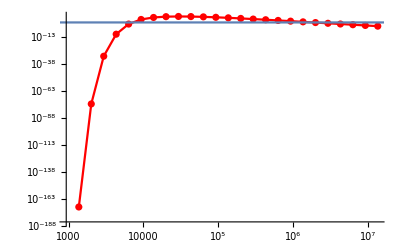

```mathematica
Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]]
```

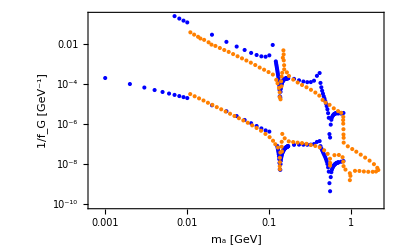

```mathematica
faprimemin=Import["./faprimemin.csv","Data"];
faprimemax=Import["./faprimemax.csv","Data"];
faexisting=Import["./existing.csv","Data"];
ListLogLogPlot[{falistmin,falistmax,faprimemin,faprimemax(*,faexisting*)},PlotStyle-> {Blue,Blue,Orange,Orange,Gray},Frame->True(*,Joined->True*),(*Mesh->Full,*)FrameLabel->{"m_a [GeV]","1/f_G [GeV^-1]"},ImageSize->400]
```

## Combining with GG-fusion

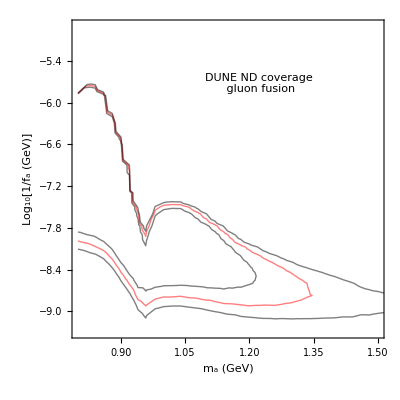

```mathematica
simulationresults=Import[NotebookDirectory[]<>"simulationresult.m"];
ListContourPlot[Flatten[Table[{#[[1]],Log[10,1/(4Pi^2#[[2]]*10^6)],Log[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1],Contours->{0,Log[3],Log[10]},PlotRange->{{0.8,1.5},Automatic},ContourStyle->{Thick,Red},ContourShading->{None},InterpolationOrder->All,FrameLabel->{"m_a (GeV)","Log_10[1/f_a (GeV)]"},BaseStyle->16,ImageSize->400,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.6,0.8}]]]
```

```mathematica
simulationresults
```

{{{0.8,0.0001,0.,0.,10,3.26543,0.172136,1.93533,0.106721,2.02567,0.113401},{0.8,0.0002,0.,0.,10,3.21581,0.233186,1.93172,0.118945,2.02175,0.133286},{0.8,0.0005,0.,0.,10,3.05814,0.22219,1.94363,0.118533,2.03656,0.132701},{0.8,0.001,0.,0.,10,3.06301,0.301535,1.94826,0.16258,2.03368,0.179525},{0.8,0.002,2.83478×10^-89,8.31514×10^-90,10,3.17196,0.221809,1.94924,0.115288,2.03589,0.127708},{0.8,0.005,-1.42505×10^-12,1.45699×10^-13,10,3.18297,0.252255,1.93293,0.138659,2.0253,0.148379},{0.8,0.008,-0.0061602,0.000344238,10,3.09788,0.343425,1.94053,0.180848,2.028,0.197642},{0.8,0.01,-1.62298,0.0871786,10,3.04707,0.231127,1.95722,0.123334,2.03211,0.134957},{0.8,0.02,1165.15,183.9,10,3.06259,0.228633,1.94851,0.116747,2.02996,0.131205},{0.8,0.05,75720.8,4481.95,10,3.08497,0.181867,1.95599,0.10095,2.03503,0.111055},{0.8,0.08,72339.8,4898.33,10,3.23871,0.351965,1.93403,0.179449,2.03288,0.208006},{0.8,0.1,56166.1,3213.29,10,3.00198,0.208422,1.9505,0.124898,2.03896,0.13214},{0.8,0.2,14249.8,1447.35,10,3.00687,0.229924,1.95967,0.12665,2.02765,0.144121},{0.8,0.5,752.049,83.6731,10,3.06664,0.197654,1.94908,0.114769,2.02813,0.12315},{0.8,0.8,128.518,17.9826,10,3.0723,0.274219,1.94687,0.157867,2.03155,0.169278},{0.8,1,53.0669,8.31182,10,3.10468,0.245161,1.94148,0.125214,2.02063,0.14465},{0.8,1.5,10.8766,1.72673,10,3.11446,0.310889,1.93711,0.157309,2.0215,0.176756},{0.8,2,3.7493,0.533064,10,3.25977,0.214242,1.92647,0.104922,2.01843,0.127941},{0.8,3,0.664137,0.0816298,10,3.02803,0.268353,1.95229,0.156518,2.02959,0.161853},{0.8,4,0.235613,0.0545501,10,3.2373,0.4801,1.94225,0.23297,2.02975,0.267668},{0.8,5,0.0892006,0.0139483,10,3.04528,0.300661,1.95111,0.148651,2.03936,0.172984},{0.8,6,0.0460667,0.00529125,10,3.16205,0.285931,1.94247,0.140255,2.02755,0.154218},{0.8,7,0.0250366,0.00224762,10,3.21698,0.208191,1.94386,0.0915099,2.02513,0.0997521},{0.8,8,0.0136539,0.00190315,10,3.10011,0.27206,1.94902,0.156201,2.03207,0.167318},{0.8,9,0.00928019,0.00163933,10,3.20027,0.3391,1.93618,0.177025,2.02624,0.198696},{0.8,10,0.00612465,0.000730117,10,3.21699,0.223599,1.93647,0.113291,2.02707,0.120728},{0.8,15,0.00111374,0.000108925,10,3.04401,0.146014,1.95216,0.0888687,2.03857,0.105763},{0.8,20,0.000351319,0.0000466974,10,3.07806,0.193391,1.95915,0.115916,2.03146,0.121683},{0.8,25,0.00014255,0.000018024,10,3.09432,0.230211,1.94128,0.127676,2.02664,0.137979},{0.8,30,0.0000724295,0.0000146126,10,3.11016,0.343069,1.94794,0.177803,2.03197,0.200396},{0.8,35,0.0000389228,4.36082×10^-6,10,3.23193,0.220726,1.93687,0.109298,2.01841,0.118749},{0.8,40,0.0000240845,3.34179×10^-6,10,3.21649,0.263721,1.93609,0.131944,2.02475,0.149315},{0.8,50,8.54885×10^-6,2.57666×10^-6,10,3.06285,0.411109,1.95001,0.230299,2.0374,0.257205}},{{0.82,0.0001,0.,0.,10,3.49327,0.318155,1.924,0.156147,2.00849,0.169799},{0.82,0.0002,0.,0.,10,3.48857,0.261425,1.92052,0.128726,2.00989,0.142526},{0.82,0.0005,0.,0.,10,3.77374,0.329166,1.89718,0.148787,1.98688,0.161283},{0.82,0.001,0.,0.,10,3.47315,0.3236,1.91684,0.136163,2.00339,0.155809},{0.82,0.002,2.90474×10^-103,7.60046×10^-104,10,3.4969,0.20211,1.91538,0.0979409,1.99785,0.10616},{0.82,0.005,-3.45442×10^-15,3.92129×10^-16,10,3.54816,0.431855,1.91987,0.213651,2.00679,0.230709},{0.82,0.008,-0.000235514,0.0000105617,10,3.52486,0.248671,1.91511,0.115324,2.00731,0.127653},{0.82,0.01,-0.0657712,0.00559602,10,3.39929,0.337159,1.93269,0.160591,2.01594,0.18498},{0.82,0.02,2479.64,89.7773,10,3.3756,0.21834,1.92588,0.104506,2.01133,0.110195},{0.82,0.05,74725.9,2883.04,10,3.53746,0.356442,1.91138,0.167584,1.99802,0.184419},{0.82,0.08,73335.5,4206.78,10,3.41418,0.0960108,1.92502,0.0377177,2.01037,0.0469285},{0.82,0.1,61286.4,4471.95,10,3.4919,0.395647,1.92516,0.185714,2.00744,0.207947},{0.82,0.2,17490.9,1661.03,10,3.58784,0.298162,1.9064,0.120131,2.00212,0.1437},{0.82,0.5,1036.33,146.235,10,3.55455,0.330592,1.91857,0.14654,2.01265,0.165659},{0.82,0.8,170.185,21.8879,10,3.56736,0.160771,1.91506,0.0725748,2.00142,0.0877221},{0.82,1,70.6295,10.1485,10,3.52494,0.294773,1.92055,0.126354,2.00288,0.151375},{0.82,1.5,15.2579,1.4763,10,3.62664,0.255304,1.90928,0.122014,1.99747,0.130868},{0.82,2,4.86373,0.581291,10,3.57588,0.171145,1.91366,0.0688044,1.9982,0.0832823},{0.82,3,0.915361,0.137955,10,3.43605,0.316998,1.93306,0.153839,2.012,0.169904},{0.82,4,0.299506,0.0256757,10,3.41401,0.209395,1.9307,0.105707,2.0224,0.115926},{0.82,5,0.114383,0.0213066,10,3.39585,0.315109,1.92427,0.167907,2.01302,0.181743},{0.82,6,0.0557861,0.00704266,10,3.52218,0.275261,1.91998,0.132356,1.99713,0.143693},{0.82,7,0.0332792,0.0029916,10,3.53961,0.1596,1.92283,0.0718103,2.01354,0.0728175},{0.82,8,0.018731,0.0028822,10,3.45289,0.295408,1.93193,0.136106,2.01868,0.153705},{0.82,9,0.0111442,0.00194972,10,3.44053,0.340256,1.92848,0.151197,2.01044,0.170182},{0.82,10,0.00786721,0.00121505,10,3.5168,0.209923,1.90741,0.0969259,2.00005,0.110865},{0.82,15,0.00161759,0.000194193,10,3.65118,0.284282,1.89809,0.12171,1.99258,0.133854},{0.82,20,0.000510097,0.000082107,10,3.61978,0.315621,1.90667,0.130816,1.99987,0.153026},{0.82,25,0.000182246,0.0000228457,10,3.45589,0.405762,1.92435,0.190967,1.99994,0.20681},{0.82,30,0.0000954579,0.000012993,10,3.47461,0.275578,1.92496,0.128695,2.01041,0.144926},{0.82,35,0.000053083,5.62762×10^-6,10,3.5616,0.303965,1.91539,0.135025,2.00212,0.145868},{0.82,40,0.0000300591,3.82469×10^-6,10,3.50528,0.207496,1.91077,0.0819744,2.00299,0.100115},{0.82,50,0.0000111007,1.73949×10^-6,10,3.28071,0.252878,1.93867,0.116065,2.01788,0.136866}},{{0.84,0.0001,0.,0.,10,3.92056,0.292821,1.89241,0.116514,1.98276,0.129986},{0.84,0.0002,0.,0.,10,3.84077,0.198209,1.89842,0.083779,1.98203,0.0928084},{0.84,0.0005,0.,0.,10,3.83506,0.213721,1.89578,0.0960181,1.98638,0.105802},{0.84,0.001,0.,0.,10,3.83827,0.170078,1.89538,0.0733776,1.97521,0.084203},{0.84,0.002,1.11912×10^-142,2.20296×10^-143,10,3.87021,0.374269,1.88576,0.149585,1.98327,0.168965},{0.84,0.005,-2.16661×10^-22,4.5756×10^-23,10,3.70158,0.448797,1.90123,0.191478,1.99266,0.216883},{0.84,0.008,-4.91569×10^-8,8.80668×10^-9,10,3.95593,0.372897,1.87961,0.154356,1.96685,0.171151},{0.84,0.01,0.000591544,0.0000561958,10,3.92701,0.319489,1.89428,0.134969,1.98163,0.14733},{0.84,0.02,863.368,41.4372,10,3.76084,0.291734,1.90411,0.129602,1.99073,0.145181},{0.84,0.05,50929.,2890.14,10,3.90109,0.200274,1.8978,0.0846375,1.98813,0.0964954},{0.84,0.08,63690.9,3473.05,10,3.74919,0.225184,1.90419,0.105818,1.99379,0.121229},{0.84,0.1,57469.4,2551.02,10,3.93034,0.304348,1.89715,0.116945,1.98798,0.142129},{0.84,0.2,18191.8,1927.97,10,3.68463,0.339319,1.90009,0.138842,1.98288,0.158295},{0.84,0.5,1328.75,169.577,10,3.75958,0.283789,1.90309,0.118872,1.99555,0.136693},{0.84,0.8,254.768,42.7071,10,3.87505,0.449991,1.89567,0.192577,1.98851,0.21485},{0.84,1,96.5783,14.6543,10,3.66908,0.294522,1.90839,0.132949,1.98688,0.149262},{0.84,1.5,20.552,3.44323,10,3.71293,0.312103,1.90189,0.135166,1.98292,0.153792},{0.84,2,6.8875,0.531678,10,3.77281,0.233348,1.90227,0.102702,1.98668,0.109002},{0.84,3,1.43367,0.143147,10,3.77471,0.125658,1.90109,0.0667728,1.99046,0.0754327},{0.84,4,0.460323,0.0642545,10,3.93202,0.255498,1.8925,0.100454,1.98107,0.114461},{0.84,5,0.199341,0.0251154,10,4.03909,0.200038,1.88575,0.0724583,1.98052,0.0832433},{0.84,6,0.0845193,0.0123912,10,3.64219,0.308618,1.91606,0.147733,2.00039,0.16013},{0.84,7,0.0461822,0.0104667,10,3.62305,0.293725,1.90937,0.131691,1.99756,0.154309},{0.84,8,0.0290678,0.00380294,10,3.96592,0.293888,1.89401,0.11773,1.98231,0.133504},{0.84,9,0.0165791,0.00260125,10,3.79503,0.387262,1.89062,0.162095,1.97358,0.183699},{0.84,10,0.0112211,0.000804487,10,3.88121,0.162905,1.89066,0.0646387,1.97271,0.0731859},{0.84,15,0.00212662,0.000178658,10,3.77925,0.165787,1.90642,0.0786126,1.98373,0.0809707},{0.84,20,0.000705313,0.0000969704,10,3.79572,0.355361,1.89394,0.150866,1.98104,0.169971},{0.84,25,0.000292456,0.0000606534,10,3.72619,0.402992,1.90193,0.17406,1.99386,0.200704},{0.84,30,0.000146821,0.0000242859,10,3.84298,0.314271,1.89587,0.138924,1.99393,0.157365},{0.84,35,0.0000740872,8.93848×10^-6,10,3.76253,0.208342,1.90383,0.0886937,1.98712,0.102886},{0.84,40,0.0000458487,5.14541×10^-6,10,3.83181,0.228203,1.90423,0.0949698,1.99124,0.102603},{0.84,50,0.0000195804,3.59977×10^-6,10,4.02143,0.348342,1.87634,0.13796,1.97225,0.160986}},{{0.86,0.0001,0.,0.,10,4.14517,0.305513,1.87514,0.113585,1.96802,0.127582},{0.86,0.0002,0.,0.,10,4.13333,0.216243,1.87995,0.0826094,1.96644,0.0953045},{0.86,0.0005,0.,0.,10,4.17771,0.282325,1.85873,0.115857,1.95497,0.125832},{0.86,0.001,0.,0.,10,4.10644,0.319046,1.87867,0.122399,1.96365,0.141135},{0.86,0.002,-2.21115×10^-256,0.,10,3.94079,0.487675,1.88498,0.198035,1.96671,0.222908},{0.86,0.005,-6.21159×10^-42,9.44397×10^-42,10,4.1414,0.294105,1.86318,0.109614,1.96025,0.132522},{0.86,0.008,2.5398×10^-15,2.07243×10^-16,10,4.11232,0.364722,1.87496,0.138863,1.96426,0.158132},{0.86,0.01,5.06297×10^-9,2.74259×10^-10,10,4.14864,0.218976,1.87968,0.0845402,1.98052,0.0910361},{0.86,0.02,20.3933,1.214,10,4.14712,0.315082,1.85749,0.111842,1.94798,0.127589},{0.86,0.05,17982.,303.772,10,4.22092,0.264322,1.87385,0.090578,1.96797,0.10647},{0.86,0.08,38912.9,2470.91,10,4.20656,0.419136,1.86914,0.150592,1.95494,0.16796},{0.86,0.1,41110.8,2266.25,10,4.03185,0.214204,1.88777,0.0769278,1.96657,0.0857035},{0.86,0.2,20795.4,1450.48,10,4.31848,0.251383,1.85999,0.10403,1.95721,0.114301},{0.86,0.5,2071.39,242.436,10,4.16033,0.300296,1.87123,0.119948,1.95905,0.134635},{0.86,0.8,418.281,61.7438,10,4.22954,0.368409,1.8635,0.129833,1.94792,0.148339},{0.86,1,190.526,28.0605,10,4.18487,0.384432,1.87837,0.134035,1.97136,0.155549},{0.86,1.5,40.674,4.58363,10,4.11358,0.322685,1.86828,0.115869,1.96288,0.130713},{0.86,2,12.3459,1.96423,10,4.14562,0.371308,1.87554,0.126529,1.95785,0.149367},{0.86,3,2.59952,0.294689,10,4.10993,0.276043,1.8836,0.102881,1.9713,0.116863},{0.86,4,0.778516,0.136922,10,4.02484,0.297619,1.88908,0.109609,1.96954,0.125803},{0.86,5,0.351097,0.0377284,10,4.1253,0.236182,1.87002,0.0882217,1.95781,0.101872},{0.86,6,0.172989,0.0249662,10,4.28484,0.301233,1.86691,0.106352,1.9572,0.123436},{0.86,7,0.0887794,0.00995164,10,4.05067,0.335803,1.87687,0.132815,1.96519,0.146438},{0.86,8,0.0526373,0.00661838,10,4.23656,0.305137,1.86127,0.111504,1.95398,0.1289},{0.86,9,0.0328969,0.00392025,10,4.09766,0.314757,1.87758,0.120224,1.96708,0.133181},{0.86,10,0.0219995,0.00272719,10,4.219,0.221139,1.87064,0.0760361,1.96079,0.0857682},{0.86,15,0.00407697,0.00057796,10,4.11714,0.288641,1.88156,0.109733,1.96317,0.127487},{0.86,20,0.00129235,0.000165276,10,4.05226,0.273066,1.8758,0.108457,1.96109,0.127801},{0.86,25,0.000584838,0.000106304,10,4.18896,0.448059,1.86614,0.15933,1.96393,0.188229},{0.86,30,0.000266942,0.0000349064,10,4.10776,0.327986,1.88425,0.12655,1.9759,0.141703},{0.86,35,0.000148103,0.0000210848,10,4.25531,0.313601,1.86225,0.107606,1.95564,0.125063},{0.86,40,0.0000926475,9.23869×10^-6,10,4.4452,0.190774,1.86208,0.071582,1.95537,0.0822845},{0.86,50,0.0000353933,6.30286×10^-6,10,4.16867,0.441157,1.8684,0.167935,1.9604,0.1922}},{{0.88,0.0001,0.,0.,10,4.57067,0.311987,1.8492,0.106579,1.94465,0.121693},{0.88,0.0002,0.,0.,10,4.50782,0.351674,1.84425,0.111403,1.93365,0.131753},{0.88,0.0005,0.,0.,10,4.63076,0.229497,1.83776,0.0712315,1.94255,0.0849338},{0.88,0.001,0.,0.,10,4.47294,0.412193,1.84577,0.134611,1.93729,0.158822},{0.88,0.002,0.,0.,10,4.47282,0.194385,1.84054,0.0760539,1.93096,0.0808926},{0.88,0.005,-1.56854×10^-124,3.98076×10^-125,10,4.44591,0.343408,1.84519,0.121321,1.94127,0.136611},{0.88,0.008,-5.01817×10^-49,1.89363×10^-49,10,4.49622,0.21947,1.85118,0.0736991,1.94232,0.0829988},{0.88,0.01,2.16347×10^-31,5.63364×10^-32,10,4.33034,0.226764,1.86093,0.0878709,1.94677,0.0965511},{0.88,0.02,2.20533×10^-6,1.35108×10^-7,10,4.37365,0.251765,1.85481,0.0838076,1.9462,0.0986549},{0.88,0.05,535.379,20.0274,10,4.58619,0.353387,1.85197,0.123592,1.94205,0.143643},{0.88,0.08,5447.13,209.901,10,4.40708,0.317994,1.85244,0.101085,1.94963,0.125211},{0.88,0.1,9262.27,373.828,10,4.44672,0.287165,1.85522,0.103023,1.94705,0.118096},{0.88,0.2,14420.3,604.527,10,4.71389,0.342688,1.82381,0.107286,1.9239,0.130639},{0.88,0.5,3405.91,274.191,10,4.49142,0.287329,1.84235,0.101424,1.9357,0.106771},{0.88,0.8,925.35,101.104,10,4.4159,0.359416,1.85741,0.116811,1.94493,0.133136},{0.88,1,443.479,55.7533,10,4.42004,0.374932,1.83958,0.127476,1.93523,0.144078},{0.88,1.5,103.791,10.7225,10,4.24008,0.22558,1.86941,0.0901204,1.95608,0.0995086},{0.88,2,39.1124,5.52975,10,4.55477,0.493718,1.83853,0.160896,1.9313,0.18067},{0.88,3,8.30351,1.1872,10,4.46546,0.353712,1.84902,0.13035,1.94308,0.147454},{0.88,4,2.62269,0.23993,10,4.36003,0.276557,1.85672,0.0894257,1.94892,0.105299},{0.88,5,1.13644,0.156758,10,4.54985,0.271621,1.84014,0.0862331,1.9353,0.103779},{0.88,6,0.476743,0.0620418,10,4.16274,0.262302,1.87756,0.0936986,1.96035,0.110537},{0.88,7,0.272306,0.0627417,10,4.36483,0.524116,1.86175,0.18689,1.94636,0.214891},{0.88,8,0.170569,0.0213902,10,4.51256,0.413558,1.85203,0.145073,1.94511,0.162097},{0.88,9,0.100454,0.0157971,10,4.44117,0.412093,1.86177,0.147008,1.94904,0.167377},{0.88,10,0.0725829,0.00947696,10,4.55828,0.310821,1.83634,0.0948597,1.93432,0.113913},{0.88,15,0.0133564,0.0019139,10,4.46615,0.418668,1.8519,0.147756,1.93723,0.164421},{0.88,20,0.00426349,0.000492322,10,4.5148,0.28764,1.84548,0.0906419,1.93273,0.102372},{0.88,25,0.00177574,0.000346535,10,4.40091,0.513828,1.8489,0.189467,1.94329,0.218569},{0.88,30,0.000744962,0.000113253,10,4.23178,0.311419,1.86585,0.105332,1.94428,0.118441},{0.88,35,0.000472272,0.0000572254,10,4.55778,0.420872,1.85191,0.146353,1.9443,0.163519},{0.88,40,0.000238961,0.0000390079,10,4.20544,0.252306,1.86871,0.0981768,1.94638,0.114489},{0.88,50,0.000106922,0.0000173031,10,4.32367,0.41132,1.86216,0.15124,1.94809,0.169999}},{{0.9,0.0001,0.,0.,10,4.88419,0.413374,1.81605,0.129235,1.91475,0.1458},{0.9,0.0002,0.,0.,10,4.81886,0.186054,1.81783,0.0561425,1.91513,0.0694798},{0.9,0.0005,0.,0.,10,4.71148,0.334371,1.83778,0.101214,1.93381,0.119954},{0.9,0.001,0.,0.,10,4.75822,0.387656,1.82172,0.1151,1.9272,0.139365},{0.9,0.002,0.,0.,10,4.7846,0.300389,1.82367,0.0948117,1.91724,0.106807},{0.9,0.005,0.,0.,10,4.74232,0.365367,1.829,0.123977,1.9195,0.136843},{0.9,0.008,-4.02064×10^-280,0.,10,4.70526,0.333495,1.83427,0.106188,1.92206,0.124683},{0.9,0.01,-1.41452×10^-179,0.,10,4.79759,0.404513,1.82035,0.121667,1.91814,0.13966},{0.9,0.02,-6.65475×10^-46,4.13025×10^-46,10,4.69337,0.498905,1.83573,0.156571,1.93537,0.175802},{0.9,0.05,2.89555×10^-6,1.31624×10^-7,10,4.69614,0.376007,1.83542,0.122805,1.93003,0.14651},{0.9,0.08,0.960636,0.0394393,10,4.64336,0.357169,1.82978,0.108213,1.92266,0.124693},{0.9,0.1,20.6682,0.814542,10,4.81089,0.473496,1.82103,0.143578,1.91375,0.166488},{0.9,0.2,1202.83,27.4347,10,4.81936,0.404014,1.81169,0.121488,1.91112,0.138925},{0.9,0.5,2510.63,129.137,10,4.61166,0.419315,1.83408,0.147577,1.92176,0.164479},{0.9,0.8,1417.41,91.7325,10,4.72457,0.307957,1.8296,0.0964875,1.92316,0.115919},{0.9,1,886.668,65.4146,10,4.52724,0.242331,1.84818,0.0827417,1.93351,0.0913836},{0.9,1.5,335.278,19.6229,10,4.65834,0.133782,1.82941,0.0439287,1.91211,0.0520321},{0.9,2,149.707,18.3636,10,4.80685,0.462756,1.8264,0.13633,1.91523,0.15449},{0.9,3,38.2105,3.74236,10,4.73541,0.231561,1.82932,0.0805575,1.9204,0.0920551},{0.9,4,13.733,1.52588,10,4.6482,0.526118,1.83612,0.159448,1.93113,0.178599},{0.9,5,6.55897,0.742772,10,4.89529,0.346698,1.81865,0.11845,1.92286,0.133343},{0.9,6,3.0277,0.276738,10,4.77722,0.183859,1.82417,0.0602607,1.91833,0.0685563},{0.9,7,1.57326,0.21002,10,4.56855,0.29811,1.84572,0.0935651,1.93853,0.112244},{0.9,8,0.970011,0.0916017,10,4.75185,0.301572,1.82537,0.0947073,1.92259,0.101575},{0.9,9,0.616242,0.0862832,10,4.83416,0.417561,1.81026,0.127271,1.91116,0.152503},{0.9,10,0.371127,0.0450979,10,4.58744,0.313916,1.84755,0.105492,1.93206,0.118042},{0.9,15,0.0819864,0.0124717,10,4.8107,0.453924,1.82392,0.14223,1.92241,0.167589},{0.9,20,0.0258775,0.00321291,10,4.81301,0.36456,1.81578,0.109019,1.909,0.119474},{0.9,25,0.0105875,0.000846374,10,4.75363,0.306805,1.82418,0.10087,1.91862,0.110918},{0.9,30,0.00479888,0.00088211,10,4.56172,0.300863,1.83954,0.0961291,1.92884,0.119652},{0.9,35,0.0027157,0.000224425,10,4.8602,0.159366,1.82066,0.0506883,1.90781,0.0554119},{0.9,40,0.00169127,0.000186057,10,4.89051,0.219447,1.81866,0.073342,1.91401,0.076588},{0.9,50,0.000647108,0.0000590548,10,4.67898,0.240716,1.83352,0.0843476,1.92672,0.087243}},{{0.92,0.0001,0.,0.,10,5.13469,0.340954,1.80433,0.100675,1.90417,0.115992},{0.92,0.0002,0.,0.,10,4.89314,0.335048,1.81369,0.0954075,1.91171,0.113967},{0.92,0.0005,0.,0.,10,5.04363,0.371605,1.81085,0.101689,1.90419,0.122748},{0.92,0.001,0.,0.,10,4.89322,0.351625,1.81713,0.103021,1.90887,0.121516},{0.92,0.002,0.,0.,10,5.00413,0.260226,1.81067,0.0735712,1.90664,0.0866631},{0.92,0.005,0.,0.,10,5.02338,0.430501,1.80285,0.130397,1.90258,0.147329},{0.92,0.008,0.,0.,10,4.89258,0.396766,1.82063,0.114154,1.91529,0.1356},{0.92,0.01,0.,0.,10,4.86602,0.321837,1.82017,0.104446,1.9079,0.117001},{0.92,0.02,-1.90534×10^-242,0.,10,4.85466,0.554093,1.81016,0.163251,1.89763,0.190343},{0.92,0.05,2.75803×10^-40,7.61861×10^-41,10,5.06688,0.362011,1.80163,0.10602,1.89779,0.122871},{0.92,0.08,1.49756×10^-15,1.10952×10^-16,10,5.07532,0.406769,1.79451,0.118329,1.89061,0.13093},{0.92,0.1,1.0159×10^-9,4.30424×10^-11,10,4.9518,0.287699,1.81207,0.0919174,1.90563,0.109257},{0.92,0.2,0.656453,0.049377,10,5.04795,0.304893,1.80131,0.0779879,1.89537,0.08827},{0.92,0.5,288.539,8.76022,10,5.0482,0.444107,1.80572,0.128576,1.90406,0.148168},{0.92,0.8,533.93,24.5839,10,5.07129,0.369678,1.80073,0.103922,1.89291,0.124775},{0.92,1,541.387,29.1748,10,4.96685,0.423077,1.80861,0.122972,1.89561,0.139294},{0.92,1.5,375.937,27.403,10,5.01798,0.483824,1.79139,0.135044,1.89144,0.162791},{0.92,2,234.354,16.1213,10,4.90442,0.360523,1.81324,0.103559,1.9114,0.124543},{0.92,3,101.983,8.99254,10,5.07692,0.305854,1.80231,0.0847677,1.89662,0.0956557},{0.92,4,45.6136,6.6478,10,4.95737,0.4594,1.81819,0.13905,1.91271,0.160938},{0.92,5,23.4182,3.06817,10,5.04244,0.421492,1.80325,0.1323,1.91017,0.143933},{0.92,6,12.7399,1.90813,10,5.03505,0.505139,1.80063,0.153137,1.90255,0.175325},{0.92,7,7.50094,0.83,10,5.05335,0.389102,1.80224,0.117048,1.90546,0.131069},{0.92,8,4.14505,0.622821,10,4.71158,0.403159,1.82331,0.132619,1.91073,0.152527},{0.92,9,3.10069,0.393412,10,5.18386,0.347727,1.7886,0.0904062,1.89248,0.109253},{0.92,10,1.8908,0.211859,10,4.91197,0.324418,1.81599,0.101235,1.90555,0.116082},{0.92,15,0.432535,0.0376246,10,4.94257,0.234147,1.80343,0.0689194,1.90407,0.07881},{0.92,20,0.130885,0.0286636,10,4.8958,0.381725,1.80858,0.12059,1.90115,0.149349},{0.92,25,0.0559027,0.00991211,10,4.89474,0.334722,1.8085,0.109296,1.9045,0.132581},{0.92,30,0.0281934,0.00202398,10,5.07321,0.142438,1.80327,0.0426382,1.89918,0.0427872},{0.92,35,0.0154263,0.00229704,10,5.09534,0.37587,1.79878,0.115442,1.89835,0.128894},{0.92,40,0.00856922,0.00132594,10,4.84259,0.465494,1.81598,0.126621,1.9081,0.144199},{0.92,50,0.00347533,0.000345979,10,4.89539,0.248594,1.80716,0.0741659,1.89771,0.0881153}},{{0.94,0.0001,0.,0.,10,5.13362,0.377147,1.793,0.109523,1.89015,0.12869},{0.94,0.0002,0.,0.,10,5.40047,0.27462,1.77102,0.0724732,1.87507,0.0806349},{0.94,0.0005,0.,0.,10,5.30065,0.498381,1.77527,0.131307,1.87591,0.157429},{0.94,0.001,0.,0.,10,5.35452,0.366426,1.77609,0.0992079,1.87556,0.113727},{0.94,0.002,0.,0.,10,5.22387,0.420662,1.78468,0.115524,1.87952,0.133047},{0.94,0.005,0.,0.,10,5.29776,0.329684,1.78127,0.0883769,1.88446,0.103344},{0.94,0.008,0.,0.,10,5.02621,0.413631,1.79282,0.124094,1.87922,0.138691},{0.94,0.01,0.,0.,10,5.20441,0.316613,1.79355,0.0774447,1.88847,0.099808},{0.94,0.02,0.,0.,10,5.26396,0.402093,1.77112,0.104351,1.87458,0.126044},{0.94,0.05,0.,0.,10,5.21143,0.281927,1.77768,0.0785584,1.87049,0.0875438},{0.94,0.08,-4.613×10^-182,0.,10,5.38488,0.349276,1.77605,0.0918207,1.87858,0.106062},{0.94,0.1,-1.80433×10^-117,7.08769×10^-118,10,4.93692,0.299795,1.80565,0.0987866,1.8954,0.108779},{0.94,0.2,8.64685×10^-31,9.2717×10^-32,10,5.23369,0.365072,1.78902,0.096779,1.8791,0.112859},{0.94,0.5,0.0000834394,2.88917×10^-6,10,5.03307,0.401512,1.80087,0.121111,1.89387,0.139374},{0.94,0.8,0.399278,0.0232745,10,5.14877,0.320731,1.78643,0.0875667,1.88749,0.108283},{0.94,1,2.82474,0.159415,10,5.11048,0.387715,1.7912,0.10219,1.89192,0.121159},{0.94,1.5,18.368,0.232659,10,5.33562,0.242999,1.77746,0.0614298,1.86992,0.0700724},{0.94,2,34.2806,1.25104,10,5.15264,0.31768,1.79014,0.0843238,1.8864,0.101538},{0.94,3,47.1146,1.86242,10,5.2373,0.373161,1.79114,0.103224,1.8876,0.117719},{0.94,4,42.8525,2.76226,10,4.97807,0.341386,1.79653,0.0966283,1.88577,0.112786},{0.94,5,34.784,1.91892,10,5.10765,0.397717,1.79032,0.120326,1.8883,0.131451},{0.94,6,26.9358,2.05666,10,5.10609,0.413705,1.79676,0.116291,1.88733,0.133888},{0.94,7,20.4357,0.737881,10,5.13457,0.204048,1.79645,0.054621,1.88301,0.0645361},{0.94,8,15.6021,1.18341,10,5.12321,0.274219,1.79069,0.08292,1.88525,0.0925761},{0.94,9,12.3854,0.822213,10,5.27341,0.278363,1.78355,0.0857763,1.88197,0.0981127},{0.94,10,9.38946,0.853982,10,5.18911,0.430025,1.78338,0.113407,1.88155,0.131265},{0.94,15,2.97389,0.332197,10,5.19335,0.325981,1.7842,0.0895809,1.88128,0.113616},{0.94,20,1.10627,0.101523,10,4.96273,0.318775,1.79638,0.0922411,1.88748,0.101329},{0.94,25,0.532987,0.0656736,10,5.09643,0.35511,1.79088,0.101111,1.88568,0.120919},{0.94,30,0.27394,0.0320408,10,5.14286,0.316896,1.78995,0.0830812,1.88268,0.103838},{0.94,35,0.161571,0.0174178,10,5.23847,0.365358,1.78305,0.0937665,1.88112,0.106574},{0.94,40,0.0982342,0.00614179,10,5.2761,0.175733,1.7828,0.0507388,1.88072,0.0579339},{0.94,50,0.0382512,0.00434651,10,5.04448,0.288106,1.79187,0.0793604,1.88051,0.095327}},{{0.958,0.0001,0.,0.,10,5.41882,0.433919,1.75438,0.110874,1.8638,0.130435},{0.958,0.0002,0.,0.,10,5.38036,0.291994,1.77032,0.073498,1.86481,0.0888934},{0.958,0.0005,0.,0.,10,5.11431,0.360041,1.77949,0.106759,1.87064,0.125591},{0.958,0.001,0.,0.,10,5.5777,0.361577,1.75432,0.0898769,1.8524,0.107885},{0.958,0.002,0.,0.,10,5.216,0.347325,1.77925,0.0978094,1.87549,0.119617},{0.958,0.005,0.,0.,10,5.41894,0.243805,1.76371,0.0679278,1.86787,0.0761339},{0.958,0.008,0.,0.,10,5.15301,0.294043,1.77911,0.0820899,1.87428,0.0957449},{0.958,0.01,0.,0.,10,5.29808,0.474646,1.76635,0.132763,1.85522,0.148122},{0.958,0.02,0.,0.,10,5.49064,0.279915,1.75791,0.0835659,1.85576,0.0906222},{0.958,0.05,0.,0.,10,5.34513,0.291438,1.76942,0.073652,1.85997,0.0919609},{0.958,0.08,0.,0.,10,5.43742,0.257798,1.76364,0.071113,1.8599,0.0800969},{0.958,0.1,0.,0.,10,5.34409,0.401533,1.76661,0.109937,1.86546,0.12546},{0.958,0.2,-1.6496×10^-99,3.45857×10^-100,10,5.2313,0.336925,1.77767,0.0896307,1.87384,0.104606},{0.958,0.5,2.38374×10^-17,1.81209×10^-18,10,5.31535,0.363398,1.77164,0.0957228,1.86452,0.109464},{0.958,0.8,4.63849×10^-7,2.21242×10^-8,10,5.16306,0.17223,1.77578,0.0566643,1.87295,0.0649472},{0.958,1,0.000241501,6.32145×10^-6,10,5.34493,0.402543,1.77603,0.1141,1.87157,0.129066},{0.958,1.5,0.166239,0.00894594,10,5.51376,0.274114,1.74916,0.0739998,1.8556,0.0822293},{0.958,2,1.55193,0.0729641,10,5.37137,0.232323,1.77328,0.0679049,1.86521,0.0762248},{0.958,3,7.43279,0.209771,10,5.34575,0.335167,1.7646,0.0888745,1.85643,0.105363},{0.958,4,12.1521,0.479303,10,5.54709,0.399812,1.76447,0.105481,1.85509,0.119032},{0.958,5,14.4186,0.932747,10,5.39292,0.646237,1.76292,0.165989,1.86309,0.200715},{0.958,6,14.68,0.939186,10,5.21519,0.381143,1.77118,0.0944409,1.86788,0.116853},{0.958,7,14.0631,0.842323,10,5.48978,0.321161,1.75956,0.076799,1.8569,0.0886064},{0.958,8,12.7572,0.927277,10,5.47841,0.301358,1.75356,0.0828161,1.86261,0.10446},{0.958,9,10.711,0.549258,10,5.16281,0.219789,1.77876,0.0631309,1.87473,0.0790064},{0.958,10,9.82881,0.485141,10,5.4122,0.348869,1.75938,0.0906586,1.86122,0.106689},{0.958,15,4.43263,0.24992,10,5.14611,0.278249,1.7918,0.0730061,1.87963,0.0838129},{0.958,20,2.17152,0.203181,10,5.16676,0.324508,1.78183,0.100718,1.86941,0.116193},{0.958,25,1.21872,0.113232,10,5.36052,0.399701,1.76738,0.104166,1.865,0.119383},{0.958,30,0.654979,0.0815285,10,5.16751,0.377522,1.77617,0.101292,1.86724,0.121255},{0.958,35,0.435282,0.0335059,10,5.52047,0.285959,1.75355,0.0669488,1.85837,0.0837968},{0.958,40,0.254629,0.0199046,10,5.26249,0.284174,1.77139,0.0756434,1.86591,0.0860618},{0.958,50,0.119317,0.0127741,10,5.25152,0.511008,1.77589,0.142867,1.87566,0.158142}},{{0.96,0.0001,0.,0.,10,5.32863,0.328523,1.77448,0.0968869,1.87365,0.110862},{0.96,0.0002,0.,0.,10,5.43869,0.318981,1.7583,0.0868065,1.86248,0.0983297},{0.96,0.0005,0.,0.,10,5.23603,0.294025,1.77401,0.0852098,1.86116,0.0913945},{0.96,0.001,0.,0.,10,5.41262,0.288038,1.76567,0.0799342,1.87259,0.0886701},{0.96,0.002,0.,0.,10,5.28267,0.333367,1.77023,0.0854661,1.86999,0.104102},{0.96,0.005,0.,0.,10,5.60162,0.283493,1.75225,0.0698832,1.85912,0.0821328},{0.96,0.008,0.,0.,10,5.38771,0.253838,1.76094,0.066423,1.86346,0.0676634},{0.96,0.01,0.,0.,10,5.5571,0.251517,1.75881,0.0687192,1.85373,0.0775318},{0.96,0.02,0.,0.,10,5.43657,0.41222,1.75767,0.109966,1.86246,0.130868},{0.96,0.05,0.,0.,10,5.36897,0.35059,1.75887,0.0904818,1.8596,0.1043},{0.96,0.08,0.,0.,10,5.45335,0.525614,1.76727,0.141825,1.86449,0.16706},{0.96,0.1,-1.30739×10^-305,0.,10,5.48669,0.354846,1.75308,0.0954185,1.85813,0.107077},{0.96,0.2,-3.24752×10^-79,3.43056×10^-79,10,5.29535,0.362605,1.76851,0.0968328,1.86601,0.115539},{0.96,0.5,9.27401×10^-14,3.90124×10^-15,10,5.23456,0.371242,1.77045,0.0955471,1.86204,0.114215},{0.96,0.8,0.0000231357,8.42946×10^-7,10,5.40516,0.332942,1.7731,0.0898623,1.86929,0.101556},{0.96,1,0.00375397,0.000154804,10,5.43696,0.40065,1.75899,0.103483,1.85687,0.122202},{0.96,1.5,0.641011,0.0284584,10,5.36935,0.285382,1.77835,0.0796782,1.87237,0.0895785},{0.96,2,3.61797,0.130513,10,5.4709,0.374039,1.75452,0.102608,1.8494,0.120911},{0.96,3,12.2927,0.58356,10,5.43701,0.460604,1.76145,0.120687,1.85996,0.135589},{0.96,4,17.1996,0.635082,10,5.61488,0.384622,1.75318,0.102297,1.86162,0.124839},{0.96,5,19.2974,0.617415,10,5.38937,0.242322,1.76883,0.0710847,1.85856,0.0751388},{0.96,6,17.3497,1.06227,10,5.21574,0.399268,1.7784,0.115763,1.87491,0.131234},{0.96,7,16.1258,1.0718,10,5.34551,0.42492,1.75882,0.121271,1.859,0.139306},{0.96,8,14.0974,1.14606,10,5.35697,0.44413,1.7654,0.123194,1.86096,0.140982},{0.96,9,11.8853,0.781308,10,5.34241,0.246264,1.76813,0.0762958,1.86462,0.0817359},{0.96,10,10.5133,0.68761,10,5.49253,0.273709,1.76037,0.0724259,1.85936,0.0834181},{0.96,15,4.34741,0.306179,10,5.30523,0.252713,1.77175,0.0756889,1.86812,0.0905833},{0.96,20,2.06115,0.172586,10,5.3153,0.377144,1.77056,0.0956443,1.86368,0.112898},{0.96,25,1.0572,0.0773958,10,5.31774,0.191825,1.76405,0.052566,1.86761,0.0633974},{0.96,30,0.567431,0.0589777,10,5.25383,0.314079,1.77055,0.0794136,1.8702,0.0989667},{0.96,35,0.343513,0.0366117,10,5.27767,0.356763,1.77535,0.103411,1.86791,0.116263},{0.96,40,0.210748,0.0236434,10,5.28331,0.306228,1.7645,0.0922899,1.86076,0.102827},{0.96,50,0.098538,0.00905956,10,5.39615,0.250308,1.76795,0.064401,1.86857,0.0777307}},{{0.98,0.0001,0.,0.,10,5.62982,0.420672,1.74171,0.105807,1.83993,0.122319},{0.98,0.0002,0.,0.,10,5.6308,0.32743,1.73869,0.0814021,1.84088,0.0983824},{0.98,0.0005,0.,0.,10,5.4568,0.49343,1.74525,0.119113,1.8441,0.144251},{0.98,0.001,0.,0.,10,5.47911,0.404363,1.74716,0.106873,1.84591,0.113147},{0.98,0.002,0.,0.,10,5.55515,0.512986,1.7407,0.129335,1.84152,0.153192},{0.98,0.005,0.,0.,10,5.55753,0.46985,1.74208,0.124943,1.83607,0.146327},{0.98,0.008,0.,0.,10,5.49746,0.28319,1.74868,0.0739593,1.84781,0.0801794},{0.98,0.01,0.,0.,10,5.6395,0.435064,1.73283,0.100342,1.84061,0.114083},{0.98,0.02,0.,0.,10,5.49912,0.341504,1.74687,0.0930125,1.84534,0.102432},{0.98,0.05,0.,0.,10,5.36685,0.334673,1.76008,0.0867937,1.85352,0.111346},{0.98,0.08,-1.89837×10^-166,0.,10,5.60469,0.390929,1.7452,0.0954063,1.84123,0.112359},{0.98,0.1,-6.61612×10^-108,7.41761×10^-108,10,5.13569,0.362549,1.7783,0.0988413,1.86897,0.112346},{0.98,0.2,6.67656×10^-28,6.52361×10^-29,10,5.42964,0.339725,1.75122,0.0919716,1.8454,0.103647},{0.98,0.5,0.000338018,0.0000167237,10,5.51292,0.321732,1.75056,0.0835082,1.84521,0.0955148},{0.98,0.8,0.789815,0.0428193,10,5.52457,0.370747,1.75117,0.0971623,1.84778,0.11508},{0.98,1,4.62955,0.138411,10,5.69618,0.398318,1.73356,0.0999783,1.82833,0.111461},{0.98,1.5,25.347,0.663147,10,5.6085,0.297634,1.74041,0.0751932,1.83975,0.0882235},{0.98,2,45.4605,2.08508,10,5.42417,0.33208,1.74672,0.0890243,1.8447,0.103815},{0.98,3,58.1071,3.0088,10,5.67387,0.430141,1.73658,0.102413,1.83544,0.120627},{0.98,4,51.0074,3.77245,10,5.55065,0.339293,1.74041,0.0758444,1.836,0.0909511},{0.98,5,39.1012,2.18957,10,5.65724,0.290617,1.75014,0.07281,1.85102,0.0855544},{0.98,6,29.1557,1.93576,10,5.40506,0.381174,1.75842,0.105318,1.85015,0.122668},{0.98,7,21.6793,2.42547,10,5.4598,0.503373,1.7587,0.127009,1.85616,0.150711},{0.98,8,17.2672,0.73378,10,5.74256,0.175376,1.72557,0.0413268,1.82902,0.0566467},{0.98,9,12.5953,1.27558,10,5.54545,0.401641,1.75151,0.1042,1.85161,0.116836},{0.98,10,10.0825,0.792597,10,5.76425,0.330175,1.73085,0.0869349,1.84057,0.102597},{0.98,15,2.88086,0.268657,10,5.53207,0.334147,1.73982,0.0829748,1.83526,0.0886167},{0.98,20,1.11424,0.119802,10,5.50186,0.315643,1.74199,0.0728571,1.84638,0.0923764},{0.98,25,0.52917,0.0460352,10,5.60394,0.211424,1.74685,0.061437,1.84776,0.0700062},{0.98,30,0.266913,0.030595,10,5.56234,0.378115,1.73361,0.100894,1.84026,0.111142},{0.98,35,0.152949,0.0236246,10,5.64516,0.541337,1.72827,0.133895,1.83493,0.157434},{0.98,40,0.0820673,0.0117469,10,5.47582,0.281967,1.74375,0.0749584,1.83551,0.0931349},{0.98,50,0.0360227,0.00567885,10,5.37707,0.525595,1.74931,0.126727,1.84707,0.152929}},{{1.,0.0001,0.,0.,10,5.74283,0.416476,1.71514,0.103336,1.81652,0.115326},{1.,0.0002,0.,0.,10,5.79758,0.295556,1.71627,0.0649862,1.81741,0.0821301},{1.,0.0005,0.,0.,10,5.46816,0.229878,1.74362,0.0685467,1.83798,0.0715814},{1.,0.001,0.,0.,10,5.56769,0.409284,1.72688,0.118035,1.83057,0.130148},{1.,0.002,0.,0.,10,5.5728,0.495463,1.72915,0.121677,1.82614,0.149502},{1.,0.005,0.,0.,10,5.56693,0.249561,1.7311,0.0671197,1.82366,0.0784759},{1.,0.008,0.,0.,10,5.63563,0.309553,1.73169,0.0843021,1.83772,0.0972734},{1.,0.01,0.,0.,10,5.4778,0.425869,1.73957,0.109749,1.83714,0.122217},{1.,0.02,0.,0.,10,5.62821,0.485902,1.72838,0.118658,1.83004,0.138528},{1.,0.05,-1.00762×10^-315,0.,10,5.78563,0.393333,1.72487,0.0915572,1.83105,0.10713},{1.,0.08,7.54656×10^-125,2.40087×10^-125,10,5.67249,0.322297,1.7238,0.0725316,1.83032,0.0883939},{1.,0.1,1.85523×10^-80,2.00349×10^-81,10,5.74371,0.50598,1.72733,0.131445,1.8331,0.151696},{1.,0.2,7.48785×10^-21,4.02915×10^-22,10,5.52027,0.252088,1.73761,0.0649225,1.83097,0.0765154},{1.,0.5,0.0114995,0.000635073,10,5.51457,0.161073,1.73892,0.0346331,1.83466,0.0463956},{1.,0.8,3.98847,0.17044,10,5.57929,0.368188,1.73596,0.100309,1.83351,0.106682},{1.,1,14.5227,0.531575,10,5.77544,0.449332,1.70742,0.104968,1.81061,0.116516},{1.,1.5,49.9637,1.03349,10,5.93692,0.451172,1.70338,0.10342,1.81065,0.1217},{1.,2,71.2633,4.44729,10,5.77039,0.267427,1.7258,0.0657563,1.82948,0.0791538},{1.,3,77.8602,3.46159,10,5.59903,0.229715,1.72181,0.0678648,1.81981,0.0746262},{1.,4,59.3933,3.70436,10,5.71505,0.434603,1.72722,0.106819,1.82767,0.120113},{1.,5,42.3169,2.14795,10,5.53043,0.372135,1.72747,0.085783,1.82794,0.109192},{1.,6,29.5429,2.06837,10,5.5081,0.364774,1.73138,0.0919155,1.82971,0.110401},{1.,7,22.1671,2.88494,10,5.70533,0.651299,1.72022,0.156636,1.81987,0.184838},{1.,8,15.0001,1.46084,10,5.41264,0.420408,1.74279,0.108952,1.83634,0.131432},{1.,9,11.517,1.42573,10,5.60857,0.474158,1.71915,0.114495,1.82354,0.141205},{1.,10,8.37197,0.895178,10,5.53688,0.434853,1.73696,0.114219,1.82917,0.130901},{1.,15,2.57097,0.237388,10,5.90985,0.326572,1.70769,0.0807222,1.81301,0.0933289},{1.,20,0.9323,0.0770147,10,5.84232,0.363998,1.71274,0.0886273,1.81733,0.101103},{1.,25,0.402645,0.0456288,10,5.68044,0.454909,1.72192,0.115845,1.82298,0.13339},{1.,30,0.185746,0.0183036,10,5.51982,0.397145,1.73394,0.102693,1.82623,0.111983},{1.,35,0.108921,0.0120504,10,5.60229,0.294643,1.73601,0.0764526,1.83876,0.0929824},{1.,40,0.0672103,0.00646411,10,5.56562,0.440262,1.72247,0.115089,1.83115,0.1322},{1.,50,0.0293004,0.00264452,10,5.78862,0.283202,1.7168,0.0704974,1.82324,0.083878}},{{1.02,0.0001,0.,0.,10,5.5163,0.509865,1.72865,0.120248,1.81745,0.143471},{1.02,0.0002,0.,0.,10,5.87298,0.439978,1.7008,0.102809,1.81886,0.133311},{1.02,0.0005,0.,0.,10,5.96669,0.529456,1.69934,0.121875,1.80533,0.137475},{1.02,0.001,0.,0.,10,5.77172,0.305728,1.70445,0.0644666,1.80243,0.0808135},{1.02,0.002,0.,0.,10,5.79309,0.278658,1.7043,0.063512,1.80716,0.0839839},{1.02,0.005,0.,0.,10,5.54969,0.366063,1.71716,0.0974089,1.82011,0.10277},{1.02,0.008,0.,0.,10,5.8054,0.315989,1.70231,0.0678604,1.80289,0.0862863},{1.02,0.01,0.,0.,10,5.679,0.458802,1.71607,0.106339,1.81938,0.128344},{1.02,0.02,0.,0.,10,5.79399,0.434097,1.70371,0.10165,1.80606,0.116752},{1.02,0.05,1.80704×10^-295,0.,10,5.60332,0.43527,1.71584,0.11077,1.81179,0.130614},{1.02,0.08,1.06659×10^-116,2.64046×10^-117,10,5.84097,0.621459,1.7007,0.144806,1.80604,0.175229},{1.02,0.1,2.76339×10^-75,5.4065×10^-76,10,5.72736,0.44788,1.70733,0.101351,1.8042,0.123804},{1.02,0.2,1.56174×10^-19,1.16231×10^-20,10,5.57772,0.475428,1.72234,0.117078,1.81915,0.13903},{1.02,0.5,0.0224992,0.00106044,10,5.78045,0.391014,1.7038,0.086016,1.80235,0.105028},{1.02,0.8,5.38351,0.125059,10,5.74046,0.354409,1.71727,0.0846351,1.81375,0.0949006},{1.02,1,18.3224,0.708013,10,5.75871,0.35912,1.7111,0.0833371,1.81496,0.103466},{1.02,1.5,58.5692,1.97543,10,5.79725,0.309991,1.70865,0.0783043,1.80243,0.0855651},{1.02,2,82.7826,2.02556,10,5.76801,0.446378,1.70813,0.104712,1.80642,0.126803},{1.02,3,81.824,6.1521,10,5.87651,0.580683,1.70255,0.130218,1.80718,0.154862},{1.02,4,62.9669,3.67392,10,5.83391,0.399251,1.70333,0.0906796,1.80942,0.108642},{1.02,5,43.9226,3.45689,10,5.63923,0.303494,1.71712,0.0727993,1.81559,0.0743663},{1.02,6,31.4758,1.75987,10,5.79635,0.268711,1.70958,0.0633775,1.80948,0.0779207},{1.02,7,21.9032,1.00364,10,5.70421,0.217448,1.71439,0.0532384,1.8112,0.0613221},{1.02,8,15.5405,1.45633,10,5.72616,0.424724,1.70607,0.100167,1.80272,0.114439},{1.02,9,11.6969,1.17635,10,5.83886,0.400934,1.70496,0.0976391,1.81137,0.116541},{1.02,10,8.48032,0.812498,10,5.75591,0.414932,1.70942,0.0979495,1.80979,0.112212},{1.02,15,2.43339,0.283379,10,5.85666,0.407448,1.70098,0.0932075,1.81129,0.113293},{1.02,20,0.87806,0.108224,10,5.76453,0.386241,1.69942,0.0935961,1.81006,0.110614},{1.02,25,0.382192,0.0534567,10,5.90744,0.530733,1.68902,0.121692,1.7948,0.146139},{1.02,30,0.18701,0.0250803,10,5.83899,0.493718,1.69773,0.112314,1.79821,0.134426},{1.02,35,0.105759,0.0164207,10,5.97764,0.59005,1.68738,0.125528,1.79412,0.154367},{1.02,40,0.0648808,0.00482904,10,5.80491,0.420893,1.70737,0.102434,1.81431,0.113391},{1.02,50,0.0259801,0.00249403,10,5.74362,0.367661,1.71412,0.0859453,1.81595,0.0986843}},{{1.04,0.0001,0.,0.,10,5.88046,0.228566,1.69027,0.0478635,1.78974,0.0560936},{1.04,0.0002,0.,0.,10,5.7297,0.441707,1.69938,0.098892,1.80436,0.122336},{1.04,0.0005,0.,0.,10,5.73469,0.405676,1.70276,0.102642,1.80238,0.117842},{1.04,0.001,0.,0.,10,5.94868,0.532871,1.67822,0.113487,1.79026,0.139332},{1.04,0.002,0.,0.,10,5.76599,0.448249,1.69218,0.108886,1.79761,0.123468},{1.04,0.005,0.,0.,10,6.04357,0.354161,1.67835,0.0742315,1.78095,0.0970598},{1.04,0.008,0.,0.,10,5.73545,0.455163,1.70158,0.0995173,1.80664,0.115035},{1.04,0.01,0.,0.,10,5.87129,0.38878,1.68497,0.0792356,1.79109,0.0951643},{1.04,0.02,0.,0.,10,5.815,0.377183,1.69473,0.0774335,1.79085,0.0978295},{1.04,0.05,3.91782×10^-300,0.,10,5.70056,0.471242,1.68682,0.106229,1.79606,0.123971},{1.04,0.08,1.74335×10^-118,4.60075×10^-119,10,5.82784,0.278479,1.68857,0.0584054,1.79922,0.066407},{1.04,0.1,1.948×10^-76,4.92045×10^-77,10,6.09027,0.371224,1.67643,0.0790179,1.7908,0.10018},{1.04,0.2,7.96519×10^-20,4.84333×10^-21,10,5.87558,0.339652,1.6916,0.077719,1.80334,0.101672},{1.04,0.5,0.0190183,0.000753524,10,5.71535,0.353349,1.69543,0.0857332,1.79714,0.0945898},{1.04,0.8,5.14706,0.165448,10,5.85148,0.430102,1.68566,0.0939295,1.78753,0.111311},{1.04,1,17.9597,0.688746,10,5.88831,0.444316,1.68071,0.100015,1.78707,0.116289},{1.04,1.5,58.5143,2.01348,10,6.08838,0.362014,1.67041,0.0843138,1.78127,0.104893},{1.04,2,79.7147,3.45043,10,5.67474,0.479315,1.70919,0.121778,1.80832,0.140558},{1.04,3,83.9112,4.25598,10,5.87355,0.571706,1.68902,0.13871,1.78369,0.16012},{1.04,4,63.8888,3.15858,10,5.93433,0.232045,1.68162,0.0545438,1.79049,0.0668053},{1.04,5,44.3327,4.08516,10,5.67423,0.442261,1.70103,0.107804,1.79247,0.11849},{1.04,6,32.1137,2.53577,10,5.88872,0.342225,1.69402,0.0773646,1.79662,0.0946397},{1.04,7,22.7732,2.08443,10,5.89602,0.402915,1.69327,0.0937093,1.79574,0.109141},{1.04,8,15.6289,1.41752,10,5.81499,0.334288,1.68178,0.0761539,1.79035,0.0941372},{1.04,9,12.0487,1.40211,10,5.95597,0.546772,1.67912,0.119274,1.79141,0.144604},{1.04,10,8.26687,0.641291,10,5.63273,0.286108,1.70241,0.0666627,1.80612,0.0803213},{1.04,15,2.33099,0.212691,10,5.76761,0.38037,1.68922,0.0940046,1.79509,0.104859},{1.04,20,0.865015,0.0904856,10,5.92068,0.373798,1.68141,0.0927704,1.78824,0.106361},{1.04,25,0.373782,0.0327219,10,5.77707,0.280846,1.69362,0.0659599,1.797,0.0716165},{1.04,30,0.191433,0.0108782,10,5.95704,0.183471,1.68191,0.0452315,1.79168,0.0514919},{1.04,35,0.0985215,0.0154443,10,5.69972,0.464743,1.69185,0.105118,1.79066,0.130925},{1.04,40,0.0657967,0.00519204,10,5.83099,0.338353,1.68969,0.0784229,1.80128,0.0874729},{1.04,50,0.0255171,0.00193838,10,5.70465,0.284922,1.69824,0.0686711,1.80251,0.0741888}},{{1.06,0.0001,0.,0.,10,5.97965,0.391326,1.6678,0.0872686,1.76864,0.0982856},{1.06,0.0002,0.,0.,10,5.9604,0.457765,1.66594,0.102989,1.77635,0.123126},{1.06,0.0005,0.,0.,10,5.9741,0.346682,1.66823,0.0666347,1.77476,0.0807809},{1.06,0.001,0.,0.,10,6.02344,0.363344,1.65956,0.0864318,1.76679,0.0979309},{1.06,0.002,0.,0.,10,5.99116,0.411985,1.66927,0.092961,1.78079,0.113652},{1.06,0.005,0.,0.,10,6.076,0.533689,1.65429,0.114924,1.7589,0.130639},{1.06,0.008,0.,0.,10,5.88742,0.312023,1.67056,0.0712142,1.77839,0.0856717},{1.06,0.01,0.,0.,10,5.90911,0.493133,1.67419,0.104038,1.77468,0.127117},{1.06,0.02,0.,0.,10,6.00158,0.277575,1.65802,0.0693758,1.76376,0.0756259},{1.06,0.05,0.,0.,10,5.98805,0.303024,1.67021,0.0653675,1.77246,0.0832116},{1.06,0.08,1.24765×10^-144,2.86759×10^-145,10,5.80057,0.484466,1.67272,0.107236,1.77543,0.129532},{1.06,0.1,3.49904×10^-93,6.84613×10^-94,10,5.86357,0.425308,1.67095,0.0942593,1.77668,0.111983},{1.06,0.2,3.17671×10^-24,3.55395×10^-25,10,6.06541,0.314668,1.66795,0.0715059,1.77514,0.0808193},{1.06,0.5,0.00207086,0.0000660455,10,5.81616,0.475629,1.67119,0.101882,1.77573,0.11927},{1.06,0.8,1.92104,0.0881501,10,6.09433,0.440655,1.66068,0.0956356,1.76502,0.113079},{1.06,1,9.01679,0.336495,10,5.9606,0.373921,1.67333,0.0906693,1.77047,0.107949},{1.06,1.5,39.5089,1.53137,10,5.87207,0.269911,1.68052,0.0657092,1.7809,0.0767157},{1.06,2,63.4163,1.47317,10,6.03584,0.433845,1.65918,0.0973761,1.7691,0.110909},{1.06,3,73.6586,2.91702,10,6.15377,0.43246,1.6457,0.0840906,1.76524,0.102675},{1.06,4,59.7737,4.59413,10,5.84542,0.582309,1.67104,0.129425,1.7755,0.156425},{1.06,5,42.5624,2.91726,10,5.64807,0.421629,1.68469,0.105068,1.78983,0.123831},{1.06,6,33.2202,2.50342,10,6.13845,0.453571,1.65718,0.0952958,1.77343,0.118385},{1.06,7,23.5622,1.48962,10,5.92976,0.306651,1.67575,0.0689555,1.77491,0.081493},{1.06,8,17.4056,1.45029,10,5.98932,0.393688,1.66759,0.0852063,1.77853,0.0991913},{1.06,9,12.1294,1.22635,10,5.7518,0.441756,1.67036,0.0995062,1.77843,0.116561},{1.06,10,9.60889,1.12772,10,5.9318,0.517137,1.66931,0.109765,1.77751,0.137993},{1.06,15,2.55559,0.248817,10,5.76691,0.33748,1.67063,0.0794501,1.76933,0.0936637},{1.06,20,1.02656,0.113604,10,6.02365,0.470326,1.66826,0.0998035,1.77549,0.116248},{1.06,25,0.422596,0.0404384,10,5.85163,0.322595,1.67546,0.0767893,1.77308,0.0884244},{1.06,30,0.235239,0.0219584,10,6.10209,0.365014,1.66201,0.0789939,1.77372,0.0945047},{1.06,35,0.126073,0.0158511,10,5.81707,0.381466,1.67769,0.0805248,1.7871,0.101084},{1.06,40,0.0731941,0.00698887,10,5.9106,0.377335,1.67264,0.0879939,1.77618,0.0999942},{1.06,50,0.0315235,0.00209336,10,5.98021,0.218663,1.66825,0.0505573,1.77205,0.058202}},{{1.08,0.0001,0.,0.,10,5.73441,0.399679,1.66786,0.0910676,1.76089,0.107403},{1.08,0.0002,0.,0.,10,5.90892,0.366484,1.65357,0.0756927,1.75884,0.0930773},{1.08,0.0005,0.,0.,10,5.88886,0.370951,1.64702,0.0763245,1.75573,0.0961382},{1.08,0.001,0.,0.,10,5.98085,0.533609,1.65165,0.114494,1.75643,0.142808},{1.08,0.002,0.,0.,10,5.82342,0.492448,1.66786,0.112383,1.76945,0.125255},{1.08,0.005,0.,0.,10,5.8699,0.317528,1.64961,0.0684049,1.7574,0.0770913},{1.08,0.008,0.,0.,10,5.96398,0.359394,1.63744,0.0765769,1.75274,0.090284},{1.08,0.01,0.,0.,10,5.97442,0.343033,1.64459,0.0730323,1.76367,0.088278},{1.08,0.02,0.,0.,10,5.89911,0.415572,1.65149,0.0963923,1.75259,0.118832},{1.08,0.05,0.,0.,10,5.83242,0.32552,1.65442,0.076427,1.76382,0.0958886},{1.08,0.08,4.06514×10^-186,0.,10,5.98812,0.298243,1.65021,0.0672112,1.75952,0.0785591},{1.08,0.1,8.51872×10^-120,2.34052×10^-120,10,5.91305,0.314629,1.66205,0.076035,1.76058,0.0822168},{1.08,0.2,4.68582×10^-31,4.48922×10^-32,10,5.9522,0.430977,1.6444,0.0915635,1.75065,0.115105},{1.08,0.5,0.0000701749,3.07985×10^-6,10,5.98256,0.243145,1.6504,0.0531763,1.75307,0.0571151},{1.08,0.8,0.427383,0.0122026,10,5.89675,0.411743,1.66056,0.0890266,1.75796,0.100427},{1.08,1,3.20521,0.143619,10,6.04242,0.369758,1.64271,0.0782829,1.74693,0.0850391},{1.08,1.5,22.0656,0.439365,10,6.17468,0.392648,1.63844,0.0788424,1.75049,0.0925838},{1.08,2,42.7304,1.38942,10,5.70058,0.431126,1.66431,0.099288,1.76277,0.117682},{1.08,3,58.1596,3.12864,10,6.13145,0.450998,1.64312,0.09144,1.75319,0.109862},{1.08,4,52.6505,2.73268,10,5.98584,0.383221,1.64326,0.0758668,1.75759,0.100878},{1.08,5,41.7469,3.05099,10,6.0312,0.346807,1.64658,0.0709877,1.75916,0.0819019},{1.08,6,32.7252,1.91707,10,6.06533,0.276955,1.64919,0.0655483,1.75605,0.0685278},{1.08,7,23.9798,1.15127,10,5.95645,0.240822,1.64494,0.0549904,1.75511,0.0619487},{1.08,8,18.0627,1.52713,10,5.9204,0.469344,1.65563,0.0938,1.76299,0.115204},{1.08,9,14.63,1.43475,10,6.29696,0.455543,1.63704,0.0951495,1.74948,0.111956},{1.08,10,10.4491,1.00824,10,5.94992,0.408447,1.65713,0.0926235,1.76665,0.106839},{1.08,15,3.30668,0.240809,10,6.12513,0.286297,1.64297,0.0625552,1.75586,0.0735918},{1.08,20,1.16305,0.136195,10,5.79329,0.436792,1.64906,0.102748,1.75887,0.116669},{1.08,25,0.54453,0.0587695,10,5.92823,0.415329,1.65227,0.0933269,1.76267,0.111063},{1.08,30,0.278957,0.0305034,10,6.05951,0.313185,1.64097,0.0698646,1.75197,0.0839823},{1.08,35,0.151257,0.0146478,10,5.87329,0.340566,1.66685,0.0778852,1.76801,0.0906369},{1.08,40,0.0903321,0.0121079,10,5.79485,0.427819,1.66044,0.103363,1.76718,0.119717},{1.08,50,0.0422566,0.00364555,10,6.24172,0.434573,1.62241,0.0813974,1.74393,0.098339}},{{1.1,0.0001,0.,0.,10,5.96904,0.475581,1.63641,0.101488,1.74736,0.124489},{1.1,0.0002,0.,0.,10,5.99992,0.501054,1.63156,0.118376,1.74063,0.137352},{1.1,0.0005,0.,0.,10,5.82751,0.319173,1.6446,0.0825005,1.7507,0.0860744},{1.1,0.001,0.,0.,10,6.00574,0.245623,1.62895,0.0412785,1.74425,0.0484723},{1.1,0.002,0.,0.,10,6.05123,0.346359,1.63504,0.0771251,1.74298,0.0890481},{1.1,0.005,0.,0.,10,6.06059,0.493523,1.63582,0.104748,1.74055,0.128288},{1.1,0.008,0.,0.,10,5.90781,0.42949,1.63029,0.086547,1.74179,0.110149},{1.1,0.01,0.,0.,10,6.01846,0.299917,1.62425,0.0544829,1.72701,0.0676595},{1.1,0.02,0.,0.,10,6.01906,0.417503,1.63736,0.0830409,1.74812,0.0991749},{1.1,0.05,0.,0.,10,5.89615,0.489025,1.62844,0.107564,1.7444,0.130999},{1.1,0.08,9.25996×10^-249,0.,10,6.06361,0.406906,1.62415,0.079637,1.73479,0.0997419},{1.1,0.1,6.41829×10^-160,1.63641×10^-160,10,6.00897,0.275295,1.63034,0.0535694,1.74837,0.0618029},{1.1,0.2,2.67983×10^-41,3.80777×10^-42,10,5.91068,0.391286,1.63703,0.0867752,1.74316,0.0920488},{1.1,0.5,5.931×10^-7,1.78871×10^-8,10,5.82463,0.474649,1.64001,0.116854,1.74643,0.133279},{1.1,0.8,0.0446323,0.00272124,10,5.98378,0.296571,1.63114,0.0641521,1.74444,0.0820024},{1.1,1,0.717249,0.038603,10,6.05368,0.380596,1.62321,0.0734631,1.72652,0.0935241},{1.1,1.5,10.1277,0.308301,10,5.88828,0.388568,1.63709,0.0851083,1.74167,0.106272},{1.1,2,24.3899,0.524816,10,6.03209,0.384498,1.62252,0.0817737,1.73988,0.0930713},{1.1,3,43.0267,2.42452,10,6.14285,0.290399,1.62132,0.0609983,1.72816,0.0734855},{1.1,4,42.9106,1.39993,10,5.87442,0.231693,1.6396,0.0484754,1.74363,0.0605262},{1.1,5,37.4656,1.71178,10,6.17865,0.305816,1.61566,0.0569036,1.74,0.0731436},{1.1,6,29.9204,1.29967,10,5.81651,0.362964,1.64592,0.0878735,1.74666,0.102293},{1.1,7,24.0025,1.11653,10,5.93511,0.326171,1.64206,0.0667429,1.73818,0.0857608},{1.1,8,18.0617,1.11663,10,5.85795,0.375502,1.63648,0.0737051,1.74763,0.0928732},{1.1,9,14.5673,1.60982,10,6.07106,0.547785,1.62214,0.118805,1.7341,0.139801},{1.1,10,11.7069,0.959945,10,6.1176,0.340196,1.62823,0.0818038,1.74083,0.0881583},{1.1,15,3.67753,0.317072,10,5.95814,0.295012,1.6321,0.0721872,1.74433,0.0815521},{1.1,20,1.38086,0.0769113,10,5.82274,0.250971,1.64222,0.0543263,1.7422,0.0627795},{1.1,25,0.696585,0.0472584,10,5.99283,0.398401,1.63226,0.0748909,1.74982,0.0912901},{1.1,30,0.325198,0.0355827,10,5.67062,0.44898,1.64885,0.101074,1.74789,0.119324},{1.1,35,0.195854,0.0157604,10,5.96399,0.370543,1.62645,0.0735074,1.73775,0.0826635},{1.1,40,0.11544,0.0108006,10,5.84873,0.272641,1.63742,0.0619818,1.74258,0.0674586},{1.1,50,0.0485588,0.00475834,10,5.90872,0.421527,1.6318,0.0874403,1.73549,0.0980635}},{{1.12,0.0001,0.,0.,10,5.68353,0.496193,1.63356,0.103814,1.74097,0.132202},{1.12,0.0002,0.,0.,10,6.0231,0.419231,1.61547,0.0994101,1.72362,0.116212},{1.12,0.0005,0.,0.,10,5.87932,0.403112,1.62563,0.0893291,1.73694,0.107556},{1.12,0.001,0.,0.,10,5.92993,0.386248,1.60361,0.0810014,1.72195,0.0959304},{1.12,0.002,0.,0.,10,6.12166,0.416244,1.60002,0.084624,1.72356,0.0995477},{1.12,0.005,0.,0.,10,6.03343,0.33851,1.60539,0.0656992,1.72228,0.0767528},{1.12,0.008,0.,0.,10,6.26244,0.301975,1.59381,0.0551294,1.71137,0.0695351},{1.12,0.01,0.,0.,10,5.93901,0.392212,1.61506,0.0837554,1.72756,0.0972821},{1.12,0.02,0.,0.,10,6.08237,0.241703,1.60234,0.050535,1.71698,0.0647697},{1.12,0.05,0.,0.,10,5.94187,0.336852,1.61843,0.0709044,1.71938,0.0921406},{1.12,0.08,0.,0.,10,5.91611,0.296405,1.61932,0.0584292,1.72864,0.0724462},{1.12,0.1,4.45079×10^-220,0.,10,5.97568,0.505754,1.60875,0.103407,1.71607,0.1228},{1.12,0.2,1.66924×10^-56,2.57171×10^-57,10,5.82179,0.459809,1.61691,0.101343,1.723,0.114177},{1.12,0.5,8.43433×10^-10,5.21194×10^-11,10,5.82116,0.496765,1.62488,0.111548,1.73488,0.134704},{1.12,0.8,0.00183252,0.0000836213,10,5.83397,0.376974,1.62417,0.0730797,1.73289,0.0866537},{1.12,1,0.078829,0.00216425,10,5.77987,0.319974,1.62414,0.0697147,1.7294,0.0875992},{1.12,1.5,3.34479,0.108638,10,5.96914,0.348747,1.61254,0.0787787,1.72209,0.0903148},{1.12,2,11.7926,0.558521,10,6.00024,0.444583,1.60637,0.103181,1.718,0.119917},{1.12,3,27.2476,0.846685,10,6.08427,0.514892,1.60514,0.0995535,1.7149,0.125864},{1.12,4,32.0444,1.74171,10,6.08876,0.38047,1.60833,0.0751867,1.72136,0.0918895},{1.12,5,31.3029,1.49454,10,6.01244,0.336572,1.61502,0.0723272,1.72553,0.0828366},{1.12,6,26.8131,1.67361,10,5.88652,0.408967,1.61612,0.085188,1.72139,0.100559},{1.12,7,23.4206,1.37654,10,6.23303,0.357065,1.59358,0.0703284,1.70706,0.0846975},{1.12,8,18.3699,1.42707,10,5.95752,0.469825,1.60958,0.104008,1.7164,0.123819},{1.12,9,14.7248,0.899282,10,5.98483,0.340548,1.61367,0.0742188,1.7271,0.0914023},{1.12,10,11.9613,0.863694,10,6.05651,0.342793,1.60529,0.074719,1.72427,0.0860711},{1.12,15,4.09115,0.337668,10,5.78803,0.300631,1.62983,0.061144,1.72892,0.08311},{1.12,20,1.70485,0.254511,10,5.80115,0.528824,1.62492,0.12269,1.73008,0.143929},{1.12,25,0.841625,0.0679278,10,5.95451,0.266046,1.61586,0.0544545,1.72718,0.0625046},{1.12,30,0.427966,0.046702,10,5.89453,0.523605,1.6168,0.105563,1.72119,0.124246},{1.12,35,0.247002,0.0275061,10,5.80444,0.454697,1.63153,0.0942439,1.73832,0.113208},{1.12,40,0.156249,0.014233,10,5.87153,0.336202,1.62175,0.0850998,1.7374,0.0922859},{1.12,50,0.0693303,0.00601048,10,6.22696,0.271681,1.59451,0.0517529,1.70907,0.0675662}},{{1.14,0.0001,0.,0.,10,5.93489,0.361216,1.59473,0.0816833,1.70917,0.0979823},{1.14,0.0002,0.,0.,10,5.81293,0.295444,1.59911,0.0586686,1.70045,0.0735611},{1.14,0.0005,0.,0.,10,5.70384,0.413123,1.6209,0.0925597,1.71308,0.10654},{1.14,0.001,0.,0.,10,6.19264,0.345479,1.58305,0.0728738,1.69796,0.0855131},{1.14,0.002,0.,0.,10,5.82077,0.362033,1.60532,0.0768015,1.71273,0.0922849},{1.14,0.005,0.,0.,10,5.99806,0.502963,1.59266,0.102334,1.70848,0.1208},{1.14,0.008,0.,0.,10,5.81687,0.291871,1.60949,0.0643978,1.71645,0.0722809},{1.14,0.01,0.,0.,10,5.80737,0.472313,1.61141,0.101856,1.721,0.125255},{1.14,0.02,0.,0.,10,5.7548,0.300652,1.60946,0.069873,1.72139,0.08039},{1.14,0.05,0.,0.,10,5.79341,0.285078,1.6117,0.065986,1.7166,0.0731624},{1.14,0.08,0.,0.,10,6.08041,0.378173,1.58945,0.0783309,1.70628,0.0890839},{1.14,0.1,3.30554×10^-309,0.,10,6.01552,0.358043,1.59172,0.0747211,1.70203,0.0878831},{1.14,0.2,5.54449×10^-79,1.55125×10^-79,10,5.84528,0.321181,1.60021,0.0659457,1.70762,0.0749666},{1.14,0.5,8.64051×10^-14,4.29222×10^-15,10,5.92726,0.344481,1.59765,0.072997,1.70874,0.088984},{1.14,0.8,0.0000211141,6.48114×10^-7,10,5.71939,0.335192,1.61304,0.0731989,1.72118,0.0882601},{1.14,1,0.00353625,0.000205717,10,6.01301,0.363907,1.60002,0.0801952,1.70817,0.0969653},{1.14,1.5,0.708928,0.0388869,10,5.87118,0.293001,1.59286,0.0587878,1.71168,0.0708524},{1.14,2,4.37297,0.121939,10,5.78388,0.516723,1.59867,0.103181,1.70921,0.131126},{1.14,3,15.2097,0.405237,10,5.9281,0.507487,1.59501,0.0986124,1.70829,0.117815},{1.14,4,21.885,1.19007,10,5.90294,0.411896,1.59126,0.0909099,1.70882,0.107859},{1.14,5,22.9746,0.810952,10,5.71391,0.263556,1.61654,0.0640672,1.71853,0.0706839},{1.14,6,22.3451,0.740363,10,5.93625,0.351258,1.59784,0.0725641,1.70427,0.0908026},{1.14,7,19.2182,1.16465,10,5.67404,0.313487,1.61737,0.0716023,1.71883,0.0859778},{1.14,8,16.9736,0.849072,10,5.87943,0.325724,1.59262,0.0731211,1.70268,0.0819525},{1.14,9,14.222,0.808833,10,6.02135,0.281078,1.58856,0.0569757,1.70701,0.0706413},{1.14,10,12.0027,0.984365,10,6.04818,0.469708,1.59203,0.0905839,1.70666,0.113268},{1.14,15,4.76854,0.441251,10,5.92628,0.431095,1.59461,0.08694,1.70709,0.101595},{1.14,20,2.00383,0.170784,10,5.75118,0.283264,1.60054,0.0649227,1.70397,0.0822138},{1.14,25,0.966856,0.084989,10,5.69868,0.351814,1.61534,0.0709472,1.71564,0.0854586},{1.14,30,0.573006,0.0596937,10,5.93748,0.368743,1.59562,0.0754573,1.71178,0.0954144},{1.14,35,0.337261,0.0360032,10,6.02709,0.418853,1.58956,0.0793491,1.7059,0.104103},{1.14,40,0.205867,0.0269075,10,5.895,0.440614,1.59447,0.0904671,1.71134,0.116954},{1.14,50,0.0885355,0.00664919,10,5.89733,0.389995,1.59282,0.0841325,1.71048,0.0880362}},{{1.16,0.0001,0.,0.,10,5.92995,0.442928,1.57175,0.0923718,1.69178,0.110529},{1.16,0.0002,0.,0.,10,5.73924,0.295904,1.58984,0.0638311,1.7009,0.0786407},{1.16,0.0005,0.,0.,10,5.89963,0.343266,1.57615,0.0669951,1.69032,0.0839036},{1.16,0.001,0.,0.,10,5.99185,0.272347,1.57129,0.0576416,1.68729,0.0660413},{1.16,0.002,0.,0.,10,5.9361,0.284278,1.57452,0.0595655,1.69085,0.0698961},{1.16,0.005,0.,0.,10,5.85194,0.358316,1.57483,0.0725653,1.69418,0.0904109},{1.16,0.008,0.,0.,10,5.86326,0.41581,1.5788,0.0841455,1.69813,0.101071},{1.16,0.01,0.,0.,10,5.89653,0.343111,1.57106,0.0750774,1.68871,0.0864072},{1.16,0.02,0.,0.,10,5.92905,0.458237,1.56676,0.0955894,1.69106,0.114091},{1.16,0.05,0.,0.,10,5.78265,0.355151,1.58984,0.0754982,1.70216,0.0881354},{1.16,0.08,0.,0.,10,5.62857,0.27102,1.59228,0.0585421,1.70135,0.070641},{1.16,0.1,0.,0.,10,5.88211,0.412535,1.5786,0.0866695,1.69065,0.108999},{1.16,0.2,5.85873×10^-110,1.56833×10^-110,10,5.71549,0.499845,1.5889,0.114991,1.69544,0.135309},{1.16,0.5,4.46232×10^-19,3.04059×10^-20,10,5.87833,0.470835,1.57649,0.0944263,1.69449,0.126234},{1.16,0.8,7.53043×10^-8,3.36714×10^-9,10,5.92739,0.379979,1.57957,0.0778666,1.6967,0.0928491},{1.16,1,0.0000621338,3.16061×10^-6,10,5.71022,0.290331,1.59123,0.0656736,1.69859,0.0751694},{1.16,1.5,0.0938191,0.00454439,10,5.68115,0.315248,1.58937,0.072215,1.69524,0.0851473},{1.16,2,1.24195,0.046352,10,5.84784,0.491927,1.57579,0.104214,1.68982,0.12325},{1.16,3,7.29839,0.250225,10,5.87528,0.385673,1.58253,0.0866667,1.69673,0.0964308},{1.16,4,13.1229,0.452607,10,5.74198,0.418365,1.58582,0.0795263,1.69649,0.103828},{1.16,5,15.762,0.933058,10,5.88548,0.354655,1.58349,0.0724894,1.69943,0.091081},{1.16,6,16.4615,1.20763,10,5.72404,0.38281,1.59938,0.0766056,1.70258,0.0884608},{1.16,7,15.9791,1.11353,10,5.82609,0.650353,1.57227,0.12825,1.69039,0.158671},{1.16,8,14.258,0.742417,10,5.83883,0.300763,1.58002,0.0580447,1.69855,0.0714848},{1.16,9,12.2674,0.720377,10,5.65152,0.342835,1.59693,0.0727931,1.70768,0.0891186},{1.16,10,11.3034,0.798691,10,5.93704,0.511899,1.57254,0.104095,1.6887,0.130166},{1.16,15,5.09614,0.587704,10,5.85064,0.576775,1.57695,0.119872,1.69183,0.15171},{1.16,20,2.39188,0.129726,10,5.79752,0.262479,1.58331,0.0513077,1.69343,0.0610069},{1.16,25,1.26355,0.17094,10,5.89126,0.571767,1.58017,0.119822,1.69019,0.141032},{1.16,30,0.705171,0.0774887,10,5.84556,0.460784,1.58319,0.0987058,1.70048,0.116651},{1.16,35,0.413284,0.0356607,10,5.85147,0.46269,1.56977,0.0976688,1.68409,0.107127},{1.16,40,0.266844,0.0270731,10,5.93116,0.347207,1.58193,0.0626832,1.69879,0.0849949},{1.16,50,0.109477,0.01013,10,5.66718,0.320619,1.58585,0.0776743,1.69794,0.0813965}},{{1.18,0.0001,0.,0.,10,5.94498,0.263169,1.5548,0.0598264,1.67985,0.0727074},{1.18,0.0002,0.,0.,10,5.92863,0.356574,1.55663,0.0728988,1.67334,0.0863072},{1.18,0.0005,0.,0.,10,5.83747,0.347868,1.56025,0.0751413,1.67925,0.0851974},{1.18,0.001,0.,0.,10,5.88211,0.398512,1.55556,0.0780468,1.67425,0.101905},{1.18,0.002,0.,0.,10,6.01763,0.370302,1.54788,0.0644541,1.66624,0.0816771},{1.18,0.005,0.,0.,10,5.79407,0.22288,1.56206,0.0407487,1.67942,0.0564264},{1.18,0.008,0.,0.,10,5.79418,0.273622,1.56088,0.0623206,1.67629,0.0717426},{1.18,0.01,0.,0.,10,5.72882,0.419816,1.56656,0.0934657,1.68073,0.104336},{1.18,0.02,0.,0.,10,5.75234,0.38268,1.56364,0.0770182,1.67589,0.0882465},{1.18,0.05,0.,0.,10,5.92091,0.23508,1.55797,0.044518,1.67039,0.0543214},{1.18,0.08,0.,0.,10,5.79957,0.236309,1.56608,0.0570174,1.68454,0.064344},{1.18,0.1,0.,0.,10,5.84872,0.532068,1.56556,0.0978828,1.67467,0.121921},{1.18,0.2,1.30724×10^-144,3.2996×10^-145,10,5.87955,0.423416,1.54868,0.0909391,1.6757,0.108932},{1.18,0.5,7.23976×10^-25,3.55883×10^-26,10,5.90973,0.419122,1.56592,0.0878036,1.68299,0.104582},{1.18,0.8,2.17611×10^-10,1.223×10^-11,10,5.80262,0.398224,1.56845,0.0822898,1.68604,0.102091},{1.18,1,9.35098×10^-7,3.35655×10^-8,10,5.77202,0.261236,1.56671,0.0559706,1.68509,0.0653192},{1.18,1.5,0.0101294,0.000566635,10,5.72394,0.511451,1.56147,0.104839,1.6711,0.127298},{1.18,2,0.32673,0.00868744,10,5.91904,0.342712,1.55859,0.066392,1.67418,0.0884289},{1.18,3,3.57196,0.0923052,10,5.77714,0.323039,1.57081,0.0631947,1.68915,0.0758791},{1.18,4,8.16998,0.327709,10,5.64727,0.217815,1.5655,0.0426681,1.67781,0.050095},{1.18,5,11.0831,0.281209,10,5.85131,0.378582,1.56191,0.0782452,1.67716,0.089412},{1.18,6,12.7189,0.468605,10,5.79778,0.391382,1.56704,0.0854058,1.67465,0.108958},{1.18,7,12.7727,0.645699,10,5.86621,0.359973,1.5594,0.0763821,1.67654,0.0931573},{1.18,8,11.8544,0.410714,10,5.65422,0.226008,1.57194,0.0544434,1.68768,0.0646246},{1.18,9,11.2936,0.392107,10,5.87317,0.328133,1.56123,0.0617975,1.67785,0.0812435},{1.18,10,9.68021,0.650335,10,5.52622,0.506082,1.58574,0.121431,1.69051,0.13663},{1.18,15,5.25821,0.445444,10,5.87199,0.442801,1.54626,0.0839856,1.67447,0.0986226},{1.18,20,2.64063,0.207825,10,5.78573,0.337925,1.57262,0.0728275,1.68229,0.0875339},{1.18,25,1.45091,0.139907,10,5.87826,0.357585,1.55718,0.0674844,1.67658,0.0909038},{1.18,30,0.780608,0.0617148,10,5.61791,0.32675,1.57624,0.0715266,1.68772,0.0832378},{1.18,35,0.493339,0.0370746,10,5.77865,0.259183,1.56879,0.0501336,1.68302,0.0649725},{1.18,40,0.31741,0.0346218,10,5.87576,0.451893,1.55682,0.093008,1.67853,0.115621},{1.18,50,0.140464,0.011724,10,5.78891,0.327803,1.56317,0.0645486,1.68002,0.0797686}},{{1.2,0.0001,0.,0.,10,5.77688,0.478471,1.54646,0.0913832,1.66229,0.114735},{1.2,0.0002,0.,0.,10,5.78721,0.348926,1.55498,0.0692253,1.66681,0.083416},{1.2,0.0005,0.,0.,10,5.6244,0.297937,1.5514,0.0680798,1.66683,0.0791356},{1.2,0.001,0.,0.,10,5.66417,0.171534,1.55858,0.0475716,1.66958,0.0481324},{1.2,0.002,0.,0.,10,5.64399,0.275933,1.55581,0.0578741,1.6691,0.0726943},{1.2,0.005,0.,0.,10,5.8043,0.390346,1.54329,0.075354,1.65944,0.0952359},{1.2,0.008,0.,0.,10,5.59483,0.284727,1.56166,0.056974,1.67683,0.0707844},{1.2,0.01,0.,0.,10,5.74209,0.383666,1.55628,0.0789541,1.66431,0.0950428},{1.2,0.02,0.,0.,10,5.74127,0.581397,1.54679,0.120661,1.6627,0.141657},{1.2,0.05,0.,0.,10,5.86214,0.370608,1.53947,0.0812505,1.65792,0.0897901},{1.2,0.08,0.,0.,10,5.59632,0.288424,1.56023,0.0579982,1.67481,0.0640511},{1.2,0.1,0.,0.,10,5.75424,0.417675,1.55256,0.0897565,1.67187,0.111179},{1.2,0.2,1.04496×10^-182,0.,10,5.50073,0.341358,1.56926,0.0776473,1.68056,0.0953109},{1.2,0.5,3.40171×10^-31,2.61463×10^-32,10,5.65263,0.446383,1.55009,0.0923166,1.66411,0.108184},{1.2,0.8,4.38882×10^-13,3.25162×10^-14,10,5.78324,0.378437,1.54622,0.0699714,1.6629,0.0907465},{1.2,1,1.24133×10^-8,7.73033×10^-10,10,5.85619,0.43162,1.53666,0.0857465,1.65611,0.103642},{1.2,1.5,0.00098646,0.0000632397,10,5.75823,0.5643,1.54583,0.113342,1.66146,0.139521},{1.2,2,0.0769387,0.00251956,10,5.48784,0.368851,1.57204,0.0733602,1.68281,0.0928094},{1.2,3,1.69802,0.0412736,10,5.77611,0.345978,1.53963,0.0786671,1.66286,0.0901056},{1.2,4,4.83187,0.187149,10,5.82453,0.230363,1.54239,0.0475664,1.6617,0.0597798},{1.2,5,7.89053,0.227455,10,5.85449,0.357783,1.53196,0.0741704,1.64682,0.0828703},{1.2,6,9.33504,0.424083,10,5.86143,0.4079,1.54103,0.0769518,1.65934,0.0966772},{1.2,7,9.82721,0.619265,10,5.78089,0.31808,1.55201,0.0630035,1.67157,0.0752859},{1.2,8,10.1079,0.508172,10,5.67488,0.307346,1.55201,0.07756,1.66459,0.0759594},{1.2,9,9.53144,0.512699,10,5.67451,0.472217,1.55452,0.10334,1.67083,0.12155},{1.2,10,8.78483,0.423186,10,5.81589,0.21253,1.55128,0.0471675,1.67156,0.0536534},{1.2,15,5.19726,0.429347,10,5.78256,0.382526,1.54587,0.0738247,1.665,0.0924814},{1.2,20,2.76506,0.184343,10,5.72563,0.305445,1.55008,0.0683474,1.66507,0.0773716},{1.2,25,1.499,0.117823,10,5.63169,0.334303,1.54584,0.0645553,1.66467,0.0851085},{1.2,30,0.889276,0.0472654,10,5.69189,0.247706,1.55961,0.047653,1.6647,0.0568926},{1.2,35,0.570421,0.0472972,10,5.84846,0.348304,1.53942,0.075243,1.65873,0.0842916},{1.2,40,0.359276,0.0273594,10,5.68982,0.308075,1.55314,0.058699,1.67237,0.0789758},{1.2,50,0.171148,0.0150163,10,5.78264,0.386507,1.54155,0.0807913,1.66872,0.0946052}},{{1.22,0.0001,0.,0.,10,5.84937,0.37858,1.52524,0.0836425,1.64292,0.0923088},{1.22,0.0002,0.,0.,10,5.72846,0.316802,1.53247,0.0630884,1.64571,0.0796728},{1.22,0.0005,0.,0.,10,5.52633,0.44133,1.5381,0.0940165,1.65501,0.111168},{1.22,0.001,0.,0.,10,5.58718,0.476637,1.53722,0.10285,1.6549,0.12249},{1.22,0.002,0.,0.,10,5.71511,0.532353,1.5296,0.109934,1.65143,0.134866},{1.22,0.005,0.,0.,10,5.74635,0.372786,1.52884,0.0787893,1.64827,0.0927179},{1.22,0.008,0.,0.,10,5.70071,0.446006,1.529,0.0969626,1.64284,0.110576},{1.22,0.01,0.,0.,10,5.34488,0.24233,1.55861,0.0520509,1.66322,0.0588895},{1.22,0.02,0.,0.,10,5.78144,0.336849,1.52578,0.0614427,1.64252,0.0781795},{1.22,0.05,0.,0.,10,5.53789,0.550027,1.54514,0.122052,1.66331,0.144957},{1.22,0.08,0.,0.,10,5.48851,0.328651,1.54407,0.0714014,1.66129,0.0913958},{1.22,0.1,0.,0.,10,5.64297,0.382118,1.53325,0.0806797,1.65017,0.0951106},{1.22,0.2,1.35342×10^-223,0.,10,5.73347,0.16707,1.53456,0.0304237,1.65301,0.0404976},{1.22,0.5,6.74553×10^-38,8.61914×10^-39,10,5.68908,0.302866,1.53784,0.0521325,1.65292,0.0796486},{1.22,0.8,7.39189×10^-16,4.8097×10^-17,10,5.58973,0.321593,1.54621,0.0689382,1.65851,0.086037},{1.22,1,1.61206×10^-10,8.60917×10^-12,10,5.37023,0.26853,1.56612,0.0608072,1.66959,0.075534},{1.22,1.5,0.0000888013,3.93421×10^-6,10,5.70136,0.310154,1.53253,0.0570962,1.64812,0.0692445},{1.22,2,0.0171695,0.000872827,10,5.82156,0.383268,1.5218,0.068062,1.63981,0.0926989},{1.22,3,0.826703,0.0304656,10,5.66731,0.399237,1.52594,0.0817165,1.65218,0.101646},{1.22,4,2.97817,0.106956,10,5.74272,0.165077,1.53179,0.0367123,1.64514,0.0384705},{1.22,5,5.27903,0.238149,10,5.63509,0.214241,1.53775,0.0473444,1.65122,0.0534157},{1.22,6,7.12613,0.354392,10,5.55478,0.294803,1.536,0.0562808,1.64692,0.0698656},{1.22,7,7.76598,0.542868,10,5.52292,0.330476,1.55037,0.0788411,1.66282,0.0901404},{1.22,8,8.2313,0.223604,10,5.73193,0.238405,1.52999,0.045045,1.65042,0.0618884},{1.22,9,8.09154,0.472776,10,5.67516,0.318747,1.52862,0.0710284,1.65681,0.0804359},{1.22,10,7.5563,0.284417,10,5.62363,0.293294,1.54413,0.0611332,1.66139,0.0732399},{1.22,15,4.92854,0.233843,10,5.62359,0.344449,1.53452,0.0690132,1.65163,0.0875838},{1.22,20,2.89179,0.244443,10,5.72708,0.373703,1.53672,0.0828573,1.64445,0.0951191},{1.22,25,1.67097,0.0889175,10,5.72718,0.239264,1.53725,0.0454954,1.65192,0.0560507},{1.22,30,0.974238,0.0748755,10,5.56569,0.354931,1.53326,0.0685906,1.65897,0.0837002},{1.22,35,0.61639,0.0426226,10,5.62996,0.259438,1.53955,0.0514811,1.65652,0.0670829},{1.22,40,0.438241,0.0583858,10,5.98159,0.476218,1.50835,0.0927028,1.63886,0.124929},{1.22,50,0.187148,0.0213806,10,5.61877,0.39387,1.54189,0.0835635,1.65673,0.104002}},{{1.24,0.0001,0.,0.,10,5.59171,0.36774,1.51014,0.0712314,1.62938,0.0910664},{1.24,0.0002,0.,0.,10,5.64032,0.250252,1.51982,0.0494595,1.64024,0.0673555},{1.24,0.0005,0.,0.,10,5.30649,0.309315,1.54016,0.0734822,1.65517,0.0803524},{1.24,0.001,0.,0.,10,5.53686,0.331668,1.52356,0.0713233,1.64212,0.0911858},{1.24,0.002,0.,0.,10,5.49745,0.303367,1.52764,0.0611914,1.64421,0.0769465},{1.24,0.005,0.,0.,10,5.77597,0.126775,1.50516,0.0259052,1.62744,0.0378664},{1.24,0.008,0.,0.,10,5.55722,0.288232,1.51587,0.0632312,1.63796,0.0823495},{1.24,0.01,0.,0.,10,5.4565,0.198763,1.53057,0.0452083,1.64325,0.048827},{1.24,0.02,0.,0.,10,5.38013,0.40474,1.52983,0.084283,1.6356,0.111686},{1.24,0.05,0.,0.,10,5.56673,0.236107,1.51917,0.0460138,1.63529,0.0540893},{1.24,0.08,0.,0.,10,5.48095,0.370779,1.5182,0.0797848,1.63632,0.100558},{1.24,0.1,0.,0.,10,5.60232,0.205417,1.51498,0.0455299,1.6358,0.0548632},{1.24,0.2,1.4923×10^-270,0.,10,5.72922,0.409972,1.51069,0.0821047,1.63003,0.0941991},{1.24,0.5,1.43662×10^-45,2.66339×10^-46,10,5.67756,0.316707,1.51122,0.0595389,1.63314,0.0784428},{1.24,0.8,5.31092×10^-19,4.74054×10^-20,10,5.41457,0.309488,1.53101,0.0677706,1.64257,0.0821939},{1.24,1,1.14263×10^-12,8.91702×10^-14,10,5.54319,0.369238,1.52262,0.0634593,1.63784,0.0826042},{1.24,1.5,6.23613×10^-6,1.96124×10^-7,10,5.69686,0.298529,1.50506,0.0554327,1.64642,0.0772755},{1.24,2,0.00318223,0.000147104,10,5.63542,0.408257,1.51743,0.0926508,1.63438,0.10812},{1.24,3,0.349428,0.0138046,10,5.62282,0.318029,1.5224,0.0651682,1.64151,0.0831433},{1.24,4,1.69928,0.0908341,10,5.54967,0.359633,1.52581,0.0873618,1.64025,0.0973056},{1.24,5,3.49393,0.132384,10,5.6007,0.316286,1.51931,0.0682668,1.63222,0.0800348},{1.24,6,5.08671,0.134164,10,5.72618,0.406948,1.50752,0.071068,1.62778,0.0934233},{1.24,7,6.23925,0.164551,10,5.71234,0.319641,1.50626,0.0660419,1.62314,0.0768876},{1.24,8,6.79454,0.257347,10,5.68065,0.292109,1.51578,0.0669844,1.63002,0.0743008},{1.24,9,6.96579,0.186321,10,5.60891,0.355334,1.51868,0.0779527,1.62925,0.0939785},{1.24,10,6.61816,0.461303,10,5.51409,0.312086,1.52298,0.0650125,1.64464,0.0728177},{1.24,15,4.80079,0.348746,10,5.64608,0.393321,1.51568,0.0776081,1.63322,0.0958774},{1.24,20,2.79112,0.158404,10,5.50349,0.282987,1.52407,0.0563792,1.64491,0.0725366},{1.24,25,1.73643,0.0963151,10,5.634,0.24883,1.51376,0.0487608,1.62789,0.0647742},{1.24,30,1.09372,0.0741957,10,5.69156,0.288008,1.51688,0.0632339,1.63829,0.0694962},{1.24,35,0.64877,0.0673184,10,5.47342,0.432251,1.52057,0.0935542,1.63768,0.106881},{1.24,40,0.439469,0.0450861,10,5.46822,0.401995,1.5188,0.0912144,1.64255,0.110622},{1.24,50,0.212935,0.0177038,10,5.58322,0.336279,1.51834,0.0767741,1.63563,0.0893059}},{{1.26,0.0001,0.,0.,10,5.16814,0.243049,1.52716,0.0537859,1.63941,0.0625898},{1.26,0.0002,0.,0.,10,5.51418,0.335181,1.50194,0.0757543,1.62597,0.0925437},{1.26,0.0005,0.,0.,10,5.38602,0.32282,1.51308,0.0678021,1.63277,0.0773309},{1.26,0.001,0.,0.,10,5.42469,0.453333,1.51038,0.0921242,1.62137,0.116173},{1.26,0.002,0.,0.,10,5.44961,0.215708,1.50264,0.0425894,1.62193,0.0561533},{1.26,0.005,0.,0.,10,5.33289,0.240299,1.5151,0.054061,1.63096,0.0616918},{1.26,0.008,0.,0.,10,5.56463,0.522192,1.49546,0.112618,1.62556,0.131106},{1.26,0.01,0.,0.,10,5.37117,0.251806,1.50246,0.0554218,1.62821,0.0731511},{1.26,0.02,0.,0.,10,5.72406,0.373902,1.48282,0.0688785,1.61365,0.0888244},{1.26,0.05,0.,0.,10,5.40115,0.326873,1.50379,0.0554767,1.62831,0.0771448},{1.26,0.08,0.,0.,10,5.67333,0.314842,1.49069,0.064105,1.60867,0.075755},{1.26,0.1,0.,0.,10,5.34732,0.217796,1.51426,0.0369152,1.62807,0.0477987},{1.26,0.2,6.95×10^-321,0.,10,5.50539,0.394725,1.48816,0.0843801,1.61199,0.0943451},{1.26,0.5,1.02961×10^-53,1.92135×10^-54,10,5.25269,0.270935,1.52035,0.0654504,1.63307,0.0769563},{1.26,0.8,2.37021×10^-22,2.63007×10^-23,10,5.66742,0.250996,1.48829,0.0438847,1.61153,0.0607837},{1.26,1,6.69697×10^-15,3.71764×10^-16,10,5.40068,0.331292,1.50438,0.0599722,1.61723,0.0775182},{1.26,1.5,4.41534×10^-7,1.55729×10^-8,10,5.40627,0.317865,1.50825,0.0634839,1.63055,0.087338},{1.26,2,0.00057641,8.08552×10^-6,10,5.45464,0.287416,1.50925,0.0599397,1.62024,0.0756924},{1.26,3,0.144392,0.00438909,10,5.57038,0.262122,1.49748,0.0524388,1.61514,0.0668948},{1.26,4,0.992516,0.0394372,10,5.57405,0.439574,1.48668,0.0828649,1.61254,0.101526},{1.26,5,2.3488,0.0551256,10,5.32095,0.359256,1.51836,0.078315,1.6336,0.0953178},{1.26,6,3.60241,0.114278,10,5.61527,0.33344,1.49814,0.0674924,1.62468,0.0826413},{1.26,7,4.72485,0.186739,10,5.54878,0.350107,1.49312,0.0735377,1.61452,0.0856363},{1.26,8,5.33486,0.209643,10,5.49248,0.332541,1.49536,0.0649767,1.62045,0.0905343},{1.26,9,5.63867,0.18604,10,5.4088,0.317034,1.50774,0.0622458,1.62203,0.0758685},{1.26,10,5.68763,0.258066,10,5.52345,0.402508,1.49483,0.0828668,1.61882,0.10337},{1.26,15,4.61128,0.269105,10,5.61381,0.29804,1.48735,0.0643346,1.60591,0.0741992},{1.26,20,2.86913,0.177994,10,5.49742,0.32635,1.50407,0.0667434,1.62575,0.0874201},{1.26,25,1.71302,0.155308,10,5.40254,0.360733,1.50652,0.0840224,1.62542,0.097966},{1.26,30,1.13531,0.0654994,10,5.55031,0.219613,1.5012,0.0549123,1.62239,0.0609511},{1.26,35,0.732874,0.0464627,10,5.58657,0.286621,1.49843,0.0562876,1.61856,0.0671895},{1.26,40,0.493986,0.0339165,10,5.57649,0.269946,1.487,0.0624402,1.61757,0.0742943},{1.26,50,0.23758,0.0136476,10,5.53094,0.253423,1.49884,0.0497615,1.62092,0.0588936}},{{1.28,0.0001,0.,0.,10,5.2457,0.173887,1.49713,0.0416512,1.61852,0.0404977},{1.28,0.0002,0.,0.,10,5.31895,0.454784,1.49792,0.0939592,1.61757,0.120977},{1.28,0.0005,0.,0.,10,5.25367,0.294265,1.49323,0.06251,1.60936,0.0818533},{1.28,0.001,0.,0.,10,5.35095,0.198338,1.48361,0.0449811,1.60308,0.0510825},{1.28,0.002,0.,0.,10,5.46862,0.339905,1.47344,0.0658086,1.5998,0.082444},{1.28,0.005,0.,0.,10,5.53259,0.356356,1.47886,0.0759495,1.59974,0.0891814},{1.28,0.008,0.,0.,10,5.42062,0.391132,1.47773,0.0791616,1.6074,0.0981332},{1.28,0.01,0.,0.,10,5.33325,0.332693,1.48504,0.0798505,1.61105,0.0779954},{1.28,0.02,0.,0.,10,5.38955,0.30059,1.48546,0.0626467,1.6089,0.0729895},{1.28,0.05,0.,0.,10,5.24871,0.273734,1.48902,0.0588329,1.61274,0.0738779},{1.28,0.08,0.,0.,10,5.32258,0.325174,1.49663,0.0657592,1.61351,0.0821568},{1.28,0.1,0.,0.,10,5.2609,0.353923,1.49506,0.0732896,1.61981,0.0975417},{1.28,0.2,0.,0.,10,5.39021,0.250827,1.49176,0.0532497,1.60659,0.0615461},{1.28,0.5,2.18346×10^-62,2.9104×10^-63,10,5.66839,0.412072,1.46569,0.0737892,1.59236,0.0989295},{1.28,0.8,8.18025×10^-26,5.38478×10^-27,10,5.28466,0.315228,1.48866,0.0685165,1.60867,0.0846941},{1.28,1,3.29454×10^-17,1.97157×10^-18,10,5.50454,0.459807,1.4734,0.0841102,1.60066,0.114859},{1.28,1.5,2.82877×10^-8,1.37862×10^-9,10,5.37002,0.31789,1.49144,0.0668064,1.60882,0.0830809},{1.28,2,0.0000974658,2.36316×10^-6,10,5.1261,0.395828,1.50848,0.0876731,1.61821,0.106747},{1.28,3,0.0584762,0.0018874,10,5.2231,0.392089,1.49273,0.075481,1.61809,0.102296},{1.28,4,0.565692,0.0205175,10,5.2229,0.198678,1.50387,0.0408549,1.61819,0.0608569},{1.28,5,1.53387,0.0382379,10,5.47691,0.256401,1.47948,0.0487789,1.60342,0.0591269},{1.28,6,2.6318,0.0894776,10,5.28977,0.43052,1.49208,0.0948215,1.6104,0.11471},{1.28,7,3.61424,0.135316,10,5.40338,0.380369,1.47792,0.0764281,1.59902,0.0859809},{1.28,8,4.24904,0.19728,10,5.32181,0.391343,1.48485,0.081552,1.60799,0.0947559},{1.28,9,4.61112,0.1988,10,5.49851,0.370682,1.48485,0.0732279,1.60808,0.0970225},{1.28,10,4.92124,0.293834,10,5.34322,0.498562,1.4917,0.0922201,1.60655,0.119262},{1.28,15,4.13765,0.293483,10,5.3835,0.339067,1.47931,0.0672488,1.6071,0.0829591},{1.28,20,2.85824,0.139263,10,5.47335,0.229388,1.48425,0.0564915,1.60167,0.0604252},{1.28,25,1.77232,0.118326,10,5.42145,0.350491,1.48478,0.0703986,1.61017,0.0863729},{1.28,30,1.09453,0.0685873,10,5.17932,0.227271,1.50662,0.0539576,1.62238,0.0672403},{1.28,35,0.755514,0.0505776,10,5.39053,0.25574,1.48518,0.0516046,1.60806,0.0658829},{1.28,40,0.496275,0.0468012,10,5.25569,0.367537,1.49869,0.0822897,1.61491,0.0978314},{1.28,50,0.241389,0.0252717,10,5.2721,0.409849,1.49309,0.0860531,1.60455,0.103248}},{{1.3,0.0001,0.,0.,10,5.23916,0.335707,1.47235,0.0675839,1.59216,0.0753548},{1.3,0.0002,0.,0.,10,5.23468,0.215879,1.47923,0.0486572,1.59755,0.0533102},{1.3,0.0005,0.,0.,10,5.24885,0.308429,1.4684,0.0633439,1.59554,0.0798736},{1.3,0.001,0.,0.,10,5.32188,0.243065,1.47317,0.0547818,1.59908,0.0607615},{1.3,0.002,0.,0.,10,5.17059,0.336462,1.47909,0.0722668,1.60104,0.089418},{1.3,0.005,0.,0.,10,5.22256,0.301617,1.47045,0.0698584,1.59465,0.0804066},{1.3,0.008,0.,0.,10,5.08473,0.371431,1.48377,0.0893315,1.60504,0.104238},{1.3,0.01,0.,0.,10,5.12573,0.341921,1.48211,0.0690947,1.60789,0.0934729},{1.3,0.02,0.,0.,10,5.23467,0.276409,1.46387,0.0581847,1.59245,0.0667592},{1.3,0.05,0.,0.,10,5.24354,0.303634,1.47921,0.056764,1.59642,0.0855246},{1.3,0.08,0.,0.,10,5.17399,0.394273,1.4806,0.0835625,1.59652,0.103608},{1.3,0.1,0.,0.,10,5.14012,0.386409,1.47953,0.0794792,1.60212,0.0990442},{1.3,0.2,0.,0.,10,5.201,0.38964,1.4665,0.0824798,1.59483,0.0987365},{1.3,0.5,1.4106×10^-72,1.76823×10^-73,10,5.12827,0.26246,1.48753,0.0604455,1.61285,0.0698831},{1.3,0.8,5.87965×10^-30,5.08343×10^-31,10,5.22919,0.157229,1.46909,0.0370443,1.59,0.0510136},{1.3,1,6.73206×10^-20,5.04177×10^-21,10,5.28979,0.298164,1.46348,0.064283,1.5899,0.0888566},{1.3,1.5,1.25334×10^-9,7.70111×10^-11,10,5.15191,0.19154,1.47252,0.0365131,1.59148,0.0463553},{1.3,2,0.000012572,7.14463×10^-7,10,5.21292,0.256954,1.47019,0.0473453,1.59689,0.0579658},{1.3,3,0.0205745,0.00106011,10,5.22376,0.521099,1.46831,0.109813,1.59133,0.138016},{1.3,4,0.300763,0.0113022,10,5.14669,0.279071,1.48153,0.0665117,1.60209,0.0786727},{1.3,5,0.970608,0.0246044,10,5.31931,0.329824,1.46526,0.0598702,1.59048,0.0809644},{1.3,6,1.85459,0.0570723,10,5.14234,0.390727,1.47721,0.0859717,1.59622,0.10139},{1.3,7,2.68501,0.0644575,10,5.31845,0.265856,1.45892,0.0584908,1.58739,0.0725168},{1.3,8,3.27912,0.118307,10,5.28341,0.383761,1.47121,0.0757604,1.59318,0.100772},{1.3,9,3.7839,0.170982,10,5.36161,0.493388,1.45909,0.0998545,1.58515,0.121257},{1.3,10,4.10266,0.155143,10,5.12786,0.336314,1.48326,0.0708338,1.59086,0.0943148},{1.3,15,3.82192,0.245873,10,5.4626,0.360615,1.45504,0.064891,1.58891,0.0869173},{1.3,20,2.66665,0.238431,10,5.21239,0.447663,1.47717,0.0943665,1.59169,0.115123},{1.3,25,1.78482,0.115995,10,5.3229,0.345695,1.46583,0.0688404,1.59362,0.0921774},{1.3,30,1.19417,0.062093,10,5.36106,0.225515,1.46404,0.0468749,1.58871,0.0514311},{1.3,35,0.757106,0.0349909,10,5.0811,0.176861,1.48428,0.0387633,1.61095,0.0459525},{1.3,40,0.553321,0.0397049,10,5.35283,0.33167,1.46158,0.0621196,1.59354,0.076758},{1.3,50,0.268888,0.0174245,10,5.27499,0.22419,1.46896,0.0471496,1.59222,0.056911}},{{1.32,0.0001,0.,0.,10,4.98664,0.300128,1.46791,0.0706254,1.59192,0.0865685},{1.32,0.0002,0.,0.,10,5.05063,0.266153,1.45982,0.0570619,1.58593,0.0689689},{1.32,0.0005,0.,0.,10,5.04459,0.312976,1.47077,0.0744868,1.58699,0.0793907},{1.32,0.001,0.,0.,10,5.22245,0.160017,1.45532,0.0344618,1.58534,0.0439724},{1.32,0.002,0.,0.,10,4.97978,0.138258,1.47074,0.0244079,1.58971,0.0359169},{1.32,0.005,0.,0.,10,4.8785,0.271478,1.47486,0.0642816,1.59515,0.0683005},{1.32,0.008,0.,0.,10,5.11963,0.23471,1.46064,0.0480106,1.58367,0.0610241},{1.32,0.01,0.,0.,10,5.02735,0.25787,1.46869,0.0579354,1.5798,0.06559},{1.32,0.02,0.,0.,10,5.11633,0.307095,1.45445,0.0650367,1.58067,0.0809495},{1.32,0.05,0.,0.,10,5.10816,0.405755,1.46261,0.0801166,1.58477,0.100256},{1.32,0.08,0.,0.,10,5.2296,0.215336,1.45655,0.0458947,1.59161,0.0587056},{1.32,0.1,0.,0.,10,4.95452,0.243026,1.4724,0.0495015,1.59663,0.0651488},{1.32,0.2,0.,0.,10,5.15772,0.269195,1.44927,0.0614236,1.58303,0.0691106},{1.32,0.5,1.68433×10^-84,5.17774×10^-85,10,5.1257,0.336075,1.4585,0.0671992,1.58453,0.0869756},{1.32,0.8,1.21248×10^-34,1.3567×10^-35,10,5.12527,0.173789,1.45131,0.0323814,1.58445,0.0445912},{1.32,1,5.21845×10^-23,3.87558×10^-24,10,5.1345,0.220655,1.46525,0.0418399,1.58283,0.0515964},{1.32,1.5,3.98148×10^-11,2.36383×10^-12,10,4.8199,0.398744,1.48424,0.0888722,1.59337,0.106916},{1.32,2,1.32532×10^-6,6.22219×10^-8,10,5.01056,0.323391,1.46661,0.0709583,1.58038,0.0871125},{1.32,3,0.00631899,0.000350561,10,5.13688,0.256492,1.4526,0.0479832,1.57976,0.0752568},{1.32,4,0.142776,0.005801,10,5.25633,0.363948,1.44596,0.0674371,1.57593,0.089781},{1.32,5,0.587567,0.0204231,10,5.03922,0.363181,1.4671,0.0783125,1.59111,0.09057},{1.32,6,1.24293,0.042477,10,5.01843,0.329317,1.4683,0.0682684,1.58037,0.0876388},{1.32,7,1.88257,0.0551686,10,5.20447,0.307255,1.45404,0.0716238,1.58401,0.0832832},{1.32,8,2.49922,0.104443,10,5.17945,0.278667,1.447,0.0520568,1.57706,0.0736089},{1.32,9,2.92357,0.0828667,10,5.02141,0.200102,1.46546,0.035144,1.59334,0.0527043},{1.32,10,3.23546,0.154731,10,5.08182,0.315517,1.46155,0.0613378,1.58861,0.0787934},{1.32,15,3.40701,0.149234,10,5.30339,0.261381,1.45203,0.0509669,1.57896,0.0663504},{1.32,20,2.42852,0.1943,10,4.8658,0.305256,1.47849,0.0748485,1.59091,0.0866562},{1.32,25,1.77094,0.0948865,10,5.20664,0.258071,1.45028,0.0531525,1.56983,0.0613478},{1.32,30,1.14139,0.0940207,10,4.99244,0.297359,1.4682,0.0734832,1.58574,0.0839411},{1.32,35,0.77549,0.038887,10,5.01935,0.188022,1.46335,0.0450406,1.58141,0.0535047},{1.32,40,0.560361,0.0547217,10,5.15326,0.371724,1.449,0.0738448,1.57713,0.0957912},{1.32,50,0.27335,0.0237113,10,4.96756,0.351876,1.46321,0.0704909,1.58399,0.0879809}},{{1.34,0.0001,0.,0.,10,4.93964,0.25816,1.44994,0.05863,1.57436,0.0705335},{1.34,0.0002,0.,0.,10,4.81208,0.325703,1.46333,0.0783874,1.58077,0.0923613},{1.34,0.0005,0.,0.,10,5.08046,0.286249,1.44655,0.0655157,1.57444,0.0802884},{1.34,0.001,0.,0.,10,5.07758,0.254469,1.43155,0.0483937,1.55897,0.0622235},{1.34,0.002,0.,0.,10,4.88316,0.201829,1.45521,0.0531617,1.57556,0.0569374},{1.34,0.005,0.,0.,10,5.13102,0.262723,1.43616,0.0469794,1.56677,0.0679595},{1.34,0.008,0.,0.,10,4.99143,0.315385,1.44845,0.0659658,1.56904,0.0803913},{1.34,0.01,0.,0.,10,4.9542,0.320968,1.4431,0.0715986,1.56462,0.0862639},{1.34,0.02,0.,0.,10,4.85601,0.406235,1.45732,0.0987153,1.57877,0.116421},{1.34,0.05,0.,0.,10,4.84822,0.319031,1.45709,0.0675361,1.57489,0.0819799},{1.34,0.08,0.,0.,10,4.90096,0.282157,1.44656,0.05398,1.56991,0.0751365},{1.34,0.1,0.,0.,10,5.23391,0.361956,1.41818,0.0644833,1.55429,0.0878236},{1.34,0.2,0.,0.,10,4.96797,0.296306,1.45189,0.0613313,1.57589,0.0806655},{1.34,0.5,2.16483×10^-94,5.97084×10^-95,10,4.99392,0.23282,1.44769,0.051199,1.56669,0.0669754},{1.34,0.8,1.41849×10^-38,1.41517×10^-39,10,4.8586,0.277945,1.46292,0.06363,1.57929,0.0745823},{1.34,1,1.37376×10^-25,7.33734×10^-27,10,5.03301,0.253759,1.44449,0.0549879,1.57189,0.070788},{1.34,1.5,2.32838×10^-12,1.27333×10^-13,10,5.0545,0.286782,1.44595,0.0642385,1.57375,0.0759434},{1.34,2,2.15113×10^-7,7.2113×10^-9,10,4.99166,0.278872,1.44597,0.0591863,1.5649,0.0696334},{1.34,3,0.00232242,0.0000534356,10,5.17702,0.259676,1.42764,0.0449941,1.55773,0.0639475},{1.34,4,0.079592,0.00340525,10,5.16118,0.282339,1.43618,0.0543008,1.56014,0.0711288},{1.34,5,0.385772,0.0125464,10,4.93682,0.428719,1.44305,0.0941184,1.57933,0.118773},{1.34,6,0.896865,0.0437035,10,4.96855,0.325677,1.4481,0.0746598,1.57179,0.0944973},{1.34,7,1.48373,0.0406807,10,4.99313,0.365157,1.43372,0.069496,1.57076,0.0881017},{1.34,8,2.00352,0.0983887,10,4.9952,0.2113,1.4493,0.0478621,1.56866,0.0457735},{1.34,9,2.4863,0.0978343,10,5.09596,0.239236,1.43285,0.0473947,1.55925,0.0644703},{1.34,10,2.79609,0.0893826,10,5.1843,0.4248,1.43039,0.0883837,1.55966,0.114664},{1.34,15,3.04169,0.155764,10,4.95904,0.211337,1.44463,0.0526789,1.57216,0.0644983},{1.34,20,2.36558,0.134201,10,4.9156,0.223305,1.45418,0.0551545,1.57363,0.0561472},{1.34,25,1.72016,0.0939153,10,5.08686,0.214235,1.4361,0.0507541,1.56458,0.0582014},{1.34,30,1.17904,0.0915774,10,5.01622,0.35394,1.43936,0.0783117,1.56968,0.104359},{1.34,35,0.819254,0.074954,10,5.04184,0.373021,1.43891,0.0812065,1.56924,0.0998538},{1.34,40,0.570882,0.0464249,10,4.94978,0.294488,1.45461,0.0635367,1.58131,0.0809909},{1.34,50,0.302342,0.0362307,10,5.05037,0.368498,1.44244,0.0797286,1.57075,0.106448}},{{1.36,0.0001,0.,0.,10,5.04816,0.248841,1.41773,0.0481792,1.55015,0.0656432},{1.36,0.0002,0.,0.,10,4.97433,0.342916,1.4277,0.0599455,1.5617,0.0953353},{1.36,0.0005,0.,0.,10,4.91908,0.370578,1.43312,0.0795134,1.55611,0.100377},{1.36,0.001,0.,0.,10,4.95928,0.303444,1.42525,0.0603299,1.54422,0.0801811},{1.36,0.002,0.,0.,10,4.73604,0.202045,1.44811,0.0493072,1.57115,0.0592766},{1.36,0.005,0.,0.,10,4.99877,0.182116,1.42631,0.0368915,1.55327,0.0522423},{1.36,0.008,0.,0.,10,4.94308,0.249462,1.41415,0.0536154,1.54596,0.0648657},{1.36,0.01,0.,0.,10,4.82688,0.262742,1.43588,0.052176,1.55091,0.0653178},{1.36,0.02,0.,0.,10,5.00287,0.304252,1.42812,0.0618954,1.55817,0.076147},{1.36,0.05,0.,0.,10,4.98638,0.240752,1.425,0.0510723,1.55213,0.0613787},{1.36,0.08,0.,0.,10,4.85171,0.430115,1.43622,0.0994356,1.55757,0.118007},{1.36,0.1,0.,0.,10,4.93902,0.192034,1.43166,0.0385996,1.56413,0.0580989},{1.36,0.2,0.,0.,10,4.94616,0.542582,1.42184,0.110894,1.54833,0.138503},{1.36,0.5,7.05681×10^-104,1.03304×10^-104,10,4.95876,0.236765,1.42547,0.0414569,1.55852,0.0603739},{1.36,0.8,2.20037×10^-42,2.51151×10^-43,10,5.03101,0.272269,1.4165,0.0530163,1.55858,0.0654074},{1.36,1,4.57629×10^-28,5.29387×10^-29,10,5.04171,0.350024,1.41586,0.0715948,1.54712,0.0861037},{1.36,1.5,1.49482×10^-13,9.18418×10^-15,10,4.80072,0.152557,1.44323,0.0418322,1.56591,0.0448783},{1.36,2,3.77273×10^-8,2.54051×10^-9,10,4.89382,0.373776,1.43166,0.083691,1.55603,0.0974911},{1.36,3,0.000898761,0.000036606,10,4.80451,0.407097,1.44103,0.100539,1.56068,0.11928},{1.36,4,0.0437111,0.00156747,10,4.92953,0.246239,1.42959,0.067525,1.56019,0.0730942},{1.36,5,0.262936,0.00887502,10,4.83853,0.312231,1.42911,0.0665591,1.55079,0.0840701},{1.36,6,0.674681,0.0290769,10,4.92781,0.273426,1.42725,0.0578812,1.55811,0.0767485},{1.36,7,1.18875,0.0472233,10,4.8438,0.208239,1.43397,0.0463423,1.55248,0.0542357},{1.36,8,1.63775,0.0671485,10,4.88797,0.383821,1.43266,0.0856446,1.5586,0.101512},{1.36,9,2.05135,0.0556222,10,5.00104,0.350927,1.41649,0.0672366,1.55589,0.0994234},{1.36,10,2.41411,0.0933292,10,5.06594,0.39418,1.41528,0.0872013,1.54697,0.109302},{1.36,15,2.80134,0.0926987,10,4.82031,0.381204,1.4354,0.0877333,1.55812,0.109989},{1.36,20,2.34827,0.127345,10,5.0236,0.235474,1.41991,0.058379,1.54935,0.0633479},{1.36,25,1.68734,0.0869609,10,4.95683,0.195002,1.43223,0.0455982,1.551,0.0473967},{1.36,30,1.15788,0.0830134,10,4.88898,0.289422,1.43055,0.0681752,1.55663,0.0769209},{1.36,35,0.823945,0.0533524,10,4.93361,0.264217,1.43044,0.0593449,1.5528,0.0681776},{1.36,40,0.582377,0.0345843,10,4.89254,0.223727,1.43205,0.0457859,1.56138,0.0620664},{1.36,50,0.32095,0.0291481,10,5.06968,0.336876,1.40761,0.0694165,1.54917,0.0878064}},{{1.38,0.0001,0.,0.,10,4.78426,0.306265,1.41515,0.0597747,1.53513,0.0868367},{1.38,0.0002,0.,0.,10,4.8415,0.17799,1.412,0.0465141,1.53642,0.0478392},{1.38,0.0005,0.,0.,10,4.80605,0.261333,1.41489,0.0542835,1.53788,0.070331},{1.38,0.001,0.,0.,10,4.76192,0.120169,1.41329,0.0206774,1.55236,0.0286853},{1.38,0.002,0.,0.,10,4.84908,0.19485,1.41161,0.0392718,1.54522,0.0560622},{1.38,0.005,0.,0.,10,4.77515,0.141184,1.42391,0.0365829,1.55232,0.0325702},{1.38,0.008,0.,0.,10,4.77363,0.424169,1.42139,0.0900344,1.55095,0.116721},{1.38,0.01,0.,0.,10,4.84188,0.371804,1.40872,0.0793641,1.53699,0.101707},{1.38,0.02,0.,0.,10,4.84258,0.256841,1.41824,0.0526701,1.54128,0.0652589},{1.38,0.05,0.,0.,10,4.88464,0.197246,1.41908,0.0454799,1.54443,0.0500594},{1.38,0.08,0.,0.,10,5.05642,0.285708,1.39147,0.0505165,1.52611,0.0683585},{1.38,0.1,0.,0.,10,4.7588,0.212925,1.4185,0.0455555,1.54624,0.0589702},{1.38,0.2,0.,0.,10,4.89803,0.286546,1.41509,0.0635151,1.5485,0.0769245},{1.38,0.5,6.60882×10^-115,1.95882×10^-115,10,4.64288,0.24761,1.42818,0.0568289,1.55927,0.0766638},{1.38,0.8,8.66049×10^-47,7.91774×10^-48,10,4.69525,0.260378,1.42347,0.0651629,1.54929,0.075904},{1.38,1,6.40623×10^-31,8.61088×10^-32,10,4.70803,0.376451,1.42232,0.0781888,1.54918,0.097734},{1.38,1.5,6.44902×10^-15,5.17765×10^-16,10,4.7731,0.277243,1.4172,0.0618385,1.5435,0.0734747},{1.38,2,5.26435×10^-9,2.3335×10^-10,10,4.92555,0.303559,1.40557,0.0607533,1.53594,0.078006},{1.38,3,0.00031126,0.0000142687,10,4.79433,0.134059,1.4154,0.0338631,1.53698,0.0299477},{1.38,4,0.0221528,0.00119109,10,4.80942,0.28124,1.41642,0.0654745,1.54401,0.077489},{1.38,5,0.165936,0.0107061,10,4.81433,0.428661,1.41265,0.0902431,1.54067,0.11271},{1.38,6,0.478851,0.0136751,10,4.7154,0.248793,1.42593,0.054182,1.5492,0.072507},{1.38,7,0.887113,0.0397947,10,4.86485,0.390979,1.40605,0.0855276,1.53873,0.110408},{1.38,8,1.28557,0.0438259,10,4.86943,0.376469,1.41721,0.085405,1.54706,0.102579},{1.38,9,1.68458,0.0632801,10,4.87643,0.332226,1.40969,0.0713523,1.5398,0.0934342},{1.38,10,2.00931,0.0943428,10,4.77498,0.208161,1.41607,0.0436117,1.55034,0.0555969},{1.38,15,2.6179,0.139288,10,4.85848,0.261787,1.41489,0.0548197,1.54101,0.0733102},{1.38,20,2.13839,0.129872,10,4.66018,0.138238,1.42735,0.0381322,1.54634,0.0391277},{1.38,25,1.631,0.119407,10,4.83812,0.286866,1.41857,0.069661,1.54618,0.0809364},{1.38,30,1.20907,0.0518102,10,4.97349,0.216409,1.40688,0.0432201,1.53048,0.0550137},{1.38,35,0.803941,0.0604706,10,4.69021,0.31422,1.42355,0.0689597,1.55299,0.0879498},{1.38,40,0.582874,0.0527323,10,4.73644,0.38292,1.41901,0.0733856,1.54471,0.099125},{1.38,50,0.321745,0.0181817,10,4.88651,0.217828,1.41045,0.0445499,1.53734,0.0539403}},{{1.4,0.0001,0.,0.,10,4.72529,0.228732,1.4029,0.0447383,1.53015,0.0603379},{1.4,0.0002,0.,0.,10,4.728,0.393273,1.40525,0.0829254,1.53346,0.107922},{1.4,0.0005,0.,0.,10,4.54979,0.284994,1.42034,0.0705279,1.53938,0.0912727},{1.4,0.001,0.,0.,10,4.93963,0.259268,1.39519,0.0582219,1.52008,0.070799},{1.4,0.002,0.,0.,10,4.72586,0.15272,1.39736,0.0385243,1.52544,0.0398703},{1.4,0.005,0.,0.,10,4.69603,0.326396,1.40689,0.0663542,1.52984,0.0943602},{1.4,0.008,0.,0.,10,4.62863,0.253562,1.41658,0.0545104,1.53605,0.0641821},{1.4,0.01,0.,0.,10,4.73606,0.270224,1.40044,0.0578209,1.52569,0.0808398},{1.4,0.02,0.,0.,10,4.57099,0.238568,1.4133,0.0604745,1.53203,0.0665846},{1.4,0.05,0.,0.,10,4.72153,0.319092,1.40239,0.0718985,1.53637,0.0922506},{1.4,0.08,0.,0.,10,4.71136,0.296286,1.39885,0.0643725,1.52396,0.0784325},{1.4,0.1,0.,0.,10,4.71636,0.145439,1.41062,0.0401567,1.52747,0.0476876},{1.4,0.2,0.,0.,10,4.51703,0.253515,1.42382,0.0612239,1.54349,0.0734974},{1.4,0.5,7.71905×10^-127,1.93098×10^-127,10,4.503,0.20562,1.41994,0.0473281,1.5386,0.0597475},{1.4,0.8,1.69335×10^-51,2.10253×10^-52,10,4.72734,0.284825,1.40128,0.0611214,1.53326,0.0775342},{1.4,1,5.93026×10^-34,3.99497×10^-35,10,4.71848,0.288838,1.40574,0.0574803,1.5368,0.0767463},{1.4,1.5,2.37545×10^-16,1.22548×10^-17,10,4.61981,0.241189,1.41163,0.0558466,1.53149,0.0716841},{1.4,2,6.82616×10^-10,2.39723×10^-11,10,4.86802,0.281545,1.38801,0.0592467,1.52316,0.0734089},{1.4,3,0.0000997812,4.43336×10^-6,10,4.65735,0.255932,1.40896,0.0641082,1.53107,0.0748314},{1.4,4,0.0108206,0.000532001,10,4.79727,0.219718,1.39193,0.0525437,1.52852,0.0606599},{1.4,5,0.101809,0.00308853,10,4.6382,0.290861,1.41615,0.070447,1.53715,0.085217},{1.4,6,0.336643,0.0118463,10,4.49718,0.187217,1.42379,0.0521992,1.54108,0.0595738},{1.4,7,0.671825,0.0230057,10,4.70616,0.27965,1.39996,0.0582578,1.52539,0.0794957},{1.4,8,1.05018,0.0433281,10,4.74027,0.243399,1.39511,0.0462971,1.52315,0.070128},{1.4,9,1.36759,0.0335754,10,4.78785,0.346699,1.39812,0.0781165,1.5303,0.0898097},{1.4,10,1.72037,0.0490759,10,4.63512,0.286172,1.40241,0.0672074,1.53126,0.0874147},{1.4,15,2.24909,0.0936444,10,4.66499,0.154298,1.40376,0.0425923,1.54183,0.0420134},{1.4,20,2.0346,0.0876299,10,4.57916,0.216004,1.41803,0.0482234,1.53728,0.0706128},{1.4,25,1.54873,0.0705393,10,4.62446,0.206914,1.41551,0.0452377,1.53392,0.0636067},{1.4,30,1.13816,0.0613416,10,4.71481,0.272353,1.4035,0.0513465,1.53564,0.0729682},{1.4,35,0.800893,0.0571692,10,4.59553,0.299157,1.40849,0.060429,1.53783,0.0807336},{1.4,40,0.589647,0.0252871,10,4.64952,0.180899,1.40838,0.0364826,1.53257,0.0456759},{1.4,50,0.326287,0.0180534,10,4.74913,0.224286,1.40527,0.0432887,1.52981,0.0587702}},{{1.42,0.0001,0.,0.,10,4.55674,0.158569,1.3894,0.037578,1.52613,0.0469303},{1.42,0.0002,0.,0.,10,4.76007,0.243822,1.37235,0.0531172,1.51352,0.0569511},{1.42,0.0005,0.,0.,10,4.62605,0.287272,1.37776,0.0594779,1.51657,0.0755777},{1.42,0.001,0.,0.,10,4.57773,0.263097,1.39757,0.0566168,1.52508,0.079665},{1.42,0.002,0.,0.,10,4.56702,0.258425,1.392,0.0497338,1.52898,0.068996},{1.42,0.005,0.,0.,10,4.50513,0.169644,1.40054,0.0406532,1.52911,0.0457469},{1.42,0.008,0.,0.,10,4.41722,0.229881,1.40989,0.0533027,1.53637,0.0688007},{1.42,0.01,0.,0.,10,4.62969,0.29865,1.38289,0.06272,1.51268,0.0777153},{1.42,0.02,0.,0.,10,4.40279,0.194036,1.40592,0.0417853,1.53403,0.0548119},{1.42,0.05,0.,0.,10,4.75803,0.271261,1.37525,0.0522361,1.521,0.0754493},{1.42,0.08,0.,0.,10,4.56005,0.297626,1.38606,0.0704325,1.5209,0.0861784},{1.42,0.1,0.,0.,10,4.6605,0.259985,1.38593,0.0532141,1.51589,0.0729811},{1.42,0.2,0.,0.,10,4.45881,0.309407,1.39098,0.0723358,1.51896,0.0910163},{1.42,0.5,5.69337×10^-140,9.91257×10^-141,10,4.51964,0.276798,1.39444,0.0630144,1.51938,0.080506},{1.42,0.8,1.04006×10^-56,1.24078×10^-57,10,4.64899,0.390398,1.3935,0.0846772,1.51636,0.104023},{1.42,1,2.27149×10^-37,2.47028×10^-38,10,4.57108,0.276797,1.39574,0.0538334,1.52191,0.0640471},{1.42,1.5,6.40857×10^-18,3.99722×10^-19,10,4.63475,0.255058,1.39715,0.0583739,1.52093,0.0690503},{1.42,2,7.58192×10^-11,4.80602×10^-12,10,4.60553,0.211394,1.39486,0.0408129,1.52198,0.0564097},{1.42,3,0.0000289243,8.04534×10^-7,10,4.54836,0.246598,1.39914,0.0596002,1.51869,0.0777455},{1.42,4,0.00514248,0.000279152,10,4.63208,0.302275,1.38221,0.0635478,1.51695,0.0811211},{1.42,5,0.0588548,0.00133652,10,4.6416,0.290877,1.3884,0.0592171,1.5163,0.0789532},{1.42,6,0.222238,0.00873647,10,4.4447,0.228811,1.39797,0.0497815,1.52852,0.0596292},{1.42,7,0.480688,0.0193876,10,4.6295,0.241138,1.38519,0.0563713,1.52369,0.0707698},{1.42,8,0.796769,0.0285259,10,4.68133,0.239484,1.37943,0.04596,1.51206,0.0642481},{1.42,9,1.11012,0.0314909,10,4.67639,0.225682,1.38013,0.0546287,1.51632,0.0678198},{1.42,10,1.38085,0.0436087,10,4.58951,0.304875,1.38369,0.0647812,1.52381,0.0795704},{1.42,15,2.08979,0.0455058,10,4.46447,0.154099,1.40131,0.0319587,1.52264,0.0430129},{1.42,20,1.91597,0.0847865,10,4.54538,0.198153,1.39354,0.0390077,1.52689,0.0506199},{1.42,25,1.50843,0.073536,10,4.54791,0.157785,1.38876,0.0296406,1.51554,0.0480085},{1.42,30,1.12502,0.0786741,10,4.61595,0.275331,1.38448,0.0579188,1.51742,0.074489},{1.42,35,0.843855,0.058036,10,4.71183,0.268558,1.37669,0.055807,1.51479,0.076525},{1.42,40,0.601973,0.0500116,10,4.59808,0.347624,1.39449,0.0729734,1.51517,0.0887816},{1.42,50,0.336918,0.0264755,10,4.65335,0.265094,1.3828,0.0592707,1.51285,0.0755243}},{{1.44,0.0001,0.,0.,10,4.49507,0.160542,1.38603,0.0365349,1.51219,0.0404631},{1.44,0.0002,0.,0.,10,4.46174,0.243219,1.3833,0.0564729,1.51933,0.0673595},{1.44,0.0005,0.,0.,10,4.44447,0.194819,1.3811,0.0437328,1.51277,0.0563809},{1.44,0.001,0.,0.,10,4.56483,0.252569,1.3691,0.0556607,1.50524,0.0728244},{1.44,0.002,0.,0.,10,4.41802,0.208743,1.39338,0.0513133,1.51661,0.0643566},{1.44,0.005,0.,0.,10,4.47095,0.274919,1.37407,0.0621476,1.51265,0.0729105},{1.44,0.008,0.,0.,10,4.3907,0.194776,1.38635,0.0516612,1.51333,0.0632226},{1.44,0.01,0.,0.,10,4.62533,0.221443,1.36668,0.050678,1.49546,0.0627438},{1.44,0.02,0.,0.,10,4.3559,0.270223,1.39244,0.0569033,1.51522,0.0807886},{1.44,0.05,0.,0.,10,4.42522,0.398097,1.3851,0.0928871,1.52086,0.114787},{1.44,0.08,0.,0.,10,4.42202,0.31754,1.37814,0.0757552,1.51084,0.0961757},{1.44,0.1,0.,0.,10,4.45125,0.259927,1.37612,0.057826,1.50598,0.0698781},{1.44,0.2,0.,0.,10,4.53032,0.270089,1.36996,0.0586407,1.50292,0.0763833},{1.44,0.5,7.99802×10^-154,1.53302×10^-154,10,4.62939,0.26987,1.36507,0.0566396,1.50543,0.0728328},{1.44,0.8,3.43422×10^-62,4.95151×10^-63,10,4.59572,0.165119,1.35924,0.0420001,1.49603,0.0498116},{1.44,1,6.44112×10^-41,1.15887×10^-41,10,4.4573,0.364529,1.37302,0.0754278,1.50527,0.0972475},{1.44,1.5,1.36596×10^-19,9.16404×10^-21,10,4.37856,0.25466,1.38279,0.0545328,1.50981,0.0674864},{1.44,2,7.57818×10^-12,3.01202×10^-13,10,4.44119,0.271089,1.37792,0.057106,1.50962,0.0723543},{1.44,3,8.27655×10^-6,3.34778×10^-7,10,4.57626,0.236857,1.36307,0.0539073,1.50047,0.0751151},{1.44,4,0.00233074,0.0000761718,10,4.28901,0.3682,1.38891,0.0934061,1.51748,0.109414},{1.44,5,0.0341787,0.00205945,10,4.42774,0.228814,1.37841,0.0567092,1.50092,0.0656267},{1.44,6,0.148281,0.00501939,10,4.43608,0.256594,1.3795,0.0632539,1.50963,0.0702709},{1.44,7,0.359007,0.00999677,10,4.29531,0.190012,1.39005,0.0429043,1.51602,0.0528066},{1.44,8,0.609412,0.0228147,10,4.53795,0.290753,1.37631,0.0511314,1.50342,0.0726483},{1.44,9,0.886572,0.033726,10,4.53724,0.223573,1.36774,0.0466171,1.50273,0.064464},{1.44,10,1.15013,0.0279536,10,4.29281,0.207367,1.38784,0.0533057,1.51601,0.0606682},{1.44,15,1.86912,0.111396,10,4.37686,0.391343,1.38066,0.0841472,1.50977,0.100983},{1.44,20,1.77501,0.0788392,10,4.43399,0.284957,1.37624,0.0750765,1.50638,0.0844015},{1.44,25,1.44901,0.0543642,10,4.53637,0.174249,1.38178,0.0422976,1.5104,0.0528066},{1.44,30,1.07005,0.0556347,10,4.36378,0.210367,1.38477,0.0507679,1.51006,0.0629993},{1.44,35,0.813955,0.068767,10,4.49301,0.329751,1.37981,0.0675956,1.50937,0.0918308},{1.44,40,0.608956,0.052563,10,4.5573,0.335747,1.35709,0.0691996,1.49693,0.0865147},{1.44,50,0.338429,0.0202662,10,4.50666,0.232256,1.38224,0.0451389,1.50513,0.0628627}},{{1.46,0.0001,0.,0.,10,4.3632,0.328543,1.36382,0.0641905,1.49335,0.0889671},{1.46,0.0002,0.,0.,10,4.35879,0.176035,1.37534,0.0501976,1.50174,0.0637589},{1.46,0.0005,0.,0.,10,4.37518,0.257002,1.36205,0.0654015,1.49506,0.0683648},{1.46,0.001,0.,0.,10,4.33374,0.315427,1.36677,0.0750444,1.49915,0.0910196},{1.46,0.002,0.,0.,10,4.34739,0.179413,1.36102,0.0427322,1.49289,0.0545728},{1.46,0.005,0.,0.,10,4.34961,0.279015,1.36853,0.0558717,1.50138,0.0826063},{1.46,0.008,0.,0.,10,4.35508,0.220134,1.36647,0.0577361,1.49776,0.0649162},{1.46,0.01,0.,0.,10,4.48129,0.186422,1.35234,0.041569,1.48594,0.0486871},{1.46,0.02,0.,0.,10,4.38152,0.189546,1.36047,0.0461168,1.49283,0.0485962},{1.46,0.05,0.,0.,10,4.41695,0.210938,1.35887,0.045939,1.49329,0.0580437},{1.46,0.08,0.,0.,10,4.32733,0.230581,1.37082,0.053992,1.5061,0.0733332},{1.46,0.1,0.,0.,10,4.47605,0.283704,1.36375,0.0657416,1.49328,0.0764822},{1.46,0.2,0.,0.,10,4.22525,0.331156,1.37582,0.0786881,1.50131,0.0902962},{1.46,0.5,3.50856×10^-168,0.,10,4.36051,0.171569,1.36665,0.0476545,1.49789,0.0471268},{1.46,0.8,8.12567×10^-68,1.20119×10^-68,10,4.35319,0.304573,1.36262,0.0637472,1.49243,0.0817578},{1.46,1,1.36745×10^-44,1.78972×10^-45,10,4.37568,0.215801,1.36507,0.0463128,1.49748,0.0646636},{1.46,1.5,2.68121×10^-21,2.9876×10^-22,10,4.42236,0.329708,1.35304,0.0708676,1.48788,0.0905433},{1.46,2,7.21113×10^-13,5.83742×10^-14,10,4.43781,0.24011,1.35395,0.0431821,1.49077,0.0657324},{1.46,3,2.38705×10^-6,8.46093×10^-8,10,4.42272,0.245205,1.35603,0.0570444,1.49873,0.0722977},{1.46,4,0.00101062,0.0000341532,10,4.36824,0.138293,1.36161,0.0318227,1.49623,0.040239},{1.46,5,0.0190246,0.00113708,10,4.3904,0.277807,1.36512,0.0680912,1.50059,0.0886701},{1.46,6,0.0979388,0.00490221,10,4.30281,0.248531,1.36889,0.0487244,1.49933,0.0726093},{1.46,7,0.247489,0.0096777,10,4.36974,0.177931,1.3556,0.0416566,1.4968,0.0508387},{1.46,8,0.463568,0.0140302,10,4.40728,0.161086,1.36338,0.0416145,1.49445,0.0521613},{1.46,9,0.70423,0.030154,10,4.31388,0.293208,1.36985,0.0647894,1.49779,0.0832611},{1.46,10,0.941798,0.029949,10,4.49868,0.338391,1.34994,0.0750879,1.48815,0.0934512},{1.46,15,1.64071,0.0992297,10,4.48607,0.390909,1.35044,0.0767443,1.4895,0.101661},{1.46,20,1.66567,0.0533252,10,4.4627,0.256049,1.35539,0.0586896,1.48829,0.0723564},{1.46,25,1.37587,0.0820174,10,4.33276,0.218842,1.36288,0.0473992,1.49242,0.0632344},{1.46,30,1.09802,0.0686329,10,4.45807,0.289987,1.35432,0.0578204,1.48487,0.0794309},{1.46,35,0.821421,0.0408932,10,4.4648,0.155906,1.35984,0.0402963,1.48755,0.0437952},{1.46,40,0.620391,0.0362877,10,4.52181,0.240524,1.34289,0.0456018,1.48417,0.0609359},{1.46,50,0.333957,0.0226249,10,4.31247,0.215534,1.3741,0.0462872,1.50085,0.065169}},{{1.48,0.0001,0.,0.,10,4.39024,0.25331,1.33587,0.0552387,1.48097,0.0722079},{1.48,0.0002,0.,0.,10,4.32711,0.170937,1.34369,0.0431119,1.48207,0.0594282},{1.48,0.0005,0.,0.,10,4.34792,0.278877,1.34255,0.0633268,1.47235,0.0747632},{1.48,0.001,0.,0.,10,4.36273,0.197269,1.33647,0.0437639,1.47987,0.0626596},{1.48,0.002,0.,0.,10,4.2741,0.240519,1.35817,0.051514,1.49034,0.0674552},{1.48,0.005,0.,0.,10,4.31253,0.143862,1.34973,0.0353513,1.48086,0.0416463},{1.48,0.008,0.,0.,10,4.15464,0.256234,1.36943,0.0584656,1.49388,0.0751508},{1.48,0.01,0.,0.,10,4.26327,0.273309,1.36125,0.0690419,1.49255,0.0820088},{1.48,0.02,0.,0.,10,4.3716,0.260508,1.35637,0.064169,1.48175,0.0749772},{1.48,0.05,0.,0.,10,4.30418,0.223944,1.34631,0.0485828,1.48083,0.0609726},{1.48,0.08,0.,0.,10,4.21926,0.374874,1.35727,0.0900742,1.48245,0.110114},{1.48,0.1,0.,0.,10,4.2598,0.369837,1.34337,0.0678452,1.48519,0.104706},{1.48,0.2,0.,0.,10,4.28737,0.19405,1.35421,0.0510332,1.48141,0.0575445},{1.48,0.5,6.98846×10^-177,0.,10,4.40284,0.236663,1.33972,0.0505781,1.46951,0.0621707},{1.48,0.8,3.02744×10^-71,4.7363×10^-72,10,4.21437,0.280357,1.35501,0.0671902,1.48399,0.0767119},{1.48,1,8.95192×10^-47,1.45036×10^-47,10,4.18603,0.192137,1.35936,0.0431274,1.48831,0.05697},{1.48,1.5,2.76516×10^-22,2.38671×10^-23,10,4.34133,0.238735,1.35038,0.0556072,1.48427,0.0607341},{1.48,2,1.79518×10^-13,1.07037×10^-14,10,4.28624,0.21854,1.34552,0.0473245,1.47521,0.0632498},{1.48,3,1.17041×10^-6,4.71833×10^-8,10,4.15004,0.336117,1.37204,0.0836874,1.49301,0.0966476},{1.48,4,0.000614552,0.0000339403,10,4.34729,0.231173,1.33968,0.0529669,1.47868,0.0643685},{1.48,5,0.0138585,0.000399271,10,4.13635,0.17369,1.3688,0.0406493,1.49656,0.0471711},{1.48,6,0.0756627,0.00292487,10,4.11622,0.25316,1.36712,0.0603978,1.49718,0.0766151},{1.48,7,0.208784,0.00896766,10,4.25388,0.227126,1.35176,0.0489934,1.48237,0.0666735},{1.48,8,0.407757,0.0171032,10,4.25916,0.176163,1.35436,0.0428154,1.48164,0.0537826},{1.48,9,0.61729,0.0246015,10,4.29513,0.247661,1.35396,0.0533527,1.4823,0.0651841},{1.48,10,0.839891,0.0246063,10,4.24666,0.233116,1.34892,0.0517058,1.48498,0.0693984},{1.48,15,1.55102,0.0677951,10,4.41377,0.157184,1.33608,0.041191,1.47488,0.0495771},{1.48,20,1.57316,0.105253,10,4.25547,0.34767,1.35188,0.0783349,1.48611,0.101991},{1.48,25,1.33052,0.101505,10,4.31008,0.247875,1.34494,0.0602783,1.48427,0.0657052},{1.48,30,1.05914,0.0428828,10,4.30278,0.177253,1.35852,0.0408615,1.4849,0.0504361},{1.48,35,0.797406,0.0441532,10,4.34165,0.24139,1.34169,0.0515189,1.48592,0.0753412},{1.48,40,0.58491,0.0431655,10,4.18176,0.247708,1.36257,0.0603072,1.48873,0.0712233},{1.48,50,0.346135,0.0217638,10,4.31088,0.225129,1.33958,0.0425081,1.48334,0.0583538}},{{1.5,0.0001,0.,0.,10,3.96345,0.159928,1.3558,0.040583,1.48701,0.0509652},{1.5,0.0002,0.,0.,10,4.16831,0.240358,1.33387,0.0614087,1.47412,0.0699268},{1.5,0.0005,0.,0.,10,4.15127,0.235516,1.3338,0.051643,1.4756,0.0724078},{1.5,0.001,0.,0.,10,4.14533,0.267879,1.34585,0.0617175,1.47748,0.0793348},{1.5,0.002,0.,0.,10,4.19569,0.277323,1.3402,0.0658501,1.46784,0.0810916},{1.5,0.005,0.,0.,10,4.09528,0.203826,1.34549,0.0426705,1.47741,0.0519435},{1.5,0.008,0.,0.,10,4.07389,0.258134,1.34293,0.0682314,1.47802,0.0858766},{1.5,0.01,0.,0.,10,4.06648,0.197726,1.34904,0.0558917,1.48293,0.0615641},{1.5,0.02,0.,0.,10,4.16317,0.253105,1.33448,0.0485107,1.47294,0.0711544},{1.5,0.05,0.,0.,10,4.23749,0.205142,1.32644,0.0430565,1.46961,0.0589162},{1.5,0.08,0.,0.,10,4.17186,0.238322,1.33322,0.0456536,1.46352,0.0689881},{1.5,0.1,0.,0.,10,4.08226,0.245861,1.34191,0.060896,1.47259,0.0688868},{1.5,0.2,0.,0.,10,4.05667,0.272566,1.34198,0.0604831,1.47715,0.0790718},{1.5,0.5,6.68982×10^-185,0.,10,4.2677,0.227245,1.32583,0.0421995,1.46222,0.0655043},{1.5,0.8,1.89519×10^-74,3.70682×10^-75,10,4.26879,0.186348,1.3373,0.0349075,1.46929,0.0522247},{1.5,1,8.03929×10^-49,1.30588×10^-49,10,4.24076,0.289365,1.32876,0.0627739,1.46098,0.0879649},{1.5,1.5,2.99177×10^-23,2.47634×10^-24,10,4.19574,0.266897,1.33479,0.0591289,1.46678,0.0794435},{1.5,2,4.98879×10^-14,3.88025×10^-15,10,4.12701,0.114989,1.34474,0.022164,1.47502,0.0323405},{1.5,3,5.5656×10^-7,1.74988×10^-8,10,4.23974,0.264616,1.32223,0.0620079,1.4647,0.0809088},{1.5,4,0.000400266,0.0000184554,10,4.09903,0.170131,1.35067,0.0419292,1.47251,0.0537971},{1.5,5,0.010079,0.000413951,10,4.14551,0.328056,1.33291,0.0707915,1.46802,0.101415},{1.5,6,0.0603207,0.00359303,10,4.05007,0.201296,1.35229,0.0471945,1.4792,0.0649814},{1.5,7,0.175654,0.00547516,10,4.13962,0.217973,1.33157,0.0588229,1.47136,0.0687215},{1.5,8,0.346596,0.00998976,10,4.14277,0.224762,1.33851,0.0538986,1.47341,0.0673369},{1.5,9,0.544098,0.0215822,10,4.1089,0.311536,1.33421,0.0670823,1.47558,0.0905885},{1.5,10,0.74233,0.0427458,10,4.03799,0.303696,1.35137,0.0776386,1.48289,0.099086},{1.5,15,1.42861,0.0457362,10,4.20088,0.236141,1.32343,0.0517879,1.47019,0.0692138},{1.5,20,1.50185,0.066721,10,4.10596,0.211874,1.34865,0.0517883,1.47731,0.0621668},{1.5,25,1.2759,0.0544579,10,4.08211,0.224113,1.34897,0.0474619,1.47481,0.0690567},{1.5,30,1.0194,0.0450278,10,4.19823,0.165428,1.3327,0.03046,1.46931,0.042461},{1.5,35,0.786641,0.0312586,10,4.20696,0.185306,1.332,0.0394832,1.46902,0.0531576},{1.5,40,0.596239,0.0287778,10,4.20119,0.178755,1.33657,0.0393186,1.46913,0.0510063},{1.5,50,0.346824,0.0287809,10,4.23656,0.283271,1.3379,0.0629203,1.47173,0.0820716}},{{1.6,0.0001,0.,0.,10,3.65052,0.163962,1.267,0.03981,1.41458,0.0543902},{1.6,0.0002,0.,0.,10,3.6272,0.152737,1.27511,0.0420215,1.41498,0.0494335},{1.6,0.0005,0.,0.,10,3.70644,0.230398,1.28004,0.0454557,1.4159,0.0739745},{1.6,0.001,0.,0.,10,3.57032,0.186727,1.28333,0.0488829,1.42037,0.0598829},{1.6,0.002,0.,0.,10,3.60481,0.205732,1.27464,0.0456599,1.42683,0.0691984},{1.6,0.005,0.,0.,10,3.52065,0.119384,1.28561,0.0261359,1.42626,0.0432757},{1.6,0.008,0.,0.,10,3.71726,0.187519,1.26551,0.0416947,1.41216,0.0606594},{1.6,0.01,0.,0.,10,3.60015,0.163216,1.27137,0.0406496,1.41937,0.0565027},{1.6,0.02,0.,0.,10,3.70922,0.22676,1.26222,0.0490212,1.41061,0.0705486},{1.6,0.05,0.,0.,10,3.6207,0.204048,1.27963,0.0474542,1.41837,0.0692644},{1.6,0.08,0.,0.,10,3.72622,0.158278,1.26598,0.0361081,1.41534,0.0537487},{1.6,0.1,0.,0.,10,3.60523,0.149832,1.2887,0.0286532,1.41838,0.0511545},{1.6,0.2,0.,0.,10,3.65715,0.152713,1.27421,0.0361907,1.41843,0.0501692},{1.6,0.5,2.01595×10^-219,0.,10,3.60119,0.150992,1.28373,0.0377031,1.42142,0.046863},{1.6,0.8,4.22663×10^-88,1.02502×10^-88,10,3.72476,0.130487,1.26491,0.0333215,1.40946,0.0443914},{1.6,1,1.27469×10^-57,1.69462×10^-58,10,3.53944,0.229016,1.28345,0.066303,1.42631,0.0757648},{1.6,1.5,2.67111×10^-27,1.76222×10^-28,10,3.67285,0.180624,1.27129,0.0452126,1.41375,0.0606553},{1.6,2,2.01159×10^-16,1.79909×10^-17,10,3.54425,0.217634,1.2797,0.0579899,1.42334,0.0671122},{1.6,3,3.17522×10^-8,1.1421×10^-9,10,3.63573,0.124806,1.28321,0.0371331,1.42315,0.0475786},{1.6,4,0.0000561898,2.15164×10^-6,10,3.73028,0.150363,1.27279,0.0364365,1.40626,0.0469449},{1.6,5,0.00261387,0.0000815962,10,3.54102,0.150214,1.28474,0.041213,1.42812,0.0537103},{1.6,6,0.0218941,0.000370088,10,3.67531,0.170444,1.2704,0.0470184,1.41837,0.0514619},{1.6,7,0.0802871,0.00376586,10,3.63562,0.218046,1.27471,0.0419768,1.4168,0.065151},{1.6,8,0.184505,0.00816256,10,3.63037,0.131131,1.27831,0.0385304,1.42106,0.0423316},{1.6,9,0.318918,0.0143016,10,3.6018,0.20033,1.27987,0.0528828,1.42097,0.0711641},{1.6,10,0.470655,0.0184199,10,3.6415,0.154366,1.28133,0.0463254,1.41672,0.048535},{1.6,15,1.07765,0.0451602,10,3.65949,0.259655,1.28191,0.0693162,1.41899,0.0809989},{1.6,20,1.28122,0.0463483,10,3.66373,0.185992,1.26909,0.0462621,1.40773,0.0586186},{1.6,25,1.10852,0.0519451,10,3.68042,0.214479,1.27812,0.0514615,1.41883,0.0746952},{1.6,30,0.870883,0.0615868,10,3.45996,0.220748,1.28906,0.0642106,1.42958,0.0741453},{1.6,35,0.712026,0.0337172,10,3.68558,0.155292,1.26513,0.0466219,1.41551,0.0617242},{1.6,40,0.517402,0.0294147,10,3.51765,0.175482,1.28536,0.0506072,1.41898,0.0590711},{1.6,50,0.328254,0.0224751,10,3.72345,0.206612,1.26988,0.056263,1.41718,0.0699448}},{{1.7,0.0001,0.,0.,10,3.09801,0.137388,1.23217,0.0343339,1.37656,0.0459827},{1.7,0.0002,0.,0.,10,3.29584,0.187952,1.20146,0.0436025,1.35253,0.056211},{1.7,0.0005,0.,0.,10,3.13058,0.155376,1.21612,0.039462,1.36397,0.0487163},{1.7,0.001,0.,0.,10,3.24837,0.186289,1.21019,0.0420596,1.35603,0.0618413},{1.7,0.002,0.,0.,10,3.11043,0.215061,1.22393,0.0468629,1.37421,0.0715536},{1.7,0.005,0.,0.,10,3.12478,0.133278,1.21871,0.0327524,1.36587,0.0502669},{1.7,0.008,0.,0.,10,3.22987,0.135361,1.2021,0.0351916,1.35044,0.0431527},{1.7,0.01,0.,0.,10,3.13721,0.205381,1.21816,0.0579518,1.37321,0.0716018},{1.7,0.02,0.,0.,10,3.114,0.21415,1.23023,0.0619381,1.37361,0.0728297},{1.7,0.05,0.,0.,10,3.18623,0.11038,1.22335,0.0240414,1.36708,0.036699},{1.7,0.08,0.,0.,10,3.17116,0.159476,1.22522,0.0480963,1.3679,0.0548196},{1.7,0.1,0.,0.,10,3.09563,0.105417,1.23171,0.0309334,1.37237,0.0317621},{1.7,0.2,0.,0.,10,3.12318,0.167653,1.21921,0.0489103,1.36232,0.0690202},{1.7,0.5,4.49866×10^-218,0.,10,3.14314,0.292402,1.22717,0.0883838,1.36612,0.10809},{1.7,0.8,1.46733×10^-87,2.87916×10^-88,10,3.16716,0.0932971,1.21823,0.037619,1.35885,0.0383609},{1.7,1,2.43083×10^-57,4.51387×10^-58,10,3.17221,0.199443,1.21584,0.0518491,1.36199,0.071395},{1.7,1.5,3.29147×10^-27,2.74494×10^-28,10,3.14278,0.165651,1.21742,0.0442454,1.36268,0.0594535},{1.7,2,2.24895×10^-16,1.40822×10^-17,10,3.14186,0.192109,1.22457,0.0561523,1.36725,0.0719646},{1.7,3,3.31972×10^-8,1.21144×10^-9,10,3.18259,0.15228,1.21677,0.0336751,1.36659,0.0505666},{1.7,4,0.0000571101,2.19284×10^-6,10,3.23923,0.190933,1.2131,0.0521929,1.3559,0.0667409},{1.7,5,0.00250188,0.000060874,10,3.22998,0.14077,1.20712,0.0370984,1.35843,0.0539841},{1.7,6,0.021256,0.000867619,10,3.17032,0.236885,1.21412,0.0652,1.3643,0.0792657},{1.7,7,0.0792244,0.00291806,10,3.06666,0.121503,1.22715,0.0374898,1.36795,0.0412817},{1.7,8,0.17973,0.00530493,10,3.14488,0.216042,1.22062,0.0548599,1.3608,0.0787383},{1.7,9,0.31156,0.0112346,10,3.05664,0.136609,1.22719,0.0418789,1.37454,0.0481034},{1.7,10,0.453565,0.0191845,10,3.18409,0.154241,1.22153,0.0393849,1.3708,0.0509149},{1.7,15,1.06194,0.0496587,10,3.15856,0.160547,1.21643,0.0352197,1.36671,0.0571651},{1.7,20,1.18411,0.046086,10,3.14395,0.210741,1.22333,0.0596118,1.36648,0.0795038},{1.7,25,1.05059,0.0545351,10,3.20237,0.189964,1.21059,0.0432382,1.36131,0.0631626},{1.7,30,0.833888,0.0323153,10,3.16068,0.0905716,1.21036,0.0276087,1.36447,0.0257972},{1.7,35,0.632178,0.0225588,10,3.09573,0.0996822,1.23156,0.034445,1.37059,0.0445561},{1.7,40,0.479157,0.0213586,10,3.12623,0.120372,1.2168,0.0321626,1.37533,0.0432531},{1.7,50,0.281351,0.0117218,10,3.18014,0.132158,1.20646,0.030733,1.35732,0.0373032}},{{1.8,0.0001,0.,0.,10,2.69064,0.168991,1.17222,0.052898,1.31711,0.0664133},{1.8,0.0002,0.,0.,10,2.71377,0.109717,1.17034,0.0345231,1.31939,0.0389035},{1.8,0.0005,0.,0.,10,2.69921,0.0966677,1.16786,0.033813,1.31879,0.0366478},{1.8,0.001,0.,0.,10,2.75349,0.0839836,1.16182,0.0364765,1.31487,0.0316004},{1.8,0.002,0.,0.,10,2.67025,0.118822,1.1698,0.0338799,1.32466,0.0545808},{1.8,0.005,0.,0.,10,2.78509,0.135401,1.1556,0.0304873,1.31441,0.0468848},{1.8,0.008,0.,0.,10,2.6766,0.189354,1.17232,0.0496858,1.31576,0.071798},{1.8,0.01,0.,0.,10,2.72243,0.113737,1.17263,0.0293328,1.32353,0.0401223},{1.8,0.02,0.,0.,10,2.80693,0.109727,1.15204,0.0405347,1.30767,0.047958},{1.8,0.05,0.,0.,10,2.68171,0.123038,1.18804,0.0411603,1.32375,0.0529466},{1.8,0.08,0.,0.,10,2.6733,0.108138,1.17437,0.0338616,1.32072,0.0386936},{1.8,0.1,0.,0.,10,2.75071,0.169368,1.16594,0.0453029,1.31492,0.0590241},{1.8,0.2,0.,0.,10,2.71876,0.149251,1.16483,0.0424661,1.31598,0.0599119},{1.8,0.5,9.4588×10^-183,0.,10,2.73365,0.100419,1.16896,0.0370406,1.31919,0.0446009},{1.8,0.8,1.00089×10^-73,2.2831×10^-74,10,2.64764,0.128084,1.17553,0.0359887,1.32708,0.0434562},{1.8,1,2.24024×10^-48,2.04714×10^-49,10,2.74068,0.107653,1.16038,0.0376347,1.31859,0.0444266},{1.8,1.5,3.97303×10^-23,2.70087×10^-24,10,2.70717,0.153985,1.16364,0.0469145,1.32125,0.0597938},{1.8,2,5.9218×10^-14,3.8317×10^-15,10,2.68412,0.120054,1.18597,0.0302814,1.32852,0.0498418},{1.8,3,5.53855×10^-7,3.42713×10^-8,10,2.65906,0.163791,1.17003,0.049565,1.33092,0.0687133},{1.8,4,0.000344042,0.0000171704,10,2.72037,0.107233,1.16984,0.0298509,1.31751,0.045591},{1.8,5,0.00889515,0.000338721,10,2.67574,0.110269,1.17716,0.0354946,1.32457,0.0476902},{1.8,6,0.0533732,0.00231145,10,2.68321,0.148176,1.16927,0.0379226,1.32275,0.059643},{1.8,7,0.158232,0.00507729,10,2.74012,0.110849,1.16466,0.0290909,1.31059,0.0346977},{1.8,8,0.313076,0.0112383,10,2.70932,0.109705,1.1767,0.0378198,1.31914,0.0501593},{1.8,9,0.49617,0.0136115,10,2.66965,0.205258,1.17063,0.0614707,1.3266,0.0758413},{1.8,10,0.705148,0.0254873,10,2.64614,0.126997,1.18509,0.0352537,1.31822,0.0506273},{1.8,15,1.32698,0.0453693,10,2.78264,0.15315,1.16124,0.0520071,1.30557,0.0625875},{1.8,20,1.28063,0.0434297,10,2.73905,0.162024,1.16463,0.0483642,1.32129,0.067734},{1.8,25,1.07175,0.0515113,10,2.77355,0.125005,1.15891,0.0372748,1.30877,0.043868},{1.8,30,0.775862,0.0371475,10,2.7361,0.150768,1.15999,0.0382541,1.32162,0.0663757},{1.8,35,0.567302,0.0261795,10,2.69096,0.131853,1.18016,0.027983,1.3283,0.0613744},{1.8,40,0.422635,0.0294604,10,2.74343,0.154856,1.16576,0.0435233,1.31532,0.061812},{1.8,50,0.230919,0.0110294,10,2.75342,0.100983,1.15837,0.0370788,1.31635,0.0390969}},{{2.,0.0001,0.,0.,10,2.01775,0.083586,1.07305,0.0278875,1.23556,0.0377425},{2.,0.0002,0.,0.,10,1.96468,0.0868351,1.08305,0.0356596,1.23912,0.0432557},{2.,0.0005,0.,0.,10,2.04746,0.0828726,1.06443,0.0330495,1.22943,0.0398483},{2.,0.001,0.,0.,10,2.03434,0.104285,1.0669,0.0405677,1.22508,0.0471456},{2.,0.002,0.,0.,10,1.99428,0.126176,1.0754,0.0359766,1.23077,0.0551602},{2.,0.005,0.,0.,10,2.00168,0.12434,1.07266,0.0366003,1.23366,0.0574545},{2.,0.008,0.,0.,10,2.01483,0.0856723,1.0693,0.0341314,1.23321,0.0395664},{2.,0.01,0.,0.,10,1.99378,0.106155,1.07347,0.0391149,1.23479,0.0520015},{2.,0.02,0.,0.,10,1.9986,0.111794,1.08083,0.0471586,1.23125,0.0591797},{2.,0.05,0.,0.,10,1.95777,0.12152,1.08795,0.0371827,1.23613,0.0578522},{2.,0.08,0.,0.,10,2.01667,0.103365,1.07652,0.0385359,1.23502,0.0535759},{2.,0.1,0.,0.,10,2.07383,0.0644911,1.06173,0.025072,1.22006,0.0256099},{2.,0.2,0.,0.,10,2.00784,0.104026,1.07027,0.0269632,1.23102,0.045271},{2.,0.5,7.42417×10^-197,0.,10,2.00421,0.0712456,1.06685,0.0258409,1.22922,0.0350978},{2.,0.8,2.45153×10^-79,3.87116×10^-80,10,2.01081,0.0947091,1.07019,0.0313722,1.23086,0.0517435},{2.,1,4.45083×10^-52,6.38086×10^-53,10,2.06063,0.0823786,1.05401,0.0316466,1.22436,0.035197},{2.,1.5,7.80562×10^-25,4.97103×10^-26,10,2.04522,0.0549136,1.06503,0.0271622,1.23071,0.0267191},{2.,2,5.23013×10^-15,3.98925×10^-16,10,2.01668,0.102089,1.06431,0.0293514,1.23119,0.0440669},{2.,3,1.44627×10^-7,4.90617×10^-9,10,2.0796,0.065241,1.05142,0.0197829,1.22201,0.0317458},{2.,4,0.000141513,5.52254×10^-6,10,1.95895,0.130882,1.07866,0.0564896,1.23411,0.06803},{2.,5,0.00455043,0.000213676,10,1.99484,0.0920042,1.08106,0.0452096,1.23909,0.0502708},{2.,6,0.0313569,0.00120419,10,2.07337,0.0798075,1.05873,0.0188085,1.22437,0.034609},{2.,7,0.104469,0.00464786,10,2.03715,0.10795,1.06739,0.0317571,1.23061,0.0486252},{2.,8,0.217675,0.0110258,10,2.00669,0.073728,1.07302,0.0249943,1.2374,0.0351072},{2.,9,0.365449,0.0110419,10,2.01963,0.0647111,1.07096,0.0240375,1.2291,0.0263318},{2.,10,0.51918,0.0146849,10,2.00646,0.0420516,1.08239,0.0225994,1.23482,0.0199069},{2.,15,1.01769,0.0606801,10,1.99341,0.0724361,1.07516,0.0313425,1.2398,0.0350381},{2.,20,1.02715,0.0524719,10,1.99694,0.10495,1.08087,0.0292833,1.24032,0.0517265},{2.,25,0.852389,0.0365669,10,2.02631,0.0793012,1.06829,0.0186603,1.22909,0.0411524},{2.,30,0.631132,0.0277455,10,2.0237,0.075699,1.05811,0.0215715,1.22729,0.0330039},{2.,35,0.456718,0.0251417,10,2.00078,0.102186,1.07528,0.0389061,1.23155,0.0457428},{2.,40,0.329006,0.0187983,10,1.99865,0.093953,1.07714,0.0399356,1.23588,0.0495677},{2.,50,0.172522,0.0136736,10,1.96194,0.106163,1.08302,0.0418081,1.23955,0.0607881}},{{2.2,0.0001,0.,0.,10,1.48727,0.086496,0.985198,0.03643,1.15201,0.0483883},{2.2,0.0002,0.,0.,10,1.50851,0.0692145,0.975236,0.0316946,1.14757,0.0351394},{2.2,0.0005,0.,0.,10,1.50619,0.0426007,0.981678,0.0239166,1.14168,0.0331016},{2.2,0.001,0.,0.,10,1.47599,0.0615235,0.986644,0.0349926,1.15627,0.0371076},{2.2,0.002,0.,0.,10,1.45456,0.0617444,0.992376,0.0292598,1.15231,0.0415815},{2.2,0.005,0.,0.,10,1.49859,0.076593,0.968867,0.0286246,1.15127,0.0477216},{2.2,0.008,0.,0.,10,1.45894,0.056912,0.98413,0.0228626,1.15626,0.0318639},{2.2,0.01,0.,0.,10,1.47805,0.0822639,0.989245,0.0291627,1.15586,0.0458458},{2.2,0.02,0.,0.,10,1.47421,0.0618629,0.986414,0.0231838,1.15788,0.0392159},{2.2,0.05,0.,0.,10,1.45258,0.0979976,0.991823,0.0428335,1.15461,0.0637877},{2.2,0.08,0.,0.,10,1.52111,0.0813492,0.970371,0.0332697,1.14285,0.0493235},{2.2,0.1,0.,0.,10,1.49143,0.0537547,0.97994,0.0216515,1.15523,0.0328277},{2.2,0.2,0.,0.,10,1.47662,0.0637593,0.991169,0.031624,1.15252,0.0471774},{2.2,0.5,3.13873×10^-238,0.,10,1.50419,0.103887,0.964886,0.0424595,1.14622,0.0588365},{2.2,0.8,1.15449×10^-95,2.12098×10^-96,10,1.51828,0.0808662,0.97822,0.030456,1.14189,0.0454438},{2.2,1,1.28409×10^-62,1.44175×10^-63,10,1.54057,0.0954391,0.972049,0.0366852,1.14052,0.0437791},{2.2,1.5,1.07055×10^-29,1.07419×10^-30,10,1.46729,0.0533062,0.998478,0.0230925,1.15867,0.0337561},{2.2,2,6.906×10^-18,5.93192×10^-19,10,1.47871,0.0613618,0.991681,0.030285,1.15423,0.0370283},{2.2,3,4.74652×10^-9,1.31626×10^-10,10,1.46445,0.0628553,0.988741,0.0287261,1.15242,0.0400039},{2.2,4,0.0000138871,5.47999×10^-7,10,1.44286,0.0463168,0.995069,0.0219916,1.16468,0.0270926},{2.2,5,0.000827513,0.0000384383,10,1.50611,0.117818,0.977889,0.0434872,1.15133,0.0747054},{2.2,6,0.00901675,0.000272142,10,1.43753,0.0867084,0.988529,0.0361984,1.16137,0.0553794},{2.2,7,0.0379441,0.00166512,10,1.48393,0.0473844,0.988723,0.0217743,1.15462,0.0343219},{2.2,8,0.0965086,0.00362252,10,1.50023,0.0413933,0.98075,0.0208695,1.14904,0.0275604},{2.2,9,0.184212,0.00642136,10,1.47206,0.0771986,0.986879,0.0347813,1.15463,0.0448865},{2.2,10,0.28165,0.0101318,10,1.47371,0.0654548,0.982567,0.0329503,1.15384,0.0419052},{2.2,15,0.710955,0.0262809,10,1.48458,0.0688792,0.990483,0.025313,1.14696,0.0369381},{2.2,20,0.749584,0.0318998,10,1.45749,0.0845444,0.981381,0.0349375,1.158,0.0530379},{2.2,25,0.646127,0.037043,10,1.46795,0.0825573,0.984464,0.029437,1.15286,0.050747},{2.2,30,0.483449,0.0169926,10,1.43538,0.0494867,1.00207,0.0253276,1.1624,0.0347887},{2.2,35,0.363267,0.0234846,10,1.46213,0.0876947,0.986021,0.0350419,1.15494,0.0538616},{2.2,40,0.268129,0.0126486,10,1.46533,0.0590153,0.995731,0.0255295,1.1621,0.0349327},{2.2,50,0.150798,0.00886416,10,1.50887,0.0748005,0.9812,0.0356583,1.14911,0.0450051}},{{2.4,0.0001,0.,0.,10,1.08691,0.0420929,0.89769,0.0263976,1.08279,0.0362891},{2.4,0.0002,0.,0.,10,1.08581,0.0401871,0.904038,0.0201509,1.08602,0.0331705},{2.4,0.0005,0.,0.,10,1.09456,0.0776627,0.904199,0.0272366,1.07729,0.0564736},{2.4,0.001,0.,0.,10,1.07788,0.0493672,0.915363,0.0286397,1.08229,0.0412892},{2.4,0.002,0.,0.,10,1.08371,0.0336741,0.902847,0.0198755,1.08112,0.0256535},{2.4,0.005,0.,0.,10,1.07136,0.0590952,0.915451,0.0323061,1.08791,0.0421822},{2.4,0.008,0.,0.,10,1.0864,0.0592582,0.897507,0.031798,1.07736,0.0477788},{2.4,0.01,0.,0.,10,1.08371,0.0461594,0.910956,0.0254196,1.07569,0.031192},{2.4,0.02,0.,0.,10,1.10369,0.0509817,0.886761,0.0261732,1.07191,0.035144},{2.4,0.05,0.,0.,10,1.08736,0.0497484,0.894879,0.0264319,1.08154,0.0371268},{2.4,0.08,0.,0.,10,1.09692,0.0449793,0.902519,0.0270452,1.08278,0.0356249},{2.4,0.1,0.,0.,10,1.08575,0.0243702,0.90625,0.0153228,1.08256,0.0192809},{2.4,0.2,0.,0.,10,1.0857,0.0510106,0.901912,0.0371007,1.08004,0.0377946},{2.4,0.5,2.52506×10^-284,0.,10,1.09615,0.0487909,0.907909,0.0216454,1.07613,0.0321951},{2.4,0.8,7.55967×10^-114,1.82917×10^-114,10,1.12291,0.0474114,0.886342,0.0226522,1.071,0.0294938},{2.4,1,2.43584×10^-74,3.16273×10^-75,10,1.11156,0.0477411,0.896253,0.0272995,1.06933,0.0388737},{2.4,1.5,4.20295×10^-35,3.71239×10^-36,10,1.07473,0.0626492,0.912088,0.0298539,1.08471,0.048764},{2.4,2,4.47546×10^-21,2.69683×10^-22,10,1.074,0.0526443,0.91002,0.0248355,1.0786,0.0380748},{2.4,3,1.24125×10^-10,6.9655×10^-12,10,1.09019,0.0367495,0.911005,0.0303105,1.07991,0.0239011},{2.4,4,1.18223×10^-6,3.43961×10^-8,10,1.0755,0.0438418,0.914606,0.0207225,1.08344,0.0337188},{2.4,5,0.000140912,3.98094×10^-6,10,1.0862,0.0557042,0.901775,0.036595,1.08294,0.0410626},{2.4,6,0.00235126,0.0000851717,10,1.04557,0.043677,0.921779,0.0293887,1.09295,0.0375639},{2.4,7,0.0129401,0.00068595,10,1.09488,0.0701787,0.897585,0.0284605,1.07831,0.043534},{2.4,8,0.038996,0.00181041,10,1.07654,0.0383646,0.912833,0.0229245,1.09045,0.029431},{2.4,9,0.0847698,0.00254416,10,1.11348,0.0352305,0.899882,0.0213377,1.07409,0.0245441},{2.4,10,0.143786,0.00718321,10,1.07,0.0583981,0.919935,0.0390628,1.0825,0.0415211},{2.4,15,0.465779,0.0224645,10,1.09845,0.0407717,0.894845,0.0219635,1.07453,0.0314505},{2.4,20,0.547708,0.0180919,10,1.08899,0.0449601,0.900972,0.022274,1.08438,0.0339537},{2.4,25,0.500416,0.0239219,10,1.10219,0.0537707,0.893564,0.0282975,1.07617,0.0408741},{2.4,30,0.389731,0.0140715,10,1.08514,0.0359643,0.918365,0.0266431,1.08401,0.0301762},{2.4,35,0.291035,0.0146672,10,1.07861,0.0486437,0.906131,0.031275,1.08378,0.0364966},{2.4,40,0.220829,0.0121992,10,1.09717,0.0571807,0.904944,0.0290217,1.08603,0.039847},{2.4,50,0.119354,0.00710421,10,1.08095,0.0470601,0.914239,0.0241936,1.08114,0.0423229}},{{2.6,0.0001,0.,0.,10,0.766689,0.0439772,0.843198,0.0272568,1.02438,0.0506951},{2.6,0.0002,0.,0.,10,0.786684,0.0446695,0.836464,0.0222165,1.02035,0.0421236},{2.6,0.0005,0.,0.,10,0.797651,0.0353928,0.83501,0.0129937,1.01504,0.0348296},{2.6,0.001,0.,0.,10,0.780407,0.0181495,0.835241,0.0127088,1.0244,0.0131874},{2.6,0.002,0.,0.,10,0.812534,0.0365671,0.824418,0.0285561,1.00828,0.0366151},{2.6,0.005,0.,0.,10,0.791018,0.0183932,0.827838,0.0119614,1.01813,0.0210373},{2.6,0.008,0.,0.,10,0.802794,0.0327202,0.834811,0.0132439,1.01702,0.0250397},{2.6,0.01,0.,0.,10,0.806808,0.0337508,0.827539,0.0287752,1.01435,0.0331894},{2.6,0.02,0.,0.,10,0.77349,0.0279386,0.845466,0.0254081,1.02174,0.022941},{2.6,0.05,0.,0.,10,0.778533,0.0372669,0.847639,0.0268791,1.02478,0.0382629},{2.6,0.08,0.,0.,10,0.796951,0.0287506,0.829077,0.0172414,1.01727,0.0247826},{2.6,0.1,0.,0.,10,0.783902,0.0279183,0.846555,0.0248715,1.02272,0.0241912},{2.6,0.2,0.,0.,10,0.789502,0.0285863,0.830272,0.0214694,1.01592,0.0292776},{2.6,0.5,0.,0.,10,0.796604,0.0410392,0.839532,0.0233053,1.0191,0.0380248},{2.6,0.8,2.41372×10^-138,6.6955×10^-139,10,0.821347,0.0277841,0.821357,0.019098,1.01069,0.026185},{2.6,1,4.20299×10^-90,5.93424×10^-91,10,0.787282,0.0358118,0.837739,0.0245982,1.02278,0.0332996},{2.6,1.5,2.57133×10^-42,3.18387×10^-43,10,0.784147,0.0266761,0.833555,0.0246517,1.01796,0.0248573},{2.6,2,3.04037×10^-25,3.39827×10^-26,10,0.785912,0.0383471,0.846703,0.0299328,1.02079,0.0402591},{2.6,3,1.12163×10^-12,3.80796×10^-14,10,0.783715,0.0280055,0.84066,0.02335,1.02212,0.0212286},{2.6,4,5.78098×10^-8,2.27997×10^-9,10,0.79471,0.0309764,0.833085,0.0219641,1.02122,0.0268861},{2.6,5,0.0000149491,6.72472×10^-7,10,0.794164,0.0303804,0.840055,0.0184899,1.02175,0.0237376},{2.6,6,0.000404688,0.0000166639,10,0.76586,0.0256781,0.856219,0.0237712,1.02964,0.0283165},{2.6,7,0.00312868,0.000122424,10,0.77792,0.0310908,0.842243,0.022436,1.02522,0.0295754},{2.6,8,0.0130365,0.000520051,10,0.77998,0.0437368,0.847827,0.0259215,1.01676,0.0418305},{2.6,9,0.032688,0.00110942,10,0.807059,0.0234115,0.836494,0.023382,1.01359,0.0227926},{2.6,10,0.0642257,0.00161385,10,0.77866,0.0486625,0.848312,0.0311804,1.02369,0.0478073},{2.6,15,0.281999,0.0136693,10,0.772262,0.0256312,0.855164,0.0187893,1.02297,0.0221993},{2.6,20,0.371053,0.0159788,10,0.782901,0.0382155,0.828949,0.0342727,1.02404,0.0355403},{2.6,25,0.36176,0.0154003,10,0.797336,0.0331414,0.837405,0.0203488,1.01977,0.0286835},{2.6,30,0.304858,0.015121,10,0.809328,0.0330792,0.828827,0.0276088,1.01154,0.0266496},{2.6,35,0.235525,0.0138547,10,0.80919,0.0423768,0.827465,0.0270289,1.01603,0.0391254},{2.6,40,0.17038,0.00749302,10,0.775916,0.0287468,0.848304,0.023259,1.02272,0.0332244},{2.6,50,0.098298,0.00505984,10,0.790353,0.0324493,0.838364,0.0263947,1.01725,0.0320477}},{{2.8,0.0001,0.,0.,10,0.569654,0.021494,0.780483,0.0244228,0.962807,0.0287853},{2.8,0.0002,0.,0.,10,0.584374,0.0330255,0.774746,0.024955,0.955595,0.0369739},{2.8,0.0005,0.,0.,10,0.584408,0.0310336,0.768565,0.0213989,0.956474,0.0289968},{2.8,0.001,0.,0.,10,0.573263,0.0249035,0.772405,0.0156728,0.961401,0.0296686},{2.8,0.002,0.,0.,10,0.570966,0.0202218,0.783836,0.0203878,0.964074,0.0214294},{2.8,0.005,0.,0.,10,0.582188,0.0199159,0.774161,0.0135153,0.963196,0.030527},{2.8,0.008,0.,0.,10,0.564614,0.024769,0.791037,0.0265841,0.96556,0.032843},{2.8,0.01,0.,0.,10,0.567323,0.0319559,0.779859,0.0195526,0.965121,0.0404119},{2.8,0.02,0.,0.,10,0.587013,0.0237735,0.771839,0.0183129,0.95988,0.0255455},{2.8,0.05,0.,0.,10,0.568004,0.0327125,0.773019,0.0238835,0.965418,0.0408264},{2.8,0.08,0.,0.,10,0.562704,0.0203153,0.788364,0.0165581,0.973466,0.0255916},{2.8,0.1,0.,0.,10,0.580504,0.0284058,0.774953,0.0189409,0.959037,0.0372488},{2.8,0.2,0.,0.,10,0.564764,0.0216222,0.792982,0.0161955,0.971252,0.0285335},{2.8,0.5,0.,0.,10,0.56749,0.0289665,0.78789,0.0254678,0.96563,0.0396316},{2.8,0.8,5.46023×10^-157,1.18787×10^-157,10,0.580213,0.0277543,0.780089,0.0220593,0.964377,0.0345835},{2.8,1,3.94621×10^-102,9.6997×10^-103,10,0.577901,0.0277389,0.772911,0.0199557,0.961883,0.0317327},{2.8,1.5,9.64644×10^-48,1.25212×10^-48,10,0.580764,0.0266256,0.771885,0.0159329,0.95667,0.0356416},{2.8,2,1.88669×10^-28,1.61687×10^-29,10,0.585001,0.0302153,0.76631,0.0268988,0.955947,0.0372227},{2.8,3,3.16073×10^-14,1.89098×10^-15,10,0.573219,0.0294844,0.775421,0.0290797,0.966976,0.0373023},{2.8,4,6.02157×10^-9,2.00167×10^-10,10,0.586841,0.0328408,0.77178,0.0223835,0.953518,0.0385103},{2.8,5,2.77362×10^-6,8.79494×10^-8,10,0.581312,0.0213879,0.767829,0.0185699,0.95751,0.0209787},{2.8,6,0.000106478,5.47514×10^-6,10,0.57103,0.0358866,0.779081,0.0233937,0.962712,0.0436279},{2.8,7,0.0011239,0.0000581915,10,0.583693,0.0294164,0.764331,0.0228809,0.957246,0.0336369},{2.8,8,0.0051679,0.000208047,10,0.582787,0.0243494,0.771705,0.0189282,0.956754,0.022614},{2.8,9,0.0154861,0.000816605,10,0.578175,0.0261717,0.773829,0.0320976,0.96216,0.0333938},{2.8,10,0.0333216,0.00141242,10,0.560734,0.0237185,0.779102,0.0283391,0.969645,0.0326403},{2.8,15,0.186711,0.00575839,10,0.580172,0.0244371,0.773445,0.0214123,0.956454,0.0270976},{2.8,20,0.270188,0.0119507,10,0.567007,0.019536,0.777798,0.0186743,0.965828,0.0172712},{2.8,25,0.271757,0.00962567,10,0.576718,0.0205391,0.77937,0.0177271,0.962327,0.029104},{2.8,30,0.225544,0.00982002,10,0.5708,0.0260776,0.772328,0.024905,0.965197,0.0323886},{2.8,35,0.179994,0.00598468,10,0.576869,0.0206103,0.77603,0.0191421,0.970218,0.0252118},{2.8,40,0.138169,0.0067429,10,0.579198,0.0267197,0.783798,0.020706,0.961156,0.0307057},{2.8,50,0.0768918,0.00541054,10,0.565424,0.0340387,0.780328,0.0267272,0.966881,0.0423923}},{{3.,0.0001,0.,0.,10,0.412937,0.0148736,0.72427,0.0132008,0.911164,0.0228211},{3.,0.0002,0.,0.,10,0.428541,0.0159628,0.705095,0.0181964,0.90364,0.0199036},{3.,0.0005,0.,0.,10,0.42001,0.019319,0.719154,0.011934,0.908132,0.029951},{3.,0.001,0.,0.,10,0.407005,0.0164137,0.730269,0.0214791,0.916208,0.0269214},{3.,0.002,0.,0.,10,0.419092,0.017801,0.719195,0.0141316,0.914033,0.0297745},{3.,0.005,0.,0.,10,0.420735,0.0160278,0.713701,0.0117022,0.91186,0.02674},{3.,0.008,0.,0.,10,0.432539,0.01714,0.705705,0.0234281,0.905031,0.0264525},{3.,0.01,0.,0.,10,0.4241,0.0154783,0.718344,0.0104364,0.906477,0.0221909},{3.,0.02,0.,0.,10,0.413681,0.0200695,0.720463,0.017868,0.910579,0.0271673},{3.,0.05,0.,0.,10,0.415782,0.0195723,0.731628,0.0255227,0.912155,0.0308315},{3.,0.08,0.,0.,10,0.418418,0.0181446,0.7201,0.0184004,0.909486,0.0273947},{3.,0.1,0.,0.,10,0.426489,0.0161412,0.697787,0.015533,0.902739,0.0308474},{3.,0.2,0.,0.,10,0.424639,0.0237218,0.71333,0.0213023,0.904436,0.0373048},{3.,0.5,0.,0.,10,0.411013,0.0191572,0.734044,0.0159581,0.910536,0.0303733},{3.,0.8,7.0107×10^-170,0.,10,0.423019,0.0157517,0.717677,0.0190361,0.912847,0.0260592},{3.,1,1.84665×10^-110,3.8897×10^-111,10,0.424323,0.0195882,0.711874,0.0175871,0.905783,0.0279323},{3.,1.5,1.56521×10^-51,2.25961×10^-52,10,0.419677,0.01353,0.716145,0.0183139,0.907757,0.0224189},{3.,2,1.20107×10^-30,9.32703×10^-32,10,0.429551,0.0143733,0.704238,0.0136709,0.904576,0.0270539},{3.,3,2.67776×10^-15,1.51941×10^-16,10,0.419094,0.0130408,0.720587,0.0226903,0.91028,0.015985},{3.,4,1.29029×10^-9,4.14879×10^-11,10,0.427192,0.0125944,0.712155,0.015871,0.904737,0.0169461},{3.,5,8.83257×10^-7,3.78774×10^-8,10,0.423168,0.0205118,0.717654,0.0162541,0.907575,0.0275344},{3.,6,0.000043236,1.64302×10^-6,10,0.415693,0.0130155,0.71868,0.0219173,0.907801,0.0215345},{3.,7,0.000510049,0.0000167378,10,0.423258,0.0188507,0.704438,0.0125661,0.904247,0.0281615},{3.,8,0.00272061,0.00010405,10,0.41316,0.0163309,0.715503,0.0176736,0.91603,0.0242727},{3.,9,0.00897181,0.000492828,10,0.424287,0.0226329,0.709385,0.0266947,0.906087,0.0363315},{3.,10,0.0203918,0.000625929,10,0.419715,0.017678,0.710918,0.0225695,0.908115,0.0328353},{3.,15,0.133017,0.00710233,10,0.425913,0.0162963,0.716661,0.0219771,0.901345,0.0227406},{3.,20,0.203041,0.00574848,10,0.414235,0.0165443,0.716681,0.0152626,0.914809,0.0272262},{3.,25,0.208001,0.0092254,10,0.418847,0.0176006,0.717481,0.0241511,0.909835,0.0284773},{3.,30,0.179024,0.00891704,10,0.421333,0.0237852,0.718655,0.0180322,0.905807,0.039522},{3.,35,0.142381,0.0073477,10,0.425533,0.0207767,0.70487,0.0243327,0.904113,0.0294304},{3.,40,0.105759,0.00324822,10,0.415661,0.0113887,0.728171,0.0173277,0.906079,0.019373},{3.,50,0.0616925,0.00269701,10,0.424108,0.0164972,0.716468,0.0167765,0.903119,0.0239256}}}

#### Some massaging of GG-fusion results

```mathematica
listhighm=Flatten[Table[{#[[1]],#[[2]]*10^6,Abs[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1];
falistminhigh={};
falistmaxhigh={};
masslisthigh=simulationresults[[1;;Length[simulationresults]]][[All,1]][[All,1]];
(*masslisthigh={0.8};*)
For[nn=1,nn<Length[masslisthigh]+1,nn++,mass=masslisthigh[[nn]];
falisthigh={};
For[i=1,i<Length[listhighm]+1,i++,If[listhighm[[i]][[1]]== mass,AppendTo[falisthigh,{listhighm[[i]][[2]],listhighm[[i]][[3]]}],Continue]];
pts={};
pts=Graphics`Mesh`FindIntersections@Show[ListLogLogPlot[{falisthigh},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]];
If[Head[pts[[1,1]]]== Real,AppendTo[falistminhigh,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}],Continue];
If[Head[pts[[2,1]]]== Real,AppendTo[falistmaxhigh,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}],Continue]]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pts
```

{}

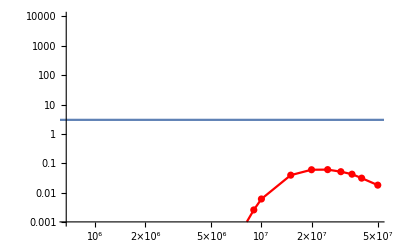

```mathematica
Show[ListLogLogPlot[{falisthigh},PlotStyle-> Red, Mesh-> All,Joined->True,PlotRange->{Automatic,{0.001,10^4}}],LogLogPlot[3,{fa,0.1,10^8}]]
```

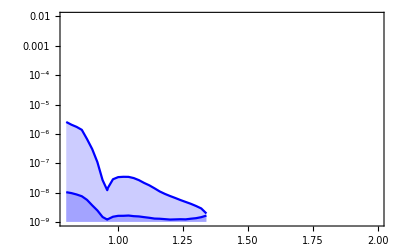

```mathematica
ListLogPlot[{falistmaxhigh,falistminhigh},PlotStyle->Blue,Frame->True,Joined->True,Filling->Bottom,PlotRange->{{0.8,2},{10^-9,10^-2}}]
```

#### Combined constraints from this study

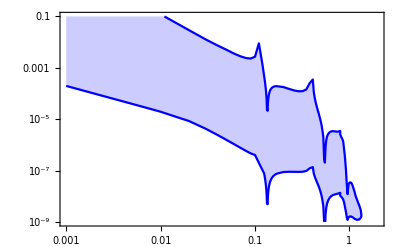

```mathematica
finaldata=Join[falistmin[[7;;Length[falistmin]]],falistminhigh,Reverse[falistmaxhigh],Reverse[falistmax],Reverse[falistmin[[1;;6]]]];
ListLogLogPlot[{finaldata},PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,PlotRange->{{0.001,2},{10^-9,10^-1}}]
```

## Other constraints

#### SN (from 2004.01193)

```mathematica
SNErdata=Import["./SN-Ertas.csv","Data"];
SNErfinal=SNErdata;
SNErfinal[[All,1]]=SNErdata[[All,1]]/10^3;
SNErfinal[[All,2]]=SNErdata[[All,2]]*8/10^3;

SNChFiddata=Import["./SN-Chang-Fiducial.csv","Data"];
SNChFidfinal=SNChFiddata;
SNChFidfinal[[All,1]]=SNChFiddata[[All,1]]/10^3;
SNChFidfinal[[All,2]]=SNChFiddata[[All,2]]*8/10^3;
```

#### Cosmo Updated (from 2002.08370)

```mathematica
mPi=135/1000;
cosmoupdata=Import["./cosmo-updated.csv","Data"];
cosmoupfinal=cosmoupdata;
cosmoupfinal[[All,1]]=cosmoupdata[[All,1]]/10^3;
cosmoupfinal[[All,2]]=cosmoupdata[[All,2]]/(2Pi 1/137 Abs[cgamma[cosmoupfinal[[All,1]],1,1,1]]);
```

```mathematica
cosmoupfinal=Join[{{0.001,0.2},{cosmoupfinal[[1,1]],0.2}},cosmoupfinal]; (*the first two are dummy points, added just for plotting purposes*)
```

#### BaBar Upsilon (from 1810.09452)

```mathematica
BaBarUdata=Import["./BaBar-1810.09452.csv"];
BaBarUfinal=BaBarUdata;
BaBarUfinal[[All,2]]=1/BaBarUdata[[All,2]]/(1000*(2 Pi^2))*10;
(*The last factor=10 is the rescaling from their c1=c2=10 to our c1=c2=1*)
```

#### Low mass summary (from 1810.09452)

```mathematica
LowMassSummarydata=Import["./summary-low-mass-1810.09452.csv"];
LowMassSummaryfinal=LowMassSummarydata;
LowMassSummaryfinal[[All,2]]=1/LowMassSummarydata[[All,2]]/(1000*(2 Pi^2))*10;
```

#### LHC Diphoton (from 1710.01743)

```mathematica
(*LHCDPdata=Import["./LHC-DP-Combined.csv"];
LHCDPfinal=LHCDPdata;
LHCDPfinal[[All,2]]=1/LHCDPfinal[[All,2]]/(2 Pi^2)/1000*10; *)
```

#### BD (from 1709.00009)

```mathematica
BDdata1=Import["./BD1.csv","Data"];
BDdata2=Import["./BD2.csv","Data"];
mPi=135/1000;

BDdata=Join[BDdata2,BDdata1];
BDfinal=BDdata;
BDfinal[[All,2]]=BDdata[[All,2]]/(2Pi 1/137 Abs[cgamma[BDfinal[[All,1]],1,1,1]]);
```

#### E787+E949 (from 2004.01193)

```mathematica
E787codata=Import["./E787-E949-co.csv","Data"];  (* c2 dominated *)
E787cofinal=E787codata;
E787cofinal[[All,1]]=E787codata[[All,1]]/10^3;
E787cofinal[[All,2]]=E787codata[[All,2]]*8/10^3;
```

#### BD+E787+E949

```mathematica
BDE787E949=Join[E787cofinal[[1;;48]],BDfinal[[25;;Length[BDfinal]]]];
```

#### NA62 (from 2004.01193)

```mathematica
NA62codata=Import["./NA62-co-v2.csv","Data"]; (* c2 dominated *)
NA62cofinal=NA62codata;
NA62cofinal[[All,1]]=NA62codata[[All,1]]/10^3;
NA62cofinal[[All,2]]=NA62codata[[All,2]]*8/10^3;
```

#### HL LHC Projection (from 1710.01743)

```mathematica
HLLHCDPdata=Import["./HL-LHC-DP.csv"];
HLLHCDPfinal=HLLHCDPdata;
HLLHCDPfinal[[All,2]]=1/HLLHCDPfinal[[All,2]]/(2 Pi^2)/1000*10;
```

#### High mass summary (from 1710.01743)

```mathematica
HighMassSummaryData=Import["./High-mass-summary.csv"];
HighMassSummaryFinal=HighMassSummaryData;
HighMassSummaryFinal[[All,2]]=1/HighMassSummaryData[[All,2]]/(2 Pi^2)/1000*10;
```

#### LHCb projection (from 1810.09452)

```mathematica
LHCbprojData=Import["./LHCbproj.csv"];
LHCbprojFinal=LHCbprojData;
LHCbprojFinal[[All,2]]=1/LHCbprojData[[All,2]]/(2 Pi^2)/1000*10;
```

#### Theory parameters

```mathematica
Λmax=1658.047000156266;
Mp=2.4*10^18;
dim=6;
```

#### Not shown are KTEV, NA62+48 bounds (e.g. 2005.05170) relevant only for ~ 150-350 MeV. Also not shown are NA62 and KOTO projections.

### CMS Track Trigger Search

#### Efficiency factors, m_a,f_a in GeV

```mathematica
faMaPlane3evwPT30={{1,8181},{1.3,44323},{1.5,65725},{1.8,58076},{2,55909},{4,91016},{6,167220},{8,244103},{10,331492},{12,444057},{14,611733},{16,788218},{18,10^6},{20,1.3*10^6},{22,2.18*10^6},{22,2.47*10^6},{20,3*10^6},{18,3.4*10^6},{16,3.7*10^6},{14,3.9*10^6},{12,3.9*10^6},{10,3.78*10^6},{8,3.4*10^6},{6,2.84*10^6},{4,2*10^6},{2,783193},{1.8,651661},{1.5,598502},{1.3,340571},{1,164980}};
faMaPlane10evwPT30={{1,10232},{1.3,56618},{1.5,86419},{1.8,72533},{2,71082},{4,118362},{6,198543},{8,307219},{10,454181},{12,652662},{14,1.16*10^6},{14,1.54*10^6},{12,1.9*10^6},{10,2.1*10^6},{8,2.1*10^6},{6,1.9*10^6},{4,1.43*10^6},{2,541037},{1.8,453630},{1.5,413415},{1.3,198115},{1,112029}};
faMaPlane3evwHT100={{1,10880},{1.3,68957},{1.5,99307},{1.8,78132},{2,76631},{3,91054},{4,128554},(*{5,506851},*){6,211161},{8,328672},{10,505132},{12,740787},{13,1.16*10^6},{13,1.26*10^6},{12,1.5*10^6},{10,1.8*10^6},{8,1.8*10^6},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,1.67*10^6},(*{5,1.6*10^6},*){4,1.26*10^6},{3,941794},{2,474137},{1.8,391229},{1.5,360560},{1.3,155171},{1,100209}};
faMaPlane10evwHT100={(*{1,13023},*){1.8,137614},{2,107819},{3,130311},{4,172397},{5,239091},{6,306412},{7,459224},{7.5,601353},{7.5,679669},{7,780808},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,884514},{5,888240},{4,789501},{3,605536},{2,287247},{1.8,202213}(*,{1,74655}*)};
```

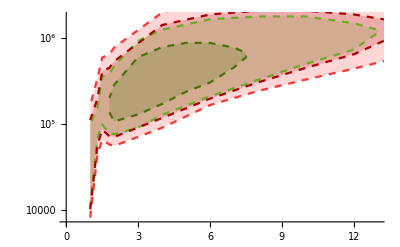

```mathematica
Show[ListLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom]]
```

```mathematica
faMaPlane10evwHT100[[All,2]]
```

{137614,107819,130311,172397,239091,306412,459224,601353,679669,780808,884514,888240,789501,605536,287247,202213}

```mathematica
scaledfaMaPlane10evwHT100=faMaPlane10evwHT100;
scaledfaMaPlane10evwHT100[[All,2]]=1/(4 Pi^2 faMaPlane10evwHT100[[All,2]]);
scaledfaMaPlane10evwPT30=faMaPlane10evwPT30;
scaledfaMaPlane10evwPT30[[All,2]]=1/(4 Pi^2 faMaPlane10evwPT30[[All,2]]);
scaledfaMaPlane3evwHT100=faMaPlane3evwHT100;
scaledfaMaPlane3evwHT100[[All,2]]=1/(4 Pi^2 faMaPlane3evwHT100[[All,2]]);
scaledfaMaPlane3evwPT30=faMaPlane3evwPT30;
scaledfaMaPlane3evwPT30[[All,2]]=1/(4 Pi^2 faMaPlane3evwPT30[[All,2]]);
```

## Final Plots

```mathematica
invfGtoinvfa={{1/(4 Pi^2*10^2),"10^2",{0.02,0},{}},{1/(4 Pi^2*10^3),"10^3",{0.02,0},{}},{1/(4 Pi^2*10^4),"10^4",{0.02,0},{}},{1/(4 Pi^2*10^5),"10^5",{0.02,0},{}},{1/(4 Pi^2*10^6),"10^6",{0.02,0},{}},{1/(4 Pi^2*10^7),"10^7",{0.02,0},{}},{1/(4 Pi^2*10^8),"10^8",{0.02,0},{}},{1/(4 Pi^2*10^9),"10^9",{0.02,0},{}},{1/(4 Pi^2*10^10),"10^10",{0.02,0},{}},{1/(4 Pi^2*10^11),"10^11",{0.02,0},{}}};
For[k=-11,k<-1,k++,For[j=2,j<10,j++,AppendTo[invfGtoinvfa,{j*1/(4 Pi^2)*10^k," ",{0.01,0},{}}]]]
```

```mathematica
Show[ListLogLogPlot[finaldata,PlotStyle->Red,Frame->True,Joined->True,Filling->Top,FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G[\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],Style[MaTeX["f_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black]},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{0.001,10^2},{10^-9,10^-3}},FrameTicks->{{LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks->True],(*LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks-> True]*)invfGtoinvfa},{LogTicks[10,0.001,10^4],LogTicks[10,0.001,10^4,ShowTickLabels-> False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Framed[MaTeX["\\textbf{Codominance}",Magnification->1.2],FrameStyle->{Black,Thickness[1],Background->Opacity[1,White]},RoundingRadius->5],{15,Black},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-8.4]}],20], Style[Text[Style[Rotate["SN1987A",-0.5],{15,Gray},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-7.5]}],20],Style[Text[Style[Rotate["BBN+N_eff",-Pi/2],{15,Gray},FontFamily->"CMU Serif"],{Log[1.7*10^-3],Log[10^-3.7]}],20],Style[Text[Style[Rotate["DUNE ND",-0.8],{15,Red},FontFamily->"CMU Serif"],{Log[0.05],Log[10^-6.4]}],20],Style[Text[Style[Rotate["Existing Constraints",0.0],{15,Gray},FontFamily->"CMU Serif"],{Log[0.02],Log[10^-4.5]}],20],Style[Text[Style[Rotate["LHC Track Trigger",-0.65],{15,Darker[Orange,0.2]},FontFamily->"CMU Serif"],{Log[10],Log[10^-6.7]}],20],Style[Text[Style[Rotate["NA62",0.0],{15,Lighter[Purple,0.4]},FontFamily->"CMU Serif"],{Log[0.008],Log[10^-5.6]}],20],Style[Text[Style[Rotate["Colored Particles",0.0],{15,Lighter[Gray,0.1]},FontFamily->"CMU Serif"],{Log[10^-2],Log[10^-3.5]}],20],Style[Text[Style[Rotate["LHCb γγ",0.0],{15,Lighter[Green,0.5]},FontFamily->"CMU Serif"],{Log[5],Log[10^-3.7]}],20],Style[Text[Style[Rotate["HL-LHC γγ",0.0],{15,Lighter[Green,0.5]},FontFamily->"CMU Serif"],{Log[25],Log[10^-4.7]}],20],Style[Text[Style[Rotate["H' Quality Problem",0.45],{15,Blue},FontFamily->"CMU Serif"],{Log[20],Log[10^-8.3]}],15],Style[Text[Style[Rotate["PQ Quality Problem",-0.2],{15,Blue},FontFamily->"CMU Serif"],{Log[10^-2.0],Log[10^-7.7]}],20],Style[Text[Style[Rotate["QCD Axion",0.35],{15,Brown},FontFamily->"CMU Serif"],{Log[10^-2.3],Log[10^-1.7]}],20],Style[Text[Style[Rotate["f_a < Λ_QCD'",-0.35],{15,Brown},FontFamily->"CMU Serif"],{Log[10^1],Log[5*10^-3]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}],ListLogLogPlot[SortBy[SNErfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[SortBy[SNChFidfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[cosmoupfinal,PlotStyle->{Gray,Dashed},Filling->Bottom,Joined->True],
ListLogLogPlot[LHCbprojFinal,PlotStyle->{Lighter[Green,0.5],DotDashed},Joined->True],
ListLogLogPlot[LowMassSummaryfinal,PlotStyle->{Gray},Filling->1,Joined->True](*,ListLogLogPlot[BDfinal,PlotStyle->{Gray},Filling->Top,Joined->True]*)(*,ListLogLogPlot[E787cofinal,PlotStyle->{Gray},Filling->Top,Joined->True]*)
,ListLogLogPlot[BDE787E949,PlotStyle->{Gray},Filling->Top,Joined->True],ListLogLogPlot[NA62cofinal,PlotStyle->{Lighter[Purple,0.4],DotDashed},Joined->True],ListLogLogPlot[HLLHCDPfinal,PlotStyle->{Lighter[Green,0.5],DotDashed},Joined->True],ListLogLogPlot[HighMassSummaryFinal,PlotStyle->{Gray},Joined->True,Filling->Top],ListLogLogPlot[scaledfaMaPlane3evwPT30,Joined->True,PlotStyle->{DotDashed,Darker[Orange,0.2]}(*,Filling->Bottom*)],LogLogPlot[{1/(4 Pi^2 Sqrt[0.6]*(alphas[10^6]^-0.4*Λmax)^2/ma),1/(4 Pi^2(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2))),1/(4 Pi^2 ma),ma/(4 Pi^2 mPi fpi),1/(2000Pi)},{ma,10^-3,10^4},PlotStyle->{None,None,None,None,None},Filling->{1->{Bottom,Directive[Blue,Opacity[0.2]]},2->{Bottom,Directive[Blue,Opacity[0.2]]},3->{Top,Directive[Brown,Opacity[0.2]]},4->{Top,Directive[Brown,Opacity[0.2]]},5->{Top,Directive[Gray,Opacity[0.2]]}}]]
```

-Graphics-